```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
range100=DeleteCases[Range[-100,100],0];
range200=DeleteCases[Range[-200,200],0];
```

```mathematica
LaunchKernels[14];(* To launch kernels for Parallel tasks *)
```

```mathematica
(*net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];*)
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];*)
```

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
theta1byΔu0[k_, nq_, qInPower_] := allprodθbyΔ[1,k, 2, 0, 3, 0, 4, 0, nq, 0,qInPower]
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
theta3byΔu0[m_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, m, 4, 0, nq, 0,qInPower]
theta4byΔu0[n_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, 0, 4, n, nq, 0,qInPower]
```

```mathematica
allprodθwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_, qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq,cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
(*cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,q^((k+l)/4+mnnonzero-qInPower)Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
(*dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];*)
dt =Join[cq2[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq2]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
klmnpos[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnposonly[rng_,n_]:= Values[FindInstance[{0<a<rng, 0<b<rng, 0<c<rng,0<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnneg[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d<0},{a,b,c,d},Integers, n]];
klmnnegonly[rng_,n_]:= Values[FindInstance[{-rng<a<0, -rng<b<0, -rng<c<0, -rng<d<0, a+b+c+d<0},{a,b,c,d},Integers, n]];
```

```mathematica
powerspos[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
powersneg[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]<0]
```

```mathematica
allprodgen[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn.txt";
filename2=NotebookDirectory[]<>"monitor.txt";   (*For positive powers*)
(*filename=NotebookDirectory[]<>"jacobi-klmn-neg-only.txt";
filename2=NotebookDirectory[]<>"monitor-neg-only.txt";*)
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenneg[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitor-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenbyΔneg[nq_,nu_,pwrlistref_,pwrlist_,qInPower_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobibyΔ-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitorbyΔ-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθbyΔwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu,qInPower}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
listtorule[list_] := list[[;;-2]] -> list[[-1]]
```

```mathematica
extractMF[data_]:=Module[{data2,data3,data4,data5,mfdata,indices,indlens,i},
data2=StringDelete[StringDelete[data," "],"\n"];
indices=Union/@StringPosition[data2,"{"]//Flatten;
indlens=indices[[#+1]]-indices[[#]]&/@Range[Length[indices]-1];
data3=Table[StringTake[data2,{indices[[i+1]],indices[[i+2]]-2}],{i,Length[indlens]-1}];
data4=ToExpression/@data3/.{$Failed->Nothing,Null->Nothing}//Quiet;
data5=Cases[data4,x_/;Length[x]>4];
mfdata=listtorule/@data5;
Return[mfdata]
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## Modular forms from powers of Δ

## Half-integer negative powers, first few coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
DumpSave["dnexactw200.mx", dnexactw200];
```

```mathematica
<<dnexactw200.mx
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
```

```mathematica
weights=Table[w,{w,-1/2, minweight, -1/2}];
```

```mathematica
data=Thread[dnexactw200[[;;,;;30]]->weights];
datanorm = Thread[dnexactw200norm30[[;;,;;30]]->weights];
Length[data]
```

400

```mathematica
data=datapartition[data];
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];*)
dnexactw200norm30csv = Flatten[#, 1] & /@ Transpose[{N[Keys[datanorm]],N[Values[datanorm]]}];
Export["CSV/dnexactw200norm30.csv", dnexactw200norm30csv];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
Length/@data
Length/@datanorm
```

{300,60,40}

{300,60,40}

```mathematica
Transpose[{enc[Keys[data]],N[Values[data]]}]
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindata[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

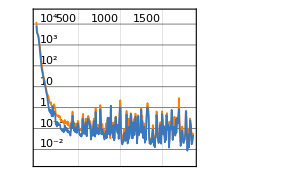
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9316  rounds:1863  time:31s  examples/s:19858
data | ,,  training examples:300  validation examples:60  processed examples:596224  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:8.15×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

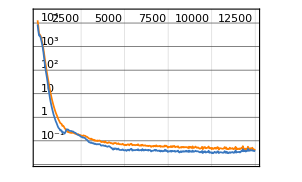
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.4min  examples/s:10375
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.5×10^-2
validation | ,,  loss:2.93×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,LearningRate->.0001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm30[[;;,2]]
```

{-19/2,-27,-59/2,-65/2,-69/2,-79/2,-44,-89/2,-97/2,-109/2,-66,-74,-165/2,-86,-99,-199/2,-102,-106,-231/2,-239/2,-241/2,-269/2,-136,-273/2,-141,-297/2,-303/2,-153,-154,-162,-325/2,-329/2,-167,-341/2,-175,-353/2,-355/2,-183,-187,-381/2}

```mathematica
testpred = wNet/@testdatanorm30[[;;,1]]
```

{-9.52103,-26.9979,-29.4777,-32.4316,-34.533,-39.4912,-44.0199,-44.5134,-48.4781,-54.5122,-66.183,-73.8761,-82.6136,-86.2296,-98.6488,-99.2086,-101.957,-106.184,-115.446,-119.046,-119.921,-134.695,-136.236,-136.744,-141.196,-148.163,-150.803,-152.184,-153.325,-162.06,-162.583,-164.653,-167.184,-170.628,-174.894,-176.339,-177.376,-182.916,-187.039,-190.545}

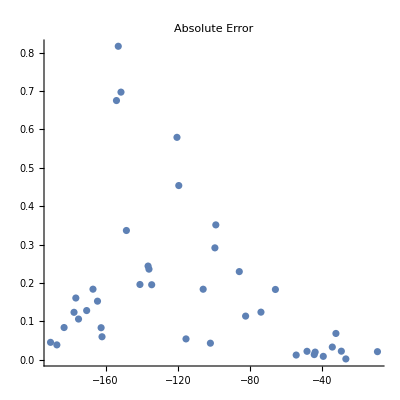

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

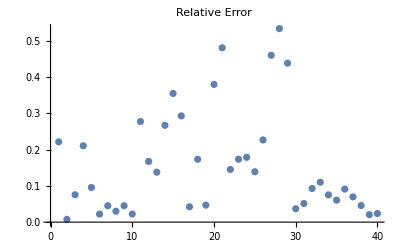

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.159219

## Real negative powers (chosen at random)

```mathematica
minweight = -300;
coeffnum=50;
datasize=500;
```

```mathematica
weights=Rationalize[SetPrecision[RandomReal[{minweight,-0.01},datasize], 4], 0];
```

```mathematica
dnexactwrandom = ParallelTable[ If[Mod[weights[[i]],12]==0,  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]}]//Normal], q]],{i,datasize}];
```

```mathematica
dnexactwrandomnorm20=Normalize/@dnexactwrandom[[;;,;;20]];
Length[dnexactwrandomnorm20]
```

500

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datapartition[Thread[dnexactwrandomnorm20->weights]];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=8500;
```

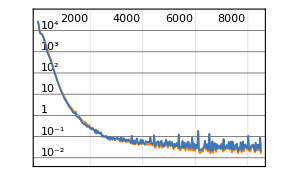
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:51000  rounds:8500  time:1.2min  examples/s:45766
data | ,,  training examples:375  validation examples:75  processed examples:3264000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.42×10^-2
validation | ,,  loss:1.89×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{-3046/11,-1745/8,-3042/11,-497/6,-299/8,-811/3,-866/7,-799/6,-4357/21,-1139/19,-233/16,-179/3,-678/7,-1011/4,-763/15,-985/6,-853/4,-279/2,-1715/9,-736/7,-793/4,-1417/7,-151/27,-1239/5,-1081/5,-1530/23,-859/6,-1109/4,-1787/20,-4229/15,-1311/5,-2553/20,-134/27,-1588/17,-1825/8,-243/4,-1491/16,-752/7,-1115/4,-666/7,-2651/13,-4178/15,-739/5,-301/4,-544/13,-1137/4,-203/19,-509/4,-667/9,-1039/4}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{-276.897,-218.034,-276.529,-82.5552,-37.3054,-270.334,-123.862,-132.946,-207.451,-59.9074,-14.5591,-59.631,-97.0301,-252.721,-51.0785,-164.011,-213.292,-139.292,-190.535,-105.146,-198.35,-202.403,-5.37989,-247.756,-216.182,-66.3861,-143.219,-277.241,-89.2658,-282.022,-262.139,-127.743,-4.86398,-93.5382,-228.142,-60.6949,-93.3068,-107.296,-278.746,-95.3076,-203.822,-278.529,-147.997,-75.3299,-42.0091,-284.406,-10.748,-127.356,-74.2008,-259.74}

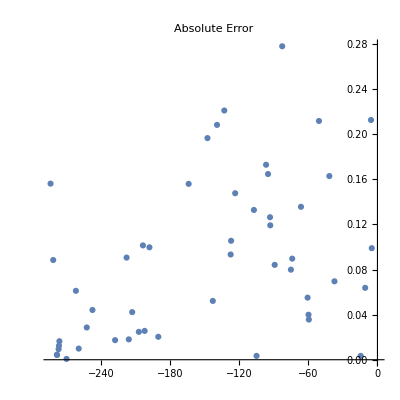

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

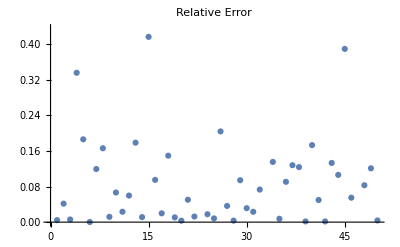

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.20917

## Half-integer positive powers

```mathematica
maxweight=200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, 1/2, maxweight,1/2}];
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
Length[dnexactw200norm30]
```

400

```mathematica
weights=Table[w,{w,1/2, maxweight,1/2}];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
enc20=enc[datanorm20]
```

NetEncoder[…]

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->enc[datanorm20],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=1000;
```

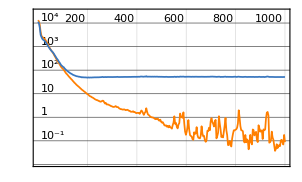
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5000  rounds:1000  time:20s  examples/s:16500
data | ,,  training examples:300  validation examples:60  processed examples:320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.1×10^-2
validation | ,,  loss:5.05×10^1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{9/2,7,14,18,19,47/2,63/2,32,36,77/2,93/2,49,119/2,63,133/2,135/2,68,74,153/2,83,173/2,87,92,195/2,103,217/2,109,115,235/2,118,129,261/2,145,160,323/2,168,337/2,182,375/2,399/2}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{32.7495,40.4468,13.5711,18.9925,26.389,16.8142,42.3371,41.4432,35.0897,35.2522,42.1938,47.0957,62.6246,65.7443,74.8455,79.1192,78.4922,75.4566,75.1137,88.0934,74.729,70.8939,89.1665,95.0932,99.7713,87.7444,84.9917,113.78,116.326,116.764,129.223,130.823,144.673,160.032,161.667,168.951,169.486,182.432,187.001,195.445}

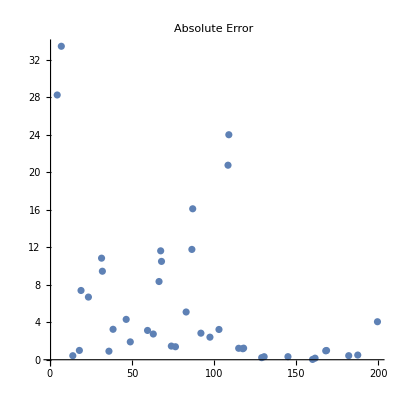

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

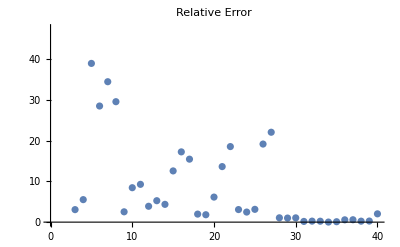

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

35.594

## Randomly chosen slice of coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
```

```mathematica
numsamp=20;
```

```mathematica
weights=Table[w,{w, -1/2, minweight, -1/2}];
```

```mathematica
randsamp=Sort[RandomSample[Range[coeffnum],numsamp]]
```

{1,4,7,9,10,13,14,16,18,19,20,21,23,25,30,32,33,41,42,48}

```mathematica
rawdata = dnexactw200[[;;,randsamp]];
normdata=Normalize/@dnexactw200[[;;,randsamp]];
Length[rawdata]
```

400

```mathematica
data=datapartition[Thread[rawdata->weights]];
datanorm=datapartition[Thread[normdata->weights]];
Length[data]
```

3

```mathematica
{traindata,valdata,testdata}=data;
{traindatanorm,valdatanorm,testdatanorm}=datanorm;
```

```mathematica
(*{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;*)
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindatanorm[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm[[1]]],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

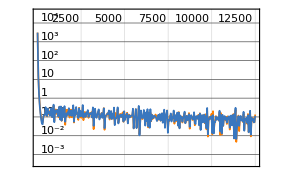
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.9min  examples/s:9709
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.3×10^-3
validation | ,,  loss:7.94×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm,All,ValidationSet->valdatanorm,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm[[;;,2]]
```

{-23/2,-22,-27,-57/2,-48,-51,-111/2,-65,-68,-151/2,-80,-165/2,-84,-89,-195/2,-101,-102,-103,-207/2,-215/2,-112,-227/2,-253/2,-127,-129,-267/2,-134,-271/2,-136,-140,-144,-309/2,-162,-167,-335/2,-337/2,-174,-355/2,-381/2,-196}

```mathematica
testpred = wNet/@testdatanorm[[;;,1]]
```

{-11.5234,-21.9508,-27.0963,-28.5272,-47.9875,-50.9815,-55.5673,-64.9612,-67.9749,-75.4755,-79.979,-82.475,-83.9846,-88.9922,-97.4766,-100.973,-101.98,-102.985,-103.486,-107.499,-112.013,-113.509,-126.507,-127.003,-128.979,-133.446,-133.939,-135.471,-135.979,-140.003,-144.01,-154.531,-161.84,-166.994,-167.503,-168.515,-174.,-177.469,-190.507,-195.988}

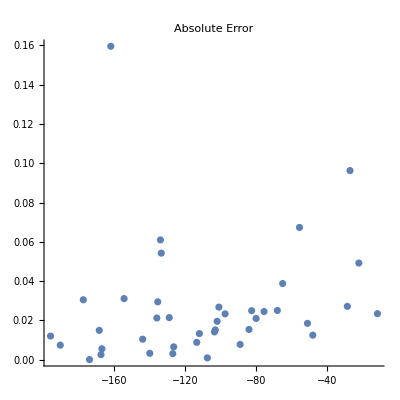

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

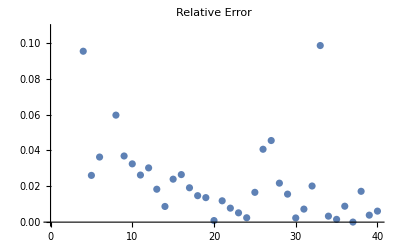

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0427851

## Mock modular forms

## Generating data for negative weights

```mathematica
minweight = -100;
coeffnum=50;
```

```mathematica
cne50w100 = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, -1/2,minweight, -1/2}];
```

```mathematica
w100 = Table[w, {w, -1/2, minweight, -1/2}];
```

## Normalized 10 coefficients

```mathematica
cne50w100norm10=Normalize/@cne50w100[[;;,;;10]];
```

```mathematica
data=MapThread[Rule,{cne10w100,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->10,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

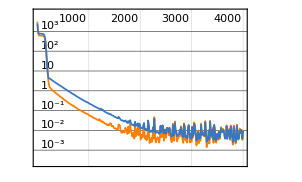
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:53452
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:2.75×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-19,-55/2,-30,-31,-45,-49,-103/2,-111/2,-57,-71,-79,-165/2,-83,-86,-181/2,-189/2,-96}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-11.8579,-18.9686,-27.5082,-30.0013,-31.0176,-45.0016,-49.0026,-51.5023,-55.5074,-57.0019,-71.0107,-79.0108,-82.5823,-83.0482,-85.963,-90.5124,-94.4849,-95.9833}

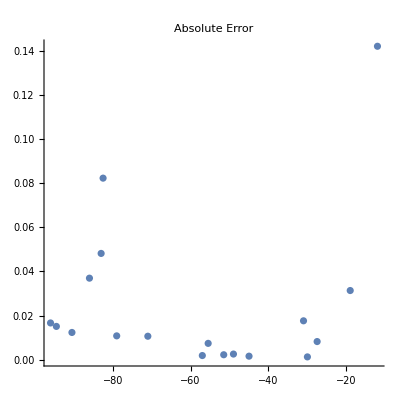

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

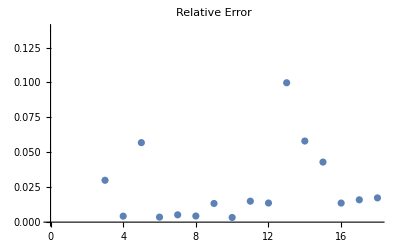

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0970438

## Normalized 30 coefficients

```mathematica
cne50w100norm30=Normalize/@cne50w100[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm30,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

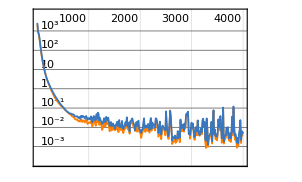
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46363
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.13×10^-4
validation | ,,  loss:5.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-4,-9/2,-10,-11,-19,-45/2,-35,-36,-41,-87/2,-49,-103/2,-62,-64,-66,-159/2,-173/2,-89,-181/2,-91}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-4.01904,-4.50736,-9.99175,-10.9861,-18.9724,-22.478,-34.9868,-35.9882,-40.9995,-43.4913,-48.993,-51.4901,-61.9679,-64.0045,-65.9944,-79.508,-86.5306,-89.0009,-90.4528,-90.9761}

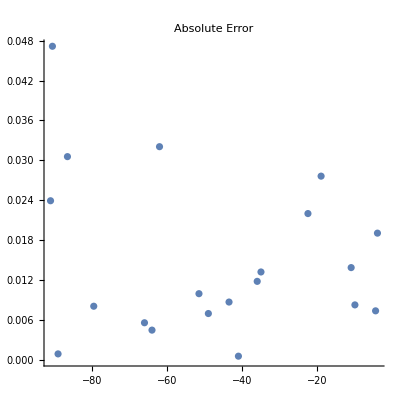

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

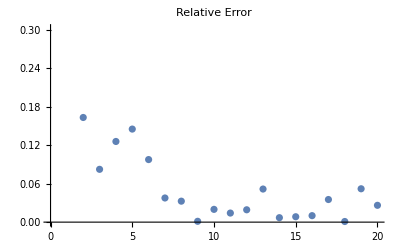

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0704135

## 30 coefficients starting at 11th coefficient

```mathematica
cne50w100norm11to40=Normalize/@cne50w100[[;;,11;;40]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm11to40,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

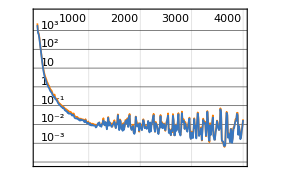
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:45839
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.86×10^-3
validation | ,,  loss:2.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-1,-17/2,-19/2,-13,-29/2,-39/2,-45/2,-25,-51/2,-65/2,-33,-71/2,-43,-44,-61,-123/2,-71,-187/2,-94,-199/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-0.984623,-8.48011,-9.48186,-12.9901,-14.5167,-19.476,-22.4832,-24.9928,-25.4965,-32.5007,-32.9923,-35.4475,-43.0156,-44.003,-61.0033,-61.5056,-70.9836,-93.4771,-93.9854,-99.4147}

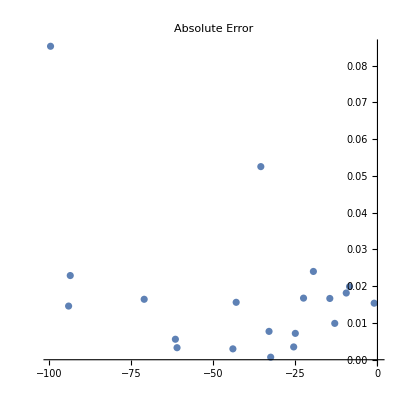

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

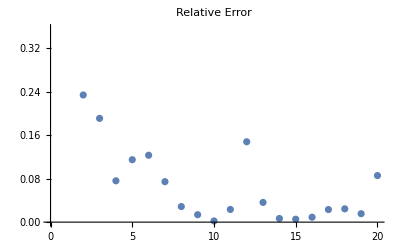

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.138669

## Generating data for positive weights

```mathematica
maxweight = 100;
coeffnum=50;
```

```mathematica
cne50w100plus = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, 0,maxweight,1/2}];
```

```mathematica
w100plus = Table[w, {w, 0,maxweight,1/2}];
```

## Normalized 30 coefficients

```mathematica
cne50w100plusnorm30=Normalize/@cne50w100plus[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100plusnorm30,w100plus}];
datasize=Length[data]
```

201

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=6000;
```

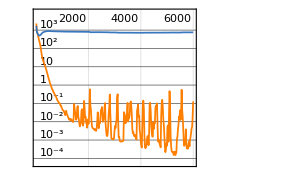
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:18000  rounds:6000  time:37s  examples/s:31805
data | ,,  training examples:150  validation examples:30  processed examples:1152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.91×10^-1
validation | ,,  loss:7.44×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]];
testpred = wNet/@testdata[[;;,1]];
```

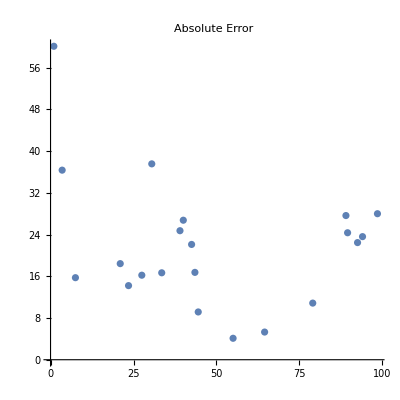

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

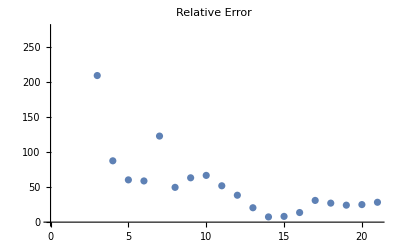

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

383.266

## Coefficients calculated via Kloosterman sums

```mathematica
minweight = -100;
coeffnum=30;
```

```mathematica
cn0c30w100 = Table[If[Mod[w,12]==0,Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
cn0c30w100norm30=Normalize/@cn0c30w100;
```

```mathematica
data=MapThread[Rule,{cn0c30w100norm30,wlist}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

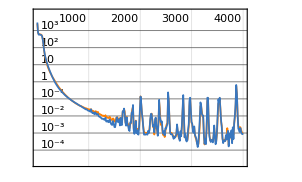
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:18s  examples/s:44348
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.83×10^-4
validation | ,,  loss:9.05×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-15,-33/2,-24,-49/2,-53/2,-29,-81/2,-83/2,-101/2,-59,-63,-147/2,-165/2,-173/2,-87,-88,-96,-100}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.9777,-16.5018,-24.0065,-24.5083,-26.4925,-29.,-40.5015,-41.5083,-50.4848,-58.9991,-62.9952,-73.4979,-82.4828,-86.4799,-86.9727,-87.9872,-96.0273,-99.8619}

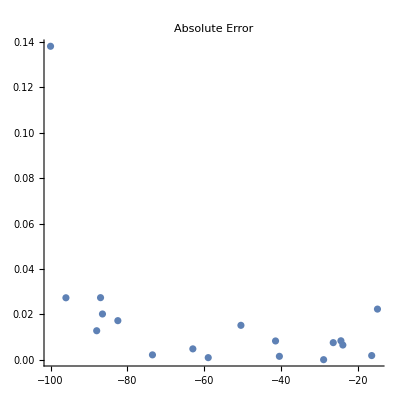

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

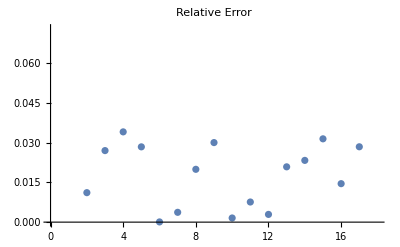

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0317603

## Comparing the real and imaginary parts of Kloosterman sums

```mathematica
minweight=-100;
coeffnum=30;
```

### Absolute values of part 1

```mathematica
cnc50w150abs1 = Table[If[Mod[w,12]==0,Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs1norm=Normalize/@cnc50w150abs1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

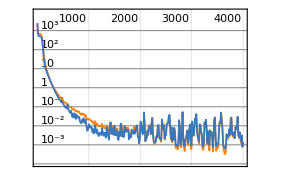
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:52883
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.18×10^-4
validation | ,,  loss:5.83×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-13,-14,-47/2,-24,-49/2,-41,-42,-44,-52,-63,-127/2,-129/2,-75,-159/2,-85,-177/2,-179/2,-195/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.9862,-13.9781,-23.553,-24.0385,-24.5241,-40.9001,-41.9487,-44.0116,-52.0027,-63.0056,-63.5005,-64.5098,-75.0047,-79.4928,-85.0017,-88.4656,-89.4739,-97.5091}

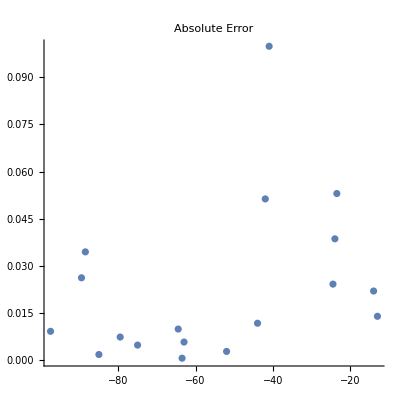

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

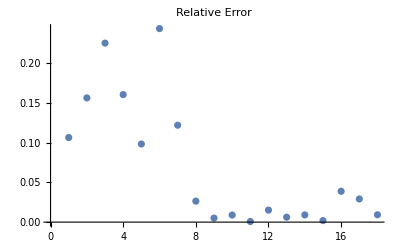

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0702341

### Real values of part 1

```mathematica
cnc50w150re1 = Table[If[Mod[w,12]==0,Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re1norm=Normalize/@cnc50w150re1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

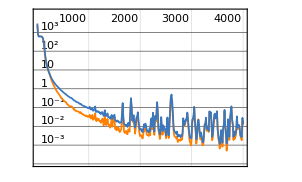
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:16s  examples/s:48043
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.8×10^-2
validation | ,,  loss:1.44×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-13,-27/2,-29/2,-43/2,-36,-45,-46,-113/2,-127/2,-64,-137/2,-75,-173/2,-93,-193/2,-97,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.3518,-17.5069,-15.584,-14.4611,-21.5254,-35.994,-45.0078,-45.9739,-56.5226,-63.519,-63.9957,-68.5148,-75.0058,-86.4915,-93.0252,-96.5665,-97.029,-98.5011}

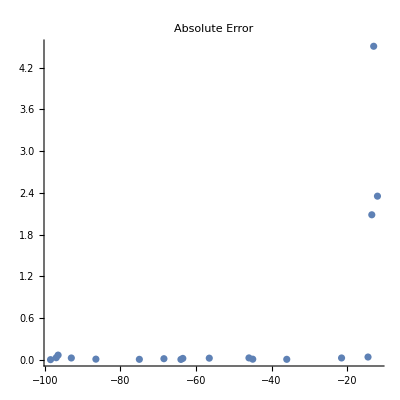

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

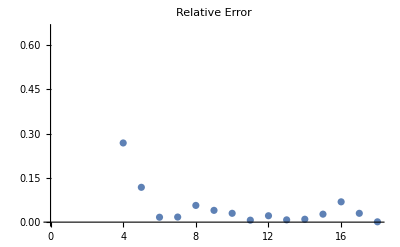

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.91242

### Absolute values of part 2

```mathematica
cnc50w150abs2 = Table[If[Mod[w,12]==0,Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs2norm=Normalize/@cnc50w150abs2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

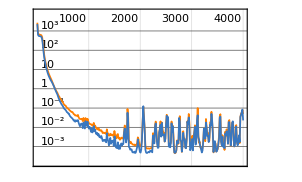
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46741
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.81×10^-2
validation | ,,  loss:4.77×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-25/2,-13,-49/2,-25,-63/2,-35,-75/2,-87/2,-101/2,-103/2,-54,-72,-73,-153/2,-86,-185/2,-187/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.2684,-12.6735,-13.0893,-24.4973,-25.0022,-31.5062,-34.9512,-37.5227,-43.4946,-50.5049,-51.5018,-54.0035,-71.998,-72.9912,-76.5007,-85.9957,-92.4892,-93.4893}

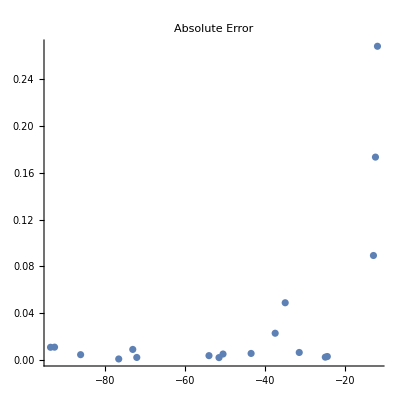

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

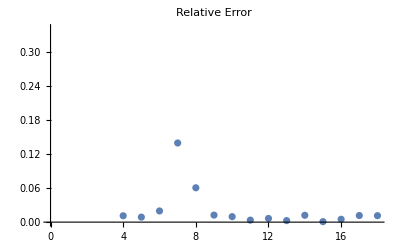

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.257055

### Real values of part 2

```mathematica
cnc50w150re2 = Table[If[Mod[w,12]==0,Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re2norm=Normalize/@cnc50w150re2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

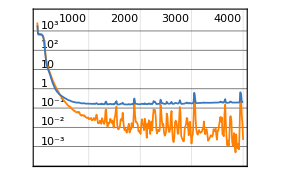
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:47423
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.93×10^-3
validation | ,,  loss:1.94×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-18,-45/2,-61/2,-65/2,-99/2,-101/2,-52,-53,-107/2,-123/2,-129/2,-133/2,-70,-75,-88,-91,-189/2,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-17.9894,-22.5604,-30.5035,-32.4917,-49.4998,-50.4841,-51.9909,-52.999,-53.4809,-61.4894,-64.4768,-66.4838,-69.9518,-74.9958,-87.9364,-91.032,-94.4711,-98.2707}

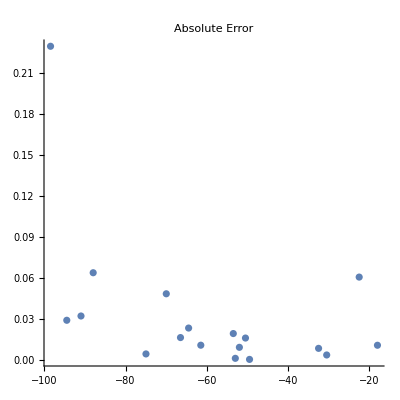

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

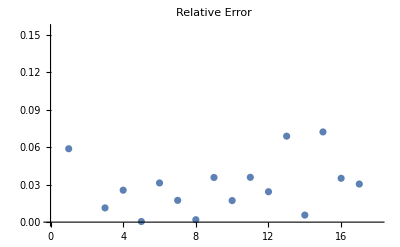

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0541437

## θ_1^k θ_2^l

0.351244 mean relative error for θ_1^m θ_2^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k20l20q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 70, 80], {k, 20}, {l, 20}];
DumpSave["t1t2k20l20q70u80mfpos1.mx", t1t2k20l20q70u80mfpos1];
```

### t1t2k20l20q70u80mfpos1, net0, 26 coeffs(r)

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

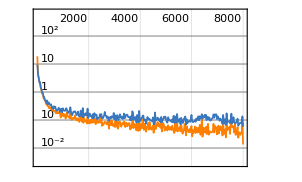
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

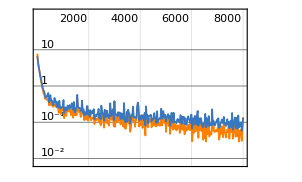
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

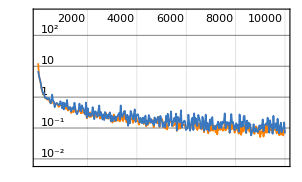
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

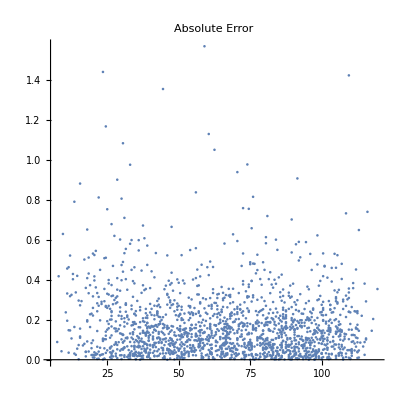

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

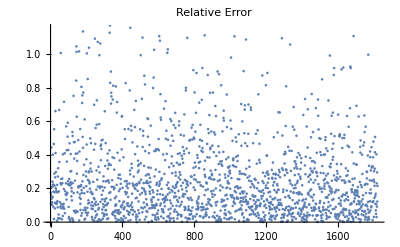

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t1t2k20l20q70u80mfpos1, net3, 26 coeffs

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k5l5q50u60mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k5l5q50u60mfneg.mx", t1t2k5l5q50u60mfneg];
t1t2k10l10q70u80mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k10l10q70u80mfneg.mx", t1t2k10l10q70u80mfneg];
```

#### t1t2k5l5q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

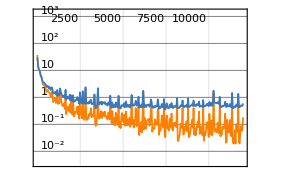
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:3.6min  examples/s:36024
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.67×10^-1
validation | ,,  loss:9.68×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

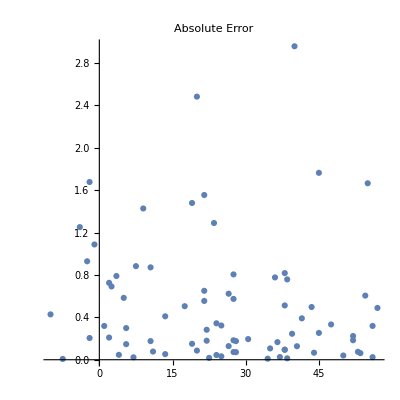

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

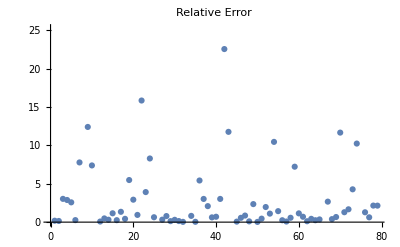

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.05481

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t1t2k5l5q50u60mfneg, Net3, 26 coeffs

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

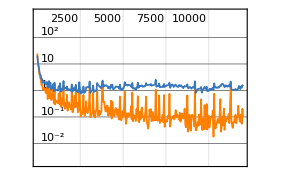
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.7min  examples/s:27360
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.22×10^-2
validation | ,,  loss:1.03
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

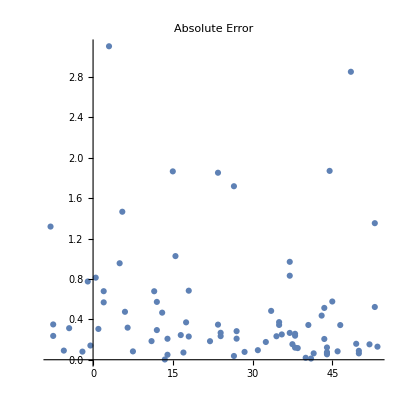

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

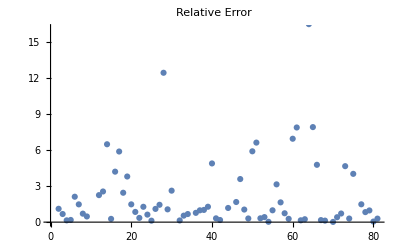

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

8.21258

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_3^m θ_4^n

0.144678 mean relative error for θ_3^m θ_4^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t3t4m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 5}, {n, 5}];
DumpSave["t3t4m5n5q70u80mfpos1.mx", t3t4m5n5q70u80mfpos1];
```

```mathematica
t3t4m20n20q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 20}, {n, 20}];
DumpSave["t3t4m20n20q70u80mfpos1.mx", t3t4m20n20q70u80mfpos1];
```

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

```mathematica
(*t3t4m20n20q30u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,30,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q30u50mfpos1.mx", t3t4m20n20q30u50mfpos1];*)
(*t3t4m20n20q50u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,50,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q50u50mfpos1.mx", t3t4m20n20q50u50mfpos1];*)
(*t3t4m20n20q70u100mfpos1 = ParallelTable[prod1pos[3,m, 4, n,70,100], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q70u100mfpos1.mx", t3t4m20n20q70u100mfpos1];*)
```

### t3t4m20n20q70u80mfpos1, net0, 35 coeffs(r)

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

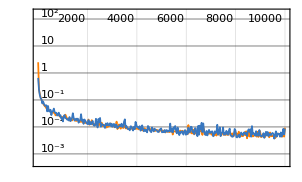
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

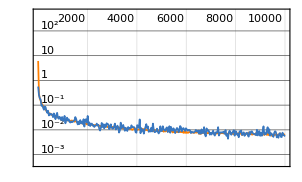
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

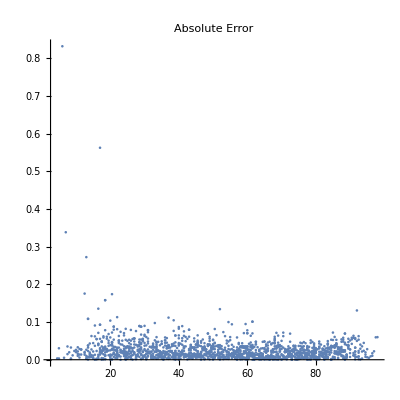

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

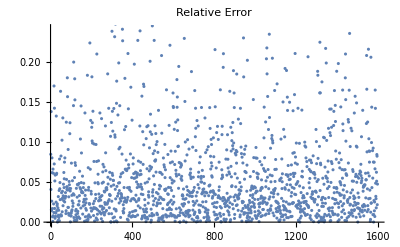

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t3t4m20n20q70u80mfpos1, net3, 35 coeffs

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*t3t4m3n3q40u50mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 40, 50], {m, -1, -3, -1}, {n, -1, -3, -1}];
DumpSave["t3t4m3n3q40u50mfneg.mx", t3t4m3n3q40u50mfneg];*)
t3t4m5n5q50u60mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 50, 60], {m, -1, -5, -1}, {n, -1, -5, -1}];
DumpSave["t3t4m5n5q50u60mfneg.mx", t3t4m5n5q50u60mfneg];
```

#### t3t4m5n5q50u60mfneg, Net0, 25 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

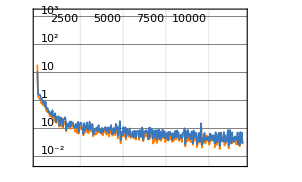
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:3.4min  examples/s:33696
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.41×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

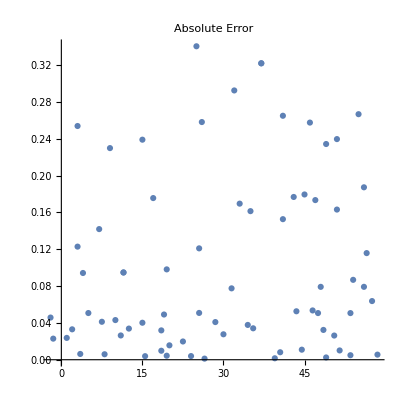

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

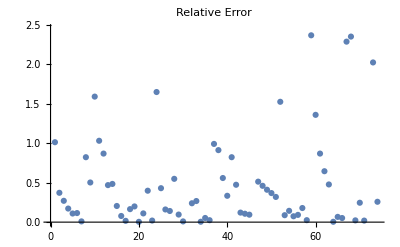

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.66833

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 25 coeffs(r)

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

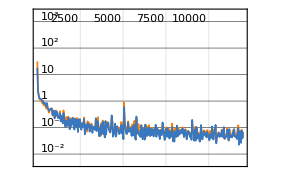
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:5.4min  examples/s:21228
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.88×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

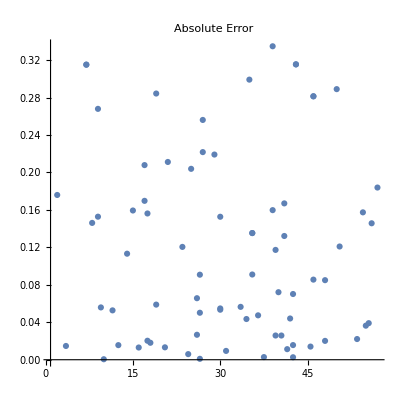

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

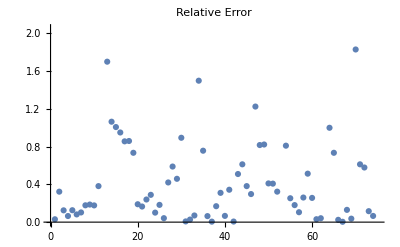

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.666275

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net0, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

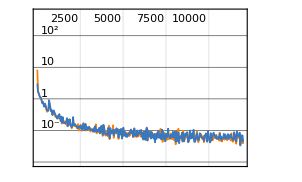
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:5.8min  examples/s:17778
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:3.47×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

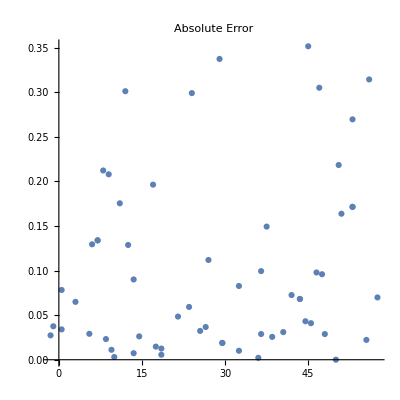

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

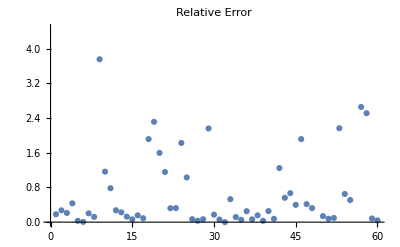

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.992729

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

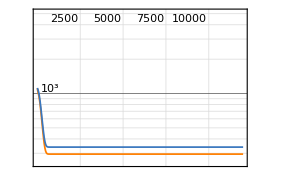
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:8.1min  examples/s:12612
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^2
validation | ,,  loss:3.39×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

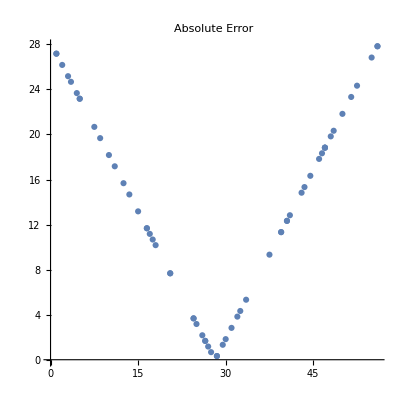

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

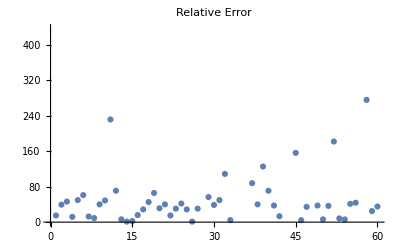

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

204.762

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_1^k θ_2^l θ_3^m θ_4^n

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, m, 4, n, 70, 80], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q70u80mfpos1, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,31,34,35,53,56,58,59,60,62,67,68,69,70}

```mathematica
data = datadefn[rawdata, 53];
```

```mathematica
datasize = Length[data]
```

19598

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4, Ramp 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

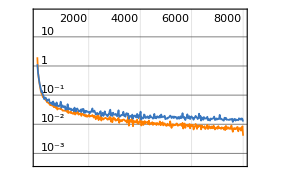
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1088000  rounds:8000  time:30min  examples/s:39097
data | ,,  training examples:8700  validation examples:1740  processed examples:69632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.14×10^-3
validation | ,,  loss:1.88×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

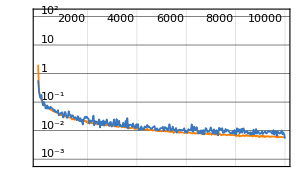
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2300000  rounds:10000  time:2.6h  examples/s:15984
data | ,,  training examples:14698  validation examples:2940  processed examples:147200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.88×10^-3
validation | ,,  loss:3.31×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 53 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

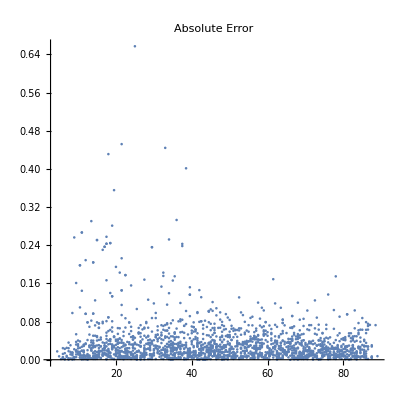

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

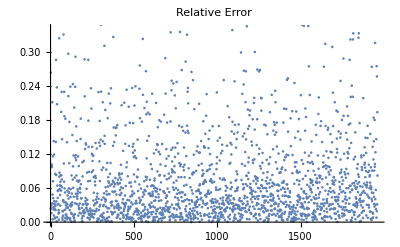

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.110949

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

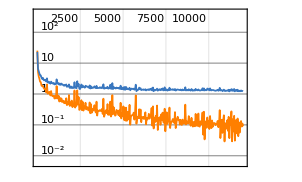
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:2.1h  examples/s:3498
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:1.44
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

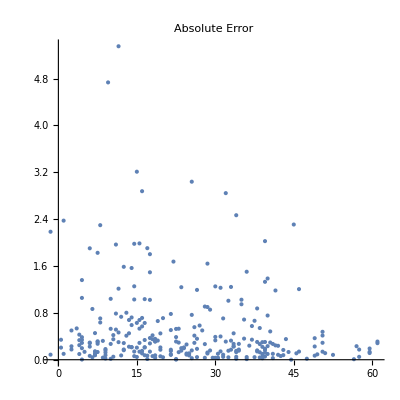

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

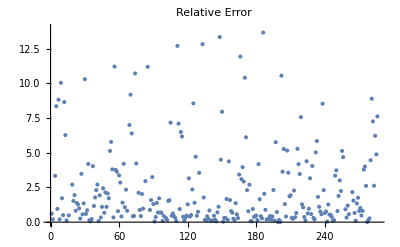

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.1182

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

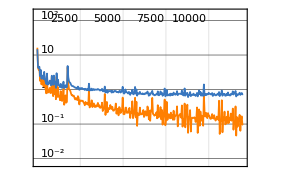
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:13min  examples/s:32683
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.66×10^-2
validation | ,,  loss:6.2×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

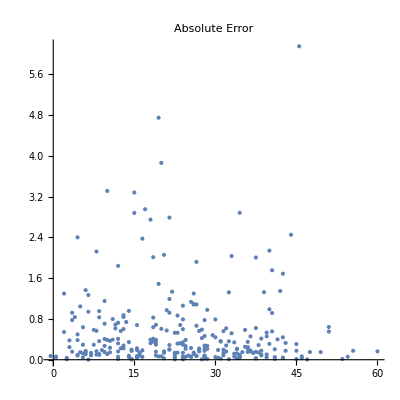

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

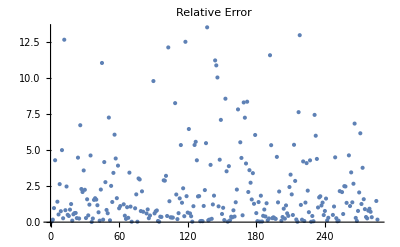

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.88915

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q20u30mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,20,30], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q20u30mfneg.mx", tallk2l2m2n2q20u30mfneg];
tallk2l2m2n2q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg.mx", tallk2l2m2n2q40u50mfneg];*)
tallk2l2m2n2q50u60mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,50,60], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q50u60mfneg.mx", tallk2l2m2n2q50u60mfneg];
(*tallk3l3m3n3q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-3, -1},{l,0,-3, -1}, {m,0,-3, -1}, {n,0,-3, -1}];
DumpSave["tallk3l3m3n3q40u50mfneg.mx", tallk3l3m3n3q40u50mfneg];*)
```

#### tallk2l2m2n2q40u50mfneg, Net0, 40 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

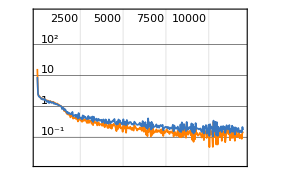
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:6.3min  examples/s:34565
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.78×10^-2
validation | ,,  loss:8.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

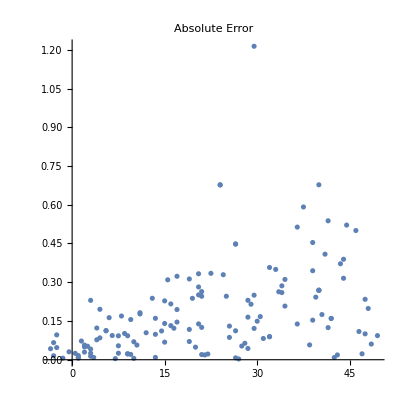

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

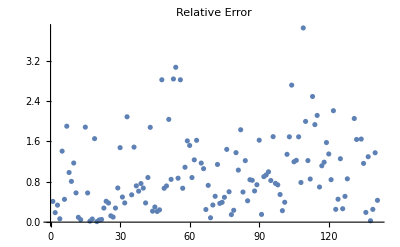

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.14707

#### tallk2l2m2n2q40u50mfneg, Net3, 40 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

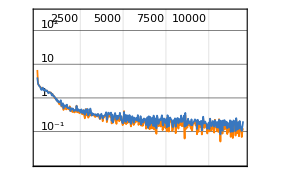
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:7.0min  examples/s:30924
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:1.16×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

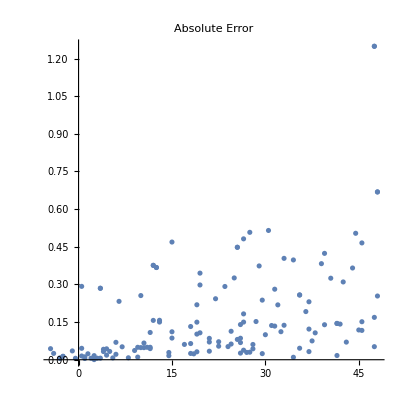

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

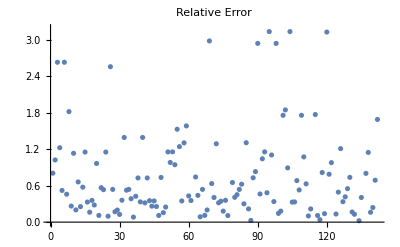

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.36787

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
(*plist=klmnneg[5, 400];*)
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn-neg, Net0, 36 coeffs(r)

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[3525]] // N
```

{4.27264×10^-7,4.20954×10^-6,0.0000224917,0.0000908428,0.000315714,0.000991569,0.00287415,0.00780589,0.0201089,0.0495152,0.148638,-8.12796,1166.62,-95597.4,5.11654×10^6,-1.92659×10^8,5.4057×10^9,-1.18237×10^11,2.08989×10^12,-3.07319×10^13,3.85001×10^14,-4.19022×10^15,4.0269×10^16,-3.46398×10^17,2.698×10^18,-1.92137×10^19,1.2616×10^20,-7.6932×10^20,4.38424×10^21,-2.34781×10^22,1.18715×10^23,-5.69206×10^23,2.59778×10^24,-1.13232×10^25,4.72812×10^25,-1.89646×10^26}→40.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

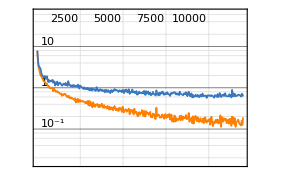
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:45min  examples/s:23936
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:7.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

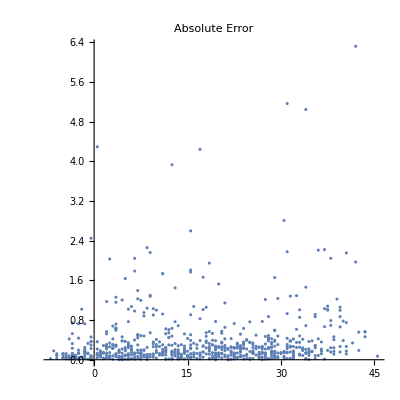

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

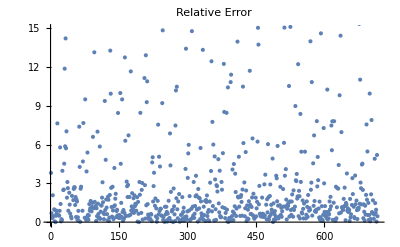

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

6.31506

#### jacobi-klmn-neg, Net3, 36 coeffs

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

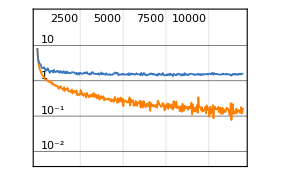
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:1.3h  examples/s:13916
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.02×10^-2
validation | ,,  loss:1.41
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

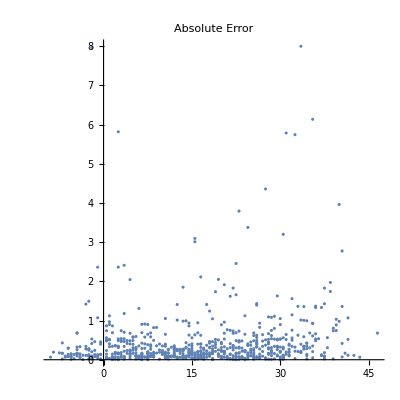

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

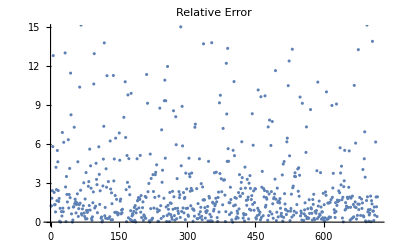

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.08278

## θ_1^k θ_2^l θ_3^m θ_4^n/Δ

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q50u60mfpos0 = ParallelTable[Quiet @ allprodθbyΔ[1,k, 2, l, 3, m, 4, n, 50, 60, 0], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
DumpSave["tallk5l5m5n5q50u60mfpos0.mx", tallk5l5m5n5q50u60mfpos0];
```

#### tallk5l5m5n5q50u60mfpos0, Net0, 25 coeffs(r)

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

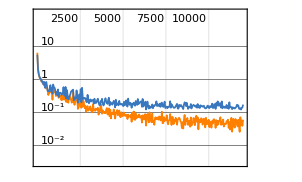
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2568000  rounds:12000  time:2.1h  examples/s:21238
data | ,,  training examples:13679  validation examples:2736  processed examples:164352000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.54×10^-1
validation | ,,  loss:6.4×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

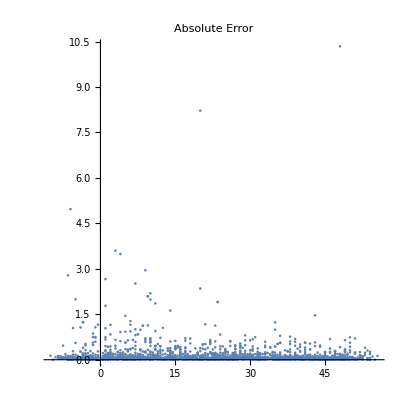

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

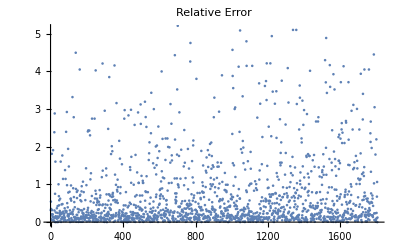

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.78562

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

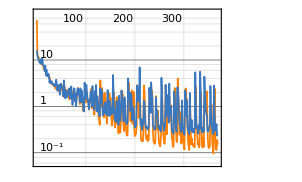
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:79027  rounds:369  time:5.7min  examples/s:14848
data | ,,  training examples:13679  validation examples:2736  processed examples:5057728  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.52×10^-1
validation | ,,  loss:2.47×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{16.0926,11.9417,12.7808,10.7139,10.5111,8.93514,8.706,9.56276,7.48489,10.4442,8.14548,10.7495,6.95333,9.13793,7.72118,6.81918,5.72008,7.03171,8.11831,4.67765,6.18557,4.44467,4.67148,6.18168,3.94506,4.71163,3.21388,3.66859,3.99813,2.9964,3.1201,3.40314,3.15504,2.72024,3.18338,2.82781,2.99386,2.70992,2.98149,4.71385,2.77414,3.00927,2.18779,2.76448,2.61506,2.12827,2.93845,1.77033,2.83599,1.67607,4.50406,2.71944,2.47134,2.14134,1.63109,2.69921,4.55554,1.91445,1.48809,2.25025,1.58571,2.15713,1.57429,1.99194,1.8526,2.90508,1.99093,1.80389,1.4765,1.53903,2.69787,2.04037,1.2148,1.0722,1.77905,1.54136,2.30208,2.61964,1.28543,1.8712,1.00941,2.37994,0.902768,2.35197,2.4627,1.80541,2.02093,1.08538,1.37369,2.43975,1.22857,2.20887,1.98397,1.36891,1.34718,0.839483,0.77669,0.808365,5.701,1.41746,2.40846,2.89852,1.8324,0.687148,1.84173,1.3877,0.869494,1.28626,0.778902,2.09805,2.08162,1.32737,0.982693,1.40927,4.05842,1.23398,1.4557,0.834442,2.15352,1.87722,0.838156,2.88944,0.775091,1.63078,1.89756,0.657817,0.774783,0.667926,0.612098,2.47978,1.49285,0.940459,2.25303,1.17497,0.639982,0.52118,0.994008,1.01972,0.714663,1.23232,1.56942,0.547212,0.649391,0.64335,2.2404,1.24647,0.918884,1.71444,0.620284,1.29436,0.667836,1.24048,0.633874,0.683968,0.720698,4.75539,2.48478,1.129,0.661845,0.501406,0.83661,0.469502,1.37691,1.23815,0.618178,0.513137,0.396855,2.41645,0.968578,0.506419,0.486792,0.72617,1.40826,2.96528,1.37715,1.36421,0.480305,0.480042,0.419483,2.73064,0.739148,0.484611,0.433849,0.41813,0.403046,0.475134,4.00832,1.54767,3.04069,0.988029,1.11156,0.776653,1.92374,1.25709,0.472821,0.538992,0.962304,0.917579,0.491703,0.356179,0.343321,0.435686,0.384582,1.34313,2.7927,2.82787,1.61048,1.30312,1.37397,6.94818,0.628673,0.422697,0.381513,0.531699,0.310958,0.382031,0.44538,0.412753,1.31918,1.16619,0.540989,0.514693,0.343317,0.360958,0.367236,0.314876,0.324899,0.340877,0.349714,2.50361,1.42139,1.03089,0.417355,3.29193,1.95176,1.41899,0.42506,0.322963,0.365225,0.315203,0.31448,0.34471,2.17267,0.966683,0.667695,0.802847,0.555018,0.407986,0.279674,0.384187,0.310248,0.391725,0.289416,0.549491,7.70718,1.65149,0.424256,0.421447,0.302143,0.30202,0.320151,0.386696,2.91529,0.750104,0.434534,0.769269,0.925066,1.77453,0.445621,4.79508,1.38226,0.901007,0.664683,0.988947,0.348633,0.316028,0.296406,0.274686,0.257373,0.380953,3.8014,1.6019,0.502469,0.351612,0.285675,0.327076,4.72541,2.57843,1.5997,0.674357,0.385859,0.446572,0.379513,0.289148,0.278758,2.00972,0.691886,0.327127,0.337194,0.272207,0.243914,0.405941,3.9943,1.96126,0.622385,1.33053,0.437016,0.304258,0.301545,0.288492,0.251765,3.04475,0.843812,0.400923,0.303276,0.514034,0.275643,0.232961,0.350032,0.322863,0.270921,0.373931,2.45135,8.35501,0.945073,0.336518,0.371196,0.421567,0.281015,0.259408,0.399217,0.319492,5.6113,2.19203,1.92803,0.368692,0.272372,0.279473,0.433919,0.259159,0.28881,4.38355,1.79571,0.743435,1.41533,0.694694,0.671538,0.302792,0.283755,0.301587,0.30221,0.360578,0.377448,2.75124,1.27086,0.496083,0.437406,0.311006,0.252385,0.231329,0.293349,2.80962,0.575492,0.299476,0.309908,0.240181,0.58681,0.234391,0.247358}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

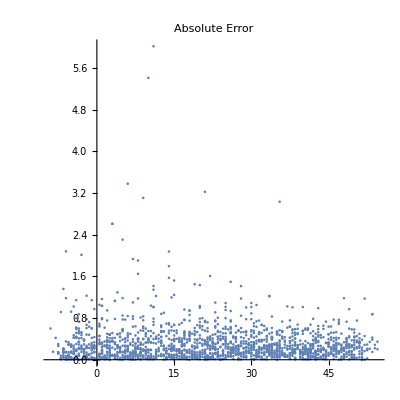

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

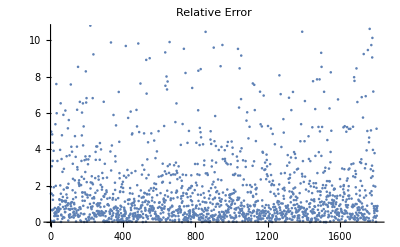

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.53036

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net0, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

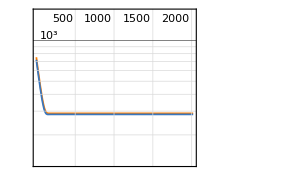
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:345279  rounds:2019  time:10min  examples/s:35890
data | ,,  training examples:10942  validation examples:2189  processed examples:22097856  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^2
validation | ,,  loss:2.84×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{752.842,745.539,738.317,731.197,724.129,717.129,710.237,703.386,696.626,689.912,683.287,676.724,670.235,663.81,657.419,651.125,644.894,638.715,632.595,626.557,620.538,614.612,608.734,602.91,597.156,591.444,585.808,580.215,574.688,569.208,563.785,558.419,553.111,547.857,542.671,537.525,532.426,527.4,522.425,517.507,512.635,507.825,503.08,498.376,493.733,489.136,484.592,480.101,475.681,471.291,466.97,462.72,458.502,454.347,450.24,446.196,442.186,438.24,434.37,430.533,426.754,423.012,419.35,415.725,412.151,408.638,405.179,401.759,398.416,395.121,391.871,388.674,385.52,382.446,379.405,376.416,373.479,370.601,367.759,364.991,362.257,359.581,356.962,354.4,351.863,349.399,346.999,344.626,342.307,340.04,337.815,335.656,333.543,331.48,329.46,327.504,325.578,323.716,321.908,320.132,318.414,316.73,315.11,313.549,312.009,310.527,309.077,307.697,306.359,305.056,303.821,302.607,301.433,300.327,299.252,298.216,297.219,296.279,295.387,294.519,293.698,292.915,292.176,291.469,290.803,290.183,289.586,289.031,288.517,288.025,287.564,287.141,286.753,286.394,286.063,285.758,285.475,285.214,284.995,284.787,284.598,284.43,284.285,284.157,284.04,283.942,283.857,283.788,283.727,283.677,283.636,283.604,283.579,283.56,283.547,283.538,283.534,283.532,283.534,283.539,283.543,283.551,283.56,283.57,283.58,283.591,283.602,283.611,283.621,283.63,283.643,283.651,283.661,283.672,283.68,283.693,283.698,283.705,283.715,283.721,283.724,283.732,283.739,283.747,283.75,283.751,283.762,283.764,283.768,283.771,283.778,283.777,283.781,283.782,283.783,283.786,283.79,283.792,283.791,283.795,283.795,283.796,283.798,283.799,283.802,283.803,283.805,283.804,283.803,283.81,283.807,283.808,283.81,283.809,283.812,283.81,283.811,283.811,283.814,283.812,283.811,283.814,283.815,283.811,283.815,283.813,283.817,283.817,283.817,283.816,283.815,283.822,283.815,283.817,283.817,283.818,283.815,283.818,283.816,283.819,283.816,283.816,283.82,283.817,283.818,283.819,283.818,283.819,283.816,283.815,283.818,283.814,283.817,283.818,283.816,283.813,283.818,283.818,283.815,283.818,283.821,283.82,283.813,283.819,283.819,283.82,283.818,283.818,283.819,283.818,283.818,283.816,283.814,283.822,283.817,283.822,283.818,283.819,283.816,283.818,283.82,283.817,283.82,283.82,283.82,283.822,283.821,283.816,283.816,283.819,283.817,283.815,283.818,283.815,283.82,283.819,283.819,283.818,283.823,283.82,283.818,283.814,283.815,283.818,283.816,283.82,283.821,283.818,283.819,283.815,283.819,283.82,283.819,283.821,283.82,283.817,283.817,283.818,283.815,283.819,283.824,283.817,283.819,283.818,283.816,283.821,283.82,283.817,283.819,283.819,283.818,283.82,283.819,283.816,283.816,283.816,283.819,283.817,283.82,283.818,283.818,283.817,283.821,283.819,283.823,283.821,283.819,283.817,283.822,283.82,283.817,283.82,283.82,283.82,283.816,283.819,283.821,283.818,283.818,283.817,283.817,283.814,283.818,283.816,283.817,283.818,283.82,283.815,283.822,283.823,283.817,283.819,283.819,283.816,283.82,283.818,283.819,283.814,283.816,283.819,283.817,283.819,283.816,283.817,283.816,283.82,283.816,283.817,283.818,283.818,283.819,283.819,283.82,283.819,283.816,283.816,283.815,283.818,283.82,283.817,283.818,283.815,283.815,283.814,283.816,283.817,283.817,283.817,283.816,283.815,283.82,283.817,283.819,283.817,283.82,283.818,283.823,283.817,283.814,283.819,283.817,283.818,283.818,283.82,283.817,283.815,283.815,283.822,283.817,283.82,283.818,283.82,283.815,283.821,283.82,283.817,283.817,283.818,283.818,283.819,283.817,283.82,283.817,283.817,283.818,283.821,283.817,283.817,283.818,283.818,283.818,283.817,283.813,283.816,283.82,283.821,283.82,283.819,283.825,283.817,283.82,283.821,283.818,283.819,283.818,283.818,283.819,283.818,283.818,283.818,283.821,283.818,283.818,283.819,283.816,283.817,283.818,283.818,283.817,283.818,283.821,283.821,283.813,283.817,283.82,283.815,283.818,283.819,283.818,283.816,283.819,283.819,283.818,283.819,283.816,283.818,283.817,283.818,283.817,283.819,283.816,283.817,283.817,283.818,283.818,283.817,283.821,283.818,283.817,283.82,283.819,283.819,283.821,283.819,283.817,283.814,283.816,283.816,283.818,283.818,283.818,283.818,283.819,283.814,283.819,283.814,283.817,283.815,283.817,283.819,283.815,283.814,283.819,283.812,283.821,283.819,283.818,283.817,283.818,283.82,283.821,283.819,283.816,283.819,283.817,283.814,283.816,283.818,283.822,283.821,283.815,283.818,283.818,283.816,283.82,283.82,283.82,283.818,283.82,283.82,283.818,283.821,283.816,283.822,283.817,283.818,283.821,283.819,283.819,283.819,283.818,283.818,283.816,283.823,283.819,283.817,283.815,283.816,283.82,283.818,283.82,283.817,283.816,283.817,283.815,283.819,283.82,283.818,283.817,283.821,283.819,283.821,283.819,283.818,283.818,283.817,283.817,283.815,283.82,283.816,283.818,283.82,283.818,283.82,283.82,283.816,283.817,283.821,283.82,283.817,283.82,283.818,283.819,283.82,283.819,283.819,283.817,283.813,283.817,283.82,283.818,283.818,283.822,283.818,283.819,283.82,283.819,283.819,283.817,283.817,283.818,283.819,283.818,283.818,283.819,283.818,283.82,283.822,283.816,283.82,283.82,283.818,283.819,283.817,283.819,283.817,283.818,283.817,283.819,283.819,283.82,283.82,283.817,283.814,283.821,283.822,283.821,283.82,283.819,283.819,283.818,283.82,283.819,283.818,283.817,283.815,283.82,283.818,283.819,283.817,283.822,283.817,283.817,283.82,283.818,283.821,283.82,283.819,283.818,283.819,283.815,283.819,283.818,283.816,283.819,283.82,283.817,283.817,283.817,283.815,283.819,283.82,283.818,283.82,283.819,283.819,283.818,283.819,283.815,283.816,283.819,283.816,283.819,283.815,283.818,283.817,283.813,283.816,283.816,283.815,283.816,283.815,283.82,283.819,283.818,283.824,283.817,283.819,283.823,283.818,283.818,283.817,283.82,283.821,283.821,283.815,283.82,283.822,283.818,283.821,283.821,283.82,283.817,283.816,283.818,283.823,283.818,283.817,283.819,283.817,283.818,283.817,283.818,283.82,283.819,283.82,283.823,283.817,283.816,283.818,283.82,283.822,283.82,283.818,283.82,283.82,283.819,283.82,283.819,283.818,283.817,283.817,283.82,283.816,283.82,283.813,283.82,283.82,283.818,283.813,283.821,283.817,283.818,283.821,283.818,283.816,283.818,283.815,283.819,283.818,283.817,283.821,283.817,283.814,283.82,283.821,283.818,283.82,283.817,283.814,283.821,283.817,283.818,283.816,283.816,283.816,283.82,283.817,283.818,283.823,283.816,283.818,283.817,283.816,283.815,283.817,283.817,283.82,283.818,283.815,283.82,283.816,283.82,283.82,283.82,283.815,283.814,283.818,283.819,283.815,283.813,283.817,283.819,283.819,283.818,283.82,283.818,283.816,283.815,283.817,283.818,283.816,283.819,283.818,283.817,283.814,283.816,283.815,283.817,283.819,283.818,283.818,283.814,283.817,283.818,283.816,283.816,283.815,283.82,283.821,283.818,283.818,283.816,283.817,283.821,283.819,283.817,283.821,283.817,283.82,283.822,283.819,283.816,283.817,283.818,283.82,283.821,283.817,283.818,283.818,283.817,283.815,283.817,283.818,283.818,283.817,283.82,283.819,283.821,283.817,283.819,283.821,283.82,283.818,283.82,283.818,283.816,283.817,283.818,283.818,283.82,283.818,283.823,283.814,283.819,283.819,283.817,283.818,283.817,283.816,283.818,283.817,283.817,283.818,283.819,283.816,283.816,283.816,283.817,283.814,283.816,283.819,283.816,283.819,283.813,283.816,283.817,283.82,283.822,283.82,283.815,283.818,283.819,283.816,283.817,283.82,283.817,283.821,283.821,283.82,283.821,283.823,283.819,283.818,283.819,283.82,283.82,283.818,283.82,283.816,283.817,283.817,283.816,283.821,283.818,283.818,283.818,283.82,283.816,283.819,283.816,283.818,283.82,283.818,283.816,283.819,283.819,283.819,283.82,283.819,283.821,283.818,283.821,283.816,283.821,283.818,283.817,283.815,283.817,283.816,283.817,283.816,283.815,283.822,283.817,283.82,283.818,283.819,283.818,283.818,283.817,283.819,283.818,283.821,283.817,283.818,283.819,283.822,283.818,283.818,283.818,283.82,283.815,283.819,283.821,283.819,283.817,283.819,283.815,283.814,283.82,283.816,283.819,283.819,283.815,283.821,283.817,283.82,283.816,283.818,283.815,283.818,283.821,283.817,283.817,283.818,283.817,283.817,283.815,283.817,283.816,283.817,283.818,283.815,283.816,283.817,283.818,283.816,283.816,283.818,283.817,283.817,283.816,283.817,283.818,283.82,283.816,283.817,283.821,283.819,283.821,283.818,283.818,283.818,283.819,283.818,283.816,283.817,283.819,283.818,283.814,283.815,283.82,283.819,283.82,283.817,283.818,283.813,283.817,283.817,283.813,283.816,283.816,283.818,283.824,283.817,283.815,283.815,283.816,283.822,283.817,283.819,283.818,283.819,283.815,283.816,283.82,283.82,283.816,283.819,283.82,283.819,283.814,283.82,283.817,283.817,283.818,283.817,283.82,283.818,283.816,283.819,283.818,283.821,283.816,283.82,283.823,283.816,283.815,283.816,283.818,283.818,283.821,283.821,283.82,283.82,283.818,283.818,283.819,283.818,283.82,283.819,283.816,283.818,283.818,283.816,283.819,283.817,283.821,283.818,283.815,283.819,283.819,283.815,283.817,283.814,283.816,283.818,283.817,283.818,283.815,283.82,283.816,283.82,283.819,283.816,283.819,283.82,283.814,283.822,283.818,283.818,283.821,283.817,283.819,283.818,283.82,283.818,283.818,283.819,283.818,283.818,283.818,283.819,283.818,283.82,283.816,283.818,283.821,283.818,283.817,283.815,283.814,283.819,283.815,283.814,283.82,283.815,283.818,283.815,283.818,283.818,283.82,283.817,283.818,283.821,283.82,283.816,283.817,283.818,283.819,283.816,283.818,283.819,283.818,283.821,283.817,283.818,283.817,283.819,283.817,283.817,283.817,283.819,283.817,283.817,283.821,283.814,283.816,283.817,283.819,283.82,283.819,283.817,283.817,283.821,283.816,283.818,283.817,283.82,283.819,283.821,283.817,283.823,283.822,283.818,283.821,283.819,283.821,283.818,283.819,283.819,283.818,283.816,283.816,283.82,283.819,283.817,283.82,283.821,283.817,283.817,283.819,283.818,283.816,283.816,283.819,283.816,283.817,283.82,283.817,283.816,283.816,283.818,283.816,283.821,283.818,283.815,283.818,283.816,283.816,283.817,283.815,283.818,283.817,283.82,283.819,283.82,283.816,283.819,283.821,283.816,283.819,283.818,283.815,283.817,283.818,283.815,283.818,283.816,283.818,283.815,283.816,283.814,283.816,283.816,283.816,283.816,283.816,283.816,283.817,283.817,283.821,283.818,283.818,283.821,283.823,283.817,283.818,283.819,283.819,283.816,283.819,283.819,283.817,283.811,283.82,283.816,283.819,283.818,283.82,283.819,283.82,283.819,283.82,283.819,283.82,283.818,283.82,283.818,283.818,283.819,283.816,283.816,283.818,283.819,283.816,283.813,283.819,283.815,283.816,283.819,283.815,283.819,283.818,283.819,283.815,283.821,283.816,283.822,283.814,283.821,283.816,283.822,283.817,283.819,283.822,283.817,283.816,283.82,283.821,283.82,283.819,283.822,283.818,283.819,283.819,283.817,283.818,283.816,283.82,283.821,283.818,283.821,283.819,283.819,283.818,283.817,283.822,283.816,283.817,283.816,283.815,283.815,283.817,283.819,283.82,283.819,283.818,283.82,283.816,283.819,283.819,283.819,283.815,283.818,283.817,283.818,283.821,283.817,283.817,283.82,283.819,283.821,283.818,283.82,283.819,283.819,283.815,283.816,283.816,283.817,283.817,283.815,283.822,283.82,283.818,283.816,283.821,283.816,283.818,283.817,283.816,283.816,283.819,283.815,283.817,283.818,283.817,283.821,283.813,283.821,283.818,283.819,283.82,283.819,283.817,283.819,283.821,283.821,283.824,283.821,283.816,283.819,283.82,283.815,283.819,283.816,283.815,283.817,283.817,283.817,283.818,283.821,283.82,283.819,283.818,283.819,283.819,283.818,283.817,283.815,283.819,283.816,283.82,283.814,283.819,283.818,283.817,283.819,283.819,283.823,283.82,283.818,283.816,283.818,283.82,283.816,283.816,283.82,283.814,283.819,283.82,283.816,283.817,283.818,283.819,283.819,283.815,283.815,283.818,283.817,283.817,283.817,283.819,283.818,283.816,283.816,283.821,283.819,283.818,283.816,283.818,283.818,283.819,283.82,283.816,283.814,283.82,283.815,283.818,283.819,283.817,283.817,283.818,283.819,283.816,283.818,283.816,283.817,283.817,283.816,283.815,283.819,283.814,283.821,283.816,283.818,283.819,283.816,283.817,283.817,283.819,283.818,283.818,283.816,283.818,283.815,283.818,283.82,283.817,283.819,283.819,283.82,283.816,283.818,283.817,283.816,283.821,283.816,283.818,283.821,283.817,283.813,283.815,283.817,283.817,283.821,283.818,283.817,283.815,283.817,283.818,283.818,283.816,283.815,283.816,283.817,283.816,283.819,283.816,283.819,283.819,283.816,283.814,283.819,283.818,283.818,283.813,283.816,283.813,283.82,283.818,283.823,283.817,283.818,283.817,283.817,283.819,283.818,283.822,283.814,283.817,283.819,283.817,283.818,283.818,283.817,283.815,283.817,283.82,283.818,283.817,283.821,283.82,283.819,283.817,283.817,283.818,283.814,283.819,283.819,283.819,283.816,283.819,283.818,283.82,283.82,283.818,283.819,283.818,283.818,283.815,283.817,283.818,283.815,283.82,283.817,283.818,283.819,283.816,283.82,283.819,283.817,283.817,283.817,283.817,283.819,283.814,283.821,283.818,283.821,283.819,283.819,283.819,283.822,283.819,283.819,283.819,283.821,283.818,283.819,283.816,283.817,283.821,283.82,283.821,283.817,283.818,283.818,283.819,283.822,283.82,283.817,283.818,283.819,283.822,283.816,283.818,283.819,283.819,283.821,283.814,283.815,283.816,283.823,283.818,283.82,283.819,283.818,283.817,283.82,283.819,283.818,283.819,283.82,283.818,283.815,283.819,283.819,283.818,283.819,283.817,283.816,283.812,283.816,283.818,283.819,283.817,283.814,283.818,283.815,283.816,283.816,283.817,283.817,283.815,283.82,283.818,283.818,283.814,283.82,283.816,283.817,283.819,283.817,283.819,283.818,283.818,283.819,283.816,283.817,283.822,283.819,283.817,283.821,283.823,283.819,283.817,283.82,283.819,283.815,283.819,283.818,283.817,283.817,283.816,283.814,283.819,283.821,283.815,283.818,283.818,283.819,283.818,283.817,283.816,283.819,283.814,283.816,283.817,283.819,283.819,283.817,283.816,283.818,283.819,283.818,283.818,283.815,283.819,283.819,283.818,283.818,283.82,283.818,283.816,283.817,283.816,283.815,283.817,283.817,283.82,283.819,283.818,283.818,283.818,283.819,283.817,283.816,283.82,283.817,283.82,283.817,283.815,283.819,283.816,283.814,283.815,283.818,283.823,283.817,283.817,283.817,283.817,283.819,283.823,283.816,283.816,283.818,283.819,283.819,283.817,283.82,283.817,283.82,283.823,283.816,283.819,283.821,283.817,283.818,283.819,283.815,283.819,283.82,283.819,283.819,283.815,283.818,283.819,283.816,283.82,283.818,283.818,283.818,283.82,283.819,283.818,283.818,283.817,283.821,283.818,283.82,283.818,283.816,283.819,283.816,283.815,283.821,283.817,283.817,283.817,283.817,283.816,283.818,283.818,283.818,283.814,283.819,283.815,283.818,283.816,283.819,283.82,283.821,283.821,283.819,283.818,283.817,283.816,283.821,283.82,283.819,283.819,283.816,283.817,283.819,283.816,283.813,283.818,283.822,283.816,283.817,283.819,283.817,283.814,283.819,283.817,283.818,283.821,283.822,283.816,283.818,283.82,283.815,283.817,283.819,283.817,283.818,283.821,283.817,283.82,283.816,283.822,283.817,283.819,283.821,283.819,283.817,283.818,283.817,283.818,283.821,283.819,283.819,283.819,283.817,283.818,283.817,283.817,283.818,283.817,283.816,283.814,283.816,283.816,283.818,283.819,283.822,283.814,283.822,283.819,283.817,283.82,283.815,283.817,283.817,283.819,283.819,283.82,283.816,283.818,283.818,283.822,283.816,283.818,283.82,283.815,283.818,283.817,283.817,283.821,283.817,283.819,283.816,283.818,283.819,283.818,283.818,283.818,283.816,283.816,283.818,283.822,283.821,283.82,283.816,283.822,283.821,283.819,283.821,283.819,283.819,283.822,283.818,283.817,283.821,283.823,283.82,283.82,283.819,283.821,283.817,283.819,283.821,283.815,283.818,283.815,283.818,283.819,283.819,283.816,283.819,283.819,283.819,283.817,283.817,283.822,283.82,283.819,283.819,283.819,283.821,283.818,283.815,283.819,283.818,283.822,283.82,283.815,283.819,283.82,283.819,283.819,283.818,283.817,283.821,283.815,283.818,283.815,283.818,283.818,283.818,283.819,283.817,283.818,283.817,283.815,283.819,283.815,283.816,283.817,283.819,283.82,283.817,283.82,283.817,283.822,283.822,283.817,283.816,283.817,283.815,283.82,283.821,283.816,283.818,283.814}}

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

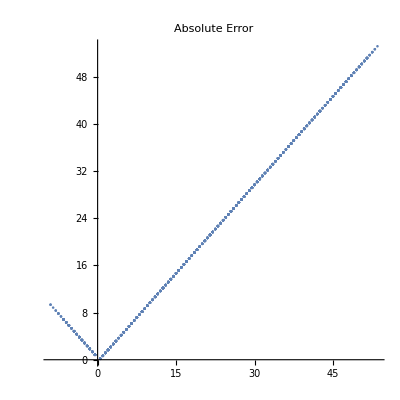

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

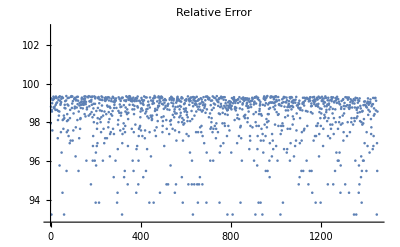

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

99.128

#### tallk5l5m5n5q50u60mfpos0, Net3, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

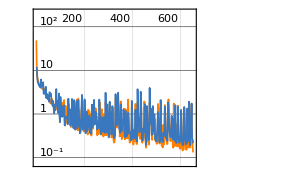
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:111663  rounds:653  time:3.6min  examples/s:32641
data | ,,  training examples:10942  validation examples:2189  processed examples:7146432  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:2.3×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{9.86665,17.6274,7.98797,7.64692,15.1241,6.66,5.55402,5.65965,4.58994,5.1546,4.79833,4.49643,4.58261,4.35167,4.99212,4.03064,4.23113,4.07299,3.58034,4.4772,7.64302,4.74232,5.66432,3.77124,3.54193,3.81572,4.66701,3.56109,5.65529,3.46204,7.23359,2.83879,2.97104,3.54381,3.39382,2.54058,3.38097,3.65048,2.92313,2.72466,4.37552,4.01972,2.35828,2.26245,2.62915,3.13588,2.58526,2.33649,2.36792,2.11522,2.05666,2.4987,2.83289,1.73918,2.12656,1.86816,4.44331,3.58264,2.5553,3.44695,1.07592,3.20887,3.27083,2.5329,1.76261,1.78285,2.36149,1.69218,1.06558,2.03695,2.30334,1.50266,1.06841,1.83985,1.06041,0.957281,1.11197,1.61621,1.59575,1.23225,1.21416,1.22047,2.19013,3.40587,4.05022,1.9004,1.77637,1.03929,0.932917,3.09428,1.31108,1.12414,1.25889,0.828579,1.84049,4.05008,0.953847,0.624081,1.20993,0.634751,0.664097,2.92975,1.98122,1.58281,1.03865,0.610321,2.48027,0.945476,0.762107,1.25183,0.721178,2.25231,0.959955,1.24942,0.810525,0.972323,2.07928,1.09836,0.580531,0.522291,0.482843,0.975711,0.957452,0.886012,0.649268,0.91806,0.804046,0.947768,0.66217,1.06583,0.684232,0.541513,0.628133,0.52818,0.604752,5.56394,1.30257,0.730521,0.4596,1.89555,0.715803,1.83525,0.555662,0.524011,0.443051,2.08005,1.29647,0.520006,0.570939,1.19648,3.23388,0.758377,0.402761,0.628189,0.433932,0.442811,0.504046,3.28673,0.896661,3.08983,1.54613,0.579085,0.418971,0.451871,0.387356,0.625473,0.748366,0.609304,2.7174,1.21816,0.599287,0.409319,0.414976,0.639212,0.517734,3.1153,1.05333,0.777452,1.52097,0.667072,0.753634,0.347398,0.376147,0.426168,0.349689,0.477706,0.434565,0.519512,0.809943,1.85235,1.65437,3.82299,0.785214,0.594577,0.505859,0.366206,0.560914,0.415979,0.367269,0.461593,0.652335,3.14352,1.17775,0.52077,0.547026,0.377596,0.349593,0.443593,0.799707,1.26511,1.68476,0.577981,0.509431,0.317127,0.407479,0.492778,0.904955,0.905851,0.507885,1.07253,0.91213,0.578236,1.30908,0.38553,0.347984,0.997074,0.620455,0.424832,0.320727,0.318993,0.37853,2.49194,0.772486,0.472277,0.625373,0.409366,0.769335,0.407976,0.380868,2.33328,2.59669,1.61802,0.626559,0.518543,0.764697,0.645062,0.460318,0.373504,1.87912,0.447109,1.46573,0.920364,0.552253,0.384922,0.493639,0.375759,0.909023,0.450171,0.426406,0.568321,0.350292,0.606788,0.884375,3.39028,1.78152,0.623395,0.62541,0.313358,0.284204,0.401849,0.273087,0.408869,1.39012,1.15485,0.545442,0.644313,0.362814,0.377574,0.399784,0.390905,0.523316,1.57861,0.398767,0.524038,0.371255,0.525959,0.345543,0.389153,3.95096,2.18257,0.60324,0.533221,0.355954,0.401429,0.280003,0.486165,4.20157,0.519573,0.329839,0.353034,1.02185,0.254099,0.328599,0.40757,2.86068,1.05544,2.76547,0.400381,0.351106,0.584773,1.72708,0.451442,0.321036,0.359763,0.245086,0.605388,0.337114,2.69273,1.63892,0.479155,0.399719,0.361455,0.295227,0.277638,0.281162,0.25935,0.403616,0.264369,0.368437,3.64419,2.05909,1.82681,1.09914,2.53082,0.749559,0.934227,0.616511,0.483716,0.831054,2.13524,1.81943,4.3266,1.53704,0.599457,0.754362,0.517176,0.395365,0.518125,0.35661,0.370713,0.36601,2.61145,0.707535,0.459798,0.33986,0.370845,0.562004,0.32827,0.282673,0.872907,0.322271,1.01182,0.419648,2.10558,1.76124,0.38533,0.303501,0.294364,0.287721,0.297971,0.294505,0.278441,2.06079,0.887575,0.618849,0.342163,0.270248,0.305301,0.355924,0.265251,0.269168,1.16435,1.06172,1.06213,0.912694,0.661425,0.280561,0.420657,0.272324,0.4594,0.296806,0.484517,0.335113,0.330316,0.429787,0.27237,0.221378,0.935281,3.05187,0.394536,0.627179,0.292455,0.271294,0.211614,0.323754,0.216102,0.322537,0.75181,0.241739,0.329072,0.234027,0.512879,1.92311,0.577122,0.270805,0.258776,0.258482,0.223133,0.443326,0.234386,0.235063,5.16496,2.23579,0.921572,1.06661,1.16843,0.407127,0.386033,0.373087,0.30772,0.28487,0.569646,0.314208,0.736215,0.268275,6.20453,1.89384,0.475646,0.297718,0.29388,0.285121,0.208036,0.200158,0.343232,0.257727,0.283369,0.646943,0.394963,0.365377,1.36058,1.36176,2.48327,0.91319,0.373268,0.258192,0.272598,0.193467,0.195796,0.309188,0.311674,0.587292,2.45939,0.581438,0.427093,0.365637,0.343239,0.23378,0.337728,0.191013,0.316695,0.204964,6.24671,1.67216,0.893042,0.696989,0.625228,0.575844,2.05314,0.566937,0.3669,0.361379,0.266748,0.294974,0.397166,0.486027,2.56058,0.959223,0.345499,0.484339,0.312464,0.252806,1.5075,1.19439,0.367905,0.36429,0.239162,0.281294,0.306164,0.34928,0.243771,0.223435,0.439907,0.237181,0.293361,0.284145,1.31944,1.8133,0.410242,0.628774,0.2611,0.29788,0.35522,0.234074,0.213931,1.00397,0.32507,2.82792,1.94273,1.50973,0.310164,0.401007,0.224482,0.27078,0.266097,0.221832,0.214499,0.239383,0.349276,0.507527,0.259706,0.23216,0.430847,0.379518,0.252982,0.219776,2.71506,1.02919,0.390119,0.346403,0.241701,0.314006,0.373521,0.212597,0.263952,0.257217,0.251349,0.233223,0.444484,3.24477,2.21252,1.03717,0.74447,0.469492,0.410327,0.427044,0.311425,0.329585,0.32282,0.304563,0.281479,0.400994,0.276642,0.36571,1.44897,0.589397,0.295466,0.310525,0.288457,0.239475,0.191061,0.330068,1.02362,0.537044,0.319135,0.317309,0.225236,0.259922,0.20479,0.196896,4.38401,0.289811,0.222775,0.215167,0.217569,0.340781,0.222199,0.260212,0.281139,0.568692,2.34502,0.612488,0.403703,0.230555,0.264715,0.180654,0.222655,0.219916,0.246204,0.32745,0.251461,0.242429,0.206782,2.6674,0.769343,0.870776,0.228596,0.207675,0.211197,0.202241,0.189634,0.201549,0.185514,0.338665,0.19446,0.206002,2.2716,1.87249,1.04618,0.264777,0.252879,0.305769,0.223028,0.182176,0.282202,0.249142,0.217012,0.209303,2.84162,0.745168,0.410424,0.246171,0.226821,0.299702,0.277365,0.273043,3.55864,1.32714,0.266944,0.211332,0.167739,0.201088,0.217056,0.601228,0.641,0.378775,2.7616,0.703706,0.370725,0.181481,0.316936,0.191294,0.195239,0.230249}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

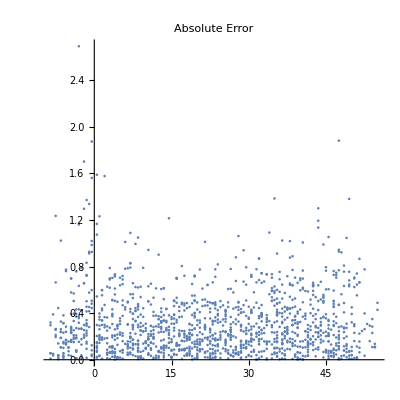

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

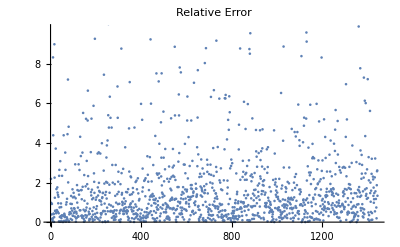

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.49423

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

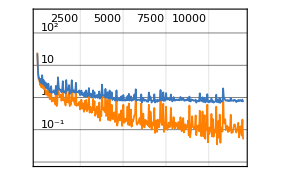
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:18min  examples/s:24379
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.4×10^-2
validation | ,,  loss:7.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

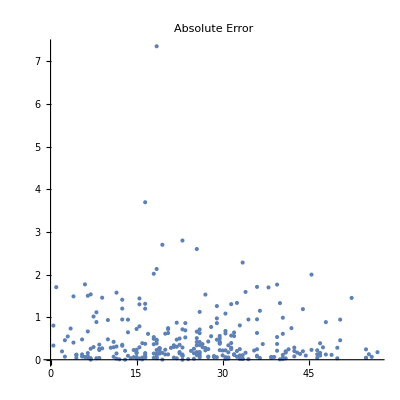

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

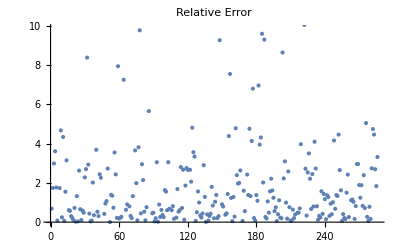

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.27794

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

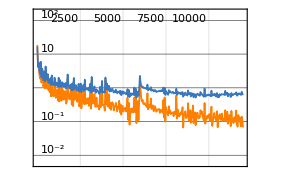
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:32min  examples/s:13805
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-2
validation | ,,  loss:5.57×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

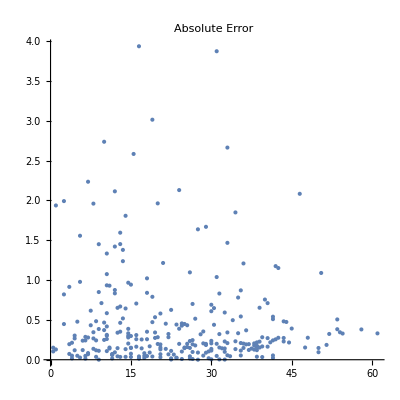

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

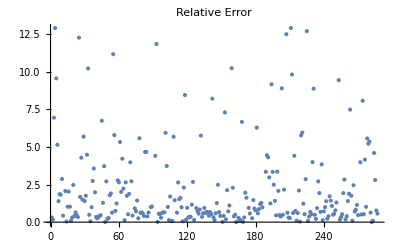

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.21632

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q30u50mfneg = ParallelTable[allprodgenneg[1, k, 2, l, 3,m, 4, n,30,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q30u50mfneg.mx", tallk2l2m2n2q30u50mfneg];
tallk2l2m2n2q20u30mfneg1 = ParallelTable[allprod1neg[1, k, 2, l, 3,m, 4, n,20,30], {k,-1,-3, -1},{l,-1,-3, -1}, {m,-1,-3, -1}, {n,-1,-3, -1}];
DumpSave["tallk2l2m2n2q20u30mfpos1.mx", tallk2l2m2n2q20u30mfpos1];*)
tallk2l2m2n2q40u50mfneg0 = ParallelTable[Quiet @ allprodθbyΔ[1, k, 2, l, 3,m, 4, n,40,50, 0], {k,0,-2, -1},{l,0,-2, -1}, {m,0,-2, -1}, {n,0,-2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg0.mx", tallk2l2m2n2q40u50mfneg0];
```

#### tallk2l2m2n2q40u50mfneg0, Net0, 39 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[331]]//N
```

{4.10134×10^-7,-8.20268×10^-7,3.14436×10^-6,-6.15091×10^-6,0.0000261318,0.00690038,2.55039,333.48,28578.7,1.27718×10^6,4.58949×10^7,1.04352×10^9,2.11083×10^10,3.02515×10^11,4.07557×10^12,4.18362×10^13,4.16687×10^14,3.32462×10^15,2.62228×10^16,1.71833×10^17,1.12555×10^18,6.29679×10^18,3.54451×10^19,1.74141×10^20,8.6409×10^20,3.80803×10^21,1.69832×10^22,6.82412×10^22,2.77733×10^23,1.03064×10^24,3.87445×10^24,1.34154×10^25,4.70427×10^25,1.53257×10^26,5.05364×10^26,1.55976×10^27,4.86918×10^27,1.43195×10^28,4.25593×10^28}→29.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

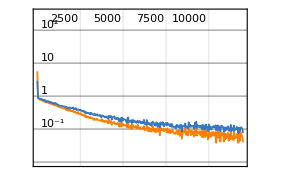
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:21min  examples/s:10224
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.4×10^-2
validation | ,,  loss:9.76×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

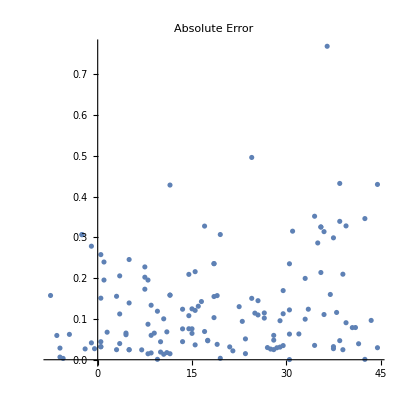

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

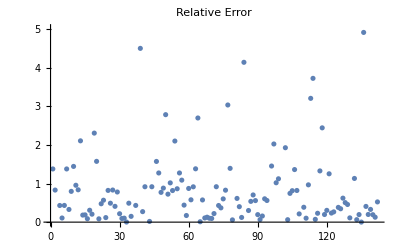

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.26061

#### tallk2l2m2n2q40u50mfneg0, Net3, 39 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

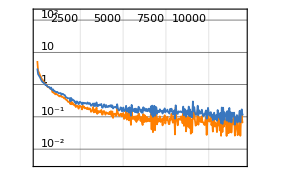
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:15min  examples/s:14259
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.81×10^-2
validation | ,,  loss:8.38×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

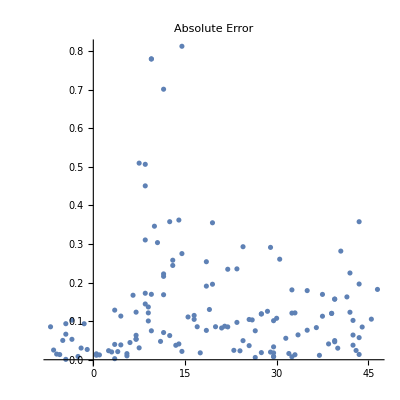

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

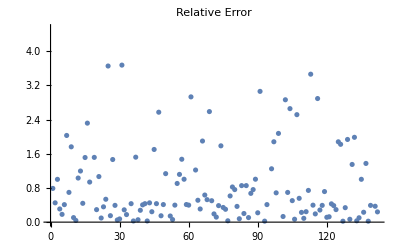

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.1453

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
plist=klmnneg[5, 400];
```

```mathematica
allprodgenbyΔneg[50,70,plist,plist[[61;;65]],0];
```

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
Length[data1]
```

922

```mathematica
Values[data1];
```

#### jacobibyΔ-klmn-neg, Net0, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

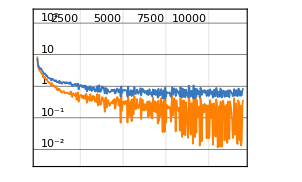
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.3min  examples/s:35752
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:5.28×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

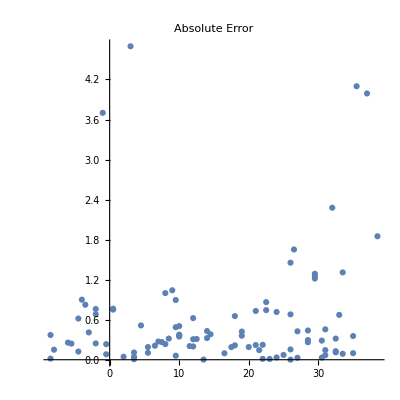

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

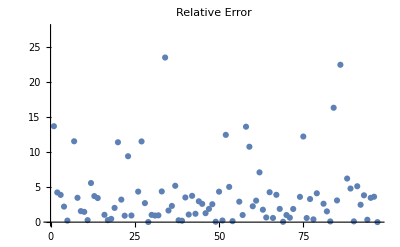

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

13.3438

#### jacobibyΔ-klmn-neg, Net3, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

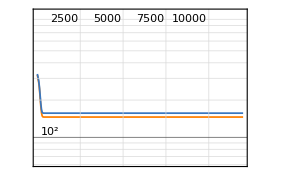
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.6min  examples/s:33129
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.46×10^2
validation | ,,  loss:1.57×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

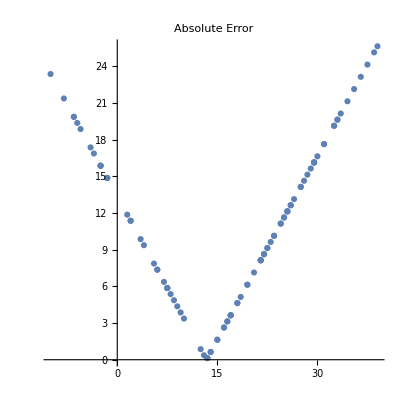

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

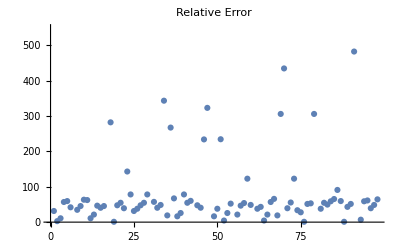

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

138.903

## 2 η^3 = θ_2θ_3θ_4

## Setting k = 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
k1 = ParallelTable[allprod1pos[1, 0, 2, l, 3,m, 4, n,70,80], {l, 3},{m,3}, {n, 3}];
```

```mathematica
<<tallk5l5m5n5q70u80mfpos1.mx; <<t2n50q30u70mfpos1.mx;
```

```mathematica
e1 = Flatten[tallk0l5m5n5q70u80mfpos1, 4];
(*e2 = Flatten[t2n70q60u100mfpos1, 1];
e3 = Flatten[t3n70q60u100mfpos1, 1];
e4 = Flatten[t4n70q60u100mfpos1, 1];*)
```

```mathematica
e1[[;;2]]
```

{{-1,27,-125,343,-729,1331,-2197,3375}→7/2,{1/12,-209/4,-96,5429/12,96,768,-32935/12,864,-1920,-1056,30819/4,288,-2400,6720,4416,-346523/12,9504,-384,-5760,-7200,-5376,548701/12,12000,-20160,-3936,19872,30432,-9408,-471109/4,31008,3168,10272,-25728,1920,-36288}→11/2}

```mathematica
Length /@ Keys[e1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
fdata1 = e1;
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
nk1 = If[Length[#]>= 59, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
(*nk2 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata2];
Length /@  nk2 // Union*)
```

{59,60,61,62,69,70}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
(*newkeys2 =nk2[[All,;;Min[Length /@ nk2]]];
newvalues2 = If[Length[Keys[#]]>= 26, Values[#], ##&[] ] & /@ fdata2;*)
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

3988

{59}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{3988}

3988

```mathematica
Length @ Keys[data[[1]]]
data[[1]]
```

59

{1/12,-41/6,-209/4,441/2,-223/6,192,-2545/12,-8509/6,-96,-2665/6,23317/6,377/2,-30631/12,42431/6,2400,-49277/6,-12449,3648,-6417/2,576,14691/4,2999/3,62965/6,-2304,50499/2,41239/6,8832,-7047/2,-195623/6,-104475/2,-164507/12,40793,14496,-14400,-492091/6,-14208,255173/3,324863/6,-43505/2,724307/6,-21888,-4416,971399/12,-584357/6,10272,-231579/2,-125743/3,54144,-240007/6,100951/6,-19488,-605789/3,7200,-93504,13824,210905,335297/4,475533/2,1522205/6}→6

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

2991

598

399

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 48 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:210251  rounds:4473  time:5.9min  examples/s:38282
data | ,,  training examples:2997  validation examples:599  processed examples:13456064  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 59 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:376000  rounds:8000  time:13min  examples/s:31393
data | ,,  training examples:2991  validation examples:598  processed examples:24064000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.26×10^-3
validation | ,,  loss:1.03×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.161518

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## u = 0

```mathematica
eta1pos[m_,  n_, nq_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[ EllipticTheta[2,0,q]^m EllipticTheta[3,0,q]^n EllipticTheta[4,0,q]^n,{q,0,nq}];
th2  = th1/q^(m/4);
cq = DeleteCases[CoefficientList[th2, q],0];
wt = m/2+2 n/2;
dt = cq -> wt;
Return[dt]]
```

```mathematica
th1  = Series[ EllipticTheta[2,0,q]^5 EllipticTheta[3,0,q]^5 EllipticTheta[4,0,q]^5,{q,0,10}]
```

32 q^(5/4)-480 q^(13/4)+2880 q^(21/4)-7840 q^(29/4)+3360 q^(37/4)+O[q]^(41/4)

```mathematica
eta1pos[5, 5, 10]
```

{{32,-480,2880,-7840,3360}→15/2}

```mathematica
etan500q200 = ParallelTable[eta1pos[n, n, 200],{n, 0, 500, 1/8}];
DumpSave["etan500q200.mx", etan500q200];
```

```mathematica
<<etan300q100.mx
```

```mathematica
etan100q50
```

```mathematica
e1 = Flatten[etan500q200, 3];
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{0,14,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
nk1 = If[Length[#]>= 70, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
newkeys1 =Simplify @ nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

2262

{70}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{2262}

2262

```mathematica
Length/@ Keys[data] // Union
```

{70}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 20000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.1min  examples/s:23336
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.09×10^-2
validation | ,,  loss:4.24×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:2.2min  examples/s:11670
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.49×10^-2
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.7min  examples/s:15094
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.79×10^-1
validation | ,,  loss:4.22×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.6min  examples/s:16311
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.11×10^-1
validation | ,,  loss:1.91×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.4min  examples/s:35160
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.7×10^-2
validation | ,,  loss:1.71×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:3.1min  examples/s:27529
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.71×10^-1
validation | ,,  loss:6.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.9min  examples/s:29141
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.96×10^-2
validation | ,,  loss:3.07×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.5min  examples/s:34530
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.18×10^-2
validation | ,,  loss:4.37×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* etan500q200 70 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:540000  rounds:20000  time:17min  examples/s:33878
data | ,,  training examples:1696  validation examples:339  processed examples:34560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.62×10^-2
validation | ,,  loss:5.35×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

## Individual θ_i without dividing by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
t1k40q50u60mfpos=ParallelTable[Quiet @ theta1[k,50,60],{k,40}];
DumpSave["t1k40q50u60mfpos.mx", t1k40q50u60mfpos];
t1k50q70u80mfpos=ParallelTable[theta1[k,70,80],{k,50}];
DumpSave["t1k50q70u80mfpos.mx", t1k50q70u80mfpos];
(*t1k80q120u150mfpos=ParallelTable[theta1[k,120,150],{k,80}];
DumpSave["t1k80q120u150mfpos.mx", t1k80q120u150mfpos];*)
```

#### t1k40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.8min  examples/s:26666
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.1×10^-1
validation | ,,  loss:1.39×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.366402

#### t1k40q50u60mfpos, Net3, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:6.2min  examples/s:20733
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-1
validation | ,,  loss:8.63×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.318925

#### t1k50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1360

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:7.9min  examples/s:25969
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.6×10^-2
validation | ,,  loss:4.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.257198

#### t1k50q70u80mfpos, Net3, 26 coeffs

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1360

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:12min  examples/s:17659
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.47×10^-2
validation | ,,  loss:5.5×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.342947

### θ_2

```mathematica
t2l40q50u60mfpos=ParallelTable[Quiet @ theta2[l,50,60],{l,40}];
DumpSave["t2l40q50u60mfpos.mx", t2l40q50u60mfpos];
t2l50q70u80mfpos=ParallelTable[theta2[l,70,80],{l,50}];
DumpSave["t2l50q70u80mfpos.mx", t2l50q70u80mfpos];
(*t2l80q120u150mfpos=ParallelTable[theta2[l,120,150],{l,80}];
DumpSave["t2l80q120u150mfpos.mx", t2l80q120u150mfpos];*)
```

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.1min  examples/s:26917
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.23×10^-2
validation | ,,  loss:1.1×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.775116

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.3min  examples/s:26274
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.27×10^-3
validation | ,,  loss:1.22×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.738755

#### t2l50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t2l50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t2l50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

2009

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:20min  examples/s:15231
data | ,,  training examples:1506  validation examples:302  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.78×10^-1
validation | ,,  loss:1.09×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.238111

### θ_3

```mathematica
t3m40q50u60mfpos=ParallelTable[Quiet @ theta3[m,50,60],{m,40}];
DumpSave["t3m40q50u60mfpos.mx", t3m40q50u60mfpos];
t3m50q70u80mfpos=ParallelTable[theta3[m,70,80],{m,50}];
DumpSave["t3m50q70u80mfpos.mx", t3m50q70u80mfpos];
(*t3m80q120u150mfpos=ParallelTable[theta3[m,120,150],{m,80}];
DumpSave["t3m80q120u150mfpos.mx", t3m80q120u150mfpos];*)
```

#### t3m40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.8min  examples/s:26546
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.24×10^2
validation | ,,  loss:3.42×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

68.4218

#### t3m40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:18003
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.53×10^-4
validation | ,,  loss:5.85×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.130769

#### t3m50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26632
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-2
validation | ,,  loss:7.65×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.04524

#### t3m50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:16min  examples/s:17959
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.38×10^-3
validation | ,,  loss:8.18×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0620383

### θ_4

```mathematica
t4n40q50u60mfpos=ParallelTable[Quiet @ theta4[n,50,60],{n,40}];
DumpSave["t4n40q50u60mfpos.mx", t4n40q50u60mfpos];
t4n50q70u80mfpos=ParallelTable[theta4[n,70,80],{n,50}];
DumpSave["t4n50q70u80mfpos.mx", t4n50q70u80mfpos];*)
(*t4n80q120u150mfpos=ParallelTable[theta4[n,120,150],{n,80}];
DumpSave["t4n80q120u150mfpos.mx", t4n80q120u150mfpos];*)
```

#### t4n40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.7min  examples/s:26664
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.33×10^2
validation | ,,  loss:3.52×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

49.7019

#### t4n40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:17967
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.47×10^-4
validation | ,,  loss:7.55×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.103263

#### t4n50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26354
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.71×10^-4
validation | ,,  loss:1.49×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0563935

#### t4n50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
```

```mathematica
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:14min  examples/s:21750
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.5×10^-3
validation | ,,  loss:1.59×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0445423

## Negative powers of θ_i

### θ_1

```mathematica
(*t1k40q50u60mfneg=ParallelTable[Quiet @ theta1[k,50,60],{k,-1, -40, -1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
t1k50q70u80mfneg=ParallelTable[Quiet @ theta1[k,70,80],{k,-1, -50, -1}];
DumpSave["t1k50q70u80mfneg.mx", t1k50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t1k40q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:7.0min  examples/s:36431
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.35×10^-3
validation | ,,  loss:8.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.54308

#### t1k40q50u60mfneg, Net3, 26 coeffs

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:9.6min  examples/s:26698
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:5.85×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.33966

### θ_2

```mathematica
(*t2l40q50u60mfneg=ParallelTable[Quiet @ theta2[l,50,60],{l,-1, -40, -1}];
DumpSave["t2l40q50u60mfneg.mx", t2l40q50u60mfneg];*)
t2l50q70u80mfneg=ParallelTable[Quiet @ theta2[l,70,80],{l,-1, -50, -1}];
DumpSave["t2l50q70u80mfneg.mx", t2l50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t2l40q50u60mfneg, Net0, 26 coeffs

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:5.4min  examples/s:35775
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.19×10^-1
validation | ,,  loss:1.04
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.93778

#### t2l40q50u60mfneg, Net3, 26 coeffs(r)

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:6.9min  examples/s:28011
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.59×10^-1
validation | ,,  loss:8.74×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.4772

### θ_3

```mathematica
t3m40q50u60mfneg=ParallelTable[Quiet @ theta3[m,50,60],{m,-1, -40, -1}];
DumpSave["t3m40q50u60mfneg.mx", t3m40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t3m40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:16978
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:3.91×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.542126

#### t3m40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16118
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.44×10^2
validation | ,,  loss:3.29×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

286.609

### θ_4

```mathematica
t4n40q50u60mfneg=ParallelTable[Quiet @ theta4[n,50,60],{n,-1, -40, -1}];
DumpSave["t4n40q50u60mfneg.mx", t4n40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t4n40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20422
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.47×10^-2
validation | ,,  loss:3.46×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.798023

#### t4n40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:8.7min  examples/s:21950
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.23×10^2
validation | ,,  loss:3.67×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

205.459

## Positive and negative powers together

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
```

### θ_1

```mathematica
t1k40q50u60mfAll=ParallelTable[Quiet @ theta1[k,50,60],{k,range40}];
DumpSave["t1k40q50u60mfAll.mx", t1k40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t1k40q50u60mfAll, Net0, 25 coeffs(r)

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:11min  examples/s:25944
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.71×10^-3
validation | ,,  loss:5.49×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

6.12769

#### t1k40q50u60mfAll, Net3, 25 coeffs

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:16min  examples/s:17936
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.47×10^-2
validation | ,,  loss:5.19×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

### θ_2

```mathematica
t2l40q50u60mfAll=ParallelTable[Quiet @ theta2[l,50,60],{l,range40}];
DumpSave["t2l40q50u60mfAll.mx", t2l40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t2l40q50u60mfAll, Net0, 22 coeffs(r)

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:13min  examples/s:26568
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-2
validation | ,,  loss:6.74×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.16186

#### t2l40q50u60mfAll, Net3, 22 coeffs

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:19min  examples/s:17974
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94×10^-1
validation | ,,  loss:3.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

### θ_3

```mathematica
t3m40q50u60mfAll=ParallelTable[Quiet @ theta3[m,50,60],{m,range40}];
DumpSave["t3m40q50u60mfAll.mx", t3m40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t3m40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:13min  examples/s:26677
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.43×10^2
validation | ,,  loss:4.59×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

#### t3m40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:20min  examples/s:18175
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.42×10^-2
validation | ,,  loss:7.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.306258

### θ_4

```mathematica
t4n40q50u60mfAll=ParallelTable[Quiet @ theta4[n,50,60],{n,range40}];
DumpSave["t4n40q50u60mfAll.mx", t4n40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t4n40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:18min  examples/s:19736
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.41×10^2
validation | ,,  loss:4.36×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

213.744

#### t4n40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2340

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:23min  examples/s:15332
data | ,,  training examples:1755  validation examples:351  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.99×10^-3
validation | ,,  loss:1.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.38193

## Individual θ_iwith division by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
tΔ1k40q50u60mfpos0=ParallelTable[theta1byΔ[k,50,60, 0],{k,40}];
DumpSave["tΔ1k40q50u60mfpos0.mx", tΔ1k40q50u60mfpos0];
tΔ1k50q70u80mfpos0=ParallelTable[theta1byΔ[k,70,80, 0],{k,50}];
DumpSave["tΔ1k50q70u80mfpos0.mx", tΔ1k50q70u80mfpos0];
(*tΔ1k70q90u100mfpos0=ParallelTable[theta1byΔ[k,90,100, 0],{k,70}];
DumpSave["tΔ1k70q90u100mfpos0.mx", tΔ1k70q90u100mfpos0];*)
```

#### tΔ1k40q50u60mfpos0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:8.6min  examples/s:14851
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:3.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.687776

#### tΔ1k40q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:13min  examples/s:9952
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.09×10^-3
validation | ,,  loss:3.81×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.585603

#### tΔ1k50q70u80mfpos0, Net0, 35 coeffs

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:18min  examples/s:11525
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.28×10^-3
validation | ,,  loss:4.67×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.468479

#### tΔ1k50q70u80mfpos0, Net3, 35 coeffs(r)

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:21min  examples/s:9808
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.63×10^-2
validation | ,,  loss:3.54×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.379703

### θ_2

```mathematica
tΔ2l40q50u60mfpos0=ParallelTable[theta2byΔ[l,50,60, 0],{l,40}];
DumpSave["tΔ2l40q50u60mfpos0.mx", tΔ2l40q50u60mfpos0];
tΔ2l50q70u80mfpos0=ParallelTable[theta2byΔ[l,70,80, 0],{l,50}];
DumpSave["tΔ2l50q70u80mfpos0.mx", tΔ2l50q70u80mfpos0];
(*tΔ2l70q90u100mfpos0=ParallelTable[theta2byΔ[l,90,100, 0],{l,70}];
DumpSave["tΔ2l70q90u100mfpos0.mx", tΔ2l70q90u100mfpos0];*)
```

#### tΔ2l40q50u60mfpos0, Net0, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11951
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.55×10^2
validation | ,,  loss:4.83×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

125.108

#### tΔ2l40q50u60mfpos0, Net3, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:19min  examples/s:10148
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:5.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.980556

#### tΔ2l50q70u80mfpos0, Net0, 36 coeffs

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 36];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:27min  examples/s:11980
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.57×10^-1
validation | ,,  loss:3.69×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.53233

#### tΔ2l50q70u80mfpos0, Net3, 36 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:31min  examples/s:10308
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.18×10^-2
validation | ,,  loss:6.39×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.886984

### θ_3

```mathematica
tΔ3m40q50u60mfpos0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,40}]; 
DumpSave["tΔ3m40q50u60mfpos0.mx", tΔ3m40q50u60mfpos0];
(*tΔ3m50q70u80mfpos0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,50}];
DumpSave["tΔ3m50q70u80mfpos0.mx", tΔ3m50q70u80mfpos0];*)
(*tΔ3m70q90u100mfpos0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{k,70}];
DumpSave["tΔ3m70q90u100mfpos0.mx", tΔ3m70q90u100mfpos0];*)
```

#### tΔ3m40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:10min  examples/s:18286
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.93×10^-3
validation | ,,  loss:5.79×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.286784

#### tΔ3m40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16272
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.2×10^-2
validation | ,,  loss:4.8×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.555659

### θ_4

```mathematica
tΔ4n40q50u60mfpos0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,40}];
DumpSave["tΔ4n40q50u60mfpos0.mx", tΔ4n40q50u60mfpos0];
(*tΔ4n50q70u80mfpos0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,50}];
DumpSave["tΔ4n50q70u80mfpos0.mx", tΔ4n50q70u80mfpos0];*)
(*tΔ4n70q90u100mfpos0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{k,70}];
DumpSave["tΔ4n70q90u100mfpos0.mx", tΔ4n70q90u100mfpos0];*)
```

#### tΔ4n40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17856
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-3
validation | ,,  loss:3.16×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.485268

#### tΔ4n40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17004
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.07×10^-2
validation | ,,  loss:1.1×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.602727

## Negative powers of θ_i

### θ_1

```mathematica
tΔ1k40q50u60mfneg0=ParallelTable[theta1byΔ[k,50,60, 0],{k,-1, -40, -1}];
DumpSave["tΔ1k40q50u60mfneg0.mx", tΔ1k40q50u60mfneg0];
(*tΔ1k50q70u80mfneg0=ParallelTable[theta1byΔ[k,70,80, 0],{k,-1, -50, -1}];
DumpSave["tΔ1k50q70u80mfneg0.mx", tΔ1k50q70u80mfneg0];*)
(*tΔ1k70q90u100mfneg0=ParallelTable[theta1byΔ[k,90,100, 0],{k,-1, -70, -1}];
DumpSave["tΔ1k70q90u100mfneg0.mx", tΔ1k70q90u100mfneg0];*)
```

```mathematica
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### tΔ1k40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:6.5min  examples/s:37186
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.71×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.180927

#### tΔ1k40q50u60mfneg0, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:11min  examples/s:21418
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.35×10^-2
validation | ,,  loss:1.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.174224

### θ_2

```mathematica
(*tΔ2l40q50u60mfneg0=ParallelTable[theta2byΔ[l,50,60, 0],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg0.mx", tΔ2l40q50u60mfneg0];*)
(*tΔ2l40q50u60mfneg1=ParallelTable[theta2byΔ[l,50,60, 1],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg1.mx", tΔ2l40q50u60mfneg1];*)
tΔ2l50q70u80mfneg0=ParallelTable[theta2byΔ[l,70,80, 0],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg0.mx", tΔ2l50q70u80mfneg0];
tΔ2l50q70u80mfneg1=ParallelTable[theta2byΔ[l,70,80, 1],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg1.mx", tΔ2l50q70u80mfneg1];
(*tΔ2l70q90u100mfneg0=ParallelTable[theta2byΔ[l,90,100, 0],{l,-1, -70, -1}];
DumpSave["tΔ2l70q90u100mfneg0.mx", tΔ2l70q90u100mfneg0];*)
```

#### tΔ2l40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20374
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.06×10^-2
validation | ,,  loss:2.36
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.32636

#### tΔ2l40q50u60mfneg0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:54min  examples/s:3538
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:2.92
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.00208

#### tΔ2l40q50u60mfneg1, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17404
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.03×10^-2
validation | ,,  loss:1.2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.24363

#### tΔ2l40q50u60mfneg1, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:12121
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94
validation | ,,  loss:3.71
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.43888

#### tΔ2l50q70u80mfneg0, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:18271
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.49
validation | ,,  loss:1.95
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.629451

#### tΔ2l50q70u80mfneg0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:17577
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.93×10^-1
validation | ,,  loss:3.13
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.727375

#### tΔ2l50q70u80mfneg1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:15min  examples/s:21298
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.05×10^-1
validation | ,,  loss:6.56×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.566101

#### tΔ2l50q70u80mfneg1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:17min  examples/s:18610
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:8.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.459067

### θ_3

```mathematica
tΔ3m40q50u60mfneg0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,-1, -40, -1}];
DumpSave["tΔ3m40q50u60mfneg0.mx", tΔ3m40q50u60mfneg0];
(*tΔ3m50q70u80mfneg0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,-1, -50, -1}];
DumpSave["tΔ3m50q70u80mfneg0.mx", tΔ3m50q70u80mfneg0];*)
(*tΔ3m70q90u100mfneg0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{m,-1, -70, -1}];
DumpSave["tΔ3m70q90u100mfneg0.mx", tΔ3m70q90u100mfneg0];*)
```

#### tΔ3m40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
Values[rawdata]
```

{-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,107/2,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,105/2,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,-45/2,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,-23,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,-47/2,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,-24,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13548
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.01×10^-3
validation | ,,  loss:7.03×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.662882

#### tΔ3m40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11714
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.39×10^-3
validation | ,,  loss:1.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.240945

### θ_4

```mathematica
tΔ4n40q50u60mfneg0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,-1, -40, -1}];
DumpSave["tΔ4n40q50u60mfneg0.mx", tΔ4n40q50u60mfneg0];
(*tΔ4n50q70u80mfneg0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,-1, -50, -1}];
DumpSave["tΔ4n50q70u80mfneg0.mx", tΔ4n50q70u80mfneg0];*)
(*tΔ4n70q90u100mfneg0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{n,-1, -70, -1}];
DumpSave["tΔ4n70q90u100mfneg0.mx", tΔ4n70q90u100mfneg0];*)
```

#### tΔ4n40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13392
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-2
validation | ,,  loss:1.16×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.405012

#### tΔ4n40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11805
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.56×10^-3
validation | ,,  loss:2.93×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.493767

## Positive and negative powers together

### θ_1

```mathematica
(*tΔ1k40q50u60mfAll=ParallelTable[theta1byΔ[k,50,60, 0],{k,range40}];
DumpSave["tΔ1k40q50u60mfAll.mx", tΔ1k40q50u60mfAll];*)
(*tΔ1k50q70u80mfAll=ParallelTable[theta1byΔ[k,70,80, 0],{k,range50}];
DumpSave["tΔ1k50q70u80mfAll.mx", tΔ1k50q70u80mfAll];*)
```

```mathematica
tΔ1q70u0mf200q0 = ParallelTable[theta1byΔu0[k, 70, 0], {k,range200}];
DumpSave["tΔ1q70u0mf200q0.mx", tΔ1q70u0mf200q0];
```

#### tΔ1k40q50u60mfAll, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:27min  examples/s:13428
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:1.72×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.347008

#### tΔ1k40q50u60mfAll, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
Export["tΔ1k40q50u60mfAll_net3.wlnet",tNet]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:22min  examples/s:16198
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.07×10^-2
validation | ,,  loss:1.86×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

tΔ1k40q50u60mfAll_net3.wlnet

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.359283

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

### θ_2

```mathematica
tΔ2l40q50u60mfAll0=ParallelTable[theta2byΔ[l,50,60, 0],{l,range40}];
DumpSave["tΔ2l40q50u60mfAll0.mx", tΔ2l40q50u60mfAll];
tΔ2l50q70u80mfAll0=ParallelTable[theta2byΔ[l,70,80, 0],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll0.mx", tΔ2l50q70u80mfAll0];
tΔ2l50q70u80mfAll1=ParallelTable[theta2byΔ[l,70,80, 1],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll1.mx", tΔ2l50q70u80mfAll1];
```

```mathematica
(*tΔ2q30u0mf40q0 = ParallelTable[theta2byΔu0[l, 30, 0], {l,range40}];
DumpSave["tΔ2q30u0mf40q0.mx", tΔ2q30u0mf40q0];*)
tΔ2q50u0mf100q0 = ParallelTable[theta2byΔu0[l, 50, 0], {l,range100}];
DumpSave["tΔ2q50u0mf100q0.mx", tΔ2q50u0mf100q0];
(*tΔ2q70u0mf200q0 = ParallelTable[theta2byΔu0[l, 70, 0], {l,range200}];
DumpSave["tΔ2q70u0mf200q0.mx", tΔ2q70u0mf200q0];*)
```

#### tΔ2l40q50u60mfAll0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:26min  examples/s:14854
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:9.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.75374

#### tΔ2l40q50u60mfAll0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:30min  examples/s:13002
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.18×10^-2
validation | ,,  loss:1.29
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.70932

#### tΔ2l50q70u80mfAll0, Net0, 35 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:41min  examples/s:15119
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-1
validation | ,,  loss:4.03×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.82778

#### tΔ2l50q70u80mfAll0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:48min  examples/s:13070
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.04
validation | ,,  loss:1.81
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.78524

#### tΔ2l50q70u80mfAll1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:35min  examples/s:17751
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.01×10^-1
validation | ,,  loss:4.35×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.42044

#### tΔ2l50q70u80mfAll1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ2q50u0mf100q0, Net0, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.6min  examples/s:23926
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.46×10^-4
validation | ,,  loss:1.69×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0676657

#### tΔ2q50u0mf100q0, Net3, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:24948
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.63×10^-4
validation | ,,  loss:6.56×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

17.635

### θ_3

```mathematica
tΔ3m40q50u60mfAll=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,range40}];
DumpSave["tΔ3m40q50u60mfAll.mx", tΔ3m40q50u60mfAll];
(*tΔ3m50q70u80mfAll=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,range50}];
DumpSave["tΔ3m50q70u80mfAll.mx", tΔ3m50q70u80mfAll];*)
```

```mathematica
(*tΔ3q30u0mf40q0 = ParallelTable[theta3byΔu0[m, 30, 0], {m,range40}];
DumpSave["tΔ3q30u0mf40q0.mx", tΔ3q30u0mf40q0];*)
tΔ3q50u0mf100q0 = ParallelTable[Quiet @ theta3byΔu0[m, 50, 0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
(*tΔ3q70u0mf200q0 = ParallelTable[theta3byΔu0[m, 70, 0], {m,range200}];
DumpSave["tΔ3q70u0mf200q0.mx", tΔ3q70u0mf200q0];*)
```

```mathematica
allprodθbyΔu0[1,0, 2, 0, 3, 1, 4, 0, 50,0]
```

CoefficientList::poly: 2+1/q$4048335+12 q$4048335+24 q$4048335^2+92 q$4048335^3+180 q$4048335^4+544 q$4048335^5+1040 q$4048335^6+2715 q$4048335^7+5072 q$4048335^8+11948 q$4048335^9+21840 q$4048335^10+47684 q$4048335^11+85408 q$4048335^12+«24»+37102218528 q$4048335^37+56364953136 q$4048335^38+86725611764 q$4048335^39+130718632800 q$4048335^40+199182448896 q$4048335^41+297989634592 q$4048335^42+449976736548 q$4048335^43+668443861856 q$4048335^44+1000908975584 q$4048335^45+1476883540704 q$4048335^46+2194081585165 q$4048335^47+3216782471840 q$4048335^48+«2» is not a polynomial.

{}

```mathematica
uΔ0q[t3_,m_,t4_, n_, nq_, qInPower_] := Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + m/2 + n/2-6(-qInPower);
dt = Thread[cq2->wt];
(*If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];*)
Return[dt]]
```

```mathematica
uΔ0q[3,2,4,5,20,1]
```

{{1,-6,-8,112,-60,-908,1152,4128,-7195,-11340,23784,19328,-41148,-23448,17280,30976,66888,-18386,-120856,-144960}→19/2}

```mathematica
th1  =Assuming[q>0,Series[EllipticTheta[2,0,q]^0 EllipticTheta[3,0,q]^2 EllipticTheta[4,0,q]^5,{q,0,17}]]
```

1-6 q+4 q^2+40 q^3-66 q^4-104 q^5+232 q^6+192 q^7-396 q^8-494 q^9+552 q^10+1080 q^11-1000 q^12-1320 q^13+1552 q^14+1344 q^15-1986 q^16-2512 q^17+O[q]^18

```mathematica
Series[EllipticTheta[3,0,q]^1 EllipticTheta[4,0,q]^0,{q,0,7}]
```

1+2 q+2 q^4+O[q]^8

```mathematica
CoefficientList[th1,u]
```

{1+2 q+2 q^4}

```mathematica
DeleteCases[CoefficientList[th1,u],0]
```

{1+2 q+2 q^4}

```mathematica
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-(1))),{q,0,7}]]&/@(DeleteCases[CoefficientList[th1,u],0])
```

{q-6 q^2-8 q^3+112 q^4-60 q^5-908 q^6+1152 q^7+O[q]^(85/12)}

```mathematica
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq
```

{{1,-6,-32,256,384}}

```mathematica
tΔ3q50u0mf100q0 = ParallelTable[uΔ0q[3,m,4,0,50,0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
```

#### tΔ3m40q50u60mfAll, Net0, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:27min  examples/s:13987
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.73×10^-2
validation | ,,  loss:2.17×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.80189

#### tΔ3m40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:31min  examples/s:12024
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.18×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.413791

#### tΔ3q50u0mf100q0, Net0, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25430
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.06
validation | ,,  loss:2.09
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.60356

#### tΔ3q50u0mf100q0, Net3, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25768
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^-2
validation | ,,  loss:6.65×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.473795

### θ_4

```mathematica
tΔ4n40q50u60mfAll=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,range40}];
DumpSave["tΔ4n40q50u60mfAll.mx", tΔ4n40q50u60mfAll];
(*tΔ4n50q70u80mfAll=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,range50}];
DumpSave["tΔ4n50q70u80mfAll.mx", tΔ4n50q70u80mfAll];*)
```

```mathematica
(*tΔ4q30u0mf40q0 = ParallelTable[theta4byΔu0[n, 30, 0], {n,range40}];
DumpSave["tΔ4q30u0mf40q0.mx", tΔ4q30u0mf40q0];*)
tΔ4q50u0mf200q0 = ParallelTable[theta4byΔu0[n, 50, 0], {n,range200}];
DumpSave["tΔ4q50u0mf200q0.mx", tΔ4q50u0mf200q0];
(*tΔ4q70u0mf200q0 = ParallelTable[theta4byΔu0[n, 70, 0], {n,range200}];
DumpSave["tΔ4q70u0mf200q0.mx", tΔ4q70u0mf200q0];*)
```

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:26min  examples/s:14244
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.56×10^-2
validation | ,,  loss:1.13×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.482538

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:25min  examples/s:15122
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.29×10^2
validation | ,,  loss:4.4×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

258.785

```mathematica
Series[Δ2[]]
```

## CHL models

## Init

```mathematica
process[list_]:=Log[N[Abs[list]]]/.Indeterminate->0
```

```mathematica
net1=NetChain[{256, Ramp,256,Ramp,128, Ramp, 128,Ramp, 64, Ramp, 32, Ramp, 8, Ramp, 1},"Input"->30, "Output"->1]; 
net2=NetChain[{512, Ramp,256,Ramp,256, Ramp, 128,Ramp, 128, Ramp, 64, Ramp, 32, Ramp, 1},"Input"->30, "Output"->1];
```

```mathematica
net1rand=NetChain[{256, Ramp,256,Ramp,128, Ramp, 128,Ramp, 64, Ramp, 32, Ramp, 8, Ramp, 1},"Input"->15, "Output"->1];
```

```mathematica
TrainAndTest[data_,net_,method_,epochs_]:=Module[{trainset,valset,testset,trainedNet,testvals,testpreds,abserrors,relerrors},
{trainset,valset,testset}=datapartition[data];
trainedNet=NetTrain[net,trainset,All,ValidationSet->valset,MaxTrainingRounds->epochs,Method->method]["TrainedNet"];
testvals=Flatten[testset[[;;,2]]];
testpreds=Flatten[trainedNet/@testset[[;;,1]]];
abserrors=Abs[testvals-testpreds];
relerrors=abserrors/testvals*100;
Return[{testvals,testpreds,abserrors,relerrors,Mean[relerrors]}]
]
```

```mathematica
processResults[{testvals_,testpreds_,abserrors_,relerrors_,_}]:={ListPlot[Transpose[{testvals,Abs[testvals-testpreds]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1,ImageSize->Medium],ListPlot[relerrors,PlotLabel->"Relative Error",PlotRange->All,ImageSize->Medium],"mean relative error = "<>ToString@Mean[relerrors]}
```

## Data generation

```mathematica
SetDirectory[NotebookDirectory[]<>"data2"];
```

```mathematica
k[n_]:=24/(n+1)-2;
```

```mathematica
f[n_,q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^(k[n]+2)DedekindEta[n/(2π ⅈ)Log[q]]^(k[n]+2)
```

```mathematica
coeffnum=29;
maxpower=1000;
```

```mathematica
coeffGenPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[Series[f[n,q]^pow,{q,0,coeffnum+pow}],q][[pow+1;;]],{pow,maxpower}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenPositive[n],{n,{1,2,3,5,7}}];
```

```mathematica
coeffGenNegative[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,coeffnum+pow}],q],{pow,-1,-maxpower,-1}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenNegative[n],{n,{1,2,3,5,7}}];
```

```mathematica
filenamePos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"]
```

```mathematica
filenameNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"]
```

```mathematica
(*randPositive=Rationalize[SetPrecision[RandomReal[{0.01,1000},2000],4], .01]
randNegative=Rationalize[SetPrecision[RandomReal[{-1000,-.01},2000],4], .01]*)
```

```mathematica
Max[randPositive]
```

2992/3

```mathematica
coeffGenRandPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,Floor[coeffnum+pow+1]}],q],{pow,randPositive}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomPositive",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenRandPositive[n],{n,{1,2,3,5,7}}];
```

```mathematica
coeffGenRandNegative[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,Ceiling[coeffnum+pow]}],q],{pow,randNegative}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomNegative",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenRandNegative[n],{n,{1,2,3,5,7}}];
```

```mathematica
filenameRandPos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomPositive",ToString[maxpower],".mx"]
```

```mathematica
filenameRandNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomNegative",ToString[maxpower],".mx"]
```

### Stored random powers

```mathematica
randPositive={1569/8,1371/2,8218/9,1042/3,1569/8,2755/9,3385/4,2937/4,631/2,2374/5,1779/2,1262/3,308/5,738,3075/4,2734/3,1805/2,471/2,39/20,89/3,2917/3,3290/11,2165/3,535,1465/4,1224/5,1727/3,1413/2,1361/2,2839/6,715/3,2456/3,137/8,1250/3,5361/8,136/9,2087/4,722,4654/7,827,2203/3,458/7,2991/4,2399/4,1736/3,904,1711/4,2365/3,2591/5,1093/8,2915/3,2515/7,3461/23,3085/11,9591/10,1043/6,956/11,2137/3,2132/3,290,807/2,980,599/2,3681/4,2410/3,827,3855/16,2215/3,1273/7,2306/3,810,1381/5,2351/3,5186/7,1359/5,356/13,663,1913/3,971/6,1397/2,1191/2,1811/2,2650/3,6250/19,611/10,4234/5,494/17,1990/9,3005/4,1223/2,2744/3,6680/17,2957/3,887/6,2360/3,1451/2,1029/10,4399/88,1974/5,1498/11,1737/2,3185/8,1647/2,1131/5,1929/4,1539/2,3081/4,2219/4,951/8,1370/3,1016/3,591/4,1905/2,2119/3,2063/3,6159/20,4189/6,593/3,1262/3,1780/3,45,4283/9,1373/2,984,2443/3,2538/7,5104/9,6054/7,1742/5,4829/6,1111/3,270,71/10,4994/9,2469/4,844/3,4955/7,1389/5,608/5,621,887/3,994/3,965,425,641/3,1437/4,687/7,568,912,1058/3,1420/9,1441/2,2180/3,812,2738/3,1735/2,223,339/2,47/4,1372/3,2960/7,2843/3,1568/3,3019/6,2803/6,6431/8,2810/3,1258/3,1754/7,109/15,1322/3,6847/7,10/19,1527/2,4628/7,6089/10,2848/3,1580/3,1945/2,460,427,1821/2,3815/13,727/12,874,1177/3,4979/6,1373/4,2555/3,1601/2,1027/2,2575/7,2950/7,3289/6,2167/3,943/2,805/2,3811/5,3863/6,173/15,331/13,560,3667/4,2992/3,159/14,3596/5,639/11,1807/3,745,1977/5,699/4,1177/5,2776/3,181/11,98/9,2707/4,3231/4,437/2,680,1600/3,1657/6,1367/4,1872/7,2017/3,2500/3,2701/3,3418/17,1855/2,674/3,607,1729/4,3909/5,1926/7,2671/5,5479/6,1864/3,474/5,416,2617/14,2564/3,1449/8,887,2204/3,2266/13,1865/2,1801/2,3807/8,1996/7,1559/2,1218/5,951/4,3617/4,1363/3,667/2,3271/9,753/4,2896/3,3405/4,5867/9,2549/14,2870/3,5725/6,1072/3,2891/3,2253/4,5293/6,644,4463/17,147,222,1867/6,2732/3,2673/8,2621/3,2377/3,482/11,400/7,5537/6,812/3,865/3,1951/8,5681/6,824,4827/19,1037/3,1871/3,484/5,1487/2,5475/14,1669/2,4899/7,3423/16,763,1297/4,4819/6,197/7,1772/7,4217/6,1333/5,1757/3,1283/2,2051/5,2543/8,1317/4,1777/2,1598/3,1766/11,1191/4,1551/4,8884/9,3487/4,1387/3,2294/27,1917/2,223/18,1627/4,3851/9,1223/3,1742/3,673/16,1655/3,1923/2,2561/17,2709/5,948,1041/2,1101/2,957/5,2633/3,1041/7,1404/5,4034/15,1189/3,891,3223/6,2629/4,1796/3,1940/3,4859/18,1553/6,2957/6,933/5,2156/3,2621/3,1333/2,1701/2,3303/8,453,175/16,846/5,805/2,825/7,485/3,1813/3,96/7,2155/3,2611/22,3238/5,2195/6,1079/3,327/8,2333/3,5129/6,2987/3,1161/5,1384/5,148/3,565/4,1337/4,3652/13,874,2068/3,2902/9,247,2989/5,878/5,849/17,810/7,55/27,167/2,6455/8,2839/3,1750/3,1426/7,1715/2,4964/5,76/13,1711/3,2365/13,2746/5,1609/2,1042/5,173/9,3691/6,1141/6,764/9,3761/4,619/21,935,2371/3,647,307,4095/8,1562/3,491,707/6,61/9,297/14,2917/3,530,2305/4,2633/3,4393/6,9269/15,723,424/19,6018/11,823/3,668,1579/2,197/6,1313/82,1965/2,3863/4,856/3,88/5,2338/3,8482/11,737,2933/5,1515/2,179/2,5915/6,5653/9,1319/4,2644/7,268/5,2485/3,893/2,3646/33,4595/6,816,389/8,649/9,88,1547/3,903/10,580,859/2,1919/3,1501/3,1685/2,5086/9,1219/4,1385/6,865/11,4243/7,1767/2,1894/3,2108/3,942,4438/23,425/4,1981/3,1241/2,3641/9,9745/14,2064/7,975,854,1731/2,2422/3,434/5,771,2405/3,2339/9,1603/2,908,2225/3,2959/6,2701/4,5111/6,1805/2,3953/5,2978/7,1936/3,761/6,371/5,1846/5,327/7,5818/7,4283/9,3292/15,1396/3,1022/3,39/7,742,4631/6,1495/2,2239/3,967/3,40,709/2,2939/4,907/3,491/2,928/5,3851/4,1897/2,143/7,1393/2,265/8,2964/5,791/4,735/13,405,1003/7,790/7,2151/4,1717/2,805/8,1106/3,1580/3,1835/12,2003/13,945/8,529,1624/3,2077/3,2359/4,376/9,761/4,3634/7,1493/3,3127/4,2870/3,347/29,3309/4,1739/7,2178/7,2629/3,464/3,2777/6,1577/22,7559/20,593,2539/5,2521/5,1784/9,3556/15,793/11,977/2,3023/4,2014/3,3971/6,4954/5,2894/3,7161/10,4859/9,1873/3,1864/11,662,1927/2,1837/4,1570/3,1743/2,725/8,6164/15,1137/14,487/7,369,1904/3,1909/2,792,2135/3,1582/3,1173/4,2170/3,1481/7,648,6056/35,138/5,1097/18,1609/2,2953/6,2846/3,1805/2,1633/4,1923/2,3393/5,681/5,2029/5,859/4,788/3,1577/4,1002/5,1071/5,1065/2,887/2,201/5,1639/2,6583/8,977/4,3659/6,1760/3,1249/3,718/3,644/3,2888/3,1268/3,2012/7,977/3,1415/2,911/4,6458/11,1064/3,1793/7,770/13,2737/3,925/16,1924/3,1216/5,1732/5,2489/3,2829/5,617/6,205/6,1261/3,551/3,1963/2,2647/5,521,2293/3,6297/8,1834/3,625,413/12,2633/4,1685/4,1643/5,963,2858/25,2185/4,1799/3,1332/5,1394/3,3239/11,344/7,675/2,619/3,564/7,4344/5,801/5,2375/4,476/5,2281/9,1393/2,2539/3,9121/16,1063/7,2393/8,1770/7,6236/21,1407/2,983/4,722,1221/2,2924/9,605/4,665/12,2155/4,2750/3,686,1943/3,1394/3,760/7,1298/5,4291/5,2527/4,708,1387/3,2464/3,4146/5,71/4,5281/8,484,1751/4,7909/10,1723/7,605/2,2188/3,3978/5,1385/21,1637/4,429/4,3116/7,783/4,6631/10,2393/3,744/5,1449/19,2901/4,8106/11,944,1556/3,853/3,1977/2,2181/4,2575/7,9398/39,1941/2,3611/6,2743/3,956,6474/7,1029/2,4511/6,859,1293/7,861,1810/3,1673/4,2019/4,1589/3,1509/4,975/4,2185/4,13/12,773/16,337,103/10,2364/5,1365/2,2383/13,916/7,773,1588/3,373,1913/3,1973/4,5421/10,1597/8,900,3501/5,1687/2,1763/4,387,1489/2,4220/9,4036/13,3633/4,345,1489/13,1155/2,3635/6,956/5,45/8,727/5,2176/15,801/4,7354/9,1747/7,1494/7,2095/3,2138/5,919,1085/3,1649/2,1442/3,2261/3,1871/3,1747/2,3911/17,8245/31,2155/3,2530/3,2333/3,2659/4,909,1055/4,650/9,3492/7,2071/8,1184/3,2917/5,4109/9,1832/3,697,804,535/4,1577/7,9/14,785/3,185/11,5730/17,419/9,1691/2,895,1528/3,1845/4,1423/2,1490/3,1649/3,997/3,3143/5,1847/4,1589/2,1055/7,2852/3,3737/4,1319/5,1093/2,1523/3,1734/19,1981/3,9279/32,5827/6,7033/12,1012/5,3673/11,2716/3,1844/7,3695/8,1441/3,925/2,1127/2,1269/5,1509/7,892/47,4176/5,811/4,1789/2,581,1554/5,1217/2,2825/6,2003/3,2804/3,514,1625/3,3499/4,2212/3,4886/27,2128/5,3213/4,975,249/8,2881/7,3549/5,1093/2,1241/2,168/11,39,1445/2,3564/7,3413/4,1181/4,2129/3,5993/7,1139/6,91/11,5683/28,959/3,953/4,981,1048/3,1977/2,2656/3,1879/2,2829/4,1141/4,923/5,983/9,6418/7,983/5,4629/10,2377/3,923/7,537,2323/3,606/5,173/2,1339/11,2203/6,6239/13,4729/12,727/2,1979/3,2593/20,3199/6,2138/5,526,473/8,866,8009/9,1808/3,1751/5,1433/3,831/11,4231/9,1147/4,2179/3,1388/3,1066/5,445,4399/8,6418/9,1661/3,2383/3,4324/5,783/5,329,949/5,1876/3,2108/9,2122/13,4360/9,1779/2,1690/9,441/4,1161/8,1791/4,2195/3,1417/8,4799/5,3071/4,995,2042/3,722/5,397/7,1885/3,3475/4,1795/3,1941/2,9397/12,662,1249/3,2671/3,2279/3,877/15,1033/11,1659/2,4711/8,1183/4,1719/2,213/13,291/2,2572/7,992,1775/6,4639/8,466,580,4962/7,4883/11,3279/11,3981/5,2063/10,1701/2,1569/4,3622/5,2956/3,8227/11,707/3,8069/10,1384/5,948/7,2820/13,1461/2,763/2,88/5,1767/5,3475/4,579,903/4,1527/4,6805/7,5585/8,1403/2,1869/2,682,2161/3,910/3,1095/17,738/5,1519/2,2923/3,2027/8,5669/14,3335/9,2944/3,550/19,538,1485/2,5463/8,2182/3,974/3,511,7775/8,7529/15,3365/6,9615/46,426/5,4075/6,3588/7,551/9,3835/4,596,4273/37,2422/3,892,1975/21,2973/4,308/13,1537/3,383,829,2963/6,1850/3,456,1161/5,1697/4,1838/3,2409/8,1063/5,367/2,16/9,4975/8,3047/5,2863/3,6810/7,191,629,1523/2,373/4,2509/3,7471/9,2630/3,2461/3,1388/3,3635/4,6745/8,417,851/50,1948/3,3913/4,448/11,3647/19,512/3,1519/2,419/27,1201/5,689/5,787/3,3786/5,1822/5,6218/9,353/16,1258/5,2030/9,1359/2,1071/2,485/6,2376/5,2149/3,645,2146/3,663/5,8321/16,1317/2,1796/3,1881/4,1478/3,2218/3,1520/3,1694/3,4941/5,1861/2,2735/9,830,627/7,5943/8,2630/3,883,1731/5,971/9,658,1545/2,635/3,2035/4,278,4052/7,2203/6,1285/3,833/3,4717/36,2204/3,2981/3,2195/6,474/7,304/7,1788/5,3219/5,731,1805/11,3711/5,1593/5,1248/7,1624/3,1971/10,1543/3,2967/8,2541/4,1519/4,3556/5,240,478,89/7,1081/4,2543/12,5811/7,1217/2,1317/4,878/3,2717/5,2848/3,574/3,1031/2,699/8,1957/2,3071/8,983/7,1519/4,2887/3,1121/4,1951/2,2135/6,744,2150/3,1493/5,707/6,767/7,1708/5,2656/3,1043/9,1853/11,4453/6,4064/5,1533/2,1225/4,976/9,986/9,1139/8,1331/2,1151/2,637/17,823,2140/3,939/7,909/5,1535/2,991/2,356,619/2,731/5,238/3,432,2167/5,2180/3,607/4,4402/17,1675/2,656,794/3,256/5,1267/13,5581/12,1767/4,1984/9,967/7,1315/3,1272/5,979/35,2961/4,1749/4,6011/10,845/2,1521/4,8435/74,1253/2,7471/8,367/5,2747/12,3103/4,496,2524/5,526/3,2213/4,2978/3,2584/3,6317/13,1532/3,866/9,122/3,3705/4,1999/16,20/11,2464/5,2812/15,9151/10,5967/8,1507/3,1039/4,921/2,3976/5,2909/5,343,3815/4,5739/10,2638/3,2717/3,1035/4,753/4,1779/4,982/3,181,2048/9,15/7,1883/2,3624/5,527/2,1394/5,508/11,904,766/3,665/2,1485/2,1255/3,388,966,1325/6,2301/5,1711/4,5829/11,1435/2,1809/8,2528/3,758,767,1400/3,852,945/2,853/3,1568/5,2049/4,1933/3,3046/7,4261/10,3821/10,3769/4,5519/6,1724/5,1785/2,371/2,2237/6,4174/11,4704/5,5041/10,3153/16,3534/5,1757/4,1606/3,939/10,1657/4,913/9,573,2740/3,2582/21,1592/3,781/8,3756/5,1717/2,5203/9,773,2369/5,39/10,871/5,511/4,3559/4,1486/3,339/8,1391/3,956/7,685,905/3,681/2,1135/3,2023/3,397/10,1659/4,6893/9,1495/3,1522/3,1435/4,3335/24,1458/5,388,2090/3,1285/9,175,2261/3,309/5,700,7393/8,341/17,942,1755/2,2681/3,4747/6,2236/5,2983/14,6145/12,1415/2,1233/2,3814/5,1960/3,1261/7,1069/2,2276/9,1961/5,471/8,454,1619/2,3113/4,583/10,1547/3,1144/3,2423/4,1299/5,729/14,3101/4,6131/7,1483/5,3863/4,2487/4,787/4,1477/2,1649/3,1091/6,6436/11,891/2,87/7,4186/5,1799/2,1409/7,822/5,383,2965/7,2483/3,1005/14,2512/3,2575/6,2818/9,7799/15,1423/2,601/18,1943/8,2983/7,4111/8,1611/2,2174/3,2513/4,1859/2,1787/2,2798/3,2776/13,2222/3,3362/9,2403/11,8830/9,7814/13,3865/8,2563/3,1441/3,988/21,1063/4,440,2165/7,3101/5,1929/17,2703/8,2621/3,1231/4,1803/11,4465/6,2450/3,1223/5,6176/13,8251/10,84/11,1187/6,608,622/3,4079/6,929/3,2766/5,2143/3,1937/2,1964/3,1135/3,895,1829/4,2294/3,125/4,352,2103/4,8639/16,1496/13,2297/4,1473/2,995,2147/3,3345/4,516/5,1342/23,2509/3,1211/2,1865/13,4409/6,4721/8,3009/4,171,2537/9,5179/6,1719/2,558/7,2078/3,1306/3,653/2,811/2,1565/29,4906/9,1981/2,803/6,853/2,909/7,6731/10,2035/4,1147/3,1989/2,740/9,4173/7,2569/4,1336/3,1745/2,953/6,1835/14,9431/36,6147/7,1298/3,5758/13,2033/5,844,3554/5,171/5,4867/6,5461/7,2091/4,1067/4,1581/8,1239/4,859,2900/3,911/3,1057/2,8337/11,2894/3,152/7,949/2,1935/2,3134/5,439/3,1829/10,4361/6,5531/6,2530/3,1597/2,2191/31,1985/2,819/2,939,1349/2,2756/5,1517/14,1247/5,870,2619/5,2397/4,1906/3,2771/4,3878/11,1427/3,2032/7,2923/4,1763/2,1415/2,1234/3,2559/10,5147/33,380/7,1955/3,2093/3,2054/3,1259/3,1253/23,2049/5,973/3,781/9,1741/2,8687/16,647/3,5524/7,884/3,2362/3,1555/2,604/23,2289/5,805,4239/5,3231/10,688/9,816,1929/4,2071/3,1979/2,3643/5,1333/2,6381/10,1112/3,6623/7,1599/2,1991/4,786/5,1793/4,1893/2,1203/2,1693/2,671/2,1473/2,1210/3,1495/2,944/5,2129/9,1786/3,822,1074/5,3614/11,1873/5,123/5,566/11,1891/10,1544/7,2882/3,2258/3,1021/3,1897/4,776,3893/7,653,1577/3,1279/6,967/6,533,509/6,2994/5,613/12,311,3079/8,572,1739/2,1606/27,933/7,656,319/13,4643/6,1183/4,1872/19,3565/6,4789/19,6873/7,5313/8,3311/5,7820/9,3572/9,4424/5,676/7,2924/3,2613/4,2701/3,779/12,207/7,2182/3,1639/4,700,511/10,699/2,2197/12,1845/2,1003/2,1729/9,1991/8,968,8557/11,3341/4,7761/8,2855/3,117/4,1314/5,783,829,1697/3,851/2,1453/5,799,1376/7,2392/3,1181/4,2630/3,1541/2,7658/9,3618/5,1312/5,755/3,1073/3,1775/4,1263/2,2843/7,2935/3,1327/4,2975/6,930,1843/7,2221/3,951/2,1961/3,914/5,904/21,453/8,4145/6,2540/3,4931/10,2289/16,165/8,393,4401/5,3473/6,763/5,2048/9,485,938,8273/11,1827/4,2696/3,803/2,266,2371/3,1599/2,2023/19,2249/3,2585/3,891/4,3152/5,2203/4,2452/3,718/3,6644/7,3425/6,1432/3,601,1183/3,301/3,1916/7,1568/17,1701/2,919/10,363/13,661,7717/12,7347/11,5249/7,472,1625/3,9451/14,2345/3,1557/7,1172/9,1816/3,2384/15,2149/8,961/9,3533/6,2431/4,2350/3,958,5167/6,4729/5,1855/2,1340/7,1191/4,1535/14,411/10,3105/4,4837/6,2275/4,3311/4,3884/7,1608/5,1142/7,5837/7,2909/10,211/8,5041/10,122/3,382,11/15,846,2765/4,7929/8,902/7,2709/10,547/2,882,829/6,731/3,2117/3,3448/5,587/5,3297/4,83/2,571,875/6,338/7,1879/2,964/7,514,1919/2,856,577/6,1919/40,4687/16,1313/3,905/3,725/3,1129/2,678,1519/2,1011/8,4319/8,2762/3,2032/3,1499/2,1317/2,2962/5,4126/5,1825/2,1906/3,2621/3,4721/5,854,1093/4,2725/7,429/8,467/6,1565/9,864/7,3175/4,5/12,2470/7,80/3,1734/5,8709/14,1421/3,4441/6,1936/3,3132/7,2637/4,704/3,894,857/4,185,1415/19,4433/15,2039/12,991/6,2039/3,6875/7,1639/3,533/2,2297/3,1823/6,3471/5,1141/12,1083/5,3709/5,1289/2,5443/6,3933/7,2524/11,2158/3,214/19,543,1177/3,1371/2,7433/18,1211/3,942,1747/8,457/2,2602/5,928/11,2931/5,913,1581/10,1880/3,43/13,4778/9,5076/7,2537/10,1352/3,1357/2,931,548,2771/3,5677/6,1945/6,1955/2,1615/14,2381/3,1912/9,1102/5,537,839/3,1928/5,1112/5,8020/11,5621/6,4691/5,2372/3,585/2,5454/7,1978/3,5534/27,1971/2,3960/37,1738/3,483,1017/13,1119/2,471/7,6587/9,3812/11,2357/3,1673/4,1985/3,2155/3,2875/3,1967/2,2333/10,1811/4,1816/3,676,1924/3,2027/3,4936/5,778,1929/4,978,660,2757/4,3033/4,2276/9,1921/3,2095/3,1323/4,833/9,1132/7,1291/3,2044/3,899/7,1953/2,3671/8,753/2,1570/3,1234/5,1947/2,4180/13,1609/2,893/3,1829/2,877/2,2465/4,1753/2,1255/14,1052/7,3473/6,1315/18,2098/3,2495/4,1117/3,915/4,2060/13,3527/7,851/4,1298/5,4851/5,2209/3,558,829/3,2428/3,4859/15,1621/7,1580/3,6879/40,2257/12,151/5,1881/14,1599/2,994/3,3259/5,780,5747/13,2173/4,1265/9,3287/4,1461/4,1101/2,2543/9,4239/8,1319/7,901,980/3,2231/8,2609/9,260,1733/3,2521/4,4464/5,2255/9,2303/3,3801/5,3444/5,948/17,1341/2,2591/4,1402/5,3020/11,87/2,799/8,8003/12,2389/28,1142/3,873/2,2878/5,1537/4,1701/2,2104/3,1093/9,2307/4,695/2,6588/11,1187/4,2536/5,98/13,457/3,1501/3,1076/3,4827/19,1159/4,973/5,3879/7,531,1383/4,2816/5,859/2,533/17,2941/10,834,1317/2,7381/9,3027/5,203/6,526/3,6343/52,1121/5,1403/4,749/2,997,1713/2,1875/2,1895/3};
```

```mathematica
randNegative={-797/2,-750,-1328/3,-1486/5,-429,-826,-591/10,-237/4,-2569/8,-1699/7,-2195/3,-1749/2,-3236/13,-3155/9,-5599/8,-1995/4,-2780/3,-4043/15,-4733/14,-8493/11,-699/8,-2011/4,-2984/5,-3663/4,-2891/3,-1527/8,-1801/6,-281/6,-4581/5,-2065/17,-6400/9,-3394/11,-2033/4,-1106/3,-2192/9,-2597/5,-1168/11,-2977/3,-9373/12,-2384/3,-4261/6,-1219/4,-2554/3,-2360/3,-1907/5,-1929/2,-660,-3917/11,-2497/3,-486,-27/4,-2237/3,-2559/4,-1156/3,-1255/3,-5279/13,-1957/3,-4651/10,-1156/11,-1468/11,-1865/3,-6974/19,-2849/4,-3595/6,-2296/9,-2033/4,-4584/5,-291,-1621/6,-712/11,-2664/5,-679/3,-1508/5,-787/3,-235/4,-3682/9,-917/2,-4241/6,-1073/6,-1473/2,-2698/3,-995,-2269/3,-6038/11,-2337/16,-925/7,-1298/3,-1204/13,-2374/3,-2905/6,-1264/3,-9648/11,-2464/3,-1402/7,-2422/3,-3025/4,-706/3,-1924/9,-3839/5,-2347/3,-2555/3,-1505/3,-4924/5,-1360/3,-3615/4,-2737/8,-1258/5,-1061/4,-2723/3,-1517/4,-692,-5101/6,-6145/12,-251/2,-1537/12,-5181/20,-3139/4,-1629/2,-278,-1285/2,-266/3,-3532/5,-643/2,-481/4,-886/5,-713,-5653/12,-2188/3,-973,-209/3,-3789/4,-2503/7,-4346/5,-3096/5,-3841/32,-963/13,-1059/2,-2207/3,-1990/7,-2119/4,-907/2,-2206/5,-4675/6,-2022/5,-621/4,-1930/3,-1844/9,-2245/12,-703/3,-1607/2,-235/11,-1199/7,-2851/3,-2895/4,-2960/3,-1366/5,-1412/3,-2247/8,-2234/3,-1354/3,-1612/3,-1208/5,-1911/2,-2554/3,-1168/5,-2060/3,-797/4,-2710/7,-2405/3,-997/2,-1048/9,-2362/21,-569/3,-4388/11,-799/3,-1937/3,-2969/3,-1700/9,-8475/19,-2686/3,-865/3,-1949/2,-1282/3,-922/3,-896/3,-5255/6,-1534/5,-5191/22,-5270/11,-1559/13,-4695/8,-164,-5161/8,-1732/3,-804/5,-1637/7,-1765/14,-9289/18,-1939/2,-1573/5,-5840/9,-3295/4,-2795/11,-1195/3,-3949/6,-9215/17,-6869/30,-2951/19,-345/2,-1387/3,-916,-3552/7,-2209/23,-939,-2615/6,-1817/3,-1871/2,-1815/2,-904/5,-7891/30,-1748/3,-2194/17,-1409/4,-2135/3,-2294/3,-6649/8,-2558/3,-1699/2,-1295/3,-3557/4,-1114/3,-1241/6,-866/7,-3715/4,-1839/2,-1840/3,-926,-2347/15,-7577/8,-3087/4,-95/2,-3035/7,-257/10,-1591/3,-1931/3,-6805/7,-5783/6,-1534/5,-1559/3,-4717/7,-993/4,-3577/15,-1415/6,-6121/20,-2497/3,-4495/6,-2711/3,-4844/5,-838,-976/7,-2108/5,-710,-1961/3,-8291/10,-989,-580/3,-3657/4,-2548/9,-2111/5,-1192/3,-1599/4,-739/8,-793/7,-1773/4,-61/12,-3239/5,-3037/5,-3935/4,-793/6,-1571/10,-7231/8,-941/6,-1775/3,-817/5,-3376/5,-5681/8,-2942/5,-1354/3,-813/2,-1517/2,-442,-3929/8,-232/5,-2059/3,-481/3,-1547/4,-1449/2,-293,-1849/5,-2256/55,-5611/15,-2639/4,-2680/3,-2512/3,-5107/6,-295/3,-895/4,-377,-1937/5,-684,-1571/3,-851/4,-1859/3,-2229/7,-2230/3,-478,-1438/3,-2173/4,-2899/5,-1293/2,-4017/7,-3263/6,-1393/10,-1634/3,-1399/2,-3329/4,-599/15,-5543/9,-2237/4,-3589/13,-1698/5,-3421/5,-2713/4,-5090/7,-3998/15,-1925/2,-1352/3,-3378/5,-4209/5,-1477/4,-4445/13,-391/5,-1539/2,-237,-1399/4,-2686/3,-1437/2,-2193/7,-4405/6,-8791/10,-1433/3,-2774/3,-1121/6,-2543/6,-1523/3,-41/10,-2847/5,-1559/4,-989/11,-569/28,-1321/3,-3324/7,-1195/2,-151/10,-3765/4,-1039/8,-1910/3,-4285/9,-3611/4,-1195/3,-594,-719,-2243/3,-1178/3,-649/6,-5630/13,-296/11,-839/2,-2080/3,-373/13,-1261/4,-1291/3,-1283/5,-782/9,-409/2,-198/13,-1345/4,-1753/3,-2984/5,-2996/9,-543,-1469/3,-7831/9,-415/2,-138/13,-1293/4,-1861/5,-529,-835/8,-406/5,-1567/2,-1149/2,-1531/3,-1845/4,-2455/3,-1119/4,-1401/2,-753,-1297/4,-715/2,-768,-3766/5,-689,-711,-1987/6,-2336/7,-172,-1701/19,-759/2,-4157/6,-1823/2,-4231/6,-1718/5,-1713/2,-2/5,-1484/3,-3250/9,-673,-2311/3,-5021/6,-237,-303/7,-6783/8,-2783/16,-2005/6,-3379/10,-5968/9,-741,-1633/21,-839,-1050/13,-1605/8,-741,-6703/8,-2452/15,-937/11,-1731/2,-1622/3,-1552/3,-705,-2336/3,-1406/3,-937/2,-2417/3,-5395/29,-4225/16,-2446/3,-2779/3,-456,-285/2,-1796/3,-4949/5,-6111/16,-1187/2,-409,-5680/9,-3272/11,-366,-6167/12,-2009/4,-717/2,-2941/5,-453/10,-7381/10,-4688/9,-1165/3,-774/13,-1089/5,-581/2,-523/2,-1210/3,-1077/16,-2513/11,-2902/3,-2110/3,-658/3,-169/2,-1851/2,-6759/10,-3811/6,-953/4,-2873/8,-2963/3,-1837/9,-1181/3,-1721/2,-951/2,-1995/4,-1138/3,-554,-2323/4,-9225/14,-499/25,-172/15,-1887/4,-1325/2,-2416/9,-1841/2,-2181/4,-914,-6551/9,-118,-2285/4,-2278/3,-72,-2121/4,-1931/12,-531,-1661/2,-2573/4,-811/2,-2201/8,-711,-1627/8,-3764/5,-2992/5,-3087/4,-655/6,-1703/5,-1801/4,-2563/4,-1186/5,-202/7,-2941/5,-1727/14,-1933/3,-2863/3,-2344/3,-1336/11,-994/3,-2725/3,-1317/2,-906,-3313/8,-2281/3,-864,-2923/3,-4693/6,-4936/7,-1591/3,-1698/7,-1247/2,-2786/3,-627,-233/2,-1796/3,-2679/4,-1933/2,-2761/3,-1391/10,-1631/2,-989,-3847/4,-3037/5,-1355/3,-7009/16,-2177/8,-1891/3,-804/7,-1251/5,-631,-2580/7,-3413/13,-2753/4,-2021/3,-4733/28,-2278/5,-4809/10,-1053/2,-1807/2,-735/2,-1930/3,-2057/3,-1465/6,-1629/2,-3615/4,-2715/4,-6189/13,-971/2,-419,-891,-1037/5,-5585/6,-2642/5,-1438/11,-1523/2,-1399/20,-2410/3,-3466/7,-2971/13,-2303/3,-3104/9,-2380/3,-1979/3,-2405/7,-2490/13,-2942/3,-2846/3,-853/7,-1219/2,-1980/7,-2828/3,-2633/3,-2168/3,-1407/5,-2135/3,-1791/2,-4494/5,-304/9,-1925/4,-1369/3,-1541/2,-3091/4,-697/7,-561/4,-1023/2,-691,-918,-2827/9,-568/9,-2691/7,-2967/4,-1593/20,-1802/3,-2252/7,-3097/18,-2335/3,-1138/3,-1198/3,-721,-118/9,-1837/3,-631/5,-1841/2,-549/10,-3181/6,-1787/10,-7857/8,-1880/3,-55/4,-1972/7,-1463/2,-201/4,-3319/4,-4712/7,-1959/2,-5819/10,-4670/7,-1753/3,-284,-775/6,-3673/4,-6850/9,-1772/3,-1913/2,-2621/4,-3101/11,-1463/5,-2613/4,-3713/7,-1981/4,-626/5,-5735/12,-2110/3,-116/9,-2241/8,-2033/3,-2975/3,-2077/4,-2095/4,-2317/3,-1749/2,-1361/4,-2662/5,-2456/13,-870,-524/11,-1647/4,-524/7,-5113/6,-625,-837,-3409/4,-2879/3,-2141/3,-812/5,-1333/5,-6183/11,-661/4,-2244/5,-2305/3,-3613/9,-1809/4,-2141/3,-952/5,-583,-5991/10,-1863/2,-2942/5,-7829/10,-981,-4629/10,-2143/3,-1117/5,-2962/3,-922,-806/11,-1225/4,-2859/4,-1825/17,-1123/3,-561/4,-836,-3945/8,-7375/8,-626/5,-1851/2,-47/6,-1649/6,-4211/5,-464/15,-717/8,-7591/8,-2539/3,-5076/25,-727,-1045/2,-983/5,-1531/2,-2102/9,-507/8,-1241/2,-664,-2126/3,-1539/2,-785,-1421/5,-965/2,-1337/4,-3483/13,-4477/12,-7334/9,-3365/4,-2465/3,-1213/2,-1957/2,-1862/3,-3756/5,-6461/18,-4380/29,-7143/19,-1589/2,-3107/4,-983/8,-2083/4,-881/2,-1219/13,-2126/5,-2726/5,-4809/13,-2057/4,-3262/13,-794,-6629/10,-5453/6,-925/3,-4564/11,-6194/7,-1009/2,-6425/7,-999/2,-1999/5,-2390/3,-1762/3,-832/7,-627/2,-2135/4,-828,-2942/3,-764/3,-2784/5,-591/5,-2789/3,-2433/4,-889/12,-1987/3,-1709/4,-8272/9,-5926/15,-2993/3,-1685/2,-5761/8,-1636/3,-3882/7,-4319/5,-638,-3059/6,-5790/7,-1307/5,-664,-13,-999,-322,-3298/5,-1983/2,-2257/3,-1622/3,-1514/3,-1567/4,-1433/3,-1235/2,-2094/7,-646/9,-1145/2,-1965/2,-1607/2,-845/7,-3665/6,-6524/15,-6321/8,-490,-1613/3,-862/5,-499/4,-548/5,-5230/7,-111/4,-1633/3,-853/16,-2179/4,-877/4,-607/10,-3571/7,-2251/4,-3340/9,-1117/3,-5347/6,-2557/5,-3774/5,-721,-286,-8735/11,-6785/13,-1652/3,-57/2,-1113/8,-182/3,-2775/4,-2966/3,-8209/9,-2566/3,-976,-464/13,-1583/6,-668,-3917/11,-3913/4,-2680/3,-1333/2,-7903/13,-1324/11,-587/4,-1189/4,-3971/5,-1355/2,-4427/23,-367/6,-1457/2,-2660/3,-2155/3,-716,-1444/3,-2101/4,-5721/10,-235,-1873/2,-2499/4,-356,-1671/4,-1107/8,-2731/15,-1390/3,-2402/9,-931/2,-1923/2,-960,-738/7,-1395/2,-1460/3,-1807/2,-762,-1281/2,-4626/5,-3284/9,-3673/6,-345,-68/9,-2164/3,-1929/2,-1915/3,-1607/4,-1181/3,-4339/6,-3245/4,-799/2,-3969/5,-2207/3,-2293/3,-337/15,-1908/17,-2699/3,-6529/32,-881/11,-1992/5,-152,-5452/7,-2048/7,-5381/6,-1961/2,-2959/3,-975,-1603/2,-1497/4,-672,-1171/3,-1955/2,-2931/4,-8893/13,-3497/4,-1738/7,-2841/4,-1211/5,-1091/3,-1702/3,-1273/12,-580/3,-1171/11,-2405/3,-2849/4,-2116/3,-2543/4,-8579/39,-1599/2,-1589/8,-4271/8,-915/2,-2567/3,-844/3,-1427/2,-1118/7,-2839/3,-2529/5,-1799/2,-6999/7,-4806/5,-2961/4,-1594/7,-346,-3018/5,-450,-291/4,-3323/4,-1865/2,-2659/3,-4924/9,-125,-2243/3,-1235/2,-1821/7,-1665/2,-641/4,-4239/5,-1521/2,-528,-3973/4,-1268/3,-1995/2,-995/2,-2972/3,-1385/8,-1541/3,-421,-591,-2873/5,-1529/4,-2339/3,-2001/5,-1261/2,-518,-1589/2,-1083/7,-572,-1251/4,-2873/3,-245/12,-1641/2,-1223/2,-1670/3,-878,-2415/8,-2774/3,-1442/3,-2572/3,-1969/2,-3281/9,-1911/8,-6081/8,-1832/3,-323,-710/7,-704,-1173/2,-2347/20,-1804/3,-574/5,-6937/34,-199/10,-1867/3,-1441/8,-1435/2,-2306/3,-2941/3,-589/3,-1529/2,-5725/7,-2081/3,-553/3,-973,-1851/2,-1233/11,-928,-1258/3,-1889/6,-2138/19,-3039/5,-1399/10,-1015/3,-2527/3,-2407/3,-1784/3,-7973/18,-7237/9,-3299/5,-4411/6,-1183/3,-833/3,-1137/10,-896,-739/10,-795,-2342/3,-3665/4,-2392/3,-861/2,-16/3,-97/15,-228/7,-818/5,-3520/9,-1571/6,-4628/7,-1325/4,-1965/4,-2329/6,-802,-5102/7,-1765/7,-2222/5,-3964/5,-1009/3,-1929/2,-2929/3,-2023/3,-2557/3,-601/5,-1871/2,-6796/9,-166/11,-4461/10,-525,-1763/10,-931/4,-1012/5,-2015/3,-8903/14,-696/5,-1967/2,-2545/4,-628,-495,-1781/4,-2390/3,-3545/8,-3925/36,-4269/11,-2713/10,-1023/7,-2444/5,-446,-814,-5114/11,-2405/7,-3041/5,-962/3,-4419/13,-583,-1763/2,-790/3,-1773/4,-757/6,-1168/9,-369/23,-5357/19,-4382/9,-1445/3,-1979/2,-989/2,-76/9,-3995/12,-742,-1411/2,-753/7,-1748/3,-453/5,-2726/3,-1287/2,-1082/5,-2339/3,-996,-2986/3,-5279/7,-1802/3,-1733/11,-1621/2,-2690/7,-645/7,-7531/10,-7876/45,-2589/4,-753/2,-6751/27,-3388/5,-1925/4,-3051/14,-1529/9,-580/3,-371/2,-1553/3,-5539/6,-3183/8,-2151/5,-16/5,-7588/9,-2739/4,-1157/11,-952/3,-39/7,-995/3,-1426/9,-1697/4,-995/3,-4681/8,-3003/19,-256/13,-2561/3,-5781/7,-958/7,-144/7,-8680/11,-514/3,-1178/9,-2467/4,-1403/2,-5263/6,-1399/6,-2195/3,-1402/3,-3524/5,-2365/4,-1083/5,-629/5,-805,-3555/4,-826/5,-725/2,-563/7,-769/4,-1047/2,-1766/3,-464/3,-1829/2,-1529/2,-897,-1505/4,-1821/4,-1583/9,-738,-1471/2,-5181/20,-82/5,-1863/2,-6838/7,-2075/8,-1433/2,-2947/5,-1341/4,-305/7,-406,-2746/3,-2126/9,-2431/4,-1347/2,-1087/4,-2099/3,-2416/3,-5917/6,-893,-5696/9,-3433/4,-3053/4,-2021/14,-1872/5,-1291/13,-5599/8,-668,-672/17,-241/2,-58/5,-897/4,-2419/3,-2239/3,-1681/2,-2569/3,-1087/5,-381,-859/4,-730,-6441/10,-2459/6,-1897/2,-4223/8,-1063/9,-269/6,-1281/4,-3227/4,-182/3,-1823/5,-948/5,-9373/11,-3937/8,-2942/3,-3182/5,-897/4,-2963/52,-1101/8,-5690/21,-1183/6,-708,-1497/2,-3992/11,-2589/4,-839/2,-3889/4,-1781/2,-989/12,-1392/5,-2412/5,-1788/5,-3999/8,-3447/4,-3577/5,-2354/3,-870,-1339/9,-1891/4,-1642/9,-3209/4,-984,-2636/7,-1575/4,-4415/6,-2521/3,-3413/4,-477/5,-893/4,-3179/7,-464/7,-760,-374/7,-152/9,-766,-1806/5,-1728/5,-731,-2521/3,-1003/4,-741/5,-533/10,-809/18,-1761/2,-7949/25,-4507/7,-1509/2,-3962/25,-1545/2,-2566/15,-2420/3,-1128/17,-1418/5,-2063/3,-1711/4,-400,-2203/3,-1384/3,-2861/3,-2735/3,-4697/9,-671/2,-145,-992/3,-542/3,-1483/2,-2491/15,-5317/6,-5153/7,-658/3,-2677/3,-4284/5,-2857/3,-2883/4,-1933/2,-256/3,-2147/5,-2884/3,-947/2,-4027/38,-869/3,-191/6,-2770/3,-67/16,-1265/4,-843/10,-2297/7,-2967/4,-1737/2,-1577/3,-814/5,-2569/3,-1105/3,-1529/2,-587/3,-1729/2,-1593/10,-1729/3,-3548/5,-5699/7,-3449/4,-2467/4,-3763/4,-3839/4,-5144/7,-9271/45,-3407/6,-3231/8,-2148/5,-1501/3,-2188/3,-2225/3,-1223/3,-4731/11,-616,-1751/3,-4614/5,-693/5,-719,-1115/7,-627,-2427/5,-8209/48,-1942/3,-7213/12,-1467/8,-1413/4,-2318/3,-1574/3,-533/8,-2888/9,-974/5,-1901/5,-2069/8,-2941/7,-1525/2,-4094/5,-703/9,-917,-815/2,-2002/3,-1297/3,-1411/5,-2735/3,-1185/2,-363,-2023/4,-553/8,-1213/2,-2539/3,-1356/5,-2566/19,-1837/3,-1925/2,-3539/5,-482,-2693/6,-3701/5,-1415/2,-3803/6,-564/7,-2476/3,-2578/7,-412/5,-8836/15,-1231/4,-1127/5,-499,-2171/3,-1165/4,-977/2,-2192/3,-1851/2,-1897/2,-5255/6,-3823/5,-609,-1971/2,-1169/6,-925,-1769/2,-8620/13,-865/9,-2259/5,-396,-883,-2176/3,-1483/9,-1935/2,-7479/22,-7371/19,-1471/3,-16/5,-6554/15,-3379/5,-170/13,-1625/2,-2783/3,-1279/4,-1777/11,-2759/7,-2827/5,-1695/2,-3431/7,-632/11,-977/2,-2428/3,-5094/11,-8527/21,-478/3,-5380/11,-6159/8,-1900/3,-2762/5,-2012/3,-1463/2,-1836/5,-453,-4639/8,-601/6,-1333/2,-7345/8,-2493/22,-252,-3671/5,-865/8,-300,-1465/3,-720,-720,-2785/3,-1208/5,-1824/5,-372/7,-3551/10,-2269/3,-7507/18,-929/5,-1777/2,-266/11,-1637/4,-5867/7,-1211/2,-1321/3,-7979/10,-4339/5,-467/5,-1928/5,-1624/17,-2170/3,-1739/4,-1541/3,-794,-8585/37,-2122/3,-3829/4,-1609/2,-2209/6,-932/3,-6095/16,-1275/7,-1919/2,-1981/2,-1635/2,-2717/5,-2834/3,-705,-2126/3,-858,-1311/2,-2168/5,-1013/10,-377/4,-9647/13,-5747/17,-1141/4,-690/11,-2012/9,-1636/3,-871,-860,-1597/2,-2962/3,-866/3,-765/2,-6455/8,-3729/4,-7535/8,-571,-1259/14,-3787/6,-773/4,-1688/3,-5657/8,-1253/3,-3263/16,-3282/13,-4514/5,-3659/5,-1582/3,-1949/2,-1113/13,-769/6,-767,-2571/4,-710/7,-2518/3,-523/14,-1169/5,-3041/8,-2547/4,-3151/4,-3163/7,-773/14,-379/15,-4385/17,-734/9,-3293/4,-2660/3,-1797/2,-2183/8,-5831/11,-583/5,-5384/7,-244,-3115/4,-447/8,-2069/11,-2501/3,-1433/4,-2597/3,-1225/2,-4402/7,-563,-2036/3,-3257/4,-6849/16,-1911/2,-5765/6,-1237/8,-451/7,-729/2,-6595/7,-2158/3,-1327/3,-5041/10,-2148/7,-2531/5,-2498/3,-805/2,-1651/2,-3981/4,-4307/6,-608,-951/19,-1388/3,-731/15,-365/7,-1502/5,-359/15,-938,-644/3,-268/5,-1625/4,-3123/4,-2745/4,-2627/3,-839/4,-2923/5,-5023/6,-1883/3,-1569/4,-2726/3,-2575/3,-4870/9,-2945/6,-3175/7,-2659/3,-3865/4,-1443/2,-1671/4,-2015/8,-2593/3,-2128/3,-4159/13,-1952/3,-3654/5,-1598/3,-5889/46,-1000/3,-968/7,-125/12,-2129/30,-948,-1016/11,-581,-679/2,-1717/3,-3599/4,-4159/5,-1635/4,-628/7,-2444/3,-217/10,-1113/5,-4127/6,-810,-1482/7,-724/3,-2167/4,-1595/2,-1687/2,-5186/7,-4389/5,-4193/9,-1863/4,-759/31,-1857/2,-4605/14,-2402/3,-6621/10,-2973/4,-270,-349/4,-6271/8,-5767/8,-2981/3,-643/3,-39/4,-205/11,-1216/3,-1046/3,-2511/16,-1825/3,-1219/3,-1777/5,-2103/4,-1493/2,-1295/3,-7573/12,-1239/2,-1147/2,-3715/4,-3415/7,-773/7,-266,-607/5,-785/2,-650,-6256/9,-441,-1670/3,-336/5,-5629/21,-1235/3,-630,-1877/6,-1429/3,-562/7,-1916/3,-2177/3,-978,-3275/7,-1707/2,-2611/3,-1221/2,-2904/7,-1775/3,-3284/11,-470/7,-219/2,-1061/9,-859,-1744/3,-1223/5,-1405/37,-1173/2,-1379/2,-1061/2,-809/9,-5377/8,-3935/12,-641,-38,-536/7,-3562/7,-1741/3,-7598/17,-12/5,-1357/3,-1373/3,-1598/3,-2983/8,-1319/2,-759,-2494/3,-383/9,-3221/5,-127/2,-619/10,-140/11,-2886/5,-1128/5,-1540/3,-1641/2,-2546/3,-4226/5,-1921/8,-2181/4,-2375/8,-311/8,-1487/2,-4975/8,-224,-3529/7,-2026/3,-1291/3,-4344/5,-1913/6,-22/3,-958,-825,-1091/6,-5377/6,-2828/3,-2489/5,-6039/10,-1106/3,-525/4,-1909/3,-1556/3,-764,-1861/2,-2832/7,-6698/37,-6012/7,-388,-521/7,-2607/4,-715/2,-656,-675/19,-738,-2395/3,-931,-2217/14,-1530/7,-1423/4,-9491/10,-279,-2174/3,-1813/2,-4299/7,-2800/3,-5302/9,-1427/5,-3389/9,-2963/4,-3839/10,-1358/5,-2567/4,-1483/5,-1704/7,-2594/3,-882,-1364/3,-469/3,-5747/6,-1469/4,-4621/5,-3096/5,-1739/2,-583/10,-3509/4,-911/3,-2009/3,-3704/5,-5009/10,-1205/6,-928,-1905/2,-1649/2,-3119/4,-1624/3,-989/4,-3756/5,-1502/3,-1387/4,-247,-1545/7,-5118/17,-1125/4,-1660/3,-956,-803/4,-851,-1039/4,-2697/8,-2535/4,-5176/15,-3351/5,-1439/3,-930,-2675/3,-3658/9,-805,-8699/10,-3801/10,-1771/3,-1851/2,-581/9,-1245/4,-2135/22,-5501/6,-3903/4,-2810/3,-1828/3,-917/5,-1847/8,-1432/17,-1631/2,-3115/9,-1397/2,-245/13,-1730/3,-2359/5,-1339/11,-1137/7,-2453/4,-93,-2692/5,-412/11,-1833/4,-822,-2785/3,-1312/9,-2651/9,-767,-1441/3,-847/5,-3217/4,-3619/6,-187/12,-1327/15,-4903/6,-5407/16,-1425/2,-1919/3,-1857/4,-2434/3,-1771/2,-5455/6,-811/3,-622/3,-2627/3,-2920/3,-713/6,-5860/7,-1912/13,-2958/7,-599/8,-2476/9,-2783/3,-2422/9,-1979/6,-1480/3,-3033/5,-677/2,-6311/24,-1149/2,-1016/3,-781/8,-1126/15,-497/4,-2237/4,-4958/19,-1815/4,-1772/7,-1088/7,-342/7,-1993/2,-1587/4,-1464/5,-1535/7,-8488/9,-2771/5,-2472/23,-2317/3,-8931/22,-3073/4,-2953/11,-1327/4,-2207/3,-491/3,-2114/5,-1421/2,-864/5,-5314/21,-1181/8,-519/5,-980,-4902/29,-2273/3,-509,-975,-1753/4,-5261/20,-798,-1961/4,-2756/3,-3939/4,-863/4,-1707/2,-25/3,-1405/3,-635,-4373/9,-619/12,-2539/3,-3231/17,-1141/60,-271/2,-727/2,-1317/2,-2038/5,-2873/4,-1708/5,-2019/4,-1895/4,-884/7,-1777/4,-4535/8,-1318/3,-1477/3};
```

## Positive integer powers

### N = 1, positive integer powers

```mathematica
coeffData=Import[filenamePos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0958647,0.146124,0.123634}

0.121874

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0958647},{-Graphics-,-Graphics-,mean relative error = 0.146124},{-Graphics-,-Graphics-,mean relative error = 0.123634}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.111535,0.0917232,0.105462}

0.102907

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.111535},{-Graphics-,-Graphics-,mean relative error = 0.0917232},{-Graphics-,-Graphics-,mean relative error = 0.105462}}

### Positive powers of Dedekind Eta

```mathematica
(*coeffData=ParallelTable[CoefficientList[q^(-pow/24)Series[DedekindEta[1/(2π ⅈ)Log[q]]^pow,{q,0,135}],q][[;;30]],{pow,2000}];
DumpSave["coeffDataNEtacnum29maxpow2000.mx",coeffData];*)
```

```mathematica
<<coeffDataNEtacnum29maxpow2000.mx
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData,Partition[Log[N[Range[2000]]],1]]][[2;;]];
```

```mathematica
results=Table[TrainAndTest[data,net2,{"RMSProp","Beta"->.9,"Momentum"->.8},4000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.531107,0.484103,0.348277}

0.454495

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.784912,0.120156,0.29005}

0.398373

```mathematica
Show[ListPlot[results[[1,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

```mathematica
Show[ListPlot[results[[2,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

```mathematica
Show[ListPlot[results[[3,;;2]]//Transpose,AxesOrigin->{0,0},AspectRatio->1],Plot[x,{x,0,7},PlotStyle->Gray]]
```

-Graphics-

### N = 2, positive integer powers

```mathematica
coeffData=Import[filenamePos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.130427,0.171999,0.324905}

0.20911

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.130427},{-Graphics-,-Graphics-,mean relative error = 0.171999},{-Graphics-,-Graphics-,mean relative error = 0.324905}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.397688,0.244927,0.114798}

0.252471

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.397688},{-Graphics-,-Graphics-,mean relative error = 0.244927},{-Graphics-,-Graphics-,mean relative error = 0.114798}}

### N = 3, positive integer powers

```mathematica
coeffData=Import[filenamePos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.30781,0.221097,0.197464}

0.575457

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.30781},{-Graphics-,-Graphics-,mean relative error = 0.221097},{-Graphics-,-Graphics-,mean relative error = 0.197464}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.162652,0.44919,0.419124}

0.343655

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.162652},{-Graphics-,-Graphics-,mean relative error = 0.44919},{-Graphics-,-Graphics-,mean relative error = 0.419124}}

### N = 5, positive integer powers

```mathematica
coeffData=Import[filenamePos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.165941,1.09783,0.294072}

0.51928

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.165941},{-Graphics-,-Graphics-,mean relative error = 1.09783},{-Graphics-,-Graphics-,mean relative error = 0.294072}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.20974,1.43527,0.151209}

0.598741

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.20974},{-Graphics-,-Graphics-,mean relative error = 1.43527},{-Graphics-,-Graphics-,mean relative error = 0.151209}}

### N = 7, positive integer powers

```mathematica
coeffData=Import[filenamePos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.19832,0.891278,0.148625}

0.412741

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.19832},{-Graphics-,-Graphics-,mean relative error = 0.891278},{-Graphics-,-Graphics-,mean relative error = 0.148625}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.325701,0.639802,0.896698}

0.620734

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.325701},{-Graphics-,-Graphics-,mean relative error = 0.639802},{-Graphics-,-Graphics-,mean relative error = 0.896698}}

## Negative integer powers

### N = 1, negative integer powers

```mathematica
coeffData=Import[filenameNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.99467,0.428512,0.124349}

0.849178

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.99467},{-Graphics-,-Graphics-,mean relative error = 0.428512},{-Graphics-,-Graphics-,mean relative error = 0.124349}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.220952,0.288759,0.0854469}

0.198386

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.220952},{-Graphics-,-Graphics-,mean relative error = 0.288759},{-Graphics-,-Graphics-,mean relative error = 0.0854469}}

### N = 2, negative integer powers

```mathematica
coeffData=Import[filenameNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{1.99467,0.428512,0.124349}

0.849178

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 1.99467},{-Graphics-,-Graphics-,mean relative error = 0.428512},{-Graphics-,-Graphics-,mean relative error = 0.124349}}

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0821739,0.647476,0.120736}

0.283462

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0821739},{-Graphics-,-Graphics-,mean relative error = 0.647476},{-Graphics-,-Graphics-,mean relative error = 0.120736}}

### N=3, negative integer powers

```mathematica
coeffData=Import[filenameNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.076466,0.0787702,0.105051}

0.0867624

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.076466},{-Graphics-,-Graphics-,mean relative error = 0.0787702},{-Graphics-,-Graphics-,mean relative error = 0.105051}}

### N=5, negative integer powers

```mathematica
coeffData=Import[filenameNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0683738,0.0940376,0.110823}

0.0910783

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0683738},{-Graphics-,-Graphics-,mean relative error = 0.0940376},{-Graphics-,-Graphics-,mean relative error = 0.110823}}

### N=7, negative integer powers

```mathematica
coeffData=Import[filenameNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.128252,0.128016,0.121018}

0.125762

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.128252},{-Graphics-,-Graphics-,mean relative error = 0.128016},{-Graphics-,-Graphics-,mean relative error = 0.121018}}

## Random positive rational powers

### N = 1, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3];
```

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.0931567,0.208604,0.113893}

0.138551

```mathematica
processResults/@results
```

{{-Graphics-,-Graphics-,mean relative error = 0.0931567},{-Graphics-,-Graphics-,mean relative error = 0.208604},{-Graphics-,-Graphics-,mean relative error = 0.113893}}

### N = 2, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3];
```

```mathematica
results
```

{{{5.85028,5.72395,6.79066,6.81491,6.58156,5.90332,6.56032,6.25036,5.1581,5.66988,6.6044,6.7837,6.89332,4.63376,1.96009,4.80074,5.86552,6.22092,6.03867,6.26657,6.87987,5.97211,6.30658,6.58249,6.61338,6.69425,6.72543,5.41462,4.55177,6.80295,5.2044,5.87867,6.87075,3.78005,5.66412,3.33729,6.2779,3.73916,6.86849,5.59446,5.98226,6.47183,5.22897,5.9977,5.08554,4.77645,3.71052,5.6233,5.50939,4.75112,6.90053,5.33946,2.95607,6.77727,3.10529,2.8679,4.49424,3.98155,4.27821,6.33702,4.36483,5.26246,6.54545,6.6089,5.87071,6.00389,6.25218,6.20993,6.23009,6.86119,6.19882,6.52003,5.36691,4.63311,6.88908,6.27174,3.53854,6.48958,3.89473,5.32949,5.27684,5.0026,5.48469,6.87781,2.33214,6.15867,6.45782,6.73756,6.08848,6.82329,5.43834,4.27975,6.6896,5.41737,6.13502,6.8785,6.8083,6.77394,6.58272,5.76728,5.90582,6.05819,6.58801,6.6775,5.79606,6.43828,5.09516,5.23526,5.68951,5.6974,6.59373,5.41943,6.52503,6.63266,6.2022,6.72903,6.77613,5.13971,6.62963,6.57415,6.0599,6.9014,5.25402,5.12667,6.71296,6.56995,4.37366,5.02223,6.48616,0.597837,6.81903,6.67859,6.77916,6.5859,3.83259,6.13166,6.14562,5.22305,6.08507,4.54223,5.83042,5.93578,6.51372,6.77708,5.19375,6.1181,5.94367,5.74656,3.85116,6.70523,6.79682,5.64151,6.75635,5.78843,6.05561,4.40943,6.65948,6.87472,6.45415,3.99426,6.76907,6.59112,6.2101,5.24069,6.27852,6.76722,4.57028,5.20994,6.82709,6.2176,5.67195,6.18415,6.80091,6.83249,4.69723,5.77331,6.74052,6.78219,6.71447,6.84535,5.45817,5.68878,6.88974,2.42154,6.00059,6.27455,5.67846,5.32283,6.89315,5.84801,6.49476,3.40784,6.65929,5.85076,6.39511,6.21527,5.84572,3.44531,6.70944,5.41254},{5.86082,5.72778,6.78316,6.80324,6.59622,5.91472,6.57616,6.26421,5.17431,5.67849,6.61761,6.77737,6.86351,4.67009,1.73614,4.81792,5.87645,6.23256,6.04653,6.28148,6.85497,5.98271,6.32364,6.59709,6.62598,6.70008,6.72808,5.41694,4.58024,6.79336,5.2206,5.88983,6.84884,3.75116,5.67316,3.29304,6.29349,3.70126,6.84702,5.60745,5.99256,6.49086,5.24462,6.00746,5.10105,4.7964,3.67319,5.63493,5.52389,4.78139,6.86809,5.34829,2.74736,6.772,2.9262,2.61842,4.51744,3.94184,4.31524,6.35526,4.40482,5.27678,6.56202,6.6218,5.88174,6.01341,6.26616,6.22063,6.24245,6.8411,6.20853,6.53768,5.373,4.66941,6.86082,6.28698,3.3841,6.5082,3.83112,5.33922,5.29039,5.02414,5.49892,6.85366,2.33865,6.16433,6.47709,6.7386,6.09309,6.81014,5.44894,4.31681,6.69587,5.42067,6.13794,6.8541,6.79779,6.76922,6.5973,5.77374,5.91722,6.0649,6.60227,6.68491,5.80432,6.45778,5.1097,5.25071,5.69654,5.70374,6.60764,5.42346,6.54248,6.64383,6.21222,6.73129,6.77105,5.15555,6.64103,6.58923,6.0665,6.86864,5.26874,5.1389,6.71691,6.58527,4.41349,5.04275,6.50487,0.56205,6.80664,6.68589,6.77359,6.60029,3.82434,6.13417,6.14979,5.23887,6.08994,4.5693,5.84029,5.94706,6.5316,6.77184,5.21008,6.12031,5.95486,5.75145,3.83284,6.70997,6.78828,5.65209,6.75447,5.79626,6.06248,4.44761,6.66848,6.85169,6.47347,3.97248,6.76514,6.60519,6.22082,5.25595,6.29415,6.76359,4.60117,5.22605,6.81326,6.22896,5.6804,6.19246,6.79168,6.81769,4.735,5.78018,6.74111,6.77611,6.71827,6.82821,5.47172,5.69587,6.86124,2.23975,6.01025,6.28995,5.68641,5.33312,6.86341,5.85849,6.51324,3.32157,6.66831,5.86132,6.41456,6.22644,5.85612,3.35274,6.71375,5.41411},{0.0105397,0.00383363,0.00749596,0.011667,0.0146562,0.0114001,0.0158334,0.0138532,0.0162142,0.00860972,0.0132098,0.00633218,0.0298062,0.0363349,0.223957,0.0171809,0.0109258,0.0116349,0.00786171,0.014912,0.0249006,0.0105962,0.0170581,0.0146007,0.0125933,0.00582684,0.00264369,0.00232001,0.0284685,0.00958802,0.0162058,0.0111649,0.0219033,0.0288901,0.00904143,0.0442581,0.0155917,0.0378932,0.0214768,0.0129865,0.0103,0.0190319,0.015653,0.00976836,0.0155162,0.0199573,0.0373323,0.011633,0.0145045,0.0302623,0.0324424,0.0088278,0.208704,0.00526465,0.179098,0.249477,0.0232012,0.039707,0.0370303,0.018238,0.0399895,0.0143176,0.0165699,0.0129034,0.0110298,0.00952255,0.0139761,0.0107035,0.0123635,0.0200922,0.00971397,0.017645,0.00609332,0.0363012,0.0282589,0.0152311,0.15444,0.0186182,0.0636153,0.00972229,0.0135469,0.0215358,0.0142275,0.0241522,0.00650562,0.00565897,0.0192766,0.00104226,0.00461128,0.0131474,0.0106057,0.0370671,0.00627494,0.00330441,0.00291774,0.0244022,0.0105146,0.00472112,0.0145864,0.00645674,0.011409,0.00670793,0.0142625,0.00740377,0.00826163,0.0194908,0.0145352,0.0154522,0.00702967,0.006344,0.0139096,0.00403229,0.0174499,0.0111728,0.0100202,0.00225879,0.00507829,0.0158339,0.0114072,0.0150845,0.006598,0.0327585,0.0147193,0.0122367,0.00395273,0.0153206,0.0398281,0.020514,0.0187096,0.0357869,0.0123946,0.00730083,0.00557873,0.0143941,0.00824917,0.00250745,0.00417172,0.0158186,0.00486801,0.0270655,0.00987637,0.0112845,0.0178712,0.00523448,0.0163266,0.00221025,0.0111863,0.00489576,0.0183246,0.0047366,0.00854323,0.0105747,0.00188381,0.00782659,0.00686427,0.0381852,0.00899905,0.0230294,0.0193252,0.0217808,0.00392723,0.0140697,0.0107182,0.0152608,0.0156265,0.00362492,0.0308876,0.0161099,0.0138244,0.0113569,0.00845357,0.00831355,0.00923614,0.0147986,0.0377761,0.00687096,0.000587151,0.0060795,0.00379499,0.0171418,0.0135513,0.00709115,0.0285002,0.181784,0.0096573,0.0153948,0.00794052,0.0102887,0.029742,0.0104784,0.018476,0.0862725,0.00901338,0.0105563,0.0194534,0.011163,0.0104041,0.0925685,0.00431101,0.0015712},{0.180156,0.0669752,0.110386,0.171198,0.222686,0.193113,0.241351,0.221639,0.314344,0.15185,0.200016,0.093344,0.432393,0.784136,11.4258,0.35788,0.186271,0.187028,0.13019,0.237961,0.361934,0.177427,0.270481,0.221811,0.190421,0.0870424,0.0393088,0.0428471,0.625437,0.140939,0.311387,0.189922,0.318791,0.764279,0.159626,1.32617,0.248359,1.01342,0.312686,0.232131,0.172176,0.294073,0.299352,0.162869,0.305104,0.417827,1.00612,0.206872,0.26327,0.63695,0.470144,0.165331,7.06019,0.077681,5.7675,8.69893,0.516244,0.997275,0.865557,0.287801,0.916176,0.272071,0.253152,0.195242,0.187879,0.158606,0.22354,0.172361,0.198449,0.292838,0.156707,0.270627,0.113535,0.783516,0.410198,0.242853,4.36451,0.286894,1.63337,0.182424,0.256724,0.430492,0.259404,0.351162,0.278954,0.0918862,0.2985,0.0154694,0.0757379,0.192685,0.195018,0.866105,0.0938015,0.0609966,0.0475588,0.35476,0.154438,0.0696953,0.221587,0.111955,0.193183,0.110725,0.216492,0.110876,0.142539,0.302732,0.285275,0.295157,0.123555,0.111349,0.210952,0.0744044,0.26743,0.168452,0.161559,0.0335679,0.0749439,0.308069,0.172064,0.229451,0.10888,0.474665,0.280152,0.238687,0.0588821,0.233193,0.910636,0.408464,0.288455,5.98606,0.181765,0.109317,0.0822922,0.218559,0.215238,0.0408934,0.0678813,0.302861,0.0799992,0.595864,0.169394,0.190109,0.274362,0.077238,0.314351,0.0361264,0.188206,0.0851947,0.47582,0.0706403,0.125694,0.187445,0.0278821,0.135211,0.113354,0.865991,0.135132,0.334987,0.299423,0.545303,0.0580172,0.213464,0.172593,0.291198,0.248889,0.0535659,0.675836,0.309215,0.202494,0.182657,0.149042,0.134433,0.135807,0.216592,0.804221,0.119013,0.00871076,0.0896392,0.0565195,0.250415,0.248276,0.124651,0.413662,7.50698,0.160939,0.245352,0.139836,0.193293,0.431472,0.179178,0.284476,2.53159,0.13535,0.180426,0.304191,0.179606,0.177979,2.6868,0.0642529,0.0290288},0.535367},{{6.80517,6.49957,6.61707,6.66398,4.99609,5.28658,6.38576,6.76562,-0.641854,5.97211,6.58249,6.80277,6.65865,6.81418,6.61137,5.96889,5.78151,6.13629,5.63764,6.5774,6.74582,6.02314,3.71052,6.6563,4.95053,4.44134,6.84055,6.19644,3.05467,3.10529,6.50429,6.8901,6.87291,5.93414,3.98155,6.10144,6.24546,6.36303,5.4417,6.00279,6.74993,6.76331,6.6089,6.38486,4.96484,6.26657,6.86346,5.93476,6.87178,6.57382,6.67456,5.57089,6.0947,6.37518,6.46355,5.21312,6.30308,6.38646,5.70086,5.53282,5.78348,6.56244,6.72046,6.59213,6.6791,4.18893,5.90769,6.87781,5.29644,5.95842,6.15037,4.97719,6.43562,4.27975,5.56707,6.67771,6.8785,6.8083,6.0535,6.43053,6.5648,6.75244,5.76728,6.89619,6.78596,6.16891,6.183,5.23526,6.86672,6.37821,6.36303,6.89298,5.37954,5.94477,6.23637,3.16515,5.4476,5.70753,6.44413,5.25722,5.48147,6.15326,6.61053,6.77613,5.48064,6.16961,6.88602,4.69658,4.89891,5.73496,6.09074,6.39876,6.44015,6.20658,5.2336,6.8604,5.55586,5.23777,6.84827,6.8171,4.58113,5.83042,5.93578,6.54631,6.77708,6.28133,6.65705,6.7752,6.87291,6.43254,5.28193,6.37177,5.30473,6.06185,6.24198,6.83465,6.17448,4.73154,5.09931,6.31572,6.76061,6.23196,6.69847,4.25813,6.01494,6.54774,4.33656,6.4585,5.9153,5.79468,6.16173,4.8925,6.82709,6.66313,6.77613,6.64704,6.74628,5.57324,6.84375,6.75887,4.6085,4.5207,6.61988,5.06848,6.40976,5.69625,6.71871,4.8587,6.55914,6.84535,4.92518,6.08146,4.35457,5.84875,6.33125,5.9548,4.35966,6.51619,5.08583,6.42365,5.01254,5.91979,5.43263,5.06551,5.55914,6.8775,6.32436,5.62161,6.69621,4.9005,6.09148,6.29757,4.02114,6.50802,5.02607,5.66902,6.27476,6.33363,5.16669,6.84322},{6.807,6.51119,6.62881,6.67438,4.99276,5.27857,6.39218,6.77051,-0.430968,5.97155,6.59472,6.8048,6.66924,6.81524,6.62322,5.96852,5.78415,6.139,5.63093,6.58967,6.75206,6.02419,3.72543,6.66697,4.95031,4.42057,6.83922,6.20102,3.06483,3.06949,6.51601,6.87012,6.86044,5.93551,3.94417,6.10423,6.2508,6.36777,5.43415,6.00293,6.7559,6.76837,6.6208,6.39121,4.96968,6.27193,6.8551,5.93611,6.85981,6.58611,6.68455,5.56338,6.09744,6.38085,6.47408,5.21282,6.30807,6.39292,5.69961,5.52624,5.78617,6.57476,6.72823,6.60427,6.6889,4.16641,5.91005,6.86321,5.28713,5.95863,6.15328,4.97887,6.44495,4.26314,5.55969,6.68757,6.8636,6.80987,6.05554,6.43961,6.57711,6.75823,5.76947,6.87353,6.78934,6.17261,6.18719,5.23451,6.85695,6.3841,6.36777,6.87173,5.36862,5.94566,6.24164,3.21838,5.44026,5.70672,6.45386,5.25527,5.47491,6.15631,6.6224,6.78026,5.47407,6.17333,6.86783,4.69063,4.87664,5.73575,6.09346,6.40604,6.4497,6.21139,5.2329,6.85337,5.54881,5.23696,6.8462,6.81791,4.55309,5.83383,5.93708,6.55859,6.78114,6.28661,6.66769,6.7794,6.86044,6.44172,5.27452,6.37718,5.29428,6.06409,6.2473,6.83387,6.17838,4.72506,5.09632,6.32046,6.76585,6.23719,6.70739,4.24084,6.01563,6.56003,4.31838,6.46883,5.9174,5.79763,6.16515,4.8712,6.82701,6.67356,6.78026,6.65801,6.75249,5.56566,6.84212,6.76423,4.57675,4.49823,6.63157,5.06321,6.41772,5.69467,6.72658,4.84206,6.57147,6.84356,4.90828,6.08406,4.33498,5.85216,6.33559,5.9552,4.3396,6.52814,5.08193,6.43238,5.00471,5.92173,5.42473,5.05994,5.552,6.86304,6.32889,5.61316,6.70524,4.87799,6.0942,6.30265,4.00868,6.51983,5.01589,5.66529,6.28009,6.33791,5.16632,6.84164},{0.00182956,0.0116154,0.0117403,0.0103937,0.0033239,0.00800812,0.00642123,0.00489325,0.210886,0.000563738,0.012237,0.00203211,0.0105892,0.00106393,0.0118536,0.000373875,0.00263625,0.00270999,0.00670796,0.0122725,0.00623266,0.00104173,0.0149104,0.0106704,0.000223524,0.0207762,0.00132934,0.00457134,0.0101595,0.0358024,0.0117183,0.0199803,0.0124638,0.00137258,0.0373781,0.002791,0.00534052,0.00474686,0.0075443,0.000136802,0.00596824,0.00505849,0.0118973,0.00635444,0.00483776,0.00536667,0.00835439,0.00134668,0.0119737,0.0122893,0.0099908,0.00750318,0.00274673,0.00566539,0.0105307,0.000302467,0.0049963,0.00646405,0.00125322,0.00658671,0.00268772,0.0123183,0.00776623,0.0121439,0.00980059,0.0225202,0.00235239,0.0146017,0.00931216,0.000206346,0.00291729,0.00167508,0.00933788,0.0166085,0.00737857,0.00985663,0.0149021,0.00156561,0.00204301,0.00908106,0.0123168,0.00579773,0.00219,0.0226573,0.00337866,0.00369238,0.00418539,0.000744994,0.00977608,0.00589079,0.00474686,0.0212482,0.0109229,0.000896554,0.00527527,0.0532248,0.00734104,0.00080797,0.00972903,0.00195359,0.00656213,0.00304943,0.0118715,0.00412943,0.00657314,0.00371671,0.0181924,0.00595146,0.0222674,0.000796875,0.0027112,0.00727888,0.00954681,0.00481743,0.000701863,0.00703378,0.00705329,0.000811886,0.00207064,0.000809284,0.0280407,0.00341189,0.00130283,0.0122791,0.0040586,0.00528173,0.0106425,0.00419687,0.0124638,0.00918574,0.00741301,0.00541286,0.0104463,0.00224538,0.0053201,0.000774012,0.00389684,0.00648607,0.00299275,0.00473977,0.00524704,0.0052316,0.00892011,0.01729,0.000697633,0.0122885,0.018182,0.0103361,0.00210051,0.00295702,0.00341127,0.0212974,0.0000800822,0.0104274,0.00412943,0.0109708,0.00620658,0.00758172,0.00163264,0.00536604,0.0317444,0.0224663,0.0116852,0.00527243,0.00795432,0.00158067,0.00786563,0.0166448,0.0123273,0.00178855,0.0168989,0.00260022,0.0195907,0.00341316,0.00434274,0.000394864,0.0200634,0.011946,0.00389904,0.00872795,0.00782995,0.00194244,0.00789654,0.00556871,0.00714051,0.014467,0.00452898,0.00844296,0.00902939,0.0225084,0.00271719,0.00508179,0.0124599,0.0118022,0.0101786,0.0037286,0.00533022,0.00427394,0.0003686,0.00158105},{0.0268849,0.17871,0.177424,0.155968,0.0665301,0.15148,0.100555,0.0723253,-32.8558,0.00943951,0.185902,0.0298718,0.159029,0.0156134,0.179291,0.00626373,0.045598,0.0441634,0.118985,0.186587,0.0923929,0.0172954,0.401842,0.160305,0.00451515,0.46779,0.0194333,0.0737737,0.33259,1.15295,0.180163,0.289986,0.181347,0.0231303,0.938783,0.0457434,0.0855105,0.0746006,0.138639,0.00227897,0.0884192,0.0747931,0.180019,0.0995235,0.0974404,0.0856397,0.121723,0.0226913,0.174244,0.186944,0.149685,0.134686,0.0450676,0.0888664,0.162925,0.00580204,0.0792676,0.101215,0.021983,0.119048,0.0464723,0.187708,0.115561,0.184218,0.146735,0.537611,0.0398191,0.212301,0.175819,0.00346309,0.0474328,0.0336551,0.145097,0.388073,0.13254,0.147605,0.216648,0.0229956,0.0337492,0.141218,0.187619,0.0858612,0.0379728,0.328548,0.0497889,0.0598546,0.0676919,0.0142303,0.142369,0.092358,0.0746006,0.308259,0.203045,0.0150814,0.0845888,1.68159,0.134757,0.0141562,0.150975,0.0371602,0.119715,0.0495579,0.179585,0.0609409,0.119934,0.0602423,0.264193,0.126719,0.454538,0.013895,0.0445135,0.113755,0.148239,0.0776182,0.0134107,0.102527,0.126952,0.0155006,0.030236,0.0118714,0.61209,0.0585189,0.0219489,0.187572,0.0598872,0.0840862,0.159868,0.0619446,0.181347,0.142801,0.140347,0.0849508,0.196924,0.0370413,0.085231,0.0113248,0.0631121,0.137081,0.0586893,0.0750471,0.0776119,0.083948,0.133166,0.406047,0.0115984,0.187676,0.419272,0.160038,0.0355098,0.0510299,0.0553621,0.435307,0.00117301,0.156495,0.0609409,0.165048,0.092,0.136038,0.0238559,0.0793926,0.688822,0.496965,0.176517,0.104024,0.124097,0.0277493,0.11707,0.342576,0.18794,0.026128,0.343112,0.0427566,0.449889,0.0583571,0.0685922,0.00663102,0.460206,0.183328,0.0766648,0.135872,0.156207,0.0328126,0.145354,0.109934,0.128446,0.210353,0.0716116,0.150188,0.134843,0.459308,0.0446063,0.0806944,0.309859,0.181349,0.202516,0.0657716,0.0849469,0.0674801,0.00713417,0.023104},-0.0167192},{{5.27875,5.75416,6.39651,6.64466,3.30998,6.80849,6.58686,4.99552,5.72994,5.28658,6.70237,5.89322,5.80312,6.22092,6.14669,6.03867,6.72122,6.7472,6.82083,2.8006,5.61729,5.65299,6.80711,6.33372,6.71417,4.57265,6.55088,5.53395,6.86537,6.0082,5.63764,6.28631,6.7727,4.77645,5.90218,5.63808,6.85259,6.75402,6.50429,6.87291,6.65844,6.78389,6.88244,3.84405,6.59953,5.46834,6.19134,6.43668,6.12959,6.39637,4.55598,6.34575,5.50431,4.33419,5.82008,5.84354,6.35871,1.72722,5.51975,6.71478,6.6896,-0.441833,6.2331,6.83974,5.57378,2.94332,6.30353,2.72607,6.74905,5.21819,6.67498,6.286,6.76388,6.40136,5.36223,6.76706,6.03149,6.63288,6.37821,4.98018,6.36303,5.46242,5.37954,6.76706,6.84001,6.61002,5.94803,6.81207,6.77613,5.35501,5.62642,6.59942,6.59441,5.76394,6.85576,5.6991,6.20557,6.08298,3.33118,6.65383,6.83114,6.13231,6.67859,5.55586,6.57577,6.64249,6.74759,5.74812,6.05467,5.84296,6.84673,5.1602,4.85008,5.16479,6.82885,6.1181,6.65705,4.0656,6.24546,5.28193,6.71861,6.43004,5.72929,5.49962,6.7155,6.57135,6.63944,5.86363,4.96607,4.37845,6.89821,6.90224,4.87574,5.56824,5.28637,6.68273,6.3121,6.16472,5.67087,6.0194,6.29699,6.65608,6.39943,5.24069,6.71174,5.79468,6.62362,5.95292,6.88945,6.76722,5.57139,6.58424,6.09526,5.80438,6.20624,4.03645,6.74131,6.20071,3.0265,6.84375,6.62286,5.99521,4.6679,5.61208,6.49375,6.51482,5.59332,5.25451,6.69229,6.71871,6.31871,5.09463,5.4958,3.87714,6.48996,6.81619,6.85034,4.35457,3.28341,5.37805,6.46847,6.57832,6.29711,6.27455,5.53615,6.30628,6.8652,5.80136,4.49583,4.29122,6.32436,5.6695,6.359,6.55298,6.27476,6.33363,6.72623,5.86007,6.90475,6.75285},{5.27847,5.75927,6.42024,6.6557,3.28021,6.79754,6.60278,5.01116,5.73323,5.28526,6.70745,5.91141,5.81399,6.23947,6.16517,6.06047,6.72412,6.74691,6.80551,2.87931,5.6292,5.66281,6.79665,6.35704,6.7179,4.56296,6.56927,5.54828,6.834,6.03004,5.64844,6.30827,6.76909,4.77913,5.92088,5.64885,6.82588,6.75287,6.52521,6.83878,6.66815,6.77877,6.84481,3.85589,6.61448,5.48199,6.20772,6.45987,6.14893,6.4201,4.5433,6.36926,5.51863,4.3406,5.83264,5.8582,6.38238,1.66485,5.53412,6.71843,6.69609,-0.599546,6.25242,6.81766,5.58739,2.96377,6.3261,2.84112,6.74853,5.22491,6.68303,6.30795,6.76145,6.42506,5.36957,6.7642,6.05333,6.64501,6.40199,4.99755,6.38673,5.47589,5.38837,6.7642,6.81783,6.62413,5.96873,6.79986,6.77206,5.36167,5.63786,6.61438,6.60976,5.77029,6.82789,5.70534,6.22304,6.10401,3.33455,6.664,6.81215,6.15152,6.68626,5.56989,6.5925,6.65373,6.74726,5.75243,6.07629,5.85758,6.82213,5.17148,4.8482,5.17579,6.81067,6.13793,6.6669,4.08232,6.2655,5.28123,6.72182,6.45336,5.73265,5.51389,6.71908,6.58839,6.65097,5.87987,4.98658,4.3835,6.85473,6.85726,4.87135,5.582,5.28507,6.68996,6.33491,6.18219,5.67941,6.04128,6.31935,6.66603,6.42314,5.24504,6.71575,5.80463,6.63657,5.97377,6.84922,6.76434,5.58507,6.60035,6.11593,5.81537,6.22376,4.05389,6.74176,6.21783,2.96354,6.82023,6.63587,6.01694,4.66916,5.62425,6.51513,6.53523,5.60628,5.25728,6.69849,6.72191,6.3417,5.10834,5.51002,3.88595,6.5115,6.80252,6.82444,4.36067,3.27423,5.38676,6.4908,6.59487,6.31946,6.29604,5.55046,6.32892,6.83389,5.81204,4.48641,4.29635,6.34748,5.67815,6.38267,6.57125,6.29625,6.35695,6.72853,5.87604,6.85884,6.75185},{0.000277403,0.00510913,0.0237294,0.0110423,0.0297673,0.0109457,0.0159231,0.0156382,0.00329507,0.00132572,0.00507822,0.0181926,0.0108609,0.0185443,0.0184874,0.0218006,0.00290003,0.000281304,0.0153214,0.078706,0.0119105,0.00981906,0.0104598,0.0233197,0.00372498,0.00968255,0.0183901,0.0143248,0.0313661,0.021841,0.0107939,0.021962,0.00361208,0.00268291,0.0186977,0.0107676,0.0267167,0.00115062,0.0209174,0.0341246,0.00971491,0.00512561,0.0376308,0.0118362,0.0149478,0.0136513,0.0163832,0.0231859,0.0193311,0.0237301,0.0126812,0.0235186,0.0143134,0.006411,0.0125587,0.0146585,0.0236692,0.0623711,0.0143783,0.00365624,0.00649238,0.157713,0.0193206,0.0220809,0.0136125,0.0204559,0.0225632,0.115049,0.000518385,0.00672132,0.00804318,0.02195,0.00243414,0.0236941,0.00733432,0.00285709,0.021848,0.0121283,0.0237712,0.0173787,0.0237069,0.0134746,0.00882866,0.00285709,0.0221768,0.0141036,0.0206978,0.0122148,0.0040693,0.00665397,0.0114342,0.0149582,0.0153478,0.00635779,0.0278705,0.00623645,0.0174732,0.0210271,0.00337061,0.0101673,0.018997,0.0192069,0.00766371,0.0140324,0.0167316,0.0112474,0.000331202,0.00430977,0.021618,0.0146109,0.0245966,0.0112752,0.00187157,0.0110048,0.0181736,0.0198337,0.00985187,0.016721,0.0200443,0.000702007,0.00321033,0.0233186,0.00336108,0.014267,0.00357061,0.0170426,0.0115276,0.0162354,0.0205139,0.00504842,0.0434764,0.0449775,0.00439548,0.0137613,0.00129897,0.00722837,0.0228146,0.0174688,0.00854527,0.0218721,0.0223513,0.00994629,0.0237102,0.00435645,0.00400744,0.00995794,0.0129466,0.0208554,0.0402217,0.00287676,0.0136764,0.0161154,0.0206664,0.0109908,0.0175198,0.0174387,0.000456997,0.0171149,0.0629612,0.0235233,0.0130147,0.0217326,0.00125917,0.0121637,0.0213791,0.020415,0.012964,0.00276179,0.00619678,0.00319644,0.0229861,0.0137121,0.014221,0.00881482,0.0215349,0.0136711,0.0259028,0.00609935,0.0091822,0.00871028,0.0223279,0.0165495,0.0223525,0.021483,0.0143064,0.022646,0.0313028,0.0106756,0.009421,0.00513125,0.0231237,0.00864961,0.0236705,0.0182629,0.0214912,0.0233188,0.0023013,0.0159706,0.0459108,0.0010061},{0.00525509,0.0887901,0.370974,0.166183,0.899319,0.160765,0.24174,0.313045,0.0575061,0.0250772,0.0757676,0.308705,0.187156,0.298095,0.300771,0.361017,0.0431474,0.0041692,0.224627,2.81032,0.212033,0.173697,0.153659,0.368183,0.0554793,0.211749,0.280727,0.258853,0.456874,0.363521,0.191461,0.349363,0.0533329,0.0561696,0.316793,0.190981,0.389877,0.0170361,0.321595,0.496509,0.145904,0.0755557,0.546766,0.30791,0.226498,0.249643,0.264615,0.360215,0.315373,0.370993,0.278342,0.37062,0.260039,0.147917,0.215782,0.25085,0.372233,3.61106,0.260488,0.0544506,0.0970519,-35.6952,0.309968,0.322832,0.244223,0.694995,0.357945,4.22031,0.00768086,0.128806,0.120497,0.349189,0.0359873,0.370142,0.136777,0.0422206,0.362233,0.182852,0.372694,0.348957,0.372572,0.246679,0.164115,0.0422206,0.324221,0.213366,0.347978,0.179311,0.0600535,0.124257,0.203223,0.22666,0.232739,0.110303,0.406527,0.109429,0.281573,0.345671,0.101184,0.152804,0.278094,0.313208,0.11475,0.25257,0.254442,0.169325,0.00490844,0.074977,0.357046,0.250059,0.359245,0.218502,0.0385885,0.213074,0.26613,0.32418,0.147992,0.411279,0.320942,0.0132907,0.0477827,0.36265,0.058665,0.259418,0.0531697,0.259346,0.173623,0.276883,0.413081,0.115302,0.630256,0.651636,0.09015,0.247139,0.024572,0.108165,0.361442,0.283367,0.150687,0.363359,0.354951,0.149432,0.370505,0.0831275,0.0597079,0.171846,0.195461,0.350338,0.583817,0.0425103,0.245475,0.244758,0.339056,0.189353,0.282293,0.43203,0.00677906,0.276014,2.08033,0.343719,0.196512,0.362499,0.0269751,0.216741,0.329225,0.313362,0.231776,0.0525603,0.0925958,0.0475752,0.363778,0.269149,0.258761,0.227354,0.331818,0.200569,0.378124,0.140068,0.279654,0.16196,0.345181,0.251577,0.354964,0.342383,0.258418,0.359103,0.455964,0.184019,0.20955,0.119575,0.365629,0.152564,0.372237,0.278695,0.342502,0.368174,0.0342137,0.272532,0.664916,0.0148988},0.120718}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.535367,0.311839,0.47767}

0.441625

### N=3, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3]
```

{{{6.16289,6.28227,6.35553,6.58203,6.49957,6.25036,5.39867,6.62174,5.82502,5.72994,5.28658,6.87213,6.6995,6.81637,6.04703,6.22092,6.84233,6.41165,6.04365,6.15592,2.44524,2.42985,6.80277,4.55177,6.78784,5.87867,6.78238,5.60089,5.84547,6.72683,5.53395,6.01664,5.07858,6.05886,6.36418,3.73916,5.63764,5.59446,6.02314,5.9977,3.8986,6.30846,6.19644,6.77727,6.71942,6.64096,6.06262,6.43053,6.68648,3.68888,6.86979,5.02989,4.27793,6.87057,5.9108,5.68103,5.35456,6.80517,5.49819,5.49388,4.63311,6.04105,6.41564,6.30308,5.68512,5.55914,6.49243,4.67516,6.49693,6.58652,5.90769,6.8182,6.82964,3.87769,2.33214,5.73806,6.41455,5.41737,5.31025,6.33417,6.72767,6.01998,2.72607,6.67498,4.07965,4.32473,5.65861,6.44307,6.66324,6.09562,6.00371,6.88891,3.36548,5.34244,4.39239,6.3947,6.60575,4.6811,6.23196,6.9014,5.76394,5.18339,5.91587,5.48064,6.16961,5.25402,6.24514,6.61204,4.68624,6.58847,6.73042,3.93574,6.14222,6.60699,5.54257,6.03628,5.65015,6.56075,6.62167,5.96101,4.96129,6.42406,5.97177,5.55991,3.95262,6.37177,6.0992,6.06185,5.58256,6.16348,5.28742,6.57135,5.93578,3.44202,6.26483,6.90274,4.06642,6.72903,6.07611,6.89821,6.23196,6.77136,6.65948,6.2591,5.28637,6.54067,6.53717,6.39943,6.38912,4.8925,6.65136,6.48196,5.51695,6.87742,5.67195,5.56987,5.20839,4.03645,5.02782,6.12414,6.80091,5.40605,6.44635,3.32945,6.29465,4.86924,6.85203,5.67298,3.70541,5.94542,-0.310155,5.4958,6.53611,4.76559,4.98246,5.70932,4.83925,5.96431,6.4911,4.31045,6.5216,6.64075,5.37805,5.4357,6.5918,5.32283,4.20895,6.66653,6.51619,6.46199,6.5487,6.06456,6.8809,6.31083,6.4735,5.53754,5.66902,6.27476,6.06262,5.68392},{6.17236,6.29002,6.36791,6.59533,6.51478,6.25538,5.3949,6.63325,5.8302,5.72428,5.27913,6.85489,6.70596,6.81152,6.06058,6.22637,6.83292,6.4261,6.05723,6.16579,2.48514,2.47348,6.79945,4.56446,6.78615,5.88796,6.78126,5.59728,5.85239,6.73104,5.53196,6.03035,5.07051,6.07225,6.37696,3.73853,5.63224,5.5911,6.03685,6.0113,3.91306,6.31813,6.20374,6.77668,6.72425,6.65142,6.07594,6.44539,6.69393,3.69524,6.85318,5.02297,4.28888,6.85375,5.92189,5.67072,5.35034,6.80159,5.49615,5.4918,4.63566,6.05466,6.43019,6.31238,5.67407,5.55679,6.50768,4.66236,6.51215,6.59964,5.91863,6.81314,6.82324,3.89032,2.41303,5.73352,6.42907,5.41349,5.30437,6.34543,6.73181,6.03369,2.77526,6.68326,4.09073,4.33628,5.65191,6.45813,6.67231,6.10812,6.01736,6.86717,3.36702,5.3379,4.40872,6.40867,6.61805,4.66914,6.2365,6.87627,5.76269,5.17651,5.9272,5.47834,6.17868,5.24442,6.24967,6.62404,4.67497,6.60151,6.73431,3.95223,6.15281,6.61923,5.54049,6.04993,5.644,6.57477,6.63319,5.97396,4.95955,6.43879,5.98498,5.55755,3.96953,6.38488,6.11158,6.07518,5.5796,6.17291,5.28004,6.58503,5.94794,3.44688,6.27114,6.87724,4.0788,6.73305,6.08915,6.87394,6.2365,6.77138,6.66879,6.26492,5.2789,6.55523,6.55181,6.41353,6.4029,4.89314,6.66119,6.49725,5.51502,6.85877,5.66328,5.56728,5.20087,4.05122,5.02109,6.13557,6.7978,5.40226,6.46146,3.33209,6.30334,4.87003,6.8401,5.66412,3.70975,5.95792,0.096871,5.49373,6.55077,4.76254,4.97941,5.7007,4.83969,5.97735,6.50636,4.32044,6.53654,6.65122,5.3742,5.432,6.6047,5.31762,4.22102,6.67538,6.53121,6.47723,6.56307,6.07784,6.86132,6.32065,6.48879,5.53552,5.66087,6.28191,6.07594,5.67309},{0.00946819,0.00775324,0.0123854,0.0133008,0.0152036,0.0050227,0.00376311,0.0115127,0.00518099,0.00565326,0.00745547,0.0172363,0.00645803,0.00485205,0.0135478,0.00544649,0.00941217,0.0144476,0.0135845,0.00986859,0.0398946,0.0436348,0.00331419,0.0126866,0.00169548,0.00929138,0.0011167,0.0036085,0.00691156,0.00420487,0.00199731,0.013703,0.00806529,0.0133844,0.0127867,0.000625018,0.00539809,0.00336235,0.0137075,0.0136031,0.0144607,0.00966734,0.00729742,0.00058354,0.00483848,0.0104541,0.013317,0.0148613,0.00744518,0.00636534,0.0166143,0.00692148,0.0109534,0.0168194,0.0110936,0.010304,0.00422373,0.00357777,0.00204227,0.00208813,0.00255539,0.0136085,0.0145458,0.0092988,0.0110552,0.00234734,0.0152522,0.0128067,0.015225,0.013122,0.0109393,0.00505529,0.00640187,0.0126333,0.0808863,0.00454095,0.0145197,0.00387914,0.00587887,0.0112654,0.00413411,0.0137112,0.0491936,0.00827349,0.0110721,0.0115449,0.0067014,0.0150591,0.00907028,0.0124968,0.0136529,0.0217404,0.00153821,0.00453429,0.0163296,0.0139617,0.0122974,0.0119644,0.00453971,0.0251358,0.00124585,0.00687611,0.0113343,0.00230116,0.00906969,0.00959706,0.00453177,0.0119986,0.011264,0.013046,0.00389175,0.0164881,0.0105897,0.0122418,0.00208164,0.0136539,0.00615102,0.0140265,0.0115158,0.012957,0.00174333,0.0147353,0.0132111,0.00236358,0.0169166,0.0131133,0.0123841,0.0133347,0.00295521,0.00943157,0.00738991,0.0136823,0.0121652,0.00486335,0.00631524,0.0255002,0.0123819,0.00401927,0.0130379,0.0242675,0.00453971,0.0000168167,0.00931043,0.00581499,0.00746924,0.0145652,0.014639,0.0141067,0.013774,0.000647648,0.00983208,0.0152878,0.00193564,0.0186536,0.00866917,0.00259024,0.00752739,0.014766,0.00672675,0.0114315,0.0031083,0.00378833,0.0151046,0.00263213,0.00869297,0.000783719,0.0119337,0.0088546,0.00433927,0.0125023,0.407026,0.00207158,0.0146595,0.00304371,0.00305425,0.00862571,0.000436531,0.013041,0.0152601,0.00999685,0.0149375,0.0104682,0.00385008,0.00370908,0.0129064,0.00520902,0.0120675,0.00885143,0.0150216,0.0152417,0.0143685,0.0132831,0.0195816,0.00982791,0.0152862,0.00202519,0.00814745,0.00715174,0.013317,0.0108327},{0.153632,0.123415,0.194876,0.202078,0.233916,0.0803586,0.0697045,0.173862,0.0889439,0.0986618,0.141026,0.250815,0.0963956,0.0711823,0.22404,0.0875512,0.137558,0.225334,0.224772,0.160311,1.63152,1.79578,0.0487183,0.278717,0.0249782,0.158052,0.0164647,0.0644273,0.118238,0.062509,0.0360919,0.227751,0.15881,0.220907,0.200918,0.0167155,0.0957508,0.0601013,0.22758,0.226805,0.37092,0.153244,0.117768,0.00861026,0.0720075,0.157419,0.219657,0.231105,0.111347,0.172555,0.241846,0.137607,0.256043,0.244803,0.187684,0.181375,0.0788809,0.0525743,0.0371445,0.0380083,0.0551549,0.225267,0.226724,0.147528,0.194459,0.0422249,0.234922,0.27393,0.234341,0.199226,0.18517,0.0741441,0.0937365,0.325795,3.46832,0.0791373,0.226356,0.0716056,0.110708,0.177852,0.0614493,0.227762,1.80456,0.123948,0.271397,0.26695,0.118428,0.233725,0.136124,0.205013,0.227407,0.315586,0.0457055,0.084873,0.371771,0.218331,0.186162,0.25559,0.0728457,0.364213,0.0216146,0.132657,0.191591,0.041987,0.147006,0.182661,0.0725648,0.181466,0.240364,0.198013,0.0578232,0.418932,0.172408,0.185286,0.0375573,0.226198,0.108865,0.213795,0.173911,0.217362,0.0351387,0.229377,0.221225,0.0425111,0.427984,0.205803,0.203044,0.219978,0.0529364,0.153024,0.139764,0.208211,0.204947,0.141293,0.100805,0.369421,0.304492,0.0597304,0.214577,0.351794,0.0728457,0.000248351,0.139807,0.0929045,0.141292,0.222687,0.223935,0.220437,0.215585,0.0132376,0.147821,0.235851,0.0350853,0.271229,0.152843,0.0465045,0.144524,0.365817,0.133791,0.186663,0.0457042,0.0700758,0.234313,0.079056,0.138101,0.0160953,0.174163,0.156084,0.117106,0.210285,-131.233,0.0376939,0.224285,0.0638684,0.0612999,0.151081,0.00902063,0.21865,0.235092,0.231921,0.229047,0.157635,0.0715888,0.0682355,0.195795,0.0978618,0.286711,0.132774,0.230528,0.235867,0.21941,0.219028,0.284579,0.155731,0.236134,0.0365721,0.143719,0.113976,0.219657,0.190585},-0.455221},{{6.81686,6.61707,6.05854,6.6044,6.54894,6.7837,4.11251,6.81856,6.58686,5.97838,6.17846,6.64574,5.28658,6.34056,1.96009,5.06119,6.57814,6.40081,6.72543,6.069,6.59942,6.87247,6.7727,5.78151,6.68856,5.96036,6.7705,6.13629,6.36418,5.63764,5.59446,5.55618,4.44134,3.38358,3.49144,4.49424,4.70488,6.40712,6.88244,5.56025,6.51508,6.80517,5.8309,6.61673,6.86979,6.54607,4.03492,5.02989,6.26022,5.68103,5.15346,6.86849,5.36947,6.41319,6.37518,6.81601,5.84759,6.25575,5.32949,5.07642,6.54607,5.69357,6.55607,6.47338,6.71093,6.49243,4.67516,6.58652,6.89619,6.30124,5.48469,6.2432,6.22406,5.84354,1.72722,6.62495,6.43562,6.6563,6.4435,6.49274,5.73915,6.24222,6.43053,6.56138,5.65337,6.17363,5.89578,6.49173,6.27883,6.05819,6.6775,5.24597,6.43828,5.45627,6.03149,6.7916,5.68951,6.36281,5.6974,5.37954,6.88175,6.32942,5.34244,6.72156,6.70971,3.7069,5.89825,5.87942,5.28371,6.24287,5.48064,5.35619,4.68624,5.73496,5.02223,6.08298,5.43336,6.83114,5.55972,5.23777,5.80664,6.03628,6.14562,6.46822,6.28289,6.75519,6.35977,3.74656,6.13917,6.28133,6.40647,6.43254,6.30931,5.74656,6.05477,4.73154,6.79682,3.44202,6.59964,6.51189,6.73815,5.73577,6.27004,4.98589,6.51397,4.68543,6.54067,6.59407,6.56174,3.99426,6.67095,6.69084,6.59112,5.81562,6.38912,6.16173,6.32103,6.27852,6.88945,4.1731,5.25807,5.67195,5.28103,6.77613,6.64704,6.83518,6.74131,6.78015,5.42739,5.99521,6.44635,6.16822,6.39859,5.9772,6.86485,5.25451,3.27242,5.94542,6.78219,6.84535,6.86641,5.70932,5.10696,6.53015,6.40578,6.17846,6.5356,6.77594,4.49583,5.36012,6.65929,6.09148,5.90058,5.78894,6.44612,5.94192,6.06262,6.48996,4.80386,5.86007},{6.8104,6.62171,6.0568,6.60928,6.55419,6.78001,4.09023,6.81196,6.59199,5.97984,6.18164,6.64963,5.28325,6.34116,2.06281,5.05837,6.58334,6.40137,6.72572,6.06781,6.60438,6.85365,6.76984,5.77897,6.69078,5.96218,6.7678,6.13839,6.36356,5.63386,5.59217,5.55445,4.44148,3.37798,3.49192,4.49429,4.68491,6.40805,6.86103,5.5585,6.52001,6.79973,5.83104,6.62138,6.85165,6.55132,4.02484,5.02474,6.26339,5.67488,5.15396,6.85069,5.37131,6.41447,6.37404,6.80963,5.84838,6.25899,5.32293,5.07452,6.55132,5.6866,6.56134,6.4773,6.71203,6.49689,4.65975,6.59165,6.87118,6.30341,5.48207,6.24658,6.22756,5.84418,1.79549,6.62941,6.43805,6.65983,6.44629,6.49722,5.73334,6.24562,6.43272,6.56666,5.64883,6.17671,5.8977,6.49618,6.28163,6.05647,6.68021,5.24483,6.44084,5.45256,6.03112,6.78728,5.68281,6.36228,5.69015,5.38092,6.86052,6.33053,5.33752,6.72207,6.71087,3.68331,5.9002,5.88106,5.28056,6.24626,5.47789,5.35477,4.66919,5.72878,5.01642,6.08264,5.42927,6.82275,5.55797,5.23696,5.8056,6.03569,6.14802,6.47197,6.28559,6.75358,6.3594,3.7313,6.14137,6.28407,6.40737,6.43483,6.31121,5.74138,6.05324,4.71077,6.79208,3.44143,6.6046,6.51677,6.73766,5.72966,6.27303,4.97636,6.51888,4.6685,6.54589,6.59911,6.56701,3.98855,6.67393,6.69295,6.5962,5.81505,6.38894,6.16457,6.32248,6.28132,6.86621,4.13784,5.25637,5.66637,5.27804,6.773,6.65088,6.82578,6.74062,6.77673,5.42398,5.99622,6.44927,6.1712,6.39902,5.97869,6.84798,5.25298,3.27753,5.94742,6.77861,6.83341,6.84914,5.70119,5.10643,6.53528,6.40664,6.18164,6.54078,6.77283,4.49585,5.35967,6.66272,6.09161,5.90256,5.78687,6.44902,5.94396,6.06077,6.49437,4.80792,5.86125},{0.00645279,0.00464542,0.00173998,0.00488329,0.00525832,0.00369384,0.0222857,0.00660186,0.00512415,0.00146479,0.00317416,0.00388435,0.00333321,0.000606957,0.102715,0.00281603,0.00519735,0.000558093,0.000281438,0.00119073,0.00496325,0.0188243,0.0028601,0.0025484,0.00221839,0.00181504,0.00270092,0.00210107,0.000611901,0.00378351,0.00229566,0.0017305,0.000132656,0.00560666,0.000477642,0.0000507729,0.0199695,0.000938179,0.0214055,0.0017539,0.00493177,0.00543982,0.0001359,0.00464698,0.0181392,0.00524751,0.0100846,0.00515194,0.00317289,0.00614069,0.000505402,0.0178042,0.0018371,0.0012845,0.00113764,0.00637646,0.000782097,0.00323739,0.00656456,0.00190674,0.00524751,0.00697635,0.00527293,0.0039283,0.00110137,0.00446515,0.015413,0.00513168,0.0250081,0.00216803,0.0026177,0.00338934,0.00350155,0.000634736,0.0682734,0.0044639,0.00243233,0.00353068,0.00279298,0.0044791,0.00580792,0.00340032,0.00219315,0.0052719,0.00453891,0.00308859,0.00191911,0.00445017,0.00279645,0.0017216,0.00270454,0.00114457,0.00255969,0.00370609,0.000365444,0.00431489,0.00670086,0.000536009,0.00725158,0.00137474,0.0212293,0.00110496,0.00491957,0.000507319,0.00116141,0.0235832,0.00194916,0.00164937,0.00315072,0.00339242,0.00274748,0.00141816,0.0170509,0.00617973,0.00581883,0.000342346,0.00408825,0.00839695,0.00174863,0.000810456,0.00103588,0.000584441,0.00240361,0.00375437,0.0026977,0.00160897,0.000368196,0.0152625,0.00220201,0.00273542,0.000897962,0.00229163,0.00189908,0.00517313,0.00153243,0.020775,0.00474332,0.000586423,0.00495862,0.00487264,0.000492563,0.00610549,0.002987,0.00953109,0.00491155,0.0169298,0.00521686,0.00503682,0.00526944,0.00571139,0.00298185,0.00210845,0.00507987,0.000572785,0.000185907,0.00283763,0.00145548,0.00279962,0.0232344,0.035267,0.00170813,0.00557688,0.00298308,0.00312278,0.00384164,0.00940133,0.00069075,0.00342339,0.00341656,0.00101019,0.00291619,0.0029814,0.000422399,0.0014931,0.0168678,0.0015326,0.00511646,0.00199856,0.00357849,0.0119337,0.0172721,0.00813218,0.00052072,0.00513268,0.000857444,0.00317416,0.00518079,0.00310526,0.0000141801,0.000442837,0.00342485,0.000128438,0.00197389,0.00207028,0.00290811,0.0020318,0.00185123,0.00440403,0.00405896,0.00118002},{0.0946594,0.0702036,0.0287194,0.0739399,0.0802927,0.0544516,0.5419,0.096822,0.0777936,0.0245014,0.0513746,0.0584487,0.0630504,0.00957262,5.24032,0.0556397,0.0790094,0.0087191,0.00418468,0.0196198,0.0752074,0.273909,0.0422299,0.0440784,0.033167,0.0304519,0.0398925,0.0342401,0.00961476,0.0671116,0.0410346,0.0311455,0.00298685,0.165702,0.0136804,0.00112973,0.424443,0.0146428,0.311016,0.0315435,0.0756977,0.0799366,0.00233069,0.0702307,0.264043,0.0801628,0.249933,0.102426,0.0506833,0.108091,0.00980704,0.259215,0.0342138,0.020029,0.0178449,0.0935512,0.0133747,0.0517505,0.123174,0.0375607,0.0801628,0.12253,0.0804283,0.0606839,0.0164117,0.0687747,0.329679,0.0779119,0.362637,0.0344064,0.0477275,0.0542885,0.0562583,0.0108622,3.95279,0.0673801,0.0377948,0.0530427,0.0433458,0.0689862,0.101198,0.0544729,0.0341053,0.0803474,0.0802869,0.0500287,0.0325505,0.0685513,0.0445377,0.0284177,0.0405023,0.0218181,0.0397574,0.0679236,0.00605894,0.0635328,0.117776,0.00842409,0.127279,0.025555,0.308487,0.0174576,0.0920847,0.00754763,0.0173094,0.636197,0.0330463,0.0280533,0.0596308,0.0543407,0.0501306,0.0264771,0.363851,0.107755,0.115861,0.00562793,0.0752434,0.122922,0.0314518,0.0154733,0.0178396,0.00968213,0.039111,0.0580433,0.0429373,0.0238183,0.00578945,0.407374,0.0358682,0.0435485,0.0140165,0.0356256,0.0300996,0.0900214,0.0253094,0.439074,0.0697872,0.0170372,0.0751347,0.0748268,0.00731007,0.106446,0.0476392,0.191161,0.0754003,0.361329,0.0797603,0.076384,0.0803055,0.14299,0.044699,0.0315124,0.0770714,0.00984907,0.00290974,0.0460525,0.023026,0.0445905,0.337246,0.845102,0.0324859,0.0983239,0.0564867,0.0460851,0.0577947,0.137543,0.0102465,0.0504913,0.0629502,0.01685,0.0452378,0.0483349,0.00660144,0.0249799,0.245712,0.0291674,0.156351,0.0336151,0.052763,0.174334,0.251545,0.142437,0.0101963,0.0785998,0.0133855,0.0513746,0.0792702,0.0458278,0.000315405,0.0082617,0.0514297,0.00210848,0.0334525,0.0357627,0.0451142,0.0341943,0.0305351,0.0678591,0.0844937,0.0201366},0.128555},{{5.27875,6.64477,5.1581,5.66988,6.69703,5.08657,6.3894,5.7959,6.70237,6.76256,5.59842,5.80312,5.36442,6.81564,6.22092,6.85576,2.42985,6.69425,6.27915,6.03069,5.19919,5.16082,6.47987,5.74033,5.84547,5.58575,5.07858,4.44222,6.86849,6.28631,6.11589,5.50939,5.16821,5.20358,6.23808,6.19644,1.91365,6.77727,6.65844,5.79833,4.50314,6.46095,6.73637,6.78389,6.55488,4.66579,6.88244,6.74993,6.64877,6.61673,5.22359,3.50029,6.25218,6.26022,4.50673,6.03149,6.04658,5.84759,6.72102,6.87005,4.739,6.30308,5.53514,6.75484,6.08165,5.71208,6.59213,6.03608,5.49614,6.30308,6.08848,6.81235,6.41455,5.56707,6.13502,5.31197,6.77394,6.01998,6.23273,5.31303,4.88172,4.79744,4.86484,6.40136,6.15297,5.36223,6.31656,5.24597,6.183,4.9776,6.59533,6.7916,4.06846,6.36303,5.6974,5.32933,4.445,4.11451,6.61103,5.70753,5.35941,5.21221,6.86101,5.89825,6.78333,6.23196,6.9014,3.77112,6.29404,5.35619,6.85576,5.87446,6.48616,5.53891,6.04619,5.94083,5.43336,6.67859,6.80867,5.55586,6.13166,6.28289,6.16079,5.1602,6.02768,6.64104,6.54631,4.96129,4.1239,6.67351,6.48209,6.69642,6.40647,6.37177,6.83465,5.36382,6.75032,6.40605,6.76061,6.00512,6.30099,4.8966,5.20894,6.82636,4.25813,5.04966,6.70441,6.17846,6.53717,5.81562,5.24069,6.38912,5.79468,6.62362,5.82993,6.32103,5.98366,6.80277,3.93378,5.8796,6.5379,4.96328,5.06848,4.67075,6.37814,6.69229,4.8587,5.60175,6.78219,5.4958,4.56608,5.70932,6.33594,6.8251,6.51816,6.48996,5.61039,6.4911,5.13531,2.42154,6.44041,6.58637,5.53615,6.885,6.5918,6.32704,6.66653,6.03608,6.5487,6.77594,5.55914,6.47974,6.09148,6.64336,6.4735,6.50267,4.44643,6.21527,6.27476,5.16669},{5.27799,6.66117,5.15495,5.67822,6.71053,5.09094,6.40586,5.8065,6.71552,6.77113,5.6052,5.81363,5.36624,6.81511,6.23611,6.84381,2.40654,6.70793,6.29255,6.04203,5.20748,5.15734,6.49912,5.75087,5.85495,5.59266,5.08361,4.44018,6.85283,6.2994,6.13086,5.51542,5.16379,5.21449,6.25288,6.21199,1.8339,6.78454,6.67418,5.80891,4.50784,6.47987,6.74708,6.79055,6.57406,4.67463,6.86267,6.75956,6.66498,6.63431,5.23489,3.49324,6.26657,6.27435,4.51173,6.04288,6.05885,5.857,6.73288,6.85393,4.74394,6.31536,5.54178,6.76406,6.09554,5.72203,6.61051,6.04775,5.50178,6.31536,6.10262,6.81274,6.43211,5.57402,6.15037,5.30996,6.78151,6.03064,6.24766,5.31112,4.89146,4.80151,4.87384,6.41837,6.16854,5.36393,6.32837,5.25254,6.19864,4.98799,6.61361,6.79753,4.07457,6.37805,5.70689,5.32877,4.44335,4.12073,6.62882,5.71734,5.36094,5.22583,6.84754,5.90534,6.79004,6.24691,6.87597,3.78159,6.30677,5.35752,6.84381,5.88278,6.50548,5.54561,6.05843,5.94514,5.43787,6.69322,6.81009,5.56276,6.14696,6.29614,6.1764,5.1568,6.03883,6.65761,6.5656,4.97198,4.1299,6.68843,6.50136,6.70996,6.4237,6.3873,6.82875,5.3656,6.75992,6.42327,6.76934,6.01474,6.31339,4.90682,5.22302,6.82282,4.27687,5.05683,6.71743,6.19411,6.55656,5.82591,5.24839,6.40556,5.80529,6.64094,5.83987,6.33318,5.9916,6.80582,3.94716,5.88767,6.55728,4.97394,5.07432,4.67943,6.39402,6.70609,4.86739,5.60848,6.78901,5.50142,4.57447,5.71919,6.3492,6.82191,6.53764,6.50933,5.61697,6.51048,5.13485,2.39949,6.45884,6.60491,5.5428,6.86447,6.61019,6.33965,6.68184,6.04775,6.56796,6.78333,5.56607,6.49899,6.10574,6.65983,6.49266,6.52211,4.44496,6.23057,6.28835,5.16246},{0.000760439,0.0164051,0.00314589,0.00833983,0.013497,0.00436871,0.0164567,0.0106008,0.013153,0.00856717,0.00678072,0.0105071,0.0018219,0.000527876,0.0151892,0.0119528,0.023311,0.0136808,0.0134035,0.0113432,0.00829303,0.00348299,0.0192504,0.0105396,0.00947408,0.00691054,0.00503676,0.00203322,0.0156627,0.0130957,0.0149701,0.00602781,0.00442179,0.0109089,0.0147987,0.0155453,0.0797487,0.0072714,0.0157383,0.0105756,0.00470079,0.0189274,0.0107071,0.00665989,0.0191816,0.00883059,0.0197675,0.00962748,0.0162161,0.0175783,0.0112985,0.00704674,0.0143958,0.0141306,0.00499817,0.0113929,0.0122636,0.00940236,0.0118556,0.0161229,0.00493787,0.0122881,0.00663297,0.00921808,0.0138949,0.00995032,0.0183809,0.0116673,0.00563502,0.0122881,0.0141452,0.000392371,0.0175567,0.00695277,0.0153489,0.00200951,0.00757127,0.0106599,0.0149339,0.00191477,0.00973895,0.00406588,0.0090023,0.0170089,0.015569,0.00169476,0.0118073,0.00656684,0.0156352,0.0103911,0.0182862,0.00593902,0.00611577,0.0150256,0.00948779,0.00056269,0.0016535,0.00622208,0.0177832,0.00981692,0.00152847,0.0136183,0.0134779,0.00708898,0.00671482,0.0149543,0.02543,0.0104772,0.0127389,0.00132699,0.0119528,0.00831285,0.0193228,0.00669783,0.0122403,0.00431191,0.00450722,0.0146313,0.00141684,0.00689992,0.0152962,0.0132463,0.0156197,0.00340618,0.0111577,0.0165766,0.0192933,0.0106892,0.00599852,0.0149221,0.0192763,0.0135403,0.0172301,0.0155323,0.00589238,0.00178744,0.00959582,0.0172138,0.00873558,0.00961721,0.0123982,0.0102289,0.0140791,0.00354473,0.0187417,0.00716771,0.013011,0.0156501,0.0193831,0.0102877,0.00770385,0.01644,0.0106198,0.0173134,0.00994492,0.0121533,0.00794463,0.0030554,0.0133767,0.00807002,0.0193781,0.0106631,0.0058312,0.00867922,0.0158807,0.0137995,0.0086834,0.00673166,0.00681704,0.00562362,0.00838677,0.0098689,0.0132551,0.00318433,0.0194761,0.0193634,0.00658294,0.0193733,0.000462387,0.0220457,0.0184266,0.0185393,0.00664939,0.0205288,0.0183891,0.0126114,0.0153045,0.0116673,0.0192671,0.00738944,0.00692428,0.0192475,0.0142547,0.0164707,0.0191567,0.0194477,0.00146123,0.0152915,0.0135833,0.00422955},{0.0144057,0.246888,0.0609894,0.14709,0.201537,0.0858872,0.257562,0.182901,0.196244,0.126685,0.121118,0.181059,0.0339627,0.00774507,0.244164,0.174346,0.959361,0.204367,0.21346,0.188091,0.159506,0.067489,0.29708,0.183607,0.162075,0.123717,0.0991767,0.0457705,0.228037,0.208321,0.244774,0.10941,0.0855576,0.209641,0.237231,0.250874,4.16736,0.107291,0.236366,0.18239,0.104389,0.292951,0.158945,0.0981722,0.292631,0.189262,0.287217,0.142631,0.243896,0.265665,0.216298,0.201319,0.230252,0.225721,0.110905,0.18889,0.202818,0.16079,0.176396,0.234684,0.104196,0.194954,0.119834,0.136466,0.228473,0.174198,0.278831,0.193293,0.102527,0.194954,0.232327,0.0057597,0.273701,0.124891,0.250185,0.0378299,0.111771,0.177076,0.239605,0.0360391,0.199498,0.0847509,0.185048,0.265707,0.253033,0.0316056,0.186926,0.125179,0.252874,0.208758,0.27726,0.0874466,0.150322,0.236139,0.166528,0.0105584,0.0371992,0.151223,0.268993,0.172,0.0285193,0.261276,0.196442,0.120188,0.09899,0.239962,0.368476,0.277827,0.202397,0.0247748,0.174346,0.141508,0.297909,0.120923,0.202446,0.0725809,0.0829546,0.219077,0.0208093,0.124192,0.249463,0.210831,0.253534,0.0660086,0.185108,0.249609,0.294721,0.215453,0.145457,0.223603,0.297378,0.202203,0.268949,0.243768,0.0862134,0.033324,0.142154,0.268711,0.129213,0.16015,0.196766,0.208898,0.270287,0.0519271,0.44014,0.141944,0.194066,0.253301,0.296506,0.176897,0.147001,0.257312,0.183268,0.261389,0.170584,0.192268,0.132772,0.0449141,0.340047,0.137254,0.296397,0.214839,0.115048,0.185821,0.248987,0.2062,0.178718,0.120171,0.100514,0.102326,0.183675,0.172856,0.209205,0.0466561,0.298797,0.298359,0.117335,0.298459,0.00900408,0.910402,0.286108,0.28148,0.120109,0.298167,0.278969,0.199325,0.229572,0.193293,0.294212,0.109054,0.124557,0.297042,0.234011,0.247927,0.295924,0.299073,0.032863,0.246031,0.216475,0.0818619},0.209121}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.85711,0.128555,0.209121}

0.398262

### N=5, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"ADAM",4000],3]
```

{{{6.28227,6.52283,6.25719,6.58203,6.7178,6.05854,6.87901,6.60781,4.11251,4.99552,6.5333,5.63954,5.36442,4.58642,6.76562,5.13285,6.03867,6.88566,6.30658,2.38774,6.52209,6.40853,6.069,5.16082,5.65299,5.49553,6.47987,5.87867,6.87075,5.40268,6.7727,6.43562,5.96889,6.05886,6.36418,6.47183,5.59822,4.77645,5.90218,4.95053,5.81189,6.77308,4.42485,6.69317,6.90053,5.72685,6.35654,6.8901,6.87291,4.50314,6.54545,6.46977,1.71765,6.64877,6.61517,6.38486,5.90989,5.03745,6.54007,6.71811,6.19134,5.9108,5.87118,4.63311,5.21312,6.30308,6.39637,5.07642,5.27684,6.25126,6.87781,6.82964,6.22406,5.93291,3.87769,5.21117,6.61271,5.89072,6.12371,5.56707,2.94332,6.411,6.29465,6.0535,6.74905,5.31303,6.56138,4.88172,5.90582,6.49173,6.27883,5.36223,5.24597,6.59533,4.97259,6.63288,6.89972,6.89298,6.84001,5.53487,6.00371,6.21847,5.35941,6.88024,6.77613,5.25722,6.48996,6.22785,6.83572,5.71666,5.90582,6.59942,5.18339,5.93951,4.37366,6.14222,6.65383,6.61456,0.76214,5.54257,5.96101,6.14562,5.93873,6.22277,6.21127,6.67351,6.10301,5.19375,5.53295,4.07542,6.65319,5.20309,6.0992,6.05477,5.36382,6.60755,5.38658,6.43004,5.82268,6.16348,6.7155,4.37845,3.98835,6.69847,6.63056,6.5887,6.78163,4.46335,6.76907,5.37373,6.67095,5.77796,6.4585,6.71174,6.26467,3.93346,6.76792,4.08567,4.8925,6.76722,5.25807,6.05326,5.67195,6.68127,6.84375,5.47786,6.46627,5.69625,5.09463,5.67298,4.8587,3.72569,4.92518,5.70932,6.51915,6.67677,4.31045,5.58537,6.54276,6.57832,6.00059,6.44041,6.30628,5.40448,6.84251,5.32283,4.35966,5.84801,6.89112,6.17846,6.5356,5.06551,6.64336,4.02114,6.4735,3.77276,6.39511,5.88239,6.27476,5.41254},{6.28178,6.52026,6.25668,6.58275,6.71994,6.05891,6.87266,6.60944,4.12996,4.99572,6.53145,5.63896,5.36405,4.58705,6.76633,5.13391,6.03883,6.87873,6.30605,2.38849,6.51948,6.40851,6.06939,5.1624,5.65276,5.49657,6.47844,5.87745,6.86507,5.40266,6.77312,6.43535,5.96916,6.05923,6.36409,6.47068,5.59575,4.77719,5.90181,4.94924,5.81213,6.77349,4.42905,6.69565,6.89227,5.72659,6.35635,6.88279,6.86706,4.50514,6.54435,6.46868,1.69632,6.65122,6.61701,6.38492,5.90974,5.03815,6.53864,6.72023,6.18963,5.91066,5.87009,4.63643,5.21383,6.30257,6.39643,5.07605,5.27607,6.25074,6.87156,6.82699,6.22324,5.93316,3.8812,5.21195,6.61449,5.88998,6.12323,5.5658,2.93652,6.41095,6.29418,6.05384,6.75037,5.31179,6.56116,4.8812,5.90555,6.48984,6.27833,5.36182,5.24496,6.59656,4.97222,6.63511,6.89154,6.88541,6.83666,5.53507,6.0033,6.21753,5.35894,6.87378,6.7764,5.25626,6.48814,6.22709,6.83266,5.7166,5.90555,6.60079,5.18488,5.93983,4.38415,6.14108,6.65633,6.61638,1.00447,5.54248,5.96134,6.14434,5.93904,6.22193,6.21017,6.67609,6.10304,5.19506,5.53322,4.04764,6.65568,5.20415,6.0993,6.05512,5.36344,6.60918,5.38643,6.42986,5.82283,6.16138,6.71768,4.38854,4.00046,6.70091,6.63275,6.58969,6.78165,4.46217,6.76964,5.37351,6.67353,5.778,6.45774,6.71399,6.26416,3.93851,6.76854,4.09589,4.89156,6.76787,5.25713,6.0536,5.67202,6.68384,6.84013,5.47892,6.4653,5.69639,5.09376,5.67306,4.85867,3.74044,4.92213,5.70937,6.51632,6.67934,4.31458,5.58296,6.54149,6.57889,6.00027,6.44007,6.30575,5.4045,6.83898,5.32129,4.37106,5.84769,6.88371,6.17625,6.53389,5.06558,6.64574,4.00853,6.4723,3.78128,6.39517,5.88133,6.27423,5.41269},{0.000488888,0.00256463,0.000505196,0.000727089,0.00213454,0.000366212,0.00635551,0.00163489,0.0174463,0.000200161,0.00185777,0.000583182,0.000367257,0.000623434,0.00071473,0.00105391,0.000164609,0.00692496,0.000529553,0.000742769,0.00261543,0.000021444,0.000387126,0.00158102,0.000226464,0.00104353,0.00143337,0.0012224,0.00567177,0.0000155815,0.000422442,0.00026562,0.000270809,0.000367725,0.0000883334,0.00115263,0.00247109,0.000739325,0.000363872,0.00129116,0.000237421,0.000409576,0.00420715,0.00248563,0.0082601,0.000256637,0.000196418,0.00731407,0.00584768,0.00200618,0.00110452,0.00108612,0.0213301,0.00245121,0.0018397,0.0000620926,0.00015626,0.000698332,0.0014299,0.00212745,0.00170658,0.000133039,0.00108885,0.00332214,0.000707474,0.00050545,0.0000536861,0.00037323,0.000769647,0.000519457,0.00625464,0.00265345,0.000825266,0.000253161,0.00350999,0.000782275,0.00177384,0.0007398,0.000480888,0.00127172,0.00679795,0.000045298,0.000473751,0.000337361,0.00131648,0.00124386,0.000228891,0.00051448,0.000261106,0.00189796,0.000506129,0.000409518,0.00100724,0.0012321,0.00037062,0.00222539,0.00818496,0.00757302,0.00335172,0.000203629,0.000411925,0.000935151,0.000469957,0.00646177,0.000274683,0.000959386,0.00182298,0.000759629,0.00306092,0.0000598121,0.000261106,0.00137362,0.00149238,0.000313347,0.0104945,0.00113336,0.00249981,0.00182219,0.242325,0.0000851208,0.000330319,0.0012709,0.00030823,0.000847972,0.00110179,0.0025773,0.0000338197,0.00130482,0.000268643,0.0277743,0.00249271,0.00105635,0.000104568,0.00034631,0.000378358,0.00162786,0.000145792,0.000182845,0.000151811,0.00209597,0.00217682,0.0100938,0.0121139,0.00243321,0.00218277,0.000989672,0.0000255414,0.00118522,0.000576024,0.000226983,0.0025794,0.0000389588,0.000756135,0.00224505,0.000510957,0.00504927,0.000623479,0.0102279,0.000937835,0.000650402,0.000944716,0.00033441,0.0000698232,0.00256268,0.00361628,0.0010627,0.000978048,0.000138805,0.00086432,0.0000779907,0.000037951,0.0147481,0.0030539,0.0000441434,0.00282515,0.00257277,0.0041327,0.00241745,0.00126573,0.000569758,0.000324333,0.000347953,0.000528255,0.0000214916,0.00352663,0.00154357,0.0113988,0.00032341,0.0074063,0.00221219,0.00170951,0.0000694174,0.00238728,0.0126115,0.00120906,0.00851457,0.0000575323,0.00106487,0.000534402,0.00015499},{0.00778203,0.0393177,0.00807386,0.0110466,0.0317743,0.00604456,0.0923899,0.0247418,0.424225,0.0040068,0.0284353,0.010341,0.00684616,0.013593,0.0105642,0.0205327,0.00272591,0.100571,0.00839684,0.0311076,0.0401011,0.000334616,0.00637874,0.0306351,0.0040061,0.0189887,0.0221203,0.0207938,0.0825496,0.000288403,0.00623743,0.00412734,0.004537,0.0060692,0.00138798,0.01781,0.0441407,0.0154786,0.00616505,0.0260813,0.00408508,0.00604712,0.0950802,0.0371368,0.119702,0.0044813,0.00309001,0.106153,0.0850831,0.0445508,0.0168746,0.0167876,1.24182,0.0368671,0.0278103,0.000972498,0.00264404,0.0138628,0.0218636,0.0316674,0.027564,0.00225078,0.0185457,0.0717043,0.013571,0.0080191,0.000839321,0.00735222,0.0145854,0.00830964,0.0909394,0.038852,0.0132593,0.00426707,0.0905175,0.0150115,0.0268247,0.0125587,0.00785288,0.0228435,0.230962,0.000706568,0.00752624,0.005573,0.0195062,0.0234114,0.00348846,0.0105389,0.00442117,0.0292366,0.00806087,0.00763708,0.0192003,0.0186815,0.00745327,0.0335509,0.118627,0.109866,0.0490017,0.00367902,0.00686118,0.0150383,0.00876882,0.0939178,0.00405369,0.0182489,0.0280893,0.0121973,0.0447784,0.00104628,0.00442117,0.0208142,0.0287916,0.00527563,0.239948,0.018452,0.0375694,0.0275482,31.7954,0.00153576,0.00554134,0.0206797,0.00519017,0.0136269,0.0177386,0.0386199,0.000554148,0.0251229,0.00485533,0.681509,0.0374665,0.0203023,0.00171446,0.00571961,0.00705389,0.0246364,0.00270658,0.00284361,0.00260724,0.0340062,0.0324148,0.230535,0.303733,0.0363249,0.0329199,0.0150208,0.000376626,0.0265544,0.00850966,0.00422393,0.0386661,0.000674265,0.0117076,0.0334496,0.00815617,0.128367,0.00921227,0.250336,0.0191689,0.00961107,0.017967,0.00552445,0.00123103,0.0383562,0.0528407,0.0194,0.0151254,0.00243677,0.0169653,0.00137477,0.000781094,0.395849,0.0620058,0.00077318,0.0433362,0.0385331,0.0958764,0.0432818,0.0193456,0.00866114,0.00540503,0.00540264,0.00837665,0.000397662,0.05154,0.028999,0.26146,0.00553025,0.107476,0.0358049,0.0261569,0.00137039,0.0359349,0.31363,0.018677,0.225685,0.000899629,0.0181027,0.00851669,0.00286353},0.204856},{{5.85028,6.74081,3.39002,6.35553,6.70768,2.84054,6.49957,6.36073,6.25036,6.866,6.82465,6.68877,6.3894,6.64672,6.38576,6.76256,5.85335,6.69064,5.59842,5.6269,5.06119,2.46385,6.22092,6.68944,1.9833,6.49397,6.87987,2.44524,2.8006,6.6616,6.75071,6.86084,5.49666,6.85312,6.61137,6.72683,6.68856,6.01664,6.2779,5.69625,3.73916,5.98226,5.81189,5.50939,6.67245,6.23808,6.6714,6.89349,3.88414,6.88244,5.56025,6.20085,4.30676,3.68888,5.02989,5.74025,6.38519,6.57382,4.24235,5.30032,3.69387,6.04658,5.78587,5.87118,6.66839,6.43775,6.53088,6.71093,6.18208,6.08165,6.6791,4.18893,6.58652,5.48469,6.40247,6.27225,6.30308,5.21117,6.27162,5.29644,6.80239,6.08848,4.74091,5.29957,-0.441833,6.83974,5.37329,2.94332,6.60304,5.31303,5.47332,6.67498,6.2653,6.16891,6.30969,6.10424,6.59373,6.3613,6.88175,6.86563,6.39024,6.61103,6.05032,6.43274,4.53528,6.62963,6.52136,6.46925,6.25395,6.33624,6.83572,6.64963,5.62762,6.59441,6.411,6.85576,4.9447,6.61204,4.69658,4.69643,6.56995,6.20557,6.07166,4.29592,5.16669,6.23572,6.36613,5.57405,6.03628,5.94568,5.22305,4.61951,6.8171,5.1602,5.70932,5.88263,5.16479,4.1239,6.84801,6.23849,6.65705,3.95262,6.37177,6.73022,6.06185,6.44294,6.70523,6.52185,6.48413,6.40605,4.37845,5.06786,6.27004,6.51397,4.68543,6.45415,5.86518,6.65608,3.26808,6.85239,6.39943,5.79468,6.86763,5.68951,4.1731,5.8565,6.87742,3.37588,6.09526,6.83518,6.4826,6.80091,5.99521,6.3471,3.32945,5.94542,5.6113,3.72569,6.34739,6.75227,6.29134,5.15842,5.13531,5.58537,5.9548,6.84396,6.18002,6.59563,6.46355,6.26022,6.69621,3.40784,5.80312,6.31083,6.44612,6.07879,5.69289,5.53754,6.27476,6.06262},{5.84923,6.74108,3.38525,6.3536,6.70887,2.82265,6.49903,6.35891,6.24577,6.85869,6.82052,6.69029,6.38799,6.6484,6.38432,6.76196,5.85219,6.69213,5.59881,5.6273,5.06108,2.52915,6.21809,6.69096,2.01172,6.49344,6.87134,2.48288,2.78307,6.66332,6.7506,6.85396,5.49602,6.84688,6.61258,6.72755,6.69009,6.01672,6.27405,5.697,3.73249,5.98089,5.81173,5.50843,6.67413,6.23427,6.67308,6.8837,3.88938,6.87368,5.56074,6.19897,4.31065,3.64164,5.03023,5.74018,6.38375,6.57433,4.24372,5.30141,3.68385,6.04736,5.78587,5.86963,6.67008,6.43652,6.53049,6.71206,6.18092,6.0826,6.68073,4.18698,6.58713,5.48468,6.40111,6.26815,6.30014,5.21252,6.2675,5.29744,6.79971,6.08939,4.73708,5.30065,-0.565664,6.83453,5.3754,2.94258,6.60406,5.31435,5.47381,6.67664,6.26088,6.16814,6.30694,6.10495,6.59449,6.3595,6.87306,6.85835,6.38883,6.61224,6.05115,6.43146,4.53475,6.63115,6.52065,6.46859,6.24912,6.334,6.83081,6.65133,5.62803,6.59519,6.40965,6.8493,4.9437,6.61327,4.69602,4.69588,6.57042,6.20348,6.07263,4.29423,5.16944,6.23205,6.36442,5.57462,6.03687,5.94346,5.22376,4.61956,6.81349,5.16302,5.70979,5.88091,5.16756,4.07368,6.84216,6.23466,6.65877,3.95735,6.37015,6.73083,6.06278,6.44183,6.70648,6.52116,6.48358,6.40469,4.38307,5.06779,6.26585,6.51332,4.6853,6.45328,5.86373,6.6578,3.24374,6.84621,6.39806,5.79466,6.86018,5.69037,4.15026,5.85523,6.86912,3.35835,6.0961,6.83031,6.48204,6.79832,5.99447,6.34497,3.31977,5.9432,5.61143,3.71791,6.34527,6.7521,6.28802,5.16124,5.13801,5.58591,5.9525,6.83843,6.17892,6.59644,6.46283,6.25554,6.69762,3.42549,5.80306,6.30811,6.44508,6.07975,5.6937,5.5376,6.27078,6.06356},{0.00105178,0.000262599,0.0047697,0.00193353,0.0011977,0.0178851,0.00054685,0.00181891,0.00458843,0.00730937,0.00412449,0.0015231,0.00141187,0.00168326,0.00144039,0.00060145,0.00115646,0.00149583,0.000383945,0.000393587,0.000109502,0.0652927,0.00283188,0.00151281,0.0284254,0.00053408,0.00852646,0.0376359,0.0175298,0.00171634,0.0001069,0.00687594,0.00063119,0.00624599,0.00121058,0.000715379,0.00152364,0.0000773567,0.00384465,0.000750587,0.0066644,0.00136676,0.000158831,0.000962147,0.0016785,0.00380607,0.00168347,0.00979218,0.00524599,0.00875974,0.000484851,0.00187734,0.00388811,0.0472397,0.000338842,0.0000740462,0.00144587,0.000514323,0.00136703,0.00109864,0.0100186,0.000773713,9.05652×10^-6,0.00155329,0.00169789,0.00123346,0.000386752,0.0011276,0.0011686,0.000951192,0.00162855,0.00195369,0.000617461,8.92724×10^-6,0.00136109,0.00409373,0.0029335,0.00135782,0.00412224,0.00100183,0.00268067,0.000907688,0.00383487,0.0010802,0.123831,0.00520942,0.00210728,0.000739738,0.00101581,0.00132296,0.000491084,0.00166119,0.00442456,0.000773681,0.00274804,0.000717294,0.000759866,0.00180493,0.00869706,0.00728055,0.00140667,0.00120404,0.000825034,0.0012835,0.000533597,0.00152569,0.000705416,0.000656243,0.00483162,0.00223166,0.00491153,0.00169846,0.000413478,0.000780403,0.00134992,0.0064596,0.00100152,0.00122639,0.000557003,0.000549934,0.000468585,0.00208377,0.000971224,0.00169491,0.00275182,0.0036633,0.00170919,0.000564972,0.00059144,0.00222332,0.000707153,0.0000489384,0.00361147,0.00281321,0.000467098,0.00171108,0.00277317,0.0502211,0.00584123,0.00383152,0.00171894,0.00473838,0.00161285,0.000612245,0.000933606,0.00110468,0.00124901,0.000688021,0.000550379,0.00136096,0.00462213,0.000062542,0.00419512,0.000647892,0.000128485,0.000871254,0.00145056,0.0017156,0.0243406,0.00618786,0.00136526,0.0000141533,0.00744806,0.00085558,0.0228473,0.00127323,0.00830672,0.0175281,0.00083899,0.00487138,0.000555225,0.00259332,0.000741705,0.00212229,0.00968815,0.00222145,0.000125685,0.00778028,0.00212096,0.000167524,0.00331654,0.0028231,0.00269904,0.000531308,0.0023007,0.00552988,0.00109972,0.000815895,0.000724044,0.00468158,0.00141382,0.0176442,0.0000615253,0.00271815,0.00103295,0.000962639,0.000805989,0.000061445,0.0039805,0.000939698},{0.0179783,0.00389565,0.140698,0.0304228,0.0178557,0.629639,0.00841363,0.0285959,0.0734106,0.106458,0.0604353,0.022771,0.022097,0.0253247,0.0225562,0.00889381,0.0197572,0.022357,0.0068581,0.00699474,0.00216356,2.65002,0.0455219,0.0226149,1.43324,0.00822424,0.123933,1.53915,0.625928,0.0257647,0.00158353,0.10022,0.0114832,0.0911407,0.0183106,0.0106347,0.0227798,0.00128571,0.061241,0.0131768,0.178233,0.022847,0.00273287,0.0174638,0.0251557,0.0610134,0.0252342,0.14205,0.135062,0.127277,0.00871995,0.0302756,0.0902791,1.2806,0.00673656,0.00128995,0.0226441,0.0078238,0.0322235,0.0207279,0.271223,0.0127959,0.000156528,0.0264562,0.0254617,0.0191598,0.00592191,0.0168025,0.018903,0.0156404,0.0243828,0.0466393,0.00937463,0.000162767,0.0212589,0.0652674,0.0465408,0.0260559,0.0657286,0.0189151,0.0394078,0.0149083,0.0808889,0.0203827,-28.0267,0.076164,0.0392177,0.0251328,0.0153839,0.0249003,0.00897232,0.0248869,0.07062,0.0125416,0.0435527,0.0117508,0.0115241,0.0283736,0.126379,0.106043,0.0220127,0.0182126,0.0136362,0.0199526,0.0117655,0.0230132,0.010817,0.010144,0.0772571,0.0352206,0.0718509,0.0255422,0.0073473,0.0118343,0.0210564,0.0942215,0.0202544,0.0185478,0.0118598,0.0117096,0.00713224,0.0335791,0.015996,0.0394538,0.0532608,0.0587471,0.0268482,0.0101357,0.00979809,0.0373939,0.0135391,0.00105939,0.0529767,0.0545174,0.00818132,0.029087,0.0536939,1.2178,0.0852983,0.0614174,0.0258213,0.11988,0.0253125,0.00909695,0.0154013,0.0171456,0.0186274,0.0105495,0.0084881,0.0212449,0.105566,0.00123409,0.0669074,0.00994619,0.00274222,0.0134991,0.0247318,0.0257749,0.744799,0.0903021,0.0213341,0.000244246,0.108452,0.0150378,0.547489,0.0217405,0.120782,0.519216,0.0137646,0.0712692,0.00856485,0.038132,0.0123716,0.0334371,0.290983,0.0373641,0.00223986,0.208828,0.0334147,0.00248101,0.052716,0.054728,0.0525585,0.00951249,0.038636,0.0807994,0.0177948,0.0123702,0.011202,0.074783,0.0211137,0.517752,0.00106021,0.0430712,0.0160243,0.015836,0.0141578,0.00110961,0.0634367,0.0154999},-0.0460101},{{6.74081,6.16289,6.28227,6.15945,2.84054,6.36073,5.66988,6.88755,6.64466,6.3894,3.36932,6.41591,6.89332,6.76677,6.85909,6.89163,6.69064,6.42527,6.14669,6.03867,6.30658,2.42985,6.52209,5.58885,6.72543,6.16516,6.80711,5.80964,5.87867,5.74033,5.81152,3.78005,6.43562,6.61137,6.55512,5.79682,5.96036,6.7705,6.36418,6.3947,6.7727,5.13108,6.53572,6.34622,6.42189,5.79833,4.70488,6.00279,6.88244,6.68648,5.87071,6.26657,5.24834,5.46834,6.43668,6.87057,6.4531,6.19882,6.01188,6.56174,5.87118,4.08144,6.81601,6.46355,6.43775,6.30308,6.39637,5.68512,5.53514,6.54607,6.34575,5.02294,6.49243,6.18208,6.08165,6.67317,6.01433,6.0984,6.22406,6.29545,6.73756,6.61271,4.97949,6.70578,6.62495,6.73736,5.82026,6.4435,5.57519,6.22983,5.81087,5.57378,5.19829,6.43053,6.78596,6.31656,5.24597,6.79066,6.03149,2.79634,5.90653,6.09562,5.32933,6.58534,6.6932,5.6233,4.90844,5.41943,6.84001,6.32942,6.52087,6.39024,5.4476,6.43274,5.13971,2.74203,5.41857,6.46925,5.35501,5.90582,6.0599,6.59441,6.16961,5.79682,6.85576,5.25402,6.88295,6.78596,4.89891,5.79098,5.1985,6.46822,6.07567,5.84296,4.91685,3.68135,6.02768,6.82885,2.99867,6.67351,6.42406,6.48209,4.07542,6.65319,6.04872,5.73427,6.63944,3.44202,6.26483,6.35306,6.30099,6.90023,6.16472,6.78163,6.0194,6.52893,6.74264,6.39943,6.27852,5.68951,6.38716,4.1731,5.8565,6.72773,6.58424,3.0265,5.42739,6.18415,6.80091,5.5835,4.6085,6.85203,6.72606,3.87714,6.33594,4.83925,6.71563,6.67677,-0.875469,5.22036,6.29711,6.2546,6.83626,5.35868,4.20895,6.57693,6.46355,5.77312,6.36101,5.06551,5.62161,6.47974,6.65929,6.31083,5.6695,6.53495,4.79946,2.02002,5.88239,5.27095},{6.74189,6.16322,6.28252,6.15987,2.82674,6.35987,5.67033,6.87989,6.6466,6.38906,3.36524,6.41569,6.88495,6.76694,6.85382,6.88347,6.69267,6.42501,6.14739,6.03892,6.30648,2.38375,6.51905,5.58943,6.72692,6.16542,6.80531,5.81088,5.88007,5.74101,5.81273,3.77441,6.43526,6.61265,6.55413,5.79812,5.95987,6.77052,6.36341,6.39442,6.77262,5.12988,6.53359,6.34496,6.42165,5.79964,4.70633,6.00238,6.87526,6.68854,5.87209,6.26689,5.24801,5.4687,6.43632,6.86439,6.45248,6.1993,6.01171,6.56109,5.87256,4.07692,6.81369,6.4627,6.43737,6.30304,6.3961,5.68568,5.53689,6.54457,6.3445,5.02344,6.49068,6.18253,6.08244,6.67528,6.01421,6.09938,6.22433,6.29555,6.73873,6.61404,4.98143,6.70763,6.62656,6.73854,5.82137,6.44304,5.57625,6.23,5.81209,5.57488,5.19904,6.43022,6.78528,6.31623,5.24574,6.78975,6.03167,2.76647,5.90772,6.09658,5.32962,6.58576,6.69521,5.62244,4.90868,5.41867,6.83614,6.32873,6.51787,6.38991,5.44684,6.43242,5.13895,2.76953,5.41785,6.46825,5.35564,5.90701,6.06022,6.59517,6.16993,5.79812,6.85074,5.25343,6.87573,6.78528,4.89927,5.79228,5.19925,6.46724,6.07636,5.84396,4.91758,3.68852,6.02781,6.82573,2.9687,6.67562,6.42381,6.4807,4.00635,6.65522,6.04904,5.73501,6.64131,3.42375,6.26515,6.35201,6.301,6.89081,6.165,6.78115,6.01939,6.52636,6.74367,6.39917,6.2788,5.69008,6.3868,4.16253,5.85774,6.72916,6.58461,3.02067,5.42626,6.1846,6.79946,5.58427,4.61171,6.84729,6.72753,3.8826,6.33503,4.84131,6.71732,6.67887,8.83905,5.22089,6.29718,6.25489,6.83264,5.35932,4.20716,6.577,6.4627,5.77427,6.36017,5.06481,5.62067,6.47843,6.66137,6.31064,5.66994,6.53277,4.80031,1.97602,5.88379,5.2702},{0.00107894,0.000329127,0.000252594,0.000419599,0.013796,0.000852358,0.000449125,0.00765832,0.00194283,0.000337554,0.00408065,0.000221672,0.0083695,0.000167763,0.00527264,0.00815107,0.00203036,0.000260586,0.000699992,0.000258069,0.000100877,0.0460929,0.00304125,0.00057401,0.00148211,0.000266748,0.00179276,0.00123732,0.0014002,0.000679607,0.00121848,0.00563907,0.000353358,0.00128544,0.000993999,0.00130459,0.000491894,0.0000160942,0.000770211,0.00028529,0.0000791904,0.00120007,0.00213082,0.00125887,0.000239963,0.00130062,0.00144714,0.000412514,0.0071795,0.00205882,0.00138009,0.000322688,0.000332653,0.000357106,0.000364586,0.00618593,0.000623902,0.0004824,0.000173856,0.000648114,0.00138069,0.00452017,0.0023138,0.000853267,0.000378012,0.0000329041,0.000276285,0.000559558,0.00174872,0.00150164,0.0012426,0.00050347,0.00174804,0.000440251,0.000787637,0.00210665,0.000117423,0.000985235,0.000265738,0.0000984296,0.00117053,0.00132275,0.00193958,0.00185698,0.00161384,0.00117883,0.00110789,0.000457614,0.00105788,0.000171617,0.00122496,0.00109978,0.000749458,0.00030214,0.000682564,0.000329663,0.000234287,0.000913699,0.000182442,0.0298762,0.00118781,0.000963098,0.000285603,0.000419728,0.00200928,0.000856316,0.000236563,0.000753723,0.00387099,0.00069462,0.00299804,0.000327108,0.000757829,0.000323623,0.000767234,0.0274951,0.00071457,0.000998612,0.000630085,0.00119706,0.000315195,0.000755608,0.000315911,0.00130459,0.0050205,0.000586741,0.00722394,0.000682564,0.000366635,0.00129832,0.000749852,0.000973473,0.000682503,0.000998607,0.000730933,0.00717258,0.000131783,0.00311893,0.029969,0.00210762,0.000253086,0.00138459,0.0690713,0.00203018,0.000315771,0.000748947,0.00187164,0.0182709,0.000324256,0.00105936,7.13291×10^-6,0.00941748,0.000278342,0.000476568,0.0000104717,0.00257254,0.00102284,0.000254229,0.000281448,0.000562802,0.000363389,0.0105778,0.00124113,0.00143018,0.000371232,0.00583209,0.00113728,0.00045337,0.00144891,0.00077846,0.0032078,0.00473966,0.00146934,0.00546456,0.000910305,0.00205444,0.00169228,0.0021007,9.71452,0.000531359,0.0000737169,0.000294603,0.00361481,0.00063631,0.00178604,0.0000692883,0.000853267,0.00115718,0.000844696,0.000701151,0.000933256,0.00130797,0.00207159,0.000191389,0.000445625,0.00217889,0.000852747,0.0439987,0.00139847,0.000745917},{0.0160061,0.00534046,0.00402074,0.00681229,0.485683,0.0134003,0.00792124,0.111191,0.029239,0.00528302,0.121112,0.00345503,0.121415,0.00247922,0.0768709,0.118275,0.0303463,0.00405564,0.0113881,0.0042736,0.00159955,1.89694,0.0466299,0.0102706,0.0220375,0.0043267,0.0263366,0.0212977,0.0238184,0.0118392,0.0209666,0.14918,0.00549066,0.0194429,0.0151637,0.0225053,0.00825276,0.000237711,0.0121023,0.00446135,0.00116926,0.0233882,0.0326026,0.0198365,0.00373664,0.0224309,0.0307582,0.00687205,0.104316,0.0307908,0.023508,0.00514937,0.00633825,0.00653043,0.00566419,0.0900351,0.00966825,0.00778213,0.00289188,0.00987717,0.0235164,0.110749,0.0339466,0.0132012,0.0058718,0.000522032,0.0043194,0.00984249,0.0315931,0.0229396,0.0195816,0.0100234,0.0269243,0.0071214,0.012951,0.0315689,0.00195238,0.0161556,0.00426952,0.0015635,0.0173732,0.0200032,0.0389514,0.0276923,0.0243601,0.017497,0.0190351,0.00710196,0.0189748,0.00275476,0.0210805,0.0197312,0.0144174,0.00469852,0.0100585,0.00521902,0.00446604,0.0134552,0.00302482,1.0684,0.0201102,0.0157998,0.00535908,0.00637368,0.0300197,0.015228,0.0048195,0.0139078,0.0565934,0.0109745,0.0459761,0.00511887,0.0139113,0.00503087,0.0149276,1.00272,0.0131874,0.0154363,0.0117663,0.0202692,0.00520132,0.0114583,0.00512043,0.0225053,0.0732305,0.0111675,0.104954,0.0100585,0.00748402,0.0224196,0.0144244,0.0150501,0.0112334,0.0170908,0.0148659,0.194836,0.00218631,0.0456728,0.999409,0.0315818,0.00393966,0.0213602,1.69483,0.0305144,0.00522046,0.0130609,0.0281897,0.530819,0.00517581,0.0166748,0.000113203,0.136481,0.00451507,0.00702734,0.000173966,0.0394022,0.0151698,0.00397269,0.0044827,0.00989192,0.00568937,0.253475,0.0211924,0.021258,0.00563819,0.1927,0.0209544,0.00733116,0.0213047,0.0139422,0.0696063,0.0691716,0.0218454,0.140943,0.0143673,0.0424536,0.0251991,0.0314628,-1109.64,0.0101786,0.00117065,0.00471018,0.0528771,0.0118744,0.0424344,0.0010535,0.0132012,0.0200443,0.0132793,0.0138417,0.0166012,0.0201856,0.0311082,0.00303272,0.00786004,0.0333421,0.0177676,2.17814,0.0237739,0.0141515},-5.47459}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.204856,0.234256,5.62178}

2.0203

### N=7, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"SGD","Momentum"->.5},1000],3]
```

{{{4.12066,6.56032,6.25036,6.87901,5.01382,6.866,6.56855,6.82465,5.60507,3.36932,5.98677,4.99552,6.38576,5.6269,6.05209,2.46385,6.63791,6.85576,4.10402,5.97211,2.44524,3.23717,2.42985,6.61338,2.38774,6.83249,5.41462,6.069,6.86084,6.4677,5.53754,5.76166,6.78953,6.31294,6.3947,2.3922,4.77645,6.6563,5.6233,6.53572,5.31672,5.20358,4.44134,6.42638,6.50429,4.49424,6.10144,6.33702,5.91134,1.71765,5.287,4.03492,4.96484,6.28739,6.75519,6.26657,6.54007,3.73236,6.20993,5.04127,6.22297,4.27793,6.57382,5.35456,6.00586,5.36691,6.86971,5.42825,4.05721,6.46355,4.739,6.74091,5.53282,5.01893,6.13629,6.08165,6.85013,6.62251,3.87769,6.52576,6.55137,6.15037,6.43562,3.84065,6.13502,5.57519,6.30353,6.84019,6.01998,6.56498,6.30353,6.43053,6.23273,5.68782,6.5648,5.47332,5.85603,6.89619,6.56138,6.7911,6.40136,5.65861,6.43828,5.09516,2.79634,2.8679,5.94477,5.71483,6.63266,6.23637,6.87923,6.69374,5.94803,5.70753,5.13971,2.74203,5.56962,3.09388,6.16374,6.64963,6.59942,5.79682,6.88602,5.95032,4.75263,6.70049,6.71296,6.07166,3.93574,6.65383,6.23572,6.13231,0.76214,6.80683,6.87316,6.64249,6.15804,5.84296,6.56075,6.28289,4.61951,6.62167,6.35977,5.1602,5.70932,3.68135,6.02768,6.22917,4.96129,6.62495,6.637,6.1181,6.56738,6.83805,6.43004,2.03292,6.41017,6.57135,6.57321,6.38033,5.64151,6.75635,4.37845,6.90224,5.73577,5.71593,3.99426,6.29699,5.37373,6.39493,5.73979,6.8821,6.62286,6.61963,5.61208,6.49375,6.22277,6.84535,4.56608,6.08146,6.33594,6.29134,4.35457,5.15842,6.4911,5.45817,6.81674,6.67288,4.67308,6.36188,4.35966,5.45233,6.40578,5.93092,5.01254,6.68399,6.29757,4.02114,6.50267,5.53754},{4.12621,6.56166,6.25128,6.87414,5.01121,6.86235,6.56982,6.82446,5.6027,3.37797,5.98654,4.99234,6.38512,5.62455,6.0524,2.60842,6.64043,6.85304,4.11315,5.97274,2.54102,3.21439,2.2804,6.61509,2.44158,6.83171,5.4108,6.07001,6.85766,6.46846,5.53639,5.75845,6.79158,6.31389,6.39385,2.44179,4.77156,6.6593,5.62096,6.53728,5.31465,5.201,4.43847,6.42566,6.50577,4.48963,6.10173,6.3374,5.90944,1.38038,5.28336,4.01947,4.95946,6.28906,6.75821,6.26796,6.54159,3.71372,6.20866,5.03794,6.22234,4.27011,6.57503,5.35297,6.00513,5.36509,6.86572,5.42463,4.05474,6.46419,4.73487,6.7442,5.53148,5.0163,6.13735,6.08212,6.84789,6.62454,3.87527,6.52737,6.55275,6.15157,6.43523,3.84116,6.13612,5.57362,6.30481,6.83879,6.01956,6.56629,6.30481,6.42992,6.23296,5.68599,6.5661,5.47132,5.85544,6.88945,6.56271,6.79309,6.40031,5.65676,6.43801,5.09233,2.82906,2.90179,5.94698,5.71252,6.63503,6.23676,6.87433,6.69726,5.94993,5.70539,5.13573,2.74136,5.56815,2.84577,6.16446,6.65248,6.60077,5.79601,6.88044,5.952,4.74807,6.70403,6.7165,6.07276,3.93786,6.65678,6.23608,6.13346,1.79453,6.80794,6.86885,6.64514,6.15915,5.84134,6.56208,6.28456,4.61344,6.62367,6.35956,5.1553,5.70715,3.65065,6.02718,6.22914,4.95559,6.62706,6.63949,6.11932,6.56866,6.83682,6.42942,1.96746,6.40894,6.57259,6.57443,6.37982,5.63939,6.75935,4.37789,6.89473,5.73277,5.71359,3.98561,6.2985,5.37173,6.39406,5.73669,6.87692,6.6249,6.62155,5.60974,6.4951,6.22212,6.84352,4.56192,6.08194,6.33634,6.293,4.35436,5.15358,6.4924,5.45564,6.81714,6.67619,4.66585,6.36164,4.35945,5.44947,6.40455,5.93181,5.00993,6.68744,6.29906,3.97178,6.50414,5.53639},{0.005545,0.00133756,0.000915702,0.00487016,0.00260723,0.00364107,0.00127062,0.000180574,0.00236436,0.00864662,0.000221417,0.00318157,0.000635009,0.0023487,0.000309513,0.144562,0.00251828,0.0027231,0.00912934,0.000631216,0.0957797,0.0227835,0.14945,0.00170997,0.0538345,0.000787701,0.00382261,0.00100225,0.00317425,0.000763264,0.00115354,0.00320533,0.00204651,0.000950273,0.000857495,0.049594,0.00489021,0.00300568,0.00233308,0.001558,0.00207078,0.00258564,0.00286856,0.000723304,0.00148632,0.00460793,0.000293331,0.00037616,0.00189751,0.337268,0.00364837,0.0154509,0.00537704,0.00166682,0.00302541,0.00139176,0.00152029,0.0186438,0.00126561,0.00333415,0.000636246,0.0078202,0.00120955,0.00158825,0.000725845,0.00182122,0.0039836,0.00361646,0.00246792,0.000640187,0.00413158,0.00328551,0.00134675,0.00263056,0.00106538,0.000471971,0.00223531,0.00202852,0.00242211,0.00161079,0.00138267,0.00120544,0.000388644,0.000516816,0.00109336,0.00157378,0.00127717,0.00140288,0.000418911,0.00130189,0.00127717,0.000610176,0.000235876,0.00183021,0.0013057,0.00199991,0.000589297,0.00674238,0.00133037,0.00199135,0.00105374,0.00184577,0.000277486,0.00283784,0.0327139,0.0338931,0.00221692,0.00231219,0.00236566,0.000390549,0.00489286,0.00352327,0.00189997,0.00213453,0.00398064,0.00067482,0.0014683,0.248113,0.000729183,0.00284716,0.00135693,0.000805416,0.00557817,0.00168555,0.0045583,0.00354782,0.00354313,0.00109568,0.00212429,0.00294803,0.000362154,0.0011491,1.03239,0.00110731,0.00430931,0.00265385,0.00111047,0.00162495,0.0013336,0.00167251,0.00606984,0.0019977,0.00021084,0.00490679,0.00217506,0.0307055,0.000495257,0.0000260607,0.00570442,0.00211261,0.00249139,0.00122701,0.00128055,0.00122917,0.00062535,0.0654645,0.00123838,0.00124017,0.00121786,0.000519277,0.00212108,0.00300091,0.000554412,0.00751144,0.00299937,0.00234189,0.00864823,0.00150585,0.00200129,0.000862749,0.00310334,0.00517388,0.00203884,0.00192476,0.00234074,0.00134618,0.00065533,0.00183052,0.00415786,0.000484973,0.000398613,0.0016664,0.000213023,0.00483157,0.00130211,0.00252575,0.00040756,0.0033139,0.00722789,0.000233272,0.000214606,0.0028518,0.00122681,0.000888517,0.00260573,0.00344862,0.00148643,0.0493618,0.00147003,0.00115354},{0.134566,0.0203887,0.0146504,0.0707974,0.0520009,0.0530304,0.019344,0.00264591,0.0421826,0.256628,0.00369845,0.0636884,0.00994415,0.0417406,0.00511415,5.86731,0.0379378,0.0397199,0.222449,0.0105694,3.91698,0.70381,6.15059,0.0258561,2.25462,0.0115288,0.070598,0.0165142,0.0462662,0.0118012,0.0208312,0.0556321,0.0301421,0.0150528,0.0134094,2.07316,0.102382,0.0451555,0.0414896,0.0238382,0.0389484,0.0496895,0.0645876,0.0112552,0.0228515,0.10253,0.00480756,0.00593592,0.0320995,19.6354,0.0690064,0.38293,0.108302,0.0265106,0.0447865,0.0222092,0.0232459,0.499516,0.0203805,0.066137,0.0102241,0.182804,0.0183995,0.0296616,0.0120856,0.0339342,0.0579879,0.066623,0.0608282,0.00990457,0.0871824,0.0487398,0.0243411,0.0524127,0.017362,0.00776057,0.0326317,0.0306307,0.0624626,0.0246835,0.0211051,0.0195996,0.00603895,0.0134565,0.0178216,0.0282283,0.0202612,0.0205094,0.00695868,0.0198309,0.0202612,0.00948875,0.00378448,0.0321778,0.0198894,0.0365393,0.0100631,0.0977697,0.0202757,0.0293229,0.0164611,0.0326188,0.00430994,0.0556968,1.16988,1.18181,0.0372919,0.0404594,0.0356668,0.00626245,0.0711251,0.0526353,0.0319428,0.0373985,0.0774487,0.0246102,0.0263627,8.01947,0.0118302,0.0428169,0.0205614,0.0138941,0.0810071,0.028327,0.0959111,0.0529487,0.0527804,0.0180458,0.0539745,0.0443058,0.00580774,0.0187384,135.459,0.0162676,0.0626976,0.0399526,0.0180328,0.0278104,0.0203269,0.02662,0.131396,0.0301691,0.00331521,0.095089,0.0380966,0.834081,0.00821639,0.000418366,0.114979,0.0318888,0.037538,0.0200554,0.0194987,0.0179755,0.00972544,3.22022,0.019319,0.0188723,0.0185277,0.00813872,0.0375978,0.0444161,0.0126623,0.108826,0.0522924,0.0409714,0.216517,0.0239138,0.0372421,0.0134912,0.0540672,0.0751788,0.0307849,0.0290765,0.0417089,0.0207304,0.0105311,0.026741,0.0910597,0.00797461,0.0062913,0.0264873,0.00489193,0.0936638,0.02006,0.0462747,0.00597881,0.0496623,0.154671,0.00366672,0.00492253,0.0523043,0.0191516,0.0149811,0.0519842,0.0515952,0.0236033,1.22756,0.0226066,0.0208312},0.999203},{{6.74081,5.75416,6.64477,6.58156,6.28227,6.15945,6.50746,6.25719,6.61707,6.00018,5.70211,6.82465,6.54894,3.36932,6.62174,4.91399,6.64574,6.64672,6.76256,6.42527,6.87213,2.46385,6.08829,6.85576,6.87987,4.10402,5.90769,6.32794,6.69425,5.58885,6.069,6.28077,5.47122,5.87867,6.78238,6.67498,5.49666,6.55088,6.89478,6.31294,6.86849,6.85435,6.47183,6.40413,6.47327,5.88518,5.4476,6.36876,6.42638,3.49144,6.64781,6.37434,6.63002,6.54545,5.56025,5.91134,6.28739,6.77022,6.01843,6.00586,6.56174,6.72102,6.27174,4.739,6.54607,5.02294,6.82074,5.55914,5.71208,6.60246,6.39998,6.40247,6.29545,4.97949,6.70578,6.71478,5.58338,5.97804,4.89597,5.82026,6.13394,5.80614,6.13665,6.72767,5.31197,3.43801,6.74905,5.24615,5.8585,5.36223,6.30969,5.79606,4.70275,4.9776,6.59533,4.03803,4.54233,6.89972,5.94411,5.53487,6.88891,6.52087,6.61103,3.16515,0.575364,6.81207,5.41857,4.88734,6.22785,6.0599,6.9014,4.2153,6.59441,5.76394,5.35619,5.25402,4.9447,5.12667,6.60957,6.70049,4.69643,5.20291,6.20557,6.14222,6.22416,4.56666,6.83114,6.61456,6.36613,6.77916,6.87316,6.05854,6.73657,6.63068,5.94568,6.82419,4.85008,5.70932,6.51372,6.67351,6.42406,6.637,6.48209,6.1181,5.55991,6.04872,6.61227,4.06642,6.75577,6.47953,6.54774,6.74264,6.2101,6.39943,6.74111,5.81562,5.36207,5.08244,4.44069,5.52964,6.49847,6.48196,3.93378,5.20994,5.25807,6.65661,6.20071,3.0265,5.97381,6.61963,5.47786,5.9772,6.49375,6.46627,6.29465,6.66356,5.60175,6.51915,4.83925,3.28341,6.43305,4.31045,5.68878,6.46847,5.97211,5.35868,6.5918,4.67308,6.5487,5.93092,5.50858,5.77312,6.22229,5.14735,6.44612,6.50802,4.79946,5.66902,5.84572,6.75285},{6.74318,5.75303,6.64677,6.58251,6.28282,6.15934,6.50763,6.25685,6.61835,5.99955,5.70189,6.82411,6.54974,3.37461,6.62311,4.91244,6.64777,6.64877,6.76445,6.42526,6.86855,2.60469,6.08885,6.85335,6.8757,4.11031,5.9081,6.32758,6.69693,5.58728,6.06942,6.28133,5.47014,5.8779,6.78367,6.67752,5.49585,6.5517,6.8894,6.313,6.86518,6.85204,6.47166,6.40391,6.47309,5.88458,5.44528,6.36777,6.42637,3.47433,6.64988,6.37351,6.63165,6.54622,5.55947,5.91185,6.28791,6.77189,6.01762,6.00513,6.56265,6.72364,6.27216,4.73721,6.54684,5.02098,6.82041,5.5584,5.71099,6.60345,6.3997,6.40223,6.29586,4.979,6.70847,6.71743,5.58173,5.97717,4.89428,5.81973,6.13332,5.80525,6.1359,6.73022,5.30904,3.45475,6.75126,5.24568,5.85704,5.36091,6.30983,5.79568,4.70137,4.97713,6.59624,4.02968,4.53996,6.89391,5.9439,5.535,6.88402,6.52122,6.6122,3.21248,0.705929,6.81215,5.41789,4.88574,6.22807,6.06017,6.89543,4.17822,6.59534,5.76432,5.35461,5.25349,4.94415,5.12349,6.61071,6.70318,4.69491,5.20138,6.20608,6.14075,6.22437,4.56442,6.83026,6.61579,6.36506,6.78056,6.8695,6.05878,6.739,6.63233,5.94534,6.82368,4.84813,5.70847,6.51399,6.67603,6.42404,6.63882,6.48178,6.11816,5.55914,6.04873,6.61345,4.05588,6.75783,6.47925,6.54854,6.74497,6.21053,6.39914,6.74347,5.81478,5.36075,5.07952,4.43849,5.52987,6.49847,6.48165,3.93832,5.20824,5.25742,6.65886,6.2013,3.038,5.97303,6.62096,5.47669,5.97636,6.49365,6.46617,6.29507,6.66593,5.60039,6.51948,4.83721,3.28834,6.43306,4.3074,5.68859,6.46835,5.97137,5.35722,6.59273,4.67048,6.5495,5.93178,5.50821,5.77448,6.22249,5.14535,6.44612,6.5082,4.79655,5.6686,5.84492,6.75498},{0.00236259,0.00112886,0.00200847,0.000951411,0.000552047,0.00011112,0.00016847,0.000341641,0.00127799,0.000627576,0.00022824,0.000539156,0.000808474,0.00528324,0.0013761,0.00154773,0.00202945,0.00205138,0.0018905,0.0000169223,0.00358114,0.140834,0.000557475,0.00240648,0.00416817,0.00628977,0.000401649,0.000360146,0.0026821,0.00157223,0.000410968,0.000560762,0.00107924,0.000772744,0.00128799,0.00253428,0.000808097,0.00082722,0.00538451,0.0000604946,0.00331121,0.00231087,0.000166535,0.000216239,0.000185911,0.000595157,0.00231613,0.000983815,0.0000118634,0.0171115,0.00207461,0.000831365,0.00162929,0.000769928,0.000784966,0.000512427,0.000512879,0.00167716,0.000807094,0.000731567,0.000908759,0.00261404,0.000413379,0.00179317,0.000776689,0.00195844,0.000338419,0.000742784,0.00109466,0.000981949,0.000281818,0.000241003,0.000410758,0.000488474,0.00269145,0.00265774,0.00164848,0.000868675,0.00169338,0.000522892,0.000621771,0.000887837,0.000745106,0.00254767,0.00293076,0.0167339,0.00220674,0.0004695,0.00146354,0.00132028,0.000136825,0.000372936,0.00138314,0.00046455,0.000917391,0.0083435,0.0023692,0.00581794,0.000207405,0.000124951,0.00488948,0.00035079,0.00116589,0.0473339,0.130565,0.0000823569,0.000674992,0.00159298,0.000213119,0.000270372,0.00596933,0.0370759,0.000923454,0.000387791,0.00158124,0.000531428,0.000549477,0.00317276,0.00113774,0.00269428,0.00152602,0.00152836,0.000514037,0.00147048,0.000203877,0.00223963,0.000882469,0.00123091,0.00106213,0.0013974,0.00366034,0.000240804,0.00243124,0.00164846,0.000340767,0.000512093,0.00194405,0.000848019,0.000264423,0.00251674,0.0000232503,0.00182191,0.000309319,0.0000663876,0.000771899,8.68784×10^-6,0.00118979,0.0105396,0.00205979,0.000278938,0.000793913,0.00232938,0.000429954,0.000290469,0.00235713,0.000843628,0.001327,0.00291499,0.00220149,0.000227344,2.9394×10^-6,0.000309075,0.00453829,0.00170282,0.000655276,0.00224768,0.000592442,0.0114924,0.000774753,0.00132776,0.00116317,0.000840069,0.000108172,0.000103529,0.000421749,0.00237052,0.00136408,0.000332464,0.00204684,0.00492908,1.90828×10^-6,0.00304465,0.00019063,0.000127273,0.00073683,0.00146511,0.000934478,0.0025978,0.000804399,0.000859907,0.000365249,0.00135841,0.000196099,0.00199532,5.60343×10^-6,0.000177896,0.00290902,0.000422691,0.000794382,0.00212625},{0.035049,0.0196181,0.0302264,0.0144557,0.00878739,0.00180406,0.00258888,0.00545998,0.0193136,0.0104593,0.00400273,0.00790013,0.0123451,0.156804,0.0207816,0.0314964,0.0305376,0.0308631,0.0279554,0.00026337,0.0521111,5.716,0.00915651,0.0351016,0.060585,0.153259,0.00679875,0.00569137,0.0400656,0.0281316,0.00677159,0.00892823,0.0197258,0.0131449,0.0189903,0.0379669,0.0147016,0.0126276,0.0780954,0.000958262,0.0482087,0.0337139,0.00257322,0.00337656,0.00287198,0.0101128,0.0425166,0.0154475,0.000184605,0.490097,0.0312074,0.0130424,0.0245745,0.0117628,0.0141175,0.00866854,0.00815725,0.0247726,0.0134104,0.0121809,0.0138494,0.0388935,0.00659114,0.0378385,0.011865,0.0389899,0.00496161,0.0133615,0.019164,0.0148725,0.00440342,0.00376422,0.00652468,0.00980971,0.0401362,0.0395805,0.0295248,0.0145311,0.0345873,0.00898401,0.0101366,0.0152913,0.0121419,0.0378685,0.0551728,0.486733,0.032697,0.00894942,0.0249814,0.0246218,0.00216849,0.00643431,0.0294112,0.00933282,0.0139097,0.206623,0.0521582,0.0843214,0.00348924,0.00225753,0.0709761,0.0053795,0.0176355,1.49547,22.6926,0.00120898,0.012457,0.0325941,0.00342203,0.00446166,0.0864945,0.879557,0.0140036,0.00672788,0.0295218,0.0101147,0.0111124,0.0618874,0.0172135,0.0402103,0.0324932,0.0293751,0.00828347,0.0239406,0.00327557,0.0490431,0.0129183,0.0186091,0.016684,0.0206132,0.0532555,0.00397462,0.0360901,0.0248611,0.00573134,0.00750409,0.0400829,0.0148532,0.00405948,0.0377124,0.000361925,0.0274509,0.0047719,0.0010851,0.0138833,0.000143631,0.0179938,0.259187,0.0304894,0.00430491,0.012125,0.0345469,0.00692346,0.00453898,0.0349665,0.0145062,0.0247478,0.0573541,0.0495755,0.00411137,0.0000452321,0.00476824,0.115367,0.0326841,0.0124623,0.0337661,0.00955443,0.379724,0.0129692,0.0200579,0.0212341,0.0140546,0.00166578,0.00160106,0.00670012,0.0355744,0.024351,0.0050998,0.0422965,0.150121,0.0000296637,0.0706342,0.00335099,0.00196759,0.0123378,0.0273409,0.0141764,0.0555908,0.0122833,0.0144987,0.00663055,0.0235299,0.00315155,0.0387641,0.0000869272,0.00273349,0.0606115,0.00745616,0.0135891,0.0314866},0.184876},{{6.53015,6.81686,6.79066,6.81491,5.46171,5.70075,2.84054,6.49957,6.866,6.6044,3.30998,5.08657,5.7959,5.97838,6.04184,6.53161,5.80312,6.854,-0.641854,5.68175,6.72122,6.04365,6.57814,6.6616,5.40268,5.84547,6.46381,6.01664,6.78953,5.96036,6.7705,6.13629,5.59822,6.50204,6.74582,4.76947,4.77645,6.75091,4.95053,6.75402,6.34622,6.25511,5.61434,6.6714,2.77335,5.93414,6.78389,4.66579,6.43053,6.69374,6.64769,6.6089,5.8309,6.86979,3.50029,6.27099,6.20993,6.66153,6.89851,6.26783,5.68103,5.97699,6.56174,6.81601,4.05721,6.46355,6.88908,6.27174,5.82157,6.38646,4.55598,5.53514,6.85013,6.2432,6.40247,5.84354,6.35871,6.70578,5.58338,6.6563,5.66977,5.37329,2.94332,6.68867,6.74905,5.89578,6.09807,6.7625,5.05369,6.44307,6.76706,4.54233,6.37821,5.90653,6.89972,6.36281,4.90844,6.8795,6.55322,4.1653,6.61002,5.7828,6.87923,6.52087,6.2022,6.72903,5.25722,5.48147,6.48996,6.72143,4.49504,4.87541,5.28371,5.67903,4.47021,6.64314,6.08298,5.16669,6.23572,4.56666,5.23777,5.42109,6.63068,6.64249,6.14562,4.85008,6.20523,6.13917,4.91685,3.68135,6.02768,6.28133,6.1181,5.20309,6.06185,5.49255,6.69146,6.83805,6.43004,4.73154,6.61227,6.70523,5.49962,2.03292,5.7355,5.93578,6.29145,6.75635,6.90224,6.39048,6.44063,6.73736,6.45415,6.16472,6.56174,6.0194,6.54774,6.4585,5.9153,6.39943,6.32103,5.36207,6.38716,6.2176,6.338,6.05326,6.77613,5.56987,6.09526,6.4481,6.83518,4.03645,6.5379,6.78015,5.02782,4.6085,6.66356,6.85203,6.71871,6.55914,6.08146,6.85034,4.35457,6.60688,4.43514,6.84396,6.89315,4.35966,6.49476,6.11534,6.69022,6.26657,6.4735,4.60392,4.79946,2.02002,5.88239,5.27095,6.27476,6.40589},{6.52998,6.81615,6.7912,6.8143,5.46027,5.7001,2.77708,6.49914,6.8622,6.60579,3.29124,5.08514,5.79403,5.97855,6.04055,6.53148,5.80135,6.85104,1.26503,5.68174,6.72371,6.04236,6.57878,6.66415,5.40117,5.8464,6.46299,6.01549,6.79013,5.9591,6.77182,6.1363,5.59713,6.50161,6.74786,4.76736,4.77398,6.75281,4.94928,6.75584,6.34631,6.25489,5.61318,6.67403,2.76754,5.93386,6.78471,4.66419,6.42878,6.69642,6.65005,6.61039,5.83062,6.86571,3.49256,6.27126,6.20935,6.66409,6.89213,6.26802,5.68104,5.97698,6.56217,6.81534,4.05222,6.46273,6.8835,6.27204,5.82028,6.38599,4.55278,5.53373,6.84743,6.24251,6.40155,5.84442,6.35873,6.70841,5.58296,6.65879,5.66997,5.37271,2.9087,6.69135,6.75101,5.89564,6.09867,6.76408,5.05026,6.44174,6.76849,4.53867,6.37794,5.90603,6.89324,6.36279,4.90747,6.87469,6.5536,4.16697,6.61154,5.78081,6.87443,6.5204,6.20165,6.73139,5.25549,5.48063,6.48949,6.72391,4.4912,4.87375,5.28226,5.67911,4.46746,6.64542,6.08308,5.16559,6.23488,4.56357,5.23651,5.41869,6.6327,6.64476,6.14576,4.84772,6.20467,6.13923,4.91588,3.64153,6.0265,6.28199,6.11757,5.20087,6.06119,5.49177,6.69415,6.83612,6.42828,4.7303,6.61382,6.70787,5.49874,2.17714,5.73607,5.93551,6.29289,6.75811,6.8955,6.38991,6.43923,6.73958,6.45312,6.16504,6.56217,6.01825,6.54803,6.45757,5.91476,6.39861,6.32178,5.36139,6.38668,6.21696,6.33828,6.05217,6.77724,5.56946,6.09577,6.44691,6.83344,4.01303,6.53795,6.78112,5.02282,4.60546,6.66613,6.84921,6.72123,6.55957,6.0815,6.84762,4.359,6.60832,4.43326,6.84167,6.88723,4.36369,6.49432,6.11485,6.6929,6.26672,6.47285,4.60073,4.79593,2.17272,5.88275,5.26926,6.27513,6.40486},{0.000165932,0.000708814,0.000544945,0.000607238,0.00144003,0.000647626,0.063455,0.000431455,0.00380033,0.00139331,0.0187369,0.00143011,0.00186948,0.000174464,0.00129386,0.000123529,0.00177146,0.00295817,1.90688,0.000010117,0.00248423,0.00129476,0.000642122,0.00255415,0.0015057,0.000926295,0.000815562,0.00115145,0.000591199,0.00126485,0.00131643,0.0000139553,0.00108254,0.000425569,0.00203173,0.00210874,0.00246693,0.00190396,0.00124968,0.00182103,0.0000896303,0.000221507,0.00116184,0.00263428,0.00580755,0.00027918,0.000821977,0.0016007,0.001746,0.00268117,0.00236656,0.00148837,0.00028467,0.00407922,0.00772361,0.000275644,0.000578969,0.00255421,0.00637803,0.00018777,0.0000124153,2.63231×10^-6,0.000436214,0.000663471,0.00498324,0.00082275,0.00558191,0.00029417,0.00128544,0.000464398,0.00320074,0.00141605,0.00269784,0.000682852,0.000917635,0.000873155,0.0000228274,0.00263709,0.000413948,0.00249356,0.000195446,0.000583035,0.034614,0.00268399,0.00195258,0.000137016,0.000596677,0.00157797,0.00343233,0.00132601,0.00143158,0.00365475,0.000278527,0.00050305,0.00648695,0.0000224553,0.000969835,0.00481748,0.000379889,0.00166966,0.0015122,0.00199009,0.00479559,0.000466509,0.000548413,0.00236751,0.00173234,0.000843896,0.000473535,0.00248272,0.00383881,0.00166343,0.00144937,0.0000724074,0.00274475,0.00228636,0.0000982516,0.00109864,0.0008328,0.00308697,0.0012563,0.0023944,0.0020161,0.00227333,0.00014817,0.00235127,0.000556693,0.0000624407,0.000969945,0.039824,0.00117332,0.000661182,0.000525367,0.00221905,0.000654739,0.000778071,0.00268438,0.00192535,0.00176404,0.0012442,0.0015541,0.00263899,0.000884027,0.144217,0.000574183,0.00026596,0.00143573,0.00175827,0.00673801,0.000565819,0.00140041,0.00221595,0.00102766,0.000323641,0.000436214,0.00114964,0.000283697,0.000928273,0.000540212,0.000820712,0.000756437,0.000683265,0.000482122,0.000641747,0.000278562,0.00109324,0.00111678,0.000411572,0.00051331,0.00118422,0.00174857,0.0234215,0.0000490564,0.000968285,0.00499869,0.00303781,0.00257365,0.00282564,0.00251504,0.000422562,0.0000419909,0.00271323,0.00443423,0.00144676,0.00187363,0.00229692,0.00591921,0.004024,0.000446757,0.000487191,0.00268303,0.000150073,0.000652113,0.00318565,0.00352223,0.152705,0.000357536,0.00168958,0.000372542,0.00102938},{0.00254102,0.010398,0.00802493,0.00891043,0.0263659,0.0113604,2.23391,0.00663821,0.05535,0.0210968,0.566072,0.0281154,0.0322553,0.00291826,0.021415,0.00189124,0.030526,0.0431597,-297.09,0.000178061,0.036961,0.0214235,0.00976145,0.0383413,0.0278695,0.0158464,0.0126174,0.0191378,0.00870751,0.021221,0.0194436,0.000227423,0.0193372,0.00654516,0.0301183,0.0442132,0.0516478,0.028203,0.0252433,0.0269622,0.00141234,0.00354122,0.0206942,0.0394862,0.209406,0.00470465,0.0121166,0.0343071,0.0271518,0.040055,0.0355997,0.0225207,0.00488209,0.0593791,0.220656,0.00439555,0.00932328,0.0383426,0.0924552,0.00299578,0.00021854,0.0000440407,0.00664784,0.00973401,0.122824,0.0127291,0.0810255,0.0046904,0.0220806,0.0072716,0.0702537,0.0255828,0.0393839,0.0109375,0.0143325,0.0149422,0.000358995,0.0393256,0.00741394,0.0374616,0.00344717,0.0108506,1.17602,0.0401274,0.0289312,0.00232397,0.00978468,0.0233341,0.0679173,0.0205804,0.0211551,0.0804598,0.00436686,0.00851684,0.0940175,0.000352915,0.0197585,0.0700266,0.00579697,0.0400851,0.0228774,0.0344139,0.0697111,0.0071541,0.00884223,0.0351835,0.0329516,0.0153954,0.00729642,0.0369375,0.085401,0.0341187,0.0274308,0.00127499,0.061401,0.0344169,0.00161519,0.0212639,0.0133553,0.067598,0.0239854,0.0441683,0.0304057,0.0342241,0.00241099,0.048479,0.00897135,0.00101709,0.019727,1.08178,0.0194655,0.0105261,0.0085871,0.0426487,0.010801,0.0141659,0.0401166,0.0281565,0.0274343,0.0262958,0.0235033,0.0393572,0.0160743,7.09408,0.010011,0.00448062,0.0228203,0.0260239,0.0976206,0.00885409,0.0217433,0.0328905,0.0159224,0.00524989,0.00664784,0.0190988,0.00433275,0.0143729,0.00913245,0.0128248,0.011967,0.0127425,0.00754829,0.0103214,0.00439511,0.0180604,0.0164811,0.00738926,0.00842146,0.0183655,0.025582,0.58025,0.000750339,0.0142812,0.0994207,0.0659176,0.0386228,0.0412379,0.0374334,0.00644233,0.000690475,0.0396072,0.101829,0.0218978,0.0422453,0.0335613,0.0858709,0.0923007,0.00687873,0.00796671,0.0401037,0.00239483,0.0100736,0.0691942,0.0733882,7.55957,0.00607807,0.0320545,0.00593715,0.0160692},-1.35738}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.999203,0.184876,1.61352}

0.932533

## Random negative rational powers

### N = 1, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3]
```

{{{6.09282,5.69441,4.08177,6.39158,5.25162,6.48056,6.23097,4.98403,5.29974,5.36494,5.52784,4.83231,6.66537,4.78957,6.85356,5.23155,5.45674,6.58445,5.08016,6.29537,6.13629,6.82002,6.79038,6.51302,6.72423,5.05518,6.1724,6.3266,6.51952,6.39275,6.54151,5.75337,6.53524,6.54079,5.83948,6.64682,6.5582,5.22593,4.95934,6.8975,6.44748,5.88193,3.81331,6.60408,5.38358,5.56643,6.16437,6.49062,6.86101,6.63376,6.43535,5.60626,5.52226,6.46666,6.03787,5.77366,6.44041,3.91701,6.82247,6.48196,6.26101,5.82968,6.02042,6.72982,6.74788,6.33166,6.39543,6.13751,6.20076,5.61616,6.58893,6.25862,5.81189,6.30115,6.81216,5.73118,6.21361,5.99096,6.49828,6.89922,5.70092,4.82631,5.39021,3.3499,6.59099,6.26387,6.84215,5.87493,2.02228,6.45886,6.58364,6.69858,4.38316,6.56562,6.80184,6.60699,5.56123,6.70669,1.67398,5.09742,5.56771,5.8181,6.51372,5.31025,4.93591,6.09385,6.14184,5.82872,6.17725,5.98614,1.16315,5.80413,2.98023,6.71642,6.67088,6.7767,6.38224,5.2588,6.60394,6.89383,6.75266,3.80295,6.88823,6.03906,6.601,6.7338,5.40829,4.19499,5.64756,6.13412,6.87368,6.06239,4.43438,5.14179,6.04059,6.6366,5.8944,6.56216,4.41159,5.41788,6.21261,6.58433,6.63935,6.41182,5.1046,4.05099,5.90591,6.11589,6.50204,6.76596,5.44685,6.60945,5.94673,6.8376,5.31781,5.53126,6.59551,6.26783,6.45638,4.01122,6.71326,4.75875,5.23693,6.70227,6.09206,6.22693,6.00697,6.81198,6.1961,6.36475,6.72359,5.79584,6.35176,6.16612,4.38559,4.20682,6.53597,6.2779,6.632,4.12552,6.70991,6.2102,6.40341,5.90989,6.7556,6.48616,6.42843,6.21594,5.39687,6.00745,4.98208,5.13226,4.58113,6.23245,2.12026,6.74091,6.01029,5.83364,4.83855,6.09639},{6.1005,5.68612,4.11786,6.40176,5.25542,6.49257,6.23475,4.96872,5.3048,5.37065,5.53017,4.84499,6.67483,4.8097,6.84326,5.23464,5.46142,6.59606,5.07406,6.30122,6.14326,6.81751,6.79346,6.5252,6.73115,5.04691,6.17841,6.33411,6.5317,6.40296,6.55361,5.74923,6.54738,6.55289,5.84135,6.65692,6.57017,5.22879,4.94893,6.87667,6.45905,5.886,3.83923,6.61532,5.38927,5.56693,6.17062,6.50271,6.84894,6.64425,6.44668,5.60447,5.52482,6.47852,6.04574,5.77113,6.45185,3.93212,6.81939,6.49398,6.2647,5.83098,6.02819,6.73645,6.75354,6.33943,6.40573,6.14445,6.2058,5.61374,6.60046,6.26215,5.81207,6.30732,6.81144,5.72515,6.21813,5.99838,6.51041,6.87797,5.69209,4.84003,5.39587,3.36562,6.60249,6.26775,6.83451,5.87867,2.00738,6.47061,6.59527,6.7067,4.39639,6.5775,6.80346,6.61817,5.56199,6.71444,1.66537,5.09271,5.56814,5.81868,6.5259,5.31549,4.93004,6.10151,6.14869,5.82996,6.18312,5.99348,1.15558,5.80379,2.99788,6.72372,6.68014,6.78065,6.39211,5.26283,6.61519,6.87389,6.75805,3.82982,6.86965,6.04695,6.61231,6.74022,5.4138,4.21035,5.64297,6.14114,6.8586,6.07027,4.45373,5.14024,6.04848,6.64701,5.89902,6.57409,4.42832,5.42327,6.21717,6.59595,6.64968,6.42259,5.10043,4.08838,5.91099,6.12325,6.5142,6.77057,5.45175,6.62058,5.95318,6.83103,5.32317,5.53344,6.60692,6.27197,6.46808,4.01742,6.72071,4.78401,5.24021,6.71023,6.09975,6.23088,6.0146,6.8113,6.20131,6.37396,6.73053,5.79494,6.36043,6.17232,4.39913,4.22127,6.5481,6.28268,6.64254,4.14879,6.71752,6.21486,6.41394,5.91512,6.76082,6.49822,6.43962,6.22037,5.40248,6.01509,4.96716,5.13009,4.61353,6.23615,2.10161,6.74695,6.01796,5.83517,4.85018,6.10402},{0.00768116,0.00828242,0.0360988,0.01018,0.00380001,0.0120142,0.00377443,0.0153185,0.00505082,0.00571705,0.00232467,0.0126878,0.00946619,0.0201252,0.0103051,0.00308549,0.0046745,0.0116138,0.00609806,0.00584255,0.00697101,0.00250957,0.00307957,0.0121808,0.00691476,0.00827148,0.0060181,0.00751557,0.0121804,0.0102074,0.0120999,0.00413273,0.0121401,0.0121051,0.00187332,0.0100981,0.0119726,0.00286062,0.0104084,0.0208283,0.0115644,0.0040672,0.0259276,0.0112409,0.00569548,0.000496487,0.00625499,0.0120904,0.0120684,0.0104901,0.0113342,0.00179222,0.0025583,0.0118584,0.00787302,0.00253328,0.011439,0.0151095,0.00307557,0.0120176,0.00368451,0.00130061,0.00777424,0.00662517,0.00566299,0.00776626,0.0102979,0.00694391,0.0050345,0.00242012,0.0115326,0.00352197,0.000179723,0.00617076,0.000720304,0.00602848,0.00452156,0.00741433,0.0121291,0.0212521,0.00882739,0.013717,0.00565948,0.0157189,0.0114999,0.00387259,0.00763681,0.00374092,0.0148998,0.0117491,0.0116257,0.00812406,0.0132324,0.0118795,0.00162393,0.011178,0.000760761,0.00775457,0.00860978,0.00471584,0.000428046,0.00057231,0.0121801,0.00524145,0.00587043,0.00766197,0.00684453,0.00123861,0.00586365,0.00733898,0.00757267,0.000340356,0.0176543,0.00729874,0.00926087,0.00395312,0.00987093,0.00403222,0.0112457,0.0199374,0.00539121,0.0268649,0.0185818,0.007883,0.0113077,0.00641857,0.00551088,0.0153648,0.00459376,0.00701628,0.0150826,0.00788356,0.0193487,0.00154662,0.00788238,0.0104102,0.0046145,0.0119284,0.0167331,0.00539744,0.00456748,0.0116192,0.0103311,0.0107691,0.00416346,0.0373876,0.00508215,0.0073617,0.0121582,0.00461044,0.00489737,0.0111268,0.00644785,0.00656922,0.00535566,0.00217881,0.0114168,0.0041398,0.0117072,0.00620096,0.00745083,0.0252588,0.00328417,0.00796338,0.00768868,0.00394984,0.00763583,0.000677092,0.00520648,0.00921165,0.00694253,0.000905393,0.00867469,0.00620152,0.0135415,0.0144485,0.0121357,0.00478372,0.010542,0.0232673,0.00760776,0.00465967,0.0105337,0.005232,0.00521969,0.0120577,0.0111869,0.00443166,0.00561395,0.00764369,0.0149251,0.00217731,0.0323956,0.00370177,0.0186495,0.00604162,0.00767329,0.00153219,0.011638,0.00763456},{0.126069,0.145448,0.884392,0.159271,0.0723589,0.185389,0.0605754,0.307351,0.0953031,0.106563,0.0420539,0.262563,0.142021,0.420188,0.150362,0.0589785,0.0856647,0.176382,0.120037,0.0928071,0.113603,0.0367972,0.045352,0.187022,0.102834,0.163624,0.0975001,0.118793,0.186829,0.159672,0.184971,0.0718315,0.185764,0.185071,0.0320802,0.151923,0.182559,0.0547389,0.209875,0.301968,0.179364,0.0691475,0.679923,0.170211,0.105794,0.00891931,0.10147,0.186276,0.175898,0.158132,0.176124,0.0319682,0.046327,0.183377,0.130394,0.0438764,0.177613,0.385742,0.0450801,0.185401,0.0588485,0.0223102,0.129131,0.0984449,0.0839225,0.122657,0.16102,0.113139,0.0811917,0.043092,0.17503,0.0562738,0.00309234,0.0979306,0.0105738,0.105187,0.0727687,0.123759,0.186651,0.308036,0.154842,0.284213,0.104996,0.469235,0.17448,0.0618241,0.111614,0.0636759,0.73678,0.181906,0.176584,0.12128,0.301891,0.180935,0.0238748,0.169185,0.0136797,0.115624,0.514331,0.0925141,0.00768801,0.0098367,0.186991,0.0987044,0.118933,0.125733,0.111441,0.0212502,0.0949232,0.1226,0.651048,0.00586403,0.59238,0.10867,0.138825,0.0583341,0.154663,0.0766757,0.170288,0.289206,0.0798383,0.706422,0.269761,0.130533,0.171303,0.0953187,0.101897,0.366266,0.0813405,0.114381,0.219425,0.13004,0.436334,0.0300794,0.13049,0.15686,0.0782861,0.181776,0.379298,0.0996228,0.0735196,0.176468,0.155604,0.167957,0.081563,0.922925,0.086052,0.12037,0.18699,0.0681416,0.0899119,0.168347,0.108427,0.0960749,0.100712,0.0393909,0.1731,0.0660483,0.181328,0.15459,0.110987,0.530786,0.0627119,0.118816,0.126208,0.0634316,0.127116,0.00993973,0.0840284,0.144729,0.103256,0.0156214,0.136571,0.100574,0.308773,0.343454,0.185675,0.0761994,0.158957,0.563985,0.113381,0.0750325,0.164502,0.0885295,0.0772647,0.1859,0.174023,0.071295,0.104022,0.127237,0.299575,0.0424241,0.707152,0.0593951,0.879586,0.0896262,0.127669,0.0262648,0.240527,0.125231},0.166427},{{6.62007,5.69441,6.77365,5.85952,5.73187,6.90006,5.5417,6.82089,5.67332,5.7091,6.01399,5.461,6.89244,4.85268,6.46537,6.15504,4.78775,5.04504,6.68669,5.58475,5.24116,6.10044,6.88192,5.98729,5.19739,6.83087,6.04406,6.40919,5.0962,6.51501,3.8373,6.53136,6.16961,6.36268,6.29864,6.11073,4.4988,6.45625,5.97296,6.07092,6.54151,5.80781,6.29711,6.76862,6.66377,6.3535,6.56667,6.81509,5.30144,6.24869,5.88193,5.39059,2.99373,6.30124,6.27476,5.61723,4.81508,6.02617,6.66207,6.89669,5.60626,6.64336,6.84871,6.12322,5.18571,6.88972,2.62104,6.5951,6.63478,6.38125,6.48502,6.27369,6.2774,6.74778,6.86659,5.24913,5.92515,5.61616,6.64574,6.43079,6.65512,4.77792,6.73637,4.27357,4.79343,6.19441,6.29956,6.30033,5.91979,6.79253,6.6772,6.59099,5.87493,6.18758,6.417,6.80202,6.65783,6.52807,5.04158,2.99072,6.64466,6.88789,4.71931,6.66015,5.96899,6.36819,6.17725,6.8972,5.37713,6.47273,5.98614,6.05032,5.80413,6.69084,6.78982,6.37911,6.81929,6.5506,6.85488,6.26886,6.69301,5.24492,5.28405,6.47273,6.57284,2.82666,6.62606,4.19499,6.13412,6.79384,5.66873,5.27641,6.42446,6.57786,4.19908,6.82111,6.86953,6.11324,6.19509,6.59878,4.68329,6.68198,6.85083,5.40966,6.89501,6.59551,6.45638,4.40128,6.80073,5.88123,6.57832,6.22277,6.90299,6.66025,6.56433,4.8522,6.53355,6.73756,3.19801,6.61103,6.26483,5.69892,6.51044,6.46303,4.33822,4.12552,6.74367,6.30124,5.69331,6.06456,1.99243,6.2102,6.40341,6.25126,6.63857,6.7556,4.30984,5.87423,5.63121,6.80959,5.95038,6.86467,6.76792,6.77679,6.60773,6.29404,6.69084,6.38069,5.7406,4.80178,6.14042,4.77772,5.56432,6.00624,5.80438,6.0469,6.56597,6.88755,6.74091,5.24733},{6.62282,5.7037,6.76792,5.86596,5.74114,6.86693,5.54707,6.81146,5.68245,5.71843,6.01145,5.46191,6.86296,4.85563,6.47094,6.14769,4.78974,5.04395,6.68644,5.59189,5.22585,6.09033,6.85747,5.98672,5.18611,6.8206,6.03909,6.41431,5.09237,6.52032,3.85117,6.53645,6.16345,6.36681,6.30046,6.0996,4.49859,6.46181,5.97338,6.06359,6.54643,5.81591,6.29887,6.76326,6.66467,6.35736,6.57106,6.80615,5.28822,6.24795,5.88744,5.38619,2.99026,6.30319,6.27545,5.62535,4.81763,6.02267,6.66305,6.86518,5.61408,6.64519,6.83686,6.11306,5.17543,6.86154,2.62031,6.5987,6.63696,6.38584,6.49056,6.27432,6.27822,6.74386,6.84852,5.23304,5.9285,5.62426,6.64746,6.43618,6.65642,4.77966,6.7332,4.27284,4.79555,6.19013,6.30143,6.30223,5.92343,6.78539,6.67745,6.59471,5.88074,6.1828,6.42224,6.79413,6.65901,6.53322,5.04066,2.98796,6.64643,6.86058,4.71898,6.66122,5.96968,6.37246,6.17169,6.86545,5.37157,6.47831,5.98566,6.04482,5.81232,6.69037,6.78288,6.38364,6.80999,6.55535,6.84136,6.26925,6.69242,5.22925,5.26883,6.47831,6.57708,2.85733,6.62859,4.20498,6.12495,6.78659,5.67782,5.26029,6.42979,6.58197,4.20883,6.81166,6.85032,6.10214,6.19086,6.60227,4.68126,6.68198,6.83879,5.40685,6.8643,6.5991,6.46193,4.40374,6.79294,5.88677,6.58241,6.22045,6.86846,6.66131,6.56878,4.85515,6.5386,6.73432,3.19459,6.61412,6.265,5.70823,6.51581,6.4686,4.34353,4.13895,6.74002,6.30319,5.7026,6.0578,1.99164,6.20704,6.40843,6.25068,6.6406,6.75115,4.31608,5.88007,5.63966,6.8011,5.95226,6.84735,6.76261,6.77083,6.61092,6.29566,6.69037,6.38528,5.74981,4.80408,6.13181,4.77946,5.57068,6.00429,5.81257,6.04169,6.57038,6.86041,6.73746,5.23142},{0.00274574,0.0092938,0.00573275,0.00644283,0.00927501,0.0331281,0.00537514,0.0094279,0.00912607,0.00932888,0.00253888,0.000903484,0.0294825,0.0029536,0.00557663,0.007349,0.0019851,0.00108283,0.000250519,0.00713691,0.015305,0.0101097,0.0244588,0.000570998,0.0112781,0.0102766,0.00496684,0.00512672,0.00383306,0.00531481,0.0138737,0.00508411,0.00616145,0.00412663,0.00181799,0.01113,0.000205728,0.00555911,0.000423782,0.00732817,0.00491875,0.00809776,0.00176458,0.00536484,0.000895114,0.0038617,0.00439061,0.00894497,0.0132147,0.000741627,0.00550821,0.00439841,0.00346872,0.00194392,0.000688685,0.00812064,0.0025413,0.00349521,0.000985666,0.0315124,0.00781843,0.00183177,0.0118483,0.0101635,0.0102829,0.0281835,0.000724941,0.0036033,0.00218544,0.00459239,0.00554464,0.000630529,0.000823183,0.00391902,0.0180657,0.0160835,0.00335637,0.0080908,0.00171808,0.00538785,0.00130502,0.00174032,0.00316882,0.00073538,0.00211958,0.00427611,0.00186794,0.00190291,0.00364379,0.00714538,0.000248416,0.00372559,0.00581134,0.00477913,0.00523759,0.00789877,0.00118324,0.0051461,0.000922578,0.00276368,0.00176879,0.0273093,0.000330395,0.00107516,0.00068528,0.00427127,0.00556232,0.0317546,0.00556273,0.00557606,0.000482101,0.00550212,0.00819408,0.000468857,0.00693997,0.00453331,0.00930028,0.00474627,0.0135207,0.000387542,0.000591918,0.0156666,0.01522,0.00557606,0.00423604,0.0306775,0.00253721,0.00999372,0.00916948,0.00724823,0.0090846,0.0161272,0.00532388,0.0041079,0.00975286,0.00945147,0.0192161,0.0111001,0.00422087,0.00348866,0.00202881,2.18958×10^-6,0.0120431,0.00280628,0.0307051,0.00358809,0.00555316,0.00245262,0.00779133,0.00553918,0.00408977,0.00232903,0.0345381,0.00105711,0.00445248,0.00294823,0.00505245,0.00324212,0.00342591,0.00308611,0.000171668,0.00931068,0.00536759,0.00556986,0.00530855,0.0134273,0.00364192,0.00194392,0.00928549,0.0067579,0.000791147,0.00316046,0.00502529,0.000579539,0.00203051,0.00445438,0.00623639,0.00583959,0.00845239,0.00849316,0.00187696,0.0173246,0.00530599,0.00596186,0.00319308,0.00162383,0.000468857,0.00458849,0.00921854,0.0023017,0.00861492,0.00173705,0.0063657,0.00195252,0.00818508,0.00520747,0.00441222,0.0271447,0.00345602,0.0159112},{0.041476,0.163209,0.0846331,0.109955,0.161815,0.480113,0.0969944,0.138221,0.160859,0.163404,0.0422162,0.0165443,0.427752,0.0608652,0.0862539,0.119398,0.041462,0.0214632,0.00374653,0.127793,0.292016,0.165721,0.355406,0.00953684,0.216995,0.150443,0.0821773,0.0799901,0.075214,0.0815779,0.361549,0.0778414,0.0998676,0.0648567,0.0288632,0.182139,0.00457296,0.0861044,0.007095,0.12071,0.0751929,0.139429,0.0280221,0.0792605,0.0134325,0.0607806,0.0668621,0.131252,0.249266,0.0118685,0.0936463,0.0815942,0.115866,0.0308498,0.0109755,0.144567,0.0527778,0.0580005,0.0147952,0.45692,0.139459,0.0275729,0.173,0.165983,0.198293,0.409066,0.0276585,0.0546361,0.0329392,0.0719669,0.0854993,0.0100504,0.0131134,0.0580786,0.263096,0.306402,0.0566462,0.144063,0.0258523,0.0837821,0.0196093,0.0364241,0.0470405,0.0172076,0.0442184,0.0690318,0.029652,0.0302033,0.0615528,0.105195,0.00372036,0.0565255,0.0989176,0.0772375,0.0816205,0.116124,0.0177722,0.0788304,0.0182994,0.0924087,0.0266197,0.396483,0.00700091,0.0161431,0.0114807,0.067072,0.0900453,0.460399,0.103452,0.0861469,0.00805362,0.0909393,0.141177,0.00700744,0.102211,0.071065,0.136382,0.0724555,0.197243,0.00618201,0.00884382,0.298701,0.288038,0.0861469,0.0644476,1.08529,0.0382915,0.23823,0.149483,0.106688,0.160258,0.305646,0.0828689,0.0624504,0.232262,0.138562,0.279729,0.181575,0.0681325,0.0528682,0.0433202,0.0000327685,0.175791,0.0518753,0.445323,0.0544021,0.0860105,0.055725,0.114566,0.0941841,0.0621704,0.0374275,0.500335,0.0158719,0.0678284,0.0607607,0.077331,0.0481201,0.107126,0.0466813,0.00274018,0.163376,0.0824458,0.0861804,0.122367,0.325469,0.0540051,0.0308498,0.163095,0.111433,0.0397076,0.0508915,0.0784784,0.00927075,0.0305865,0.0659361,0.144701,0.0994103,0.150099,0.124724,0.0315435,0.252374,0.0783992,0.0879747,0.0483235,0.0257996,0.00700744,0.0719122,0.160585,0.0479344,0.140298,0.0363573,0.114402,0.0325082,0.141016,0.0861181,0.0671983,0.394113,0.0512693,0.303224},0.1137},{{5.49188,5.82326,6.82023,6.56683,6.25267,5.71949,6.49224,4.89376,6.30793,6.04342,6.71093,6.62837,6.66537,6.15504,6.65822,5.72793,6.77518,4.78685,5.09987,6.35842,6.47526,6.71387,5.53769,6.22936,4.5648,6.84482,4.86027,4.93755,6.4826,6.8181,5.05688,6.51501,6.1967,6.58548,5.68017,6.16961,6.1724,6.36268,5.62068,6.59874,6.16565,5.93885,6.51175,6.74273,5.30144,6.608,6.69167,6.87454,6.55583,4.43675,5.93842,5.59264,6.30124,4.77068,6.56667,6.6238,4.81508,5.4913,6.5069,6.40919,6.08236,5.60626,5.52226,6.44731,6.53415,6.17566,6.67624,6.84871,6.17639,4.94343,4.83787,5.63524,6.25239,5.10746,5.24913,6.82641,6.71133,6.08791,6.30115,6.24271,4.77792,6.71798,6.90675,6.07519,4.10594,6.33284,5.9165,6.79253,6.6772,4.93537,6.81576,6.59099,6.26387,6.03488,6.63595,6.60078,3.11203,6.80202,5.967,6.34095,4.66422,5.39351,6.60699,6.72233,6.61696,6.38182,6.65887,6.34914,6.82943,4.61935,5.31826,6.68974,6.79794,6.66015,6.49397,5.80287,5.96143,5.96124,4.98458,6.14184,5.7704,6.20355,6.62558,6.69765,5.38417,5.22305,6.82781,5.75995,5.0654,5.06293,6.74954,6.88434,6.81929,6.63759,5.36947,5.24492,5.41276,6.03906,6.79178,4.99856,3.80543,5.99146,6.60868,5.79345,6.63922,6.44095,6.18497,5.14179,6.39873,5.27197,4.90566,6.71579,6.37854,6.11324,6.5159,6.70012,6.36281,6.76964,3.62052,6.78747,6.27305,6.52013,6.66025,6.75499,6.1961,6.78709,6.03488,6.478,6.59414,5.80914,4.92932,5.35524,6.77742,6.14395,6.49542,6.14816,5.49962,6.53597,6.23217,6.49148,6.72303,6.24093,5.41165,6.71538,5.20309,6.00283,6.7556,6.60394,5.38711,6.4642,5.71593,6.50678,5.70731,6.86276,6.84233,5.21167,4.5326,6.17448,6.40219,6.82292},{5.50653,5.83837,6.81439,6.57383,6.25543,5.73414,6.50021,4.87655,6.31323,6.05385,6.71247,6.63365,6.66916,6.1593,6.66234,5.74273,6.77271,4.78235,5.1016,6.36532,6.48334,6.71525,5.55108,6.23079,4.55007,6.83694,4.84503,4.92065,6.49064,6.81244,5.05447,6.52273,6.19789,6.59205,5.69388,6.17284,6.17543,6.36969,5.63215,6.60496,6.16916,5.95224,6.51949,6.74241,5.31526,6.61394,6.69423,6.86403,6.56304,4.43461,5.9518,5.60378,6.30627,4.76863,6.57368,6.62923,4.80616,5.50596,6.51472,6.41702,6.09099,5.61705,5.53613,6.45542,6.54169,6.17845,6.67955,6.8405,6.17912,4.92735,4.82524,5.64735,6.25513,5.10987,5.26095,6.82008,6.71285,6.09625,6.30618,6.24492,4.77478,6.71913,6.88815,6.08419,4.11781,6.339,5.93015,6.78882,6.68046,4.91816,6.81028,6.59741,6.26721,6.04566,6.64095,6.60694,3.09995,6.79761,5.97986,6.34737,4.66623,5.40898,6.61296,6.72323,6.62262,6.38923,6.66295,6.35579,6.82284,4.60045,5.33257,6.69239,6.79383,6.66418,6.50192,5.81812,5.97441,5.97423,4.97393,6.14699,5.78564,6.20419,6.63096,6.69991,5.39958,5.23359,6.82136,5.77513,5.06387,5.06114,6.74878,6.87247,6.81353,6.64253,5.38474,5.25655,5.42828,6.04968,6.78813,4.98963,3.80375,6.00371,6.6146,5.80872,6.64411,6.44904,6.18706,5.14702,6.40644,5.28477,4.88768,6.71707,6.38589,6.12017,6.52361,6.70224,6.36982,6.76756,3.62885,6.78414,6.27683,6.52781,6.66428,6.75389,6.19734,6.78378,6.04566,6.48607,6.60049,5.82436,4.91125,5.37031,6.7748,6.14896,6.50335,6.1529,5.51409,6.54347,6.23377,6.49945,6.72389,6.24304,5.42716,6.71668,5.2125,6.01474,6.75446,6.61001,5.40254,6.47231,5.73051,6.51459,5.72171,6.85332,6.83467,5.22158,4.52143,6.17735,6.40994,6.81687},{0.0146458,0.0151103,0.00584068,0.00699905,0.00275401,0.0146448,0.00796616,0.0172093,0.00529386,0.0104287,0.00154388,0.00527496,0.00379946,0.00426389,0.00411615,0.0147934,0.0024612,0.00449616,0.00173327,0.00689659,0.00807495,0.00138007,0.0133867,0.001438,0.0147302,0.00787853,0.0152394,0.0169024,0.00804215,0.00566795,0.00240962,0.00772284,0.00118684,0.00656879,0.0137103,0.00323225,0.00303309,0.00700672,0.011474,0.00622056,0.0035134,0.0133825,0.00774587,0.000323513,0.0138248,0.00593961,0.00255999,0.0105114,0.00720598,0.00213926,0.013385,0.0111396,0.00502619,0.00205174,0.00700559,0.00543473,0.00892044,0.0146614,0.00781164,0.00783611,0.00862943,0.0107877,0.0138674,0.00811272,0.00753296,0.00279314,0.00330479,0.00820809,0.00273509,0.0160813,0.0126297,0.0121163,0.00274149,0.00240666,0.0118263,0.0063327,0.00151959,0.0083439,0.00502444,0.00220929,0.0031382,0.00114928,0.0186093,0.00899284,0.0118646,0.00616236,0.0136466,0.00371501,0.00326107,0.0172095,0.00548197,0.00642639,0.00333757,0.0107759,0.00500174,0.00616506,0.0120829,0.00441881,0.0128602,0.00642122,0.00200907,0.0154675,0.00597285,0.000901455,0.00566048,0.00741566,0.00408404,0.00665115,0.00658976,0.0189029,0.0143045,0.00265394,0.0041105,0.00403345,0.00794599,0.0152504,0.01298,0.0129883,0.0106543,0.00515175,0.0152395,0.000638335,0.00537579,0.00225692,0.0154088,0.0105343,0.00645302,0.0151737,0.00153789,0.00179184,0.000757686,0.0118686,0.00575833,0.00494481,0.0152677,0.0116304,0.0155146,0.0106153,0.00365139,0.00893678,0.00168141,0.0122491,0.00592407,0.0152715,0.00488389,0.00809387,0.00208992,0.005234,0.00770524,0.0127938,0.0179845,0.00127847,0.00734969,0.00693194,0.00771485,0.00212789,0.00700899,0.00208006,0.00832966,0.00333329,0.00378406,0.00768287,0.00402876,0.00110344,0.00123062,0.00331014,0.0107759,0.00807029,0.00635265,0.0152121,0.018069,0.0150731,0.00262038,0.00501485,0.00793652,0.00473388,0.0144673,0.0075075,0.00159924,0.00796394,0.000862328,0.00210991,0.0155171,0.00130096,0.00941244,0.0119107,0.00113941,0.00606346,0.0154316,0.00811601,0.0145839,0.00780637,0.0144045,0.0094397,0.00766122,0.00990665,0.0111733,0.00287355,0.00775003,0.00604884},{0.266681,0.259481,0.0856376,0.106582,0.0440454,0.256051,0.122703,0.351658,0.0839239,0.172564,0.0230055,0.0795815,0.0570031,0.0692748,0.0618205,0.258268,0.0363267,0.0939272,0.0339865,0.108464,0.124705,0.0205555,0.241738,0.0230842,0.322692,0.115102,0.313551,0.342324,0.124058,0.0831309,0.0476503,0.118539,0.0191527,0.0997465,0.241372,0.0523898,0.0491397,0.110122,0.204139,0.0942689,0.0569835,0.225339,0.118952,0.00479795,0.260775,0.0898852,0.0382563,0.152903,0.109917,0.0482168,0.225397,0.199184,0.0797651,0.0430072,0.106684,0.0820485,0.18526,0.266993,0.120052,0.122264,0.141876,0.192422,0.251119,0.125831,0.115286,0.0452283,0.0495007,0.119849,0.0442829,0.325306,0.26106,0.215009,0.0438471,0.0471206,0.2253,0.0927676,0.0226421,0.137057,0.0797384,0.03539,0.0656813,0.0171075,0.269437,0.148026,0.288963,0.0973081,0.230653,0.0546926,0.0488389,0.348697,0.0804308,0.0975027,0.0532829,0.17856,0.0753734,0.093399,0.388264,0.0649632,0.215522,0.101266,0.043074,0.286779,0.090402,0.0134099,0.085545,0.1162,0.0613323,0.104757,0.0964906,0.40921,0.268969,0.0396718,0.0604668,0.060561,0.12236,0.262808,0.217733,0.217879,0.213744,0.0838796,0.264098,0.0102898,0.0811368,0.0336971,0.286188,0.201688,0.0945108,0.263435,0.0303606,0.0353914,0.0112257,0.1724,0.0844418,0.0744971,0.284343,0.221746,0.286629,0.175777,0.0537619,0.178787,0.0441846,0.204442,0.0896408,0.2636,0.0735611,0.125663,0.0337903,0.101794,0.120418,0.242675,0.366607,0.0190367,0.115225,0.113392,0.1184,0.031759,0.110155,0.0307264,0.230068,0.0491095,0.0603225,0.117833,0.0604895,0.0163352,0.0198611,0.0487712,0.17856,0.12458,0.0963379,0.261865,0.366561,0.281465,0.0386635,0.0816226,0.122186,0.0769967,0.263059,0.114864,0.0256611,0.122683,0.0128265,0.0338076,0.286735,0.0193728,0.180901,0.198419,0.0168661,0.0918158,0.286455,0.125553,0.255145,0.119973,0.252388,0.13755,0.111968,0.190086,0.24651,0.0465392,0.121053,0.0886547},0.134145}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.166427,0.1137,0.134145}

0.138091

### N = 2, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3]
```

{{{5.98771,4.07923,4.08177,5.51714,5.82326,6.22009,6.81974,6.82023,4.79967,6.23097,4.65483,6.4324,5.90551,5.7091,6.18243,6.89244,5.62762,4.24372,4.3051,5.23155,6.68669,5.66412,6.88192,5.09987,6.47526,6.29537,6.13629,6.84482,5.57228,6.72278,4.88406,5.0962,6.63134,5.95778,3.71402,5.93225,5.95946,4.35927,6.7972,6.59874,6.22983,5.96551,3.01168,6.07092,2.72332,5.81785,6.37047,5.80781,6.13394,6.51175,5.82275,4.35365,6.73087,6.5582,6.7036,6.83123,4.95934,6.60408,6.25554,5.38358,6.55583,4.77068,6.37707,6.80904,5.60626,6.44625,5.52226,6.44731,5.13011,6.12162,6.03787,5.33465,5.25509,6.53814,6.8222,5.95176,5.18571,6.3663,6.63478,6.86328,5.09006,5.10746,6.13751,6.82655,4.94343,3.43183,6.25862,5.45342,6.64574,6.66568,6.4077,5.52515,5.99096,6.05737,6.3182,6.71798,5.77455,6.28724,6.84215,4.92997,6.13845,6.86693,5.99021,3.11203,6.79887,6.89399,6.68669,6.55867,5.39351,6.60699,6.30465,6.2096,6.32197,4.76516,6.64466,5.21675,6.83033,5.82403,5.56771,6.62686,5.17219,6.14184,5.64172,6.20355,5.75995,5.06293,6.59533,6.50429,6.61517,4.77163,6.21436,6.74905,3.97835,6.7338,5.06563,5.64756,6.5333,5.99146,6.78691,5.39059,6.06239,4.66319,4.43438,5.27641,6.70214,6.42325,6.64985,4.23592,6.17794,6.83033,6.85488,6.00647,5.90591,3.97298,6.67708,5.44685,6.69022,6.89821,6.34739,6.56121,4.44986,3.62052,6.86223,6.09206,5.36909,3.98155,6.77499,6.44201,5.9719,6.29362,5.52893,6.56433,6.36475,6.80212,4.49663,3.07731,5.35524,6.73756,3.19801,5.85412,5.87324,5.69331,5.96101,6.82893,6.83303,5.50939,5.70731,2.93631,6.35726,6.15656,5.09024,3.62313,6.64249,2.7462,6.77499,4.31838,6.19492,5.37412,6.45362,5.89578},{5.99151,4.08283,4.08523,5.51529,5.82386,6.22447,6.80175,6.80218,4.79531,6.2358,4.65294,6.43992,5.90854,5.70352,6.18505,6.86452,5.62029,4.23699,4.29429,5.23136,6.68338,5.6552,6.85551,5.09436,6.48204,6.30217,6.13732,6.82353,5.56802,6.71623,4.8765,5.0905,6.6317,5.96149,3.72964,5.93571,5.96319,4.35115,6.78205,6.60091,6.2346,5.96926,3.02101,6.07382,2.72445,5.81824,6.37824,5.80777,6.13506,6.51755,5.82333,4.34528,6.72345,6.56229,6.69902,6.81175,4.94782,6.60597,6.26124,5.38475,6.56002,4.76712,6.38486,6.79241,5.60019,6.45357,5.52021,6.45461,5.12616,6.12316,6.04133,5.33595,5.25545,6.54304,6.80389,5.95543,5.18411,6.37405,6.63492,6.83948,5.08401,5.10237,6.1385,6.80767,4.93283,3.44847,6.26443,5.4535,6.64521,6.66385,6.41543,5.52299,5.99476,6.06054,6.32544,6.71194,5.77291,6.29384,6.82122,4.92011,6.1394,6.84262,5.99402,3.12378,6.78351,6.86585,6.68338,6.56274,5.3946,6.60873,6.31165,6.21353,6.32927,4.76173,6.64419,5.21615,6.81096,5.82466,5.56368,6.62748,5.17008,6.14267,5.6335,6.2072,5.75753,5.05525,6.59768,6.51032,6.61646,4.76804,6.2185,6.73961,3.98668,6.72605,5.05812,5.63896,6.53838,5.99526,6.77302,5.39171,6.06547,4.66126,4.42923,5.27716,6.69767,6.43085,6.64906,4.22975,6.18034,6.81096,6.83223,6.01022,5.90895,3.98154,6.67445,5.44709,6.68665,6.86945,6.35501,6.56517,4.4452,3.63717,6.83858,6.09447,5.37035,3.98975,6.76254,6.4494,5.97569,6.30038,5.52662,6.56815,6.3725,6.78635,4.49323,3.08826,5.35655,6.72941,3.21155,5.85582,5.87552,5.68662,5.96474,6.80974,6.81331,5.50782,5.7016,2.94363,6.36497,6.15777,5.08419,3.63975,6.64216,2.74802,6.76254,4.30827,6.19817,5.37536,6.46083,5.89861},{0.00380003,0.0035995,0.00346695,0.00185318,0.000602491,0.00438188,0.0179927,0.0180553,0.00436405,0.00482157,0.00188836,0.00751352,0.00303882,0.00557895,0.00262558,0.0279161,0.00733226,0.00673247,0.0108135,0.000193238,0.003308,0.0089134,0.0264148,0.0055056,0.00677748,0.00679909,0.00103343,0.0212901,0.00425613,0.0065479,0.00756219,0.0057056,0.000358194,0.00371643,0.0156246,0.00346238,0.00372899,0.00811818,0.0151498,0.00217746,0.00477357,0.00375757,0.00932923,0.00290857,0.00113482,0.000380943,0.00776899,0.0000432834,0.00111868,0.00580657,0.000578978,0.00837625,0.00742256,0.00409096,0.00457473,0.0194856,0.0115247,0.00188868,0.00569896,0.00117316,0.00419237,0.00356569,0.00779015,0.0166318,0.00606754,0.00732588,0.00204938,0.00730639,0.00394606,0.00154227,0.00346228,0.00129631,0.000356372,0.00489616,0.0183076,0.0036706,0.00160255,0.00774914,0.000145535,0.0238023,0.00605373,0.00509398,0.000990596,0.0188742,0.0105981,0.0166308,0.00580029,0.0000831578,0.000532118,0.00183723,0.00772963,0.00216049,0.00380038,0.00316802,0.00724336,0.00603475,0.00163761,0.00660496,0.020932,0.00985383,0.000955175,0.0243115,0.00380145,0.0117482,0.0153574,0.028142,0.003308,0.00406887,0.00108559,0.00173758,0.0069936,0.00392974,0.00730279,0.00342834,0.000464717,0.000595906,0.0193695,0.00063299,0.00402847,0.000618462,0.00211167,0.000827795,0.00822366,0.00365624,0.00242349,0.00768269,0.00235362,0.00602963,0.001288,0.00358705,0.00414112,0.00944573,0.00833748,0.00774778,0.00751149,0.00860872,0.00507163,0.0037976,0.0138886,0.00111287,0.00307656,0.00193258,0.00515404,0.000745252,0.00446253,0.00760402,0.000791777,0.00616535,0.00239665,0.0193695,0.0226527,0.00375438,0.00304462,0.00855268,0.00262973,0.000234381,0.0035745,0.0287583,0.00761844,0.00395854,0.00466121,0.016644,0.0236594,0.00241057,0.00126678,0.00820251,0.0124499,0.00738832,0.00378573,0.00675702,0.00231159,0.0038283,0.00774489,0.0157662,0.00339777,0.0109496,0.00131447,0.00815402,0.0135378,0.00170859,0.00227822,0.00669046,0.00373398,0.0191899,0.019724,0.00157011,0.00570321,0.0073259,0.00770199,0.00121022,0.00604607,0.0166231,0.000327816,0.00182154,0.0124499,0.0101085,0.00325329,0.00124302,0.00720187,0.0028332},{0.0634639,0.0882398,0.0849376,0.0335895,0.0103463,0.0704472,0.263833,0.264732,0.0909239,0.0773807,0.0405679,0.116807,0.0514573,0.0977203,0.0424684,0.405025,0.130291,0.158645,0.251179,0.0036937,0.0494714,0.157366,0.383828,0.107956,0.104667,0.108001,0.0168413,0.311039,0.0763804,0.0973988,0.154834,0.111958,0.00540153,0.0623795,0.420692,0.0583655,0.0625726,0.186228,0.222883,0.0329981,0.0766245,0.0629883,0.309769,0.0479098,0.0416706,0.00654783,0.121953,0.000745263,0.0182376,0.0891707,0.00994338,0.192396,0.110276,0.0623793,0.068243,0.285243,0.232383,0.0285987,0.0911027,0.0217914,0.0639487,0.0747418,0.122159,0.24426,0.108228,0.113646,0.0371112,0.113325,0.0769196,0.0251938,0.0573427,0.0242998,0.00678146,0.0748861,0.268354,0.0616725,0.0309032,0.121721,0.00219351,0.346806,0.118932,0.0997362,0.01614,0.276482,0.214388,0.484603,0.0926768,0.00152487,0.0080069,0.0275624,0.12063,0.0391029,0.0634352,0.0523002,0.114643,0.0898298,0.0283591,0.105053,0.305927,0.199876,0.0155605,0.354037,0.063461,0.37751,0.225882,0.40821,0.0494714,0.062038,0.0201277,0.0262991,0.110928,0.0632849,0.115515,0.071946,0.00699384,0.0114229,0.283581,0.0108686,0.0723543,0.00933266,0.0408275,0.013478,0.145765,0.0589378,0.0420748,0.151744,0.0356863,0.0927024,0.0194703,0.0751746,0.0666379,0.139956,0.209572,0.115058,0.148283,0.152433,0.0776273,0.0633835,0.204638,0.0206447,0.0507484,0.0414433,0.116229,0.0141242,0.0665837,0.118383,0.0119067,0.145549,0.0387937,0.283581,0.33046,0.0625056,0.0515522,0.215271,0.0393843,0.00430305,0.0534288,0.416896,0.120025,0.0603325,0.10475,0.459713,0.344777,0.039569,0.023594,0.206013,0.183763,0.11469,0.0633924,0.107363,0.041809,0.0583197,0.121684,0.231784,0.0755625,0.355816,0.0245455,0.121023,0.423319,0.0291862,0.0387898,0.117514,0.0626402,0.281008,0.288656,0.0284989,0.0999283,0.249493,0.121153,0.0196574,0.118778,0.458806,0.00493514,0.0663295,0.183763,0.234082,0.0525155,0.0231297,0.111594,0.0480548},0.118016},{{6.5509,5.87519,5.95411,6.01399,6.53959,4.83231,6.70257,6.60078,6.46666,6.86223,5.72793,6.47526,6.63944,6.74465,5.33191,6.83384,6.82383,6.41891,6.07206,6.80646,6.73102,4.93755,6.56526,6.04548,6.38294,6.51501,6.53136,6.61114,6.36268,6.72413,6.42307,1.41099,4.68367,5.54752,6.64682,5.94526,6.44748,6.24206,6.45389,5.47332,2.43944,6.34783,6.72203,6.6238,6.46264,5.4689,6.86101,4.79954,5.80312,6.82474,4.93519,6.53039,5.84322,6.85506,6.79738,6.80106,6.60901,5.14782,6.88972,5.67881,2.55637,6.64422,6.57135,6.82655,4.29419,4.94343,5.61616,6.25862,6.64053,5.64968,5.88317,6.30115,6.67708,6.78543,5.7478,6.32221,6.83483,6.05737,6.3182,5.56605,2.56495,4.79343,3.32324,6.25752,6.75149,6.79496,4.98873,5.69457,5.87493,6.18758,6.5811,5.99583,4.38316,6.68399,6.10925,4.28703,6.24157,6.35367,5.04158,6.82943,6.37417,5.31826,6.64466,4.94093,5.9772,3.48344,5.80287,6.09673,4.78916,6.68044,5.96124,6.09413,5.64172,5.80789,5.95139,6.24933,6.7371,6.05032,5.06293,6.67088,6.55791,5.89302,6.60055,6.88434,6.85488,6.61807,6.03906,6.64118,6.7338,6.60142,6.87368,3.46051,6.76677,6.5647,6.75955,6.00111,4.19908,5.9407,6.0692,4.90566,6.17794,6.60692,6.82979,5.82881,6.07978,2.57085,4.05099,6.62848,6.03322,5.22467,6.08753,6.70625,6.7546,5.40966,4.85333,6.64249,5.9405,5.60901,6.05927,6.2948,6.77742,5.59842,5.85412,6.6154,5.5835,6.08904,6.44572,6.58709,6.14816,6.38294,6.75577,3.63687,5.79276,3.75081,3.66035,6.43274,6.51521,6.2102,3.57027,5.69238,6.60773,5.39687,5.70731,5.63924,5.82045,5.44188,6.35726,5.09024,6.69868,6.81253,5.79859,5.82452,5.82502,4.58113,5.53395,6.84918,6.00624,6.08279,6.14918,5.83364},{6.55488,5.87456,5.9509,6.01228,6.54418,4.81614,6.69547,6.6017,6.47447,6.8378,5.72819,6.48276,6.6376,6.73353,5.3257,6.8129,6.80408,6.42813,6.0745,6.78872,6.72124,4.92325,6.56843,6.04614,6.39286,6.52083,6.53638,6.61137,6.37286,6.71503,6.43219,1.42428,4.67284,5.54175,6.64442,5.94242,6.45593,6.25162,6.46213,5.46278,2.4286,6.35812,6.71311,6.62312,6.47059,5.45804,6.83673,4.78452,5.80358,6.80488,4.92075,6.53546,5.84323,6.83153,6.78067,6.78394,6.60938,5.14199,6.86174,5.6782,2.54403,6.64201,6.57415,6.80648,4.2869,4.92949,5.61361,6.26849,6.6386,5.64829,5.88235,6.31147,6.67221,6.77004,5.74823,6.33258,6.81377,6.05885,6.32857,5.56127,2.55265,4.77868,3.31788,6.26736,6.73968,6.77851,4.97736,5.69431,5.87431,6.19567,6.5833,5.99265,4.37496,6.67852,6.11389,4.27977,6.25113,6.36392,5.03265,6.80902,6.38421,5.31233,6.64242,4.92684,5.97296,3.47818,5.80333,6.10066,4.7746,6.67528,5.95773,6.09792,5.64008,5.80831,5.9483,6.25904,6.72673,6.05132,5.05481,6.66653,6.5615,5.89194,6.60149,6.85706,6.83137,6.6178,6.03926,6.63921,6.72375,6.60231,6.84779,3.45535,6.75338,6.5679,6.74691,5.99836,4.1915,5.93804,6.07145,4.88926,6.1857,6.60744,6.80934,5.82902,6.08271,2.55858,4.04048,6.62746,6.03299,5.21957,6.09093,6.69881,6.74248,5.40109,4.83659,6.64041,5.93784,5.60619,6.06087,6.30508,6.7629,5.59515,5.85393,6.61532,5.57956,6.09253,6.45422,6.58891,6.15471,6.39286,6.74352,3.63007,5.79326,3.74161,3.65315,6.44161,6.52102,6.21899,3.56436,5.69207,6.60819,5.38877,5.70727,5.63752,5.82076,5.43194,6.36749,5.08303,6.69193,6.79409,5.79906,5.82478,5.82527,4.57206,5.52741,6.82637,6.00392,6.0859,6.15578,5.83378},{0.00397839,0.000624751,0.00320678,0.00170251,0.00459587,0.0161637,0.00710648,0.000923665,0.00781191,0.0244338,0.000252719,0.00749416,0.00184292,0.011115,0.0062097,0.0209391,0.0197462,0.00921873,0.00244734,0.0177433,0.0097752,0.0142975,0.00316498,0.000657721,0.009917,0.00581835,0.00502116,0.00022265,0.0101739,0.00910411,0.00912146,0.0132936,0.0108284,0.00576945,0.00240651,0.00283888,0.00844591,0.00956107,0.00824598,0.0105444,0.0108454,0.0102949,0.00891414,0.000681188,0.00795313,0.0108672,0.0242811,0.0150247,0.000450598,0.0198577,0.0144472,0.00506982,6.03618×10^-6,0.0235307,0.0167092,0.0171231,0.000365602,0.00582676,0.0279813,0.000606721,0.0123392,0.00220916,0.00280133,0.0200696,0.0072889,0.0139355,0.00255172,0.00986485,0.00192791,0.00138663,0.000821472,0.0103126,0.00487277,0.0153867,0.000434435,0.0103726,0.0210539,0.00148192,0.01037,0.00478299,0.0122975,0.0147476,0.00535354,0.00984429,0.0118119,0.0164468,0.0113707,0.000263347,0.000619284,0.00808784,0.0022021,0.00318379,0.00820145,0.00546251,0.00464307,0.00726282,0.00955365,0.0102461,0.0089301,0.0204142,0.0100379,0.0059301,0.00224141,0.0140861,0.0042342,0.0052515,0.000457998,0.00393908,0.014557,0.00515388,0.00350551,0.00378552,0.00164283,0.000417347,0.00309073,0.00970548,0.0103713,0.000993357,0.00811375,0.00434711,0.00359029,0.00107959,0.000944249,0.0272762,0.0235086,0.000271445,0.000197338,0.00197528,0.0100495,0.000885028,0.0258915,0.00516118,0.0133887,0.00319923,0.0126332,0.0027486,0.00758208,0.00266242,0.00225525,0.0164024,0.0077544,0.000516714,0.0204533,0.000209535,0.00292582,0.0122661,0.0105154,0.00102172,0.00022803,0.00509781,0.00340178,0.00744033,0.0121286,0.00857315,0.0167417,0.00207733,0.00265682,0.00282695,0.00160477,0.0102777,0.0145175,0.0032691,0.000183975,0.000079226,0.00393317,0.00348824,0.00849809,0.00182314,0.00654968,0.009917,0.0122501,0.00680398,0.000502971,0.00919679,0.00720534,0.00887123,0.00581545,0.0087948,0.00591262,0.000313469,0.000456038,0.00809512,0.0000331431,0.00172221,0.000304084,0.00993445,0.0102226,0.0072086,0.00675108,0.0184343,0.000474299,0.000254464,0.000252406,0.00907207,0.00654443,0.02281,0.00232541,0.00311174,0.00659955,0.000143641},{0.0607305,0.0106337,0.0538582,0.0283091,0.0702777,0.334492,0.106026,0.0139933,0.120803,0.356062,0.00441204,0.115735,0.0277572,0.164798,0.116463,0.306402,0.289372,0.143618,0.040305,0.260683,0.145226,0.289566,0.0482079,0.0108795,0.155367,0.0893069,0.0768777,0.0033678,0.159899,0.135395,0.142011,0.942146,0.231194,0.104001,0.0362055,0.0477504,0.130996,0.153172,0.127768,0.19265,0.444585,0.16218,0.132611,0.0102839,0.123063,0.19871,0.3539,0.313045,0.00776474,0.290966,0.292739,0.0776343,0.000103302,0.343261,0.245818,0.251771,0.00553187,0.113189,0.406132,0.0106839,0.482687,0.0332494,0.0426295,0.293993,0.169739,0.2819,0.0454354,0.15762,0.0290325,0.0245435,0.0139631,0.163662,0.0729775,0.22676,0.00755829,0.164065,0.308039,0.0244647,0.164129,0.0859316,0.479443,0.307663,0.161094,0.157319,0.174953,0.242045,0.227927,0.00462453,0.0105411,0.130711,0.033461,0.0531,0.187113,0.0817254,0.0760006,0.169414,0.153065,0.161262,0.177129,0.298915,0.157478,0.111504,0.0337325,0.285091,0.0708392,0.150756,0.0078926,0.0646098,0.303957,0.0771488,0.058805,0.0621174,0.0291192,0.00718585,0.0519329,0.155304,0.153943,0.0164183,0.160258,0.0651655,0.0547474,0.0183198,0.0143056,0.396206,0.342946,0.00410157,0.0032677,0.0297429,0.149239,0.0134066,0.376676,0.149145,0.19786,0.0487338,0.186895,0.0458016,0.180565,0.0448166,0.0371589,0.334356,0.125517,0.0078208,0.299471,0.00359482,0.0481238,0.477121,0.259576,0.015414,0.00377958,0.0975718,0.0558812,0.110946,0.17956,0.158478,0.344952,0.0312734,0.0447239,0.0504001,0.0264846,0.163272,0.214204,0.0583933,0.00314267,0.0011976,0.0704427,0.0572871,0.131841,0.0276775,0.106531,0.155367,0.181328,0.187083,0.00868275,0.245195,0.196848,0.137907,0.0892596,0.141619,0.165607,0.00550681,0.00690159,0.149997,0.000580713,0.0305397,0.00522441,0.182556,0.160801,0.141616,0.100782,0.270595,0.00817956,0.00436885,0.00433314,0.198031,0.11826,0.333033,0.0387166,0.0511564,0.107324,0.0024623},0.134833},{{6.5509,6.66068,5.94385,6.23097,4.17018,5.56962,6.01399,6.80165,6.74543,4.85268,6.85356,6.27193,6.60078,5.14333,6.85681,5.95879,5.98873,5.7262,5.09987,5.7513,5.43358,6.79038,4.81797,6.46718,5.64584,5.07725,4.58836,6.16891,6.16301,6.45625,4.68367,6.54151,5.54752,5.77843,6.72962,3.76782,5.82275,6.73221,6.5582,6.3947,6.44748,6.83033,6.36432,6.49062,6.30124,6.27476,4.81508,6.86101,5.80312,5.4913,6.82474,6.46666,6.26985,6.67624,6.49173,5.25509,6.41264,4.60088,5.9898,3.91701,6.37047,6.82247,6.86328,6.48196,6.89939,5.24913,6.13751,6.72863,3.43183,6.85528,5.28117,6.70305,5.92945,4.54084,6.32221,6.41059,4.30519,6.71798,6.16891,4.79343,6.23469,6.79253,6.23715,6.78747,6.86849,6.46225,5.84354,6.87161,5.99583,6.69858,4.7206,6.88806,4.66422,6.56843,6.57018,5.04158,5.27981,6.54199,5.75204,4.73356,6.79794,4.30271,6.68127,6.74798,4.78916,6.62686,4.6916,5.96124,6.4105,4.50645,5.16491,5.80413,6.74954,6.67088,6.14704,6.40976,4.59822,3.67704,4.79165,6.74769,6.88823,6.74905,5.88943,5.14205,4.19499,6.5333,6.60142,6.85892,6.58029,6.87368,3.46051,1.4321,6.75266,6.63922,6.59213,5.64262,4.23592,5.60286,6.59396,6.41182,6.89315,6.19255,6.64623,6.31427,6.5951,6.68198,6.3014,6.84787,4.49902,5.55273,6.78747,6.65769,6.52013,5.041,5.72638,5.9977,6.41017,5.36909,6.29362,6.87342,5.52893,6.53355,5.36753,2.27727,5.05585,5.97254,6.02021,6.02793,3.63687,6.51044,0.875469,6.632,6.72303,4.15104,5.69331,5.41165,6.86485,6.71538,5.69238,5.49482,4.0656,6.77679,6.69084,6.54894,2.93631,6.15656,4.80178,6.83339,6.64249,5.82286,6.72999,6.3266,5.53395,5.04619,6.60078,6.0469,6.23245,5.57234,6.19492,6.01029},{6.55672,6.66426,5.94922,6.22634,4.16897,5.57115,6.01873,6.79809,6.74528,4.84944,6.83307,6.26978,6.60594,5.13731,6.8352,5.96413,5.99385,5.72585,5.09679,5.75221,5.43778,6.78756,4.81743,6.4727,5.64406,5.07554,4.55747,6.16809,6.16251,6.4616,4.68671,6.54738,5.54977,5.78052,6.7303,3.76829,5.82639,6.73276,6.56396,6.39852,6.45268,6.81784,6.36703,6.49639,6.30088,6.27278,4.81475,6.83794,5.80614,5.49488,6.8141,6.47218,6.26756,6.67927,6.49752,5.25432,6.41701,4.57466,5.99489,3.91619,6.37342,6.81255,6.83941,6.48766,6.8601,5.24815,6.13828,6.72935,3.45007,6.83419,5.28122,6.70498,5.9348,4.52145,6.32298,6.4149,4.32412,6.71922,6.16809,4.79455,6.22995,6.78957,6.23259,6.78483,6.84281,6.46769,5.84774,6.84484,6.00085,6.7007,4.72713,6.85422,4.66302,6.57409,6.57582,5.04162,5.27983,6.54786,5.75298,4.73808,6.79462,4.32049,6.6841,6.74769,4.79054,6.63145,4.69635,5.96657,6.41481,4.49521,5.16012,5.80718,6.74917,6.6741,6.14735,6.41405,4.57012,3.67843,4.79288,6.74743,6.8543,6.74871,5.89447,5.13613,4.19274,6.53921,6.60658,6.83657,6.5858,6.84619,3.47745,1.31977,6.75212,6.64347,6.59746,5.641,4.23179,5.60311,6.59925,6.41616,6.85687,6.19038,6.65027,6.31463,6.60037,6.68479,6.30104,6.82935,4.48951,5.55483,6.78483,6.66138,6.52604,5.04107,5.72604,6.00269,6.41447,5.3731,6.29281,6.84602,5.5317,6.53945,5.37153,2.30437,5.05522,5.9778,6.02484,6.03242,3.63844,6.51633,1.1216,6.63645,6.72404,4.15057,5.69107,5.41589,6.84044,6.71675,5.69008,5.49834,4.06789,6.77483,6.69329,6.55477,2.97132,6.15639,4.80238,6.81985,6.64664,5.8265,6.73066,6.32759,5.53659,5.04601,6.60594,6.05094,6.22771,5.57379,6.19261,6.01509},{0.00581994,0.00357711,0.00537196,0.00463411,0.00121396,0.00153673,0.00474338,0.00356377,0.000148328,0.00324529,0.0204904,0.00215205,0.00516465,0.00601821,0.0216163,0.00533664,0.00511621,0.000350733,0.00307754,0.000904812,0.0042049,0.00281795,0.000544263,0.00551531,0.00177597,0.00171921,0.0308889,0.000820411,0.000503135,0.00535502,0.00303425,0.00587147,0.00225381,0.00208918,0.000675977,0.000463095,0.00363598,0.000546862,0.00576227,0.00381646,0.00519579,0.0124916,0.00271454,0.00577902,0.000368741,0.0019797,0.000337846,0.0230709,0.00301312,0.0035816,0.0106357,0.00551547,0.00229071,0.00302917,0.00578579,0.000771348,0.00436754,0.0262178,0.00509468,0.000823737,0.00295198,0.00992105,0.0238671,0.00570241,0.0392825,0.000980112,0.000771728,0.000725292,0.0182365,0.0210829,0.0000520894,0.00192813,0.00535576,0.0193824,0.000771911,0.00430908,0.018928,0.00124465,0.000820411,0.00111917,0.00474371,0.0029597,0.00456616,0.00263902,0.025682,0.00544421,0.00419194,0.0267679,0.00502163,0.00212545,0.00653243,0.0338451,0.00120386,0.00566103,0.00563849,0.0000415871,0.0000113156,0.00587242,0.000938741,0.00452044,0.00332085,0.0177771,0.00283209,0.000289393,0.00138272,0.00458479,0.00474836,0.00533029,0.00430736,0.0112445,0.0047958,0.00304662,0.000370494,0.00322125,0.000308486,0.00428649,0.0281013,0.00138747,0.00123412,0.000266235,0.0339283,0.000346724,0.00503649,0.00592492,0.00224669,0.00590514,0.00515844,0.0223463,0.00550974,0.027488,0.0169355,0.112336,0.000542551,0.00424588,0.00532892,0.00161243,0.00412449,0.000250896,0.00529439,0.00434518,0.0362832,0.00216924,0.0040423,0.000355226,0.00527128,0.00280447,0.000354672,0.0185202,0.00950278,0.00209613,0.00263902,0.00368593,0.00591094,0.0000657232,0.000337652,0.00499713,0.00429484,0.00401289,0.000814199,0.0274,0.00277006,0.00590313,0.004,0.0271022,0.000630848,0.00526192,0.00463021,0.00448212,0.00156737,0.00588734,0.246131,0.00444804,0.00100633,0.000469036,0.002243,0.00424607,0.0244089,0.00136962,0.00230283,0.00351705,0.00228426,0.00196215,0.00245225,0.00583434,0.0350123,0.000169745,0.000593197,0.0135361,0.00415779,0.00363849,0.000664751,0.000993388,0.00264089,0.000171493,0.00516465,0.00404126,0.00473539,0.00144356,0.00230759,0.00480846},{0.0888418,0.0537049,0.0903785,0.0743722,0.0291105,0.0275913,0.0788725,0.0523956,0.00219894,0.0668762,0.298974,0.0343124,0.0782431,0.11701,0.315253,0.089559,0.0854305,0.00612505,0.0603456,0.0157323,0.0773874,0.0414991,0.0112965,0.0852815,0.0314562,0.033861,0.673202,0.0132991,0.00816378,0.0829433,0.0647835,0.0897571,0.0406274,0.0361548,0.0100448,0.0122908,0.0624444,0.00812307,0.0878637,0.0596816,0.0805864,0.182885,0.0426525,0.0890365,0.00585188,0.0315501,0.0070164,0.336261,0.0519224,0.0652232,0.15584,0.0852908,0.0365352,0.0453724,0.0891255,0.0146781,0.0681084,0.569844,0.0850559,0.0210297,0.0463385,0.145417,0.347751,0.0879736,0.569362,0.0186719,0.012574,0.0107792,0.531392,0.307542,0.000986323,0.0287649,0.0903248,0.426847,0.0122095,0.0672181,0.439656,0.0185271,0.0132991,0.0233481,0.0760857,0.0435729,0.073209,0.0388808,0.373911,0.0842463,0.0717363,0.389543,0.083752,0.0317298,0.138381,0.491359,0.0258105,0.0861855,0.0858193,0.000824882,0.000214318,0.0897651,0.0163201,0.0954976,0.0488509,0.413159,0.0423885,0.00428859,0.0288719,0.069185,0.10121,0.0894157,0.0671922,0.24952,0.0928535,0.0524905,0.00548918,0.0482882,0.00501845,0.0668744,0.611133,0.0377332,0.0257556,0.00394557,0.492554,0.00513737,0.0855173,0.115225,0.0535566,0.0903852,0.0781414,0.325799,0.083731,0.399902,0.489391,7.8441,0.00803463,0.0639514,0.0808376,0.0285759,0.0973694,0.00447801,0.0802915,0.0677682,0.526367,0.0350298,0.0608209,0.00562576,0.0799272,0.0419707,0.00562846,0.270452,0.211219,0.0377495,0.0388808,0.0553635,0.0906568,0.00130377,0.00589642,0.0833174,0.0670003,0.0747406,0.0129369,0.398637,0.0501012,0.0903511,0.0745222,1.19012,0.0124776,0.088102,0.076911,0.0743558,0.0430966,0.0904291,28.1142,0.0670693,0.0149684,0.0112993,0.0393971,0.0784618,0.355564,0.0203953,0.0404546,0.0640066,0.056185,0.028954,0.0366508,0.0890883,1.19239,0.00275715,0.0123537,0.198088,0.0625939,0.0624864,0.00987744,0.0157018,0.0477215,0.00339846,0.0782431,0.0668319,0.0759795,0.0259058,0.0372497,0.0800038},0.290979}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.118016,0.134833,0.290979}

0.181276

### N=3, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"RMSProp","Momentum"->.8},3000],3]
```

{{{5.49188,4.79967,6.23097,6.60191,6.04342,6.77661,6.81088,6.70257,6.56018,4.78957,6.88038,6.85356,6.27241,5.32247,3.06169,4.72274,6.05756,4.81797,5.51444,6.40919,6.37741,6.63134,6.09131,5.07725,6.79496,6.74661,5.93225,6.61114,6.47157,3.68721,5.82777,6.11073,6.7789,6.16891,6.82943,6.34458,5.98729,6.27099,6.23506,6.70727,6.64379,6.54079,4.3916,6.73087,6.5582,6.3947,6.38604,6.25554,5.96186,5.39059,6.83033,6.45389,6.49602,6.34783,5.31505,6.39426,6.64866,3.36236,6.80904,5.60626,4.74369,5.13011,6.12162,6.17566,5.4317,6.88972,6.51196,5.24134,6.02042,6.37741,2.05839,6.71133,5.01751,5.92945,6.05256,6.30115,6.41059,6.3182,6.16891,6.07519,4.69684,6.23715,4.93537,6.54211,5.25998,4.1136,6.13845,6.14311,6.63595,6.83001,5.89959,5.99021,5.02388,5.92492,6.75188,6.61696,6.63398,6.2691,6.90098,5.04158,6.8645,6.41455,4.61935,6.66015,6.68711,2.71409,6.20456,5.96124,6.18804,6.20355,5.80789,6.65887,6.90375,6.62558,5.05971,5.95139,5.16491,5.80413,4.91894,6.42446,6.55791,6.38224,5.2588,6.26054,5.04127,5.93025,5.16985,2.79728,6.37911,3.7744,6.01575,6.85488,6.87961,6.21436,5.99146,5.19665,3.46051,6.82799,6.26276,6.22604,6.56216,6.45179,6.58663,6.83267,4.05099,5.90591,5.52943,5.48728,6.78953,3.1856,6.08753,6.76596,4.55943,6.5615,6.86641,6.89821,6.76964,6.68273,6.89501,5.94673,4.49902,6.33269,4.61935,6.45638,3.22949,5.55273,6.70227,3.88636,6.00697,6.87342,6.76196,6.478,4.52573,5.82747,6.14365,6.83384,6.32197,4.38559,6.38294,6.23217,6.73957,5.20309,6.79813,5.90989,6.00283,5.19865,5.96101,6.58571,5.60433,5.69238,5.30248,6.50758,6.84233,4.80178,5.09024,5.59512,4.58113,5.04619,6.89239,4.83855},{5.51634,4.82069,6.26881,6.62361,6.0751,6.76286,6.78661,6.71077,6.58554,4.81089,6.83413,6.8159,6.31027,5.33842,3.11175,4.74549,6.09005,4.83841,5.53943,6.44383,6.41324,6.64981,6.12552,5.08584,6.7756,6.74188,5.9574,6.63185,6.50309,3.708,5.85567,6.14577,6.76445,6.20581,6.79938,6.38137,6.01514,6.30886,6.27293,6.7141,6.66082,6.56767,4.40825,6.7308,6.58372,6.42993,6.42158,6.29345,5.98768,5.41091,6.80001,6.4864,6.52604,6.38454,5.33045,6.4295,6.66512,3.38188,6.78535,5.63202,4.76607,5.13903,6.15707,6.21272,5.45404,6.84044,6.54092,5.25201,6.05063,6.41324,2.13814,6.71699,5.02914,5.95472,6.08477,6.33876,6.44517,6.35554,6.20581,6.10862,4.71994,6.27502,4.95025,6.56889,5.27079,4.13369,6.1745,6.17931,6.65388,6.79978,5.92592,6.01829,5.03523,5.95036,6.74558,6.63703,6.65214,6.30698,6.84804,5.05209,6.82335,6.44897,4.64264,6.67524,6.69845,2.77821,6.24213,5.987,6.22534,6.24111,5.83598,6.67411,6.8499,6.64469,5.06928,5.97631,5.17472,5.83225,4.93478,6.45843,6.58346,6.41791,5.26949,6.29844,5.0518,5.95549,5.17976,2.85674,6.41489,3.79654,6.04565,6.8168,6.8336,6.25205,6.01963,5.207,3.4743,6.79839,6.30067,6.26385,6.58736,6.48441,6.60977,6.80161,4.07251,5.93203,5.5547,5.51161,6.77184,3.22292,6.12156,6.75543,4.582,6.58676,6.82465,6.84617,6.758,6.69472,6.84401,5.97127,4.5201,6.36976,4.64264,6.48875,3.26232,5.57832,6.71056,3.90926,6.03627,6.82941,6.75264,6.50914,4.54756,5.85538,6.17986,6.80241,6.35925,4.40193,6.41859,6.27001,6.73693,5.21351,6.7778,5.93588,6.03183,5.20902,5.98675,6.60893,5.63009,5.71945,5.3169,6.53683,6.80823,4.82274,5.09806,5.62091,4.60404,5.05646,6.84224,4.85822},{0.024451,0.0210218,0.0378392,0.0216984,0.0316728,0.0137489,0.0242647,0.00819713,0.0253615,0.0213173,0.0462562,0.0376632,0.0378623,0.0159549,0.0500623,0.0227533,0.0324859,0.0204323,0.02499,0.0346429,0.0358349,0.0184651,0.0342061,0.00858954,0.019356,0.00472706,0.0251523,0.0207061,0.0315205,0.0207931,0.0279006,0.0350373,0.0144457,0.0368993,0.0300506,0.0367912,0.0278514,0.0378719,0.0378646,0.00683252,0.0170336,0.0268814,0.0166495,0.0000668655,0.0255219,0.0352205,0.0355431,0.0379098,0.0258145,0.0203165,0.0303282,0.0325098,0.0300214,0.0367084,0.0153966,0.0352402,0.0164595,0.0195175,0.0236918,0.0257551,0.0223774,0.00891567,0.0354597,0.0370601,0.0223365,0.0492831,0.0289632,0.0106666,0.0302185,0.0358349,0.0797535,0.00565234,0.0116352,0.0252661,0.0322067,0.0376115,0.0345873,0.0373451,0.0368993,0.0334255,0.0230985,0.0378728,0.0148773,0.0267775,0.0108045,0.0200861,0.0360509,0.0361968,0.0179336,0.03023,0.0263252,0.0280734,0.0113473,0.0254391,0.00630451,0.020071,0.0181626,0.0378796,0.0529442,0.0105101,0.0411541,0.0344157,0.0232891,0.0150937,0.0113429,0.0641188,0.0375716,0.0257642,0.0373073,0.0375594,0.0280896,0.0152449,0.053848,0.0191073,0.00956995,0.0249187,0.0098102,0.0281168,0.0158401,0.0339703,0.0255434,0.0356759,0.010696,0.0379063,0.0105232,0.0252363,0.00990559,0.0594601,0.0357814,0.0221405,0.0299028,0.0380812,0.0460096,0.0376952,0.028164,0.0103465,0.013784,0.0295985,0.0379027,0.0378039,0.0251945,0.0326204,0.0231375,0.0310663,0.0215137,0.0261216,0.0252718,0.024327,0.0176907,0.0373232,0.0340281,0.0105263,0.022567,0.0252556,0.0417635,0.052039,0.0116421,0.011982,0.0509969,0.0245443,0.0210858,0.0370703,0.0232891,0.0323757,0.0328331,0.0255851,0.00828811,0.0228994,0.0292985,0.0440149,0.00932016,0.0311378,0.0218312,0.0279037,0.0362135,0.0314276,0.0372835,0.0163343,0.0356476,0.0378465,0.00264005,0.0104233,0.0203239,0.0259849,0.0290034,0.0103719,0.0257429,0.023215,0.0257617,0.027068,0.0144244,0.0292562,0.0341014,0.0209608,0.00782036,0.0257844,0.0229113,0.0102774,0.0501437,0.0196765},{0.44522,0.437984,0.607276,0.328669,0.524087,0.202888,0.356264,0.122298,0.386598,0.445077,0.672291,0.549542,0.603632,0.299766,1.63512,0.481781,0.536286,0.424084,0.453175,0.54052,0.561904,0.278452,0.561555,0.169177,0.284858,0.0700658,0.423992,0.313201,0.487061,0.563924,0.478752,0.573374,0.213098,0.598149,0.440016,0.579883,0.465175,0.603922,0.607285,0.101867,0.256384,0.41098,0.379121,0.000993416,0.389161,0.550776,0.556575,0.60602,0.432993,0.376889,0.444022,0.503725,0.462151,0.578282,0.289679,0.551122,0.247561,0.58047,0.347947,0.4594,0.471731,0.173791,0.579254,0.600099,0.411224,0.715313,0.444769,0.203509,0.501934,0.561904,3.87456,0.0842207,0.231891,0.426112,0.532118,0.596899,0.539534,0.591073,0.598149,0.550196,0.491789,0.607213,0.301443,0.409309,0.205409,0.488284,0.587296,0.589226,0.270249,0.442606,0.446221,0.468655,0.225866,0.429358,0.0933741,0.303326,0.273781,0.604227,0.767198,0.208468,0.599521,0.536526,0.504164,0.226627,0.169624,2.36244,0.605548,0.432195,0.602894,0.60545,0.483646,0.228941,0.779982,0.288386,0.18914,0.418704,0.189939,0.484428,0.322023,0.528766,0.389505,0.558988,0.203393,0.60548,0.208741,0.425552,0.191603,2.12564,0.560916,0.586597,0.497075,0.555534,0.668782,0.606582,0.470068,0.1991,0.398324,0.433488,0.605208,0.60719,0.383936,0.505603,0.35128,0.454673,0.531073,0.442297,0.457041,0.443335,0.260559,1.17162,0.55898,0.155577,0.494952,0.384906,0.608228,0.754384,0.171975,0.179297,0.73962,0.412736,0.468677,0.58538,0.504164,0.501453,1.01667,0.460767,0.123661,0.589224,0.487743,0.640364,0.137832,0.48067,0.482378,0.478831,0.589446,0.459881,0.589745,0.372455,0.558482,0.607277,0.0391724,0.20033,0.298964,0.439685,0.483163,0.199511,0.431855,0.352505,0.459676,0.475512,0.272031,0.449571,0.498388,0.436522,0.153634,0.460837,0.500123,0.203667,0.727522,0.406662},0.481487},{{6.62007,5.69441,4.07923,6.5509,4.79967,6.56683,5.73187,6.67792,6.72423,6.82089,6.71093,6.69374,6.11663,6.53959,6.46537,6.88038,6.76757,5.64998,5.45361,5.98873,5.46364,6.35842,5.43358,6.07726,5.72375,6.09131,6.49186,6.42918,6.35238,6.51952,5.83459,5.23022,6.04934,6.22983,5.54752,6.29711,5.91943,5.87914,6.64379,6.51175,5.46806,6.14989,6.38604,6.37707,6.25554,5.43134,6.36432,5.59264,5.08089,5.61723,6.39426,4.81508,6.48996,6.66207,6.43535,6.5069,6.87368,6.82474,5.60626,5.52226,5.13011,6.26625,5.49785,6.83608,6.67624,6.77727,6.53814,6.41728,6.503,6.82247,6.55583,6.86659,5.09006,5.10746,5.40896,4.29419,6.83033,5.61616,6.64053,5.45342,5.64968,6.70305,6.81216,6.02806,6.22357,6.71901,4.30519,6.49577,6.73637,6.3014,6.28724,6.58064,5.65599,6.6772,4.93537,6.54211,6.50204,4.1136,6.86849,6.77337,6.90761,5.84644,6.40291,6.38182,5.7454,6.82943,6.37417,6.39915,5.27981,6.6001,4.30271,6.06495,5.53,5.31025,4.93591,6.89112,4.98458,6.14184,2.13351,4.50645,5.95139,6.7371,6.71642,6.81838,5.9428,5.36947,4.92453,5.28405,6.79178,5.87942,6.21436,6.63332,2.82666,5.76193,6.62606,6.86832,5.09252,6.70784,4.90566,6.10665,6.58433,6.59396,6.83033,5.27214,6.70012,5.071,5.52943,4.68329,5.48728,6.62848,6.73119,6.08753,4.53689,5.53126,4.44986,6.46576,6.11337,4.01122,4.40128,6.64528,5.23693,6.86223,6.09206,6.22693,3.91308,5.70511,5.9719,6.87342,4.8522,4.26221,6.36475,6.58047,6.58709,6.36532,6.46303,6.3636,6.12614,4.15104,5.41876,6.74367,5.69331,6.43274,6.51521,6.76711,5.87423,6.80959,6.42843,4.0656,5.71593,5.8486,6.84233,6.54894,6.71174,6.40219,4.48263,6.78615,6.88073,5.59512,6.82292,5.24733},{6.62277,5.71854,4.07962,6.5594,4.80223,6.57409,5.75682,6.67484,6.71595,6.80009,6.7042,6.68894,6.13287,6.54892,6.47937,6.8508,6.75395,5.67263,5.46411,6.00932,5.47443,6.37661,5.44389,6.09233,5.74855,6.1064,6.50436,6.44494,6.37072,6.53025,5.8599,5.23368,6.06637,6.249,5.56465,6.31634,5.94292,5.90373,6.64421,6.52299,5.47897,6.16737,6.40344,6.39475,6.27488,5.44164,6.38236,5.61257,5.07285,5.63843,6.41138,4.81661,6.50257,6.66065,6.45083,6.51846,6.84512,6.8034,5.62692,5.53757,5.12612,6.28561,5.51123,6.81312,6.67334,6.76239,6.54757,6.43354,6.51482,6.80145,6.56395,6.83912,5.08234,5.10141,5.41904,4.30445,6.8082,5.63732,6.64127,5.46391,5.67232,6.69721,6.79259,6.04645,6.24268,6.71134,4.31578,6.50803,6.72664,6.32059,6.30654,6.58679,5.67887,6.67419,4.92705,6.55126,6.51391,4.11594,6.84073,6.759,6.87373,5.87162,6.41973,6.39935,5.77056,6.80742,6.39194,6.4161,5.28597,6.60459,4.31324,6.0809,5.54589,5.31773,4.92754,6.85986,4.97402,6.15905,1.48978,4.51949,5.9737,6.72728,6.70905,6.79793,5.96545,5.37882,4.91722,5.29041,6.77498,5.904,6.23334,6.63476,2.82211,5.78726,6.62819,6.84059,5.08504,6.70146,4.90006,6.12246,6.59017,6.59898,6.8082,5.27793,6.69461,5.06281,5.54528,4.6921,5.49978,6.63038,6.72208,6.10244,4.54964,5.54724,4.46295,6.47973,6.12947,4.00724,4.41393,6.64555,5.2408,6.83542,6.10719,6.24608,3.90171,5.72952,5.99331,6.84491,4.85101,4.27137,6.38278,6.58663,6.5927,6.38334,6.47715,6.38166,6.14277,4.15531,5.42895,6.73304,5.71741,6.44833,6.52623,6.75355,5.89893,6.79037,6.44422,4.06516,5.74058,5.87375,6.81846,6.55758,6.70491,6.41903,4.49575,6.77011,6.85109,5.61519,6.80184,5.25181},{0.00269281,0.024133,0.000385145,0.00849833,0.00256249,0.00726513,0.0249539,0.003078,0.00828585,0.0207976,0.00673068,0.00479516,0.0162425,0.00933658,0.0140014,0.029585,0.0136222,0.0226539,0.0104982,0.0205886,0.010788,0.0181943,0.0103156,0.0150696,0.0248029,0.0150868,0.0124983,0.015756,0.0183399,0.0107313,0.0253142,0.00346759,0.0170264,0.0191755,0.0171273,0.0192278,0.0234927,0.0245984,0.000423466,0.0112492,0.010908,0.017479,0.0174037,0.0176845,0.0193432,0.0102983,0.0180444,0.0199249,0.00803593,0.0212089,0.0171228,0.00152325,0.0126071,0.0014133,0.0154803,0.0115596,0.0285566,0.0213387,0.0206587,0.0153099,0.00398755,0.0193622,0.0133828,0.0229613,0.00290316,0.0148763,0.0094347,0.0162583,0.0118126,0.0210232,0.00812294,0.0274704,0.00772219,0.0060448,0.0100715,0.0102578,0.0221366,0.0211557,0.000743807,0.0104911,0.0226417,0.00584051,0.0195744,0.0183893,0.0191118,0.00767082,0.0105924,0.0122605,0.00973248,0.0191923,0.0192979,0.00614856,0.0228827,0.00300457,0.00832079,0.00914499,0.0118692,0.00234105,0.0277625,0.014368,0.0338794,0.0251809,0.0168189,0.0175341,0.0251537,0.0220116,0.0177627,0.0169535,0.0061587,0.00449032,0.0105229,0.0159543,0.0158902,0.00748115,0.00837097,0.0312625,0.010566,0.0172119,0.643726,0.0130346,0.0223118,0.00981671,0.00736972,0.0204472,0.0226547,0.00934777,0.00731057,0.0063616,0.0168011,0.0245886,0.0189846,0.00144528,0.00454314,0.025334,0.00213047,0.0277336,0.00748284,0.0063814,0.00560677,0.0158121,0.00583998,0.00502021,0.0221366,0.00578911,0.0055077,0.00818945,0.0158471,0.00881685,0.0125,0.00190177,0.00910976,0.014905,0.0127522,0.0159837,0.0130829,0.0139752,0.0161038,0.00398476,0.0126426,0.000275913,0.00387021,0.0268165,0.0151283,0.0191466,0.0113639,0.0244002,0.0214101,0.028512,0.00119215,0.00916442,0.0180307,0.00616078,0.00560542,0.0180146,0.0141191,0.0180616,0.0166282,0.0042712,0.0101839,0.0106223,0.0240999,0.0155946,0.0110235,0.0135619,0.0247028,0.019221,0.0157889,0.000437527,0.0246504,0.0251442,0.0238651,0.00864005,0.00682964,0.0168409,0.0131289,0.0160457,0.0296367,0.0200657,0.0210807,0.00447168},{0.0406765,0.423801,0.00944162,0.129728,0.0533888,0.110634,0.435353,0.0460921,0.123224,0.30491,0.100294,0.0716365,0.265547,0.14277,0.21656,0.429991,0.201286,0.400955,0.1925,0.343789,0.197452,0.286145,0.189849,0.247967,0.433333,0.247677,0.192522,0.24507,0.288709,0.164602,0.433865,0.0662991,0.281458,0.307801,0.308738,0.305343,0.396874,0.418401,0.00637387,0.172752,0.199486,0.284217,0.272528,0.277314,0.309217,0.18961,0.283524,0.356269,0.15816,0.377568,0.267783,0.031635,0.194255,0.0212142,0.240551,0.177651,0.415448,0.312668,0.368493,0.277239,0.0777283,0.308992,0.243418,0.335884,0.0434849,0.219502,0.144302,0.253352,0.181648,0.308147,0.123904,0.400059,0.151711,0.118352,0.186201,0.238875,0.324093,0.376692,0.011201,0.192376,0.40076,0.087132,0.287346,0.305061,0.307087,0.114166,0.246039,0.188746,0.144477,0.304572,0.306937,0.0934341,0.404574,0.0449974,0.168595,0.139787,0.182546,0.05691,0.4042,0.212125,0.490464,0.430705,0.262676,0.274752,0.437806,0.322305,0.278666,0.264933,0.116646,0.0680342,0.244565,0.263058,0.287346,0.140881,0.169593,0.453663,0.211974,0.28024,30.1722,0.289243,0.374901,0.145711,0.109727,0.299884,0.381213,0.174091,0.148452,0.120393,0.247374,0.418215,0.305495,0.0217883,0.160725,0.439679,0.0321529,0.40379,0.146938,0.0951335,0.114292,0.258932,0.0886951,0.0761334,0.324093,0.109806,0.0822031,0.161496,0.286595,0.188262,0.2278,0.0286909,0.135337,0.244845,0.281077,0.288971,0.294006,0.216142,0.263419,0.0993403,0.287249,0.00415202,0.0739023,0.390784,0.248328,0.307481,0.290407,0.427689,0.358514,0.414815,0.0245692,0.215016,0.283291,0.0936222,0.085097,0.283012,0.218459,0.283827,0.271431,0.102895,0.187938,0.157516,0.423301,0.242426,0.169196,0.20041,0.420528,0.282264,0.24561,0.0107617,0.431258,0.429919,0.348786,0.131931,0.101757,0.263049,0.292884,0.236447,0.43072,0.358628,0.308968,0.0852182},0.382838},{{5.49188,5.82326,6.81974,5.71949,6.72423,6.14225,6.30793,4.88388,5.36494,5.9382,4.83231,4.78957,6.85356,6.89737,6.35842,6.24621,6.87678,6.82002,6.74837,4.81797,6.83384,6.82383,6.85343,3.86073,6.87092,5.46313,6.61896,6.72034,4.72991,5.05688,6.80669,6.73022,6.26086,6.55037,5.83459,6.34458,4.86657,5.98729,5.33513,5.87914,5.80262,6.75285,5.46806,6.608,4.44479,6.38604,6.16437,6.30124,6.81783,6.63244,6.46653,6.1098,6.81161,6.40919,6.53415,6.26985,4.24778,2.57346,2.55637,6.64942,3.8636,4.31558,5.10746,6.64422,2.05839,6.25862,6.56339,6.17898,5.92945,5.9133,6.24271,6.27993,6.71901,6.3014,6.41482,3.97617,3.3499,6.89636,6.59099,6.14311,6.58364,6.52807,6.77337,4.66772,6.45481,6.75188,6.10925,6.78709,5.07674,6.24157,6.35367,6.67771,6.63348,6.63922,6.88038,5.75204,4.73356,6.8838,6.20456,6.09385,4.98458,5.82872,6.09413,6.17725,5.05971,6.69765,6.6242,5.52161,5.75995,5.80413,6.67088,4.87435,6.42446,5.89302,6.79906,6.88434,5.81488,3.7744,6.40976,6.63759,6.75266,5.24492,5.60194,6.57284,6.68742,4.99856,6.46748,6.64963,4.97673,5.66873,5.90899,6.63922,5.07079,6.82741,6.26276,5.9407,4.23592,6.63935,6.78502,6.64623,6.5951,6.36281,4.60684,6.59878,3.97298,6.01433,6.5615,6.86406,5.90854,5.94264,5.20479,6.07212,5.26398,5.31781,3.22949,6.65769,5.88123,6.09206,6.44201,6.03488,6.478,6.85435,6.36475,3.07731,6.68148,5.79584,2.27727,2.92511,5.05585,6.26483,6.32197,4.33822,0.875469,3.75081,5.41165,5.20309,3.57027,5.63121,5.95038,6.11956,5.90604,5.71593,6.74641,6.83518,6.69084,4.16753,4.57518,5.44188,3.62313,6.64249,6.68991,4.77772,5.61718,6.40787,5.82452,6.3266,5.1301,6.18598,5.83364,6.08526},{5.50657,5.83547,6.78097,5.73423,6.70497,6.15146,6.31817,4.89262,5.37528,5.94431,4.84016,4.79623,6.80408,6.83369,6.36747,6.25696,6.81981,6.78115,6.72607,4.82547,6.79062,6.78377,6.80399,3.86811,6.81585,5.47722,6.61129,6.70155,4.73419,5.06394,6.77199,6.71022,6.27157,6.54878,5.84635,6.35403,4.87508,5.98976,5.34382,5.88881,5.81557,6.72998,5.48227,6.60138,4.4367,6.39415,6.17415,6.31159,6.77965,6.62344,6.47077,6.1179,6.77538,6.41636,6.53383,6.28052,4.24965,2.56012,2.54367,6.63867,3.871,4.3146,5.11269,6.63402,1.62354,6.26935,6.56073,6.18907,5.93615,5.92102,6.25345,6.29052,6.70039,6.31174,6.42175,3.98391,3.34365,6.83301,6.58594,6.15234,6.57925,6.52821,6.74778,4.66863,6.45971,6.72913,6.11732,6.75845,5.08315,6.25231,6.36287,6.6639,6.62437,6.62954,6.82225,5.7663,4.738,6.82456,6.21505,6.1013,4.99321,5.84072,6.10159,6.18731,5.06669,6.68157,6.61602,5.53668,5.77405,5.81703,6.65783,4.88297,6.43094,5.90194,6.76673,6.82492,5.8274,3.78061,6.41691,6.62806,6.72981,5.24709,5.61686,6.56939,6.67252,5.00698,6.47166,6.63886,4.98546,5.68366,5.91698,6.62954,5.07741,6.78622,6.27347,5.94664,4.23827,6.62965,6.75702,6.63581,6.58968,6.37173,4.60359,6.59302,3.98074,6.01742,6.55901,6.8112,5.91655,5.94844,5.20477,6.07856,5.26772,5.32542,3.21915,6.64607,5.89079,6.09943,6.44761,6.03927,6.48154,6.80461,6.37361,3.0626,6.66725,5.809,2.18794,2.90771,5.06294,6.27552,6.33194,4.3362,1.52917,3.75659,5.4241,5.20318,3.57144,5.64583,5.95565,6.12803,5.91421,5.73071,6.72436,6.79154,6.67555,4.17222,4.56944,5.45538,3.62584,6.63246,6.67472,4.78397,5.63187,6.4151,5.83669,6.33647,5.13431,6.19619,5.84544,6.09232},{0.0146897,0.0122168,0.0387766,0.0147421,0.0192655,0.00920344,0.0102358,0.00873268,0.0103462,0.00611171,0.0078527,0.00665645,0.0494869,0.0636785,0.00904903,0.0107426,0.0569696,0.0388655,0.0223031,0.00749998,0.0432188,0.0400623,0.0494455,0.00737975,0.0550681,0.0140904,0.00766768,0.0187912,0.0042731,0.00706227,0.0347032,0.02,0.010711,0.00158154,0.0117668,0.00944648,0.00850957,0.00247122,0.00868732,0.00967575,0.0129443,0.0228767,0.0142053,0.00661646,0.00809053,0.00811543,0.00978358,0.010341,0.038178,0.00900011,0.00423834,0.00809786,0.0362341,0.00717712,0.000319594,0.0106669,0.00186453,0.013338,0.0126993,0.0107472,0.00740364,0.000984405,0.00522572,0.0102029,0.434843,0.0107222,0.00265052,0.0100898,0.00670235,0.00772733,0.010738,0.0105921,0.0186233,0.0103379,0.00692306,0.00774403,0.00625613,0.0633466,0.00504345,0.00922688,0.00438938,0.000140268,0.0255884,0.000907741,0.00490853,0.022753,0.00807439,0.0286388,0.00641768,0.0107353,0.00919607,0.0138097,0.00910946,0.00968635,0.0581356,0.014253,0.00444128,0.0592448,0.0104901,0.00744453,0.00862618,0.0120018,0.00745812,0.0100598,0.00697547,0.0160803,0.00818163,0.0150721,0.014097,0.0128947,0.0130532,0.00861821,0.00647973,0.00891969,0.0323275,0.0594198,0.0125227,0.0062106,0.00714656,0.00952624,0.0228519,0.00216898,0.0149173,0.00344962,0.0149015,0.00842104,0.00418183,0.0107694,0.00872272,0.0149249,0.00799051,0.00968635,0.00661767,0.041191,0.0107058,0.00594163,0.00235239,0.00970747,0.0280025,0.0104145,0.00542036,0.00891824,0.00324593,0.00575722,0.00775803,0.00308978,0.00249152,0.0528635,0.00801681,0.00580809,0.000025035,0.00643838,0.00373458,0.00761062,0.0103352,0.0116225,0.00956369,0.00736348,0.00559971,0.00438628,0.00354511,0.0497471,0.00885688,0.01471,0.014235,0.0131603,0.0893253,0.0174046,0.00709582,0.0106983,0.00997308,0.00202234,0.653703,0.00577733,0.0124567,0.0000897965,0.00116508,0.0146136,0.00526727,0.00846337,0.0081656,0.0147766,0.0220488,0.0436454,0.0152937,0.00469787,0.00573672,0.0135021,0.00271545,0.0100262,0.0151865,0.0062527,0.0146943,0.00723527,0.0121706,0.00987782,0.00420513,0.0102147,0.0118042,0.00706488},{0.267479,0.209793,0.568594,0.257752,0.286509,0.149838,0.162269,0.178806,0.192848,0.102922,0.162504,0.138978,0.72206,0.923229,0.142316,0.171986,0.828434,0.569875,0.330496,0.155667,0.632423,0.587095,0.721471,0.191149,0.801467,0.257919,0.115844,0.279617,0.090342,0.139657,0.509839,0.297167,0.17108,0.0241443,0.201673,0.14889,0.174857,0.0412745,0.162832,0.164578,0.223077,0.338771,0.259787,0.100128,0.182023,0.127081,0.158712,0.164111,0.559972,0.135698,0.0655427,0.132539,0.531947,0.111982,0.00489113,0.170129,0.0438943,0.518292,0.49677,0.161627,0.191626,0.0228105,0.102316,0.15356,21.1254,0.171319,0.0403834,0.163292,0.113035,0.130677,0.172009,0.168667,0.277173,0.164058,0.107923,0.194761,0.186756,0.918551,0.0765204,0.150199,0.066671,0.00214869,0.37778,0.0194472,0.0760446,0.336988,0.132167,0.421959,0.126413,0.171996,0.144736,0.206804,0.137325,0.145896,0.844947,0.24779,0.0938254,0.860641,0.16907,0.122165,0.173057,0.205908,0.122382,0.162853,0.137863,0.240089,0.123511,0.272966,0.244742,0.222165,0.195674,0.176807,0.10086,0.15136,0.47547,0.863115,0.215357,0.164545,0.111495,0.14352,0.338413,0.041354,0.266288,0.052483,0.22283,0.168469,0.0646594,0.161955,0.17527,0.263285,0.135226,0.145896,0.130506,0.603318,0.170944,0.100016,0.0555344,0.146211,0.412711,0.156697,0.0821878,0.140162,0.070459,0.0872467,0.19527,0.0513737,0.0379719,0.770149,0.135682,0.097736,0.000481,0.106032,0.0709459,0.143116,0.320027,0.174572,0.162614,0.12087,0.0869249,0.0726821,0.0547254,0.725774,0.139155,0.478014,0.213052,0.227065,3.92248,0.595007,0.140349,0.170768,0.157753,0.0466169,74.6689,0.154029,0.230184,0.00172583,0.0326327,0.259511,0.0885199,0.1383,0.138258,0.258515,0.326823,0.63854,0.228577,0.112726,0.125388,0.248115,0.0749476,0.150941,0.227007,0.130872,0.261595,0.112912,0.208955,0.156132,0.0819696,0.165126,0.202347,0.116098},0.718556}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{1.60183,0.121621,0.277614}

0.667021

### N=5, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"ADAM","Beta2"->.9},3000],3]
```

{{{6.77365,6.22009,3.8466,5.73187,5.90989,6.67792,5.71949,6.6678,4.65483,6.12796,5.18645,6.04342,6.71093,6.11663,5.52784,6.56018,6.15504,6.88038,5.87934,6.117,5.45361,6.68669,6.2116,5.58475,5.66412,5.7262,6.46944,6.36762,5.9171,6.8795,6.51302,6.04406,6.4826,6.80669,6.58548,5.91296,6.42918,5.7634,5.62068,4.35927,6.57717,5.23022,6.84721,4.86657,5.97296,3.29246,5.81785,6.76862,6.53524,5.93885,6.55843,6.49694,6.65758,6.7036,6.24206,6.87454,6.83033,2.43944,6.49602,5.08089,6.56667,6.1098,6.81161,6.3947,6.12162,6.77727,5.67881,2.55637,6.89939,5.24134,6.72982,6.33166,5.10746,6.57042,6.663,6.82655,5.7244,4.67612,5.61616,6.85528,6.56339,5.92945,6.49662,5.53996,4.30519,6.90675,6.49163,6.62318,6.42568,6.07519,6.23469,5.91979,6.62645,6.88577,6.79496,5.25998,6.57368,6.03488,5.58683,5.98746,6.52807,6.75188,6.86818,5.84644,6.40291,6.30465,6.72443,5.9772,4.73356,6.79794,6.19695,6.59148,5.31025,6.09864,6.10032,5.57342,6.18804,2.13351,4.52334,5.52161,5.22305,1.16315,1.71765,6.7767,5.45175,5.10716,6.81838,5.46477,6.89383,4.97229,5.92532,5.9428,5.7691,6.69301,6.45583,6.56244,6.03906,4.41179,5.62906,6.57284,6.66526,5.20645,6.68742,6.63332,6.81527,6.85892,5.79345,6.42446,6.06285,6.6089,5.0707,6.60692,6.58433,5.67418,5.98141,6.58663,5.96087,5.97671,6.19134,4.60684,6.62848,6.73119,6.07477,6.89821,4.54595,6.60945,6.3014,6.84787,6.33269,6.56121,5.60901,6.41755,6.52013,6.57832,5.72638,6.71599,6.13701,6.1961,6.61103,6.44744,6.83384,6.02021,5.74567,6.46303,3.63759,5.48116,6.71538,6.45572,5.95038,5.69238,5.90604,5.71593,5.63924,6.83518,6.38069,6.54894,6.83339,5.79859,5.572,6.63024},{6.76905,6.22047,3.84599,5.73113,5.91702,6.67983,5.71788,6.67026,4.6571,6.13299,5.17391,6.05077,6.71086,6.12207,5.52552,6.56682,6.15892,6.8658,5.88573,6.12243,5.4504,6.6881,6.21249,5.58217,5.65981,5.72506,6.47718,6.37385,5.92436,6.86501,6.52051,6.05139,6.49031,6.7993,6.59141,5.92015,6.43667,5.76469,5.61751,4.35297,6.58335,5.21857,6.83603,4.86505,5.98079,3.2908,5.82201,6.76442,6.54241,5.94644,6.56511,6.50459,6.66056,6.70399,6.24241,6.86057,6.82078,2.42994,6.50367,5.07172,6.57315,6.11548,6.80378,6.40162,6.12688,6.77237,5.67402,2.53686,6.88272,5.23025,6.72849,6.33667,5.09725,6.57679,6.66571,6.81735,5.72314,4.6784,5.61309,6.84329,6.56995,5.93691,6.50427,5.53765,4.29573,6.88927,6.49931,6.62774,6.43312,6.08189,6.23455,5.9271,6.63088,6.8706,6.78859,5.24976,6.57996,6.04236,5.58422,5.99529,6.53536,6.74896,6.85488,5.85176,6.40999,6.3085,6.72347,5.98503,4.73542,6.79132,6.1987,6.59722,5.30193,6.10468,6.10631,5.57095,6.19028,2.13459,4.52377,5.51927,5.21103,1.10256,1.71385,6.77185,5.44851,5.09695,6.80993,5.46179,6.87778,4.96691,5.93272,5.95042,5.77073,6.69405,6.46353,6.56903,6.04648,4.40812,5.62571,6.57915,6.66785,5.1935,6.68878,6.63745,6.80712,6.84656,5.79642,6.43189,6.06983,6.61402,5.06199,6.61212,6.5903,5.66954,5.98925,6.59253,5.96865,5.98455,6.1934,4.6088,6.63282,6.72976,6.08147,6.88168,4.54693,6.61456,6.30509,6.83663,6.33774,6.56782,5.60607,6.42488,6.52754,6.58447,5.72526,6.71559,6.14167,6.1979,6.61608,6.45509,6.82395,6.02786,5.74585,6.47075,3.63506,5.47845,6.71502,6.46342,5.95808,5.6887,5.91309,5.71406,5.63565,6.82517,6.38727,6.55584,6.82355,5.80182,5.56954,6.63451},{0.0046036,0.000372631,0.000609072,0.000740004,0.00712504,0.00190495,0.00161486,0.00245344,0.00227681,0.0050253,0.0125489,0.00734171,0.0000725983,0.00544596,0.00231877,0.0066385,0.0038848,0.0145847,0.0063956,0.00543124,0.00320561,0.00140697,0.00088983,0.00258103,0.00431001,0.00113704,0.00773209,0.00623174,0.00725871,0.0144935,0.00749349,0.00733174,0.00771361,0.00739088,0.00593078,0.00718319,0.00748384,0.00129221,0.00316635,0.00630143,0.00618305,0.0116501,0.0111816,0.00152118,0.0078262,0.00166552,0.00415463,0.00420327,0.00717053,0.00758276,0.00667984,0.00764413,0.00298089,0.000389617,0.000348104,0.0139699,0.00955385,0.00950143,0.0076487,0.00916889,0.00647534,0.00567935,0.00782991,0.00691495,0.00526398,0.00489653,0.00479144,0.0195016,0.0166623,0.0110924,0.00133419,0.00500776,0.0102119,0.00637576,0.00270691,0.00919913,0.00126486,0.00227907,0.00307768,0.0119853,0.00656102,0.00745718,0.00764688,0.0023073,0.00946524,0.0174864,0.00767595,0.00456137,0.00744261,0.00669305,0.000140322,0.0073059,0.00442707,0.015166,0.00636888,0.0102264,0.00628399,0.00747332,0.00260772,0.00783709,0.00729092,0.0029204,0.013305,0.005324,0.00708049,0.00384457,0.000963488,0.00783598,0.00186112,0.0066239,0.00174726,0.00573933,0.00831742,0.00604175,0.00598855,0.00246586,0.00224068,0.00108329,0.000424919,0.00233911,0.0120268,0.0605908,0.00379981,0.00485024,0.00324381,0.0102068,0.00844285,0.00298194,0.0160454,0.00538241,0.00739687,0.00762434,0.00163237,0.00103457,0.00770038,0.00658095,0.00741188,0.00366657,0.00335273,0.00630933,0.00258768,0.0129485,0.00136241,0.00412797,0.00815887,0.0123532,0.00297057,0.00742721,0.00697635,0.00512283,0.00870689,0.00519735,0.00596777,0.00464065,0.00783931,0.00589607,0.00777541,0.00783324,0.00205948,0.00196638,0.00433793,0.00142934,0.00670267,0.0165322,0.000978056,0.00510436,0.00369177,0.011247,0.00504827,0.00661405,0.00294187,0.00732775,0.00740726,0.00614971,0.00112396,0.000401171,0.00466481,0.00179519,0.00504591,0.0076507,0.00988549,0.00765002,0.00018238,0.00772087,0.0025237,0.00271171,0.000361299,0.00769976,0.00769819,0.00368042,0.00704741,0.00187507,0.00359761,0.0100131,0.00658644,0.00690007,0.00984255,0.00323471,0.00245128,0.00426555},{0.0679634,0.00599077,0.0158341,0.0129103,0.120561,0.0285261,0.0282343,0.0367953,0.0489129,0.0820061,0.241955,0.121483,0.00108179,0.0890353,0.0419471,0.101194,0.0631159,0.211974,0.108781,0.0887893,0.0587795,0.0210413,0.0143253,0.0462157,0.0760933,0.0198568,0.119517,0.0978662,0.122673,0.210676,0.115054,0.121305,0.118989,0.108583,0.0900584,0.121482,0.116404,0.0224211,0.056334,0.144552,0.0940078,0.222745,0.163302,0.0312577,0.131027,0.0505857,0.0714118,0.0620993,0.109721,0.127681,0.101851,0.117657,0.0447744,0.00581206,0.00557675,0.203211,0.139874,0.389492,0.117744,0.180459,0.0986092,0.0929547,0.114949,0.108136,0.0859901,0.0722494,0.0843741,0.762863,0.241504,0.211634,0.0198251,0.0790907,0.19994,0.0970374,0.0406259,0.134755,0.0220959,0.0487385,0.0548003,0.174833,0.0999639,0.125765,0.117705,0.0416483,0.219856,0.253178,0.118244,0.0688698,0.115826,0.11017,0.00225067,0.123415,0.066809,0.220251,0.0937294,0.194419,0.0955932,0.123835,0.0466763,0.130892,0.111686,0.0432531,0.19372,0.0910639,0.110582,0.0609798,0.0143282,0.131098,0.0393175,0.0974399,0.0281955,0.087072,0.15663,0.0990673,0.0981679,0.0442432,0.0362099,0.0507752,0.00939393,0.0423629,0.230263,5.20919,0.221221,0.0715724,0.0595003,0.199853,0.123825,0.0545666,0.23275,0.108248,0.124835,0.128295,0.028295,0.0154575,0.119278,0.100282,0.122732,0.0831086,0.0595612,0.0959909,0.0388234,0.248702,0.0203728,0.0622308,0.119714,0.180104,0.0512746,0.115608,0.115067,0.077514,0.17171,0.0786652,0.090636,0.0817853,0.131061,0.0895157,0.130441,0.131063,0.0332639,0.0426839,0.0654438,0.0212346,0.110336,0.23966,0.0215149,0.0772282,0.0585865,0.164241,0.0797176,0.100805,0.0524489,0.114183,0.113606,0.0934844,0.0196277,0.00597337,0.0760111,0.0289729,0.0763257,0.118663,0.144655,0.127072,0.00317421,0.119462,0.0693785,0.0494732,0.00538017,0.11927,0.129373,0.0646551,0.119325,0.0328043,0.063796,0.146494,0.103225,0.105362,0.144036,0.0557844,0.0439928,0.0643348},0.125487},{{6.83159,5.90989,5.94385,4.89376,6.4324,5.56962,5.83518,6.60078,6.46666,5.23155,6.15415,5.86434,6.82383,6.85343,6.51302,6.56526,6.72034,5.99084,6.56544,6.36268,6.47157,6.42307,6.52825,5.5855,5.98729,6.57786,6.61696,5.97296,6.07092,5.54752,5.32057,5.81785,6.64682,5.94526,6.38604,6.25554,5.88367,5.9755,2.43944,6.81783,4.27667,6.56667,6.6238,6.37707,4.81508,5.4913,6.7038,4.74369,6.85506,5.63978,3.5198,6.39804,5.77366,5.93842,4.00551,5.64089,5.09006,6.57042,5.24913,6.37741,6.20076,4.82991,6.25862,5.45342,4.14907,6.17898,5.5907,6.73489,6.71133,6.62167,6.78543,6.90542,6.3014,6.71798,6.49828,6.8901,5.14982,6.81576,5.69457,6.67734,6.51841,5.84354,6.87161,6.69858,6.65783,6.885,6.57018,6.86818,6.35367,6.44651,6.77765,4.61935,6.64466,6.70669,5.21675,6.83033,6.67834,6.8838,6.51372,4.78916,6.10032,6.36819,2.7753,6.20355,6.51856,6.37183,5.06293,2.98023,5.14361,6.59533,6.63922,5.93025,5.81488,3.7744,6.51249,6.5506,6.5509,5.24492,6.74769,5.62906,6.17877,6.57284,6.68742,6.74905,5.06563,6.64963,6.59896,5.39059,6.76215,6.86667,6.01045,6.42325,6.36933,5.21153,5.55538,6.82111,5.64262,6.4077,6.86953,6.10665,5.90886,6.83033,6.83267,6.33753,6.57925,5.90854,6.64249,5.9405,5.55273,4.40128,6.22693,6.90299,6.13701,3.98155,6.53124,6.75499,6.11715,6.2779,5.82747,5.35524,6.73756,6.14395,6.14365,5.59842,6.44744,5.59116,5.74567,4.38559,4.20682,6.37417,6.27382,3.75081,2.54375,5.41165,1.99243,6.45572,4.30984,6.47966,5.87423,6.85551,5.69238,6.62167,5.63924,6.74641,5.21167,6.7038,5.09024,5.13226,6.70584,5.82452,4.8223,6.90425,5.39038,6.56597,6.19492,5.37412,5.24733,6.48996,6.57682,5.83364},{6.8234,5.91132,5.94621,4.90312,6.43654,5.56985,5.83462,6.60488,6.47142,5.23716,6.15538,5.86469,6.81627,6.84336,6.5181,6.57002,6.7198,5.99399,6.57019,6.36454,6.4764,6.42698,6.53331,5.58519,5.9904,6.58242,6.62066,5.97588,6.07401,5.54895,5.32745,5.81664,6.64959,5.94765,6.38881,6.25204,5.8845,5.97847,2.45835,6.81075,4.28931,6.57141,6.62731,6.37951,4.82186,5.49524,6.70413,4.74698,6.84484,5.63927,3.51234,6.40123,5.77042,5.94065,4.01749,5.64038,5.1,6.5751,5.25514,6.37986,6.20015,4.83728,6.25494,5.45862,4.1625,6.1793,5.5904,6.73353,6.71128,6.62524,6.78079,6.89041,6.3001,6.71757,6.50333,6.87662,5.15824,6.80884,5.69311,6.6789,6.52349,5.84327,6.85989,6.69916,6.66019,6.87201,6.57487,6.85678,6.35513,6.45095,6.77356,4.62306,6.6475,6.70687,5.2225,6.82224,6.67986,6.87093,6.51881,4.79479,6.10297,6.37027,2.78833,6.20281,6.52364,6.37406,5.07329,2.98631,5.15223,6.59955,6.64225,5.93228,5.81355,3.7799,6.51758,6.55553,6.55582,5.25084,6.74556,5.62865,6.1791,6.57749,6.68854,6.74684,5.07596,6.6523,6.60311,5.39712,6.7591,6.85541,6.01374,6.42717,6.37146,5.21755,5.5564,6.81376,5.64208,6.41119,6.85801,6.10917,5.91025,6.82224,6.82438,6.33823,6.58379,5.90992,6.6454,5.94279,5.55389,4.41102,6.22504,6.88823,6.13877,3.99308,6.53629,6.75241,6.11944,6.27509,5.82663,5.36209,6.73604,6.14551,6.14522,5.59813,6.45189,5.59087,5.74263,4.39582,4.22016,6.3765,6.27074,3.75528,2.55492,5.41784,1.99342,6.46032,4.32193,6.48457,5.87484,6.84526,5.69097,6.62524,5.63875,6.74436,5.21768,6.70413,5.10017,5.14121,6.70607,5.82358,4.82936,6.88936,5.39691,6.57071,6.19457,5.38084,5.25331,6.49497,6.5814,5.83303},{0.00819819,0.00142636,0.00236408,0.00936006,0.00413942,0.000234485,0.000559506,0.00410703,0.00476159,0.00560462,0.00123155,0.000350107,0.00756112,0.0100721,0.0050826,0.00475332,0.000537919,0.00314678,0.00475133,0.00185688,0.00482336,0.00391535,0.005063,0.000312832,0.00310637,0.00456328,0.00369924,0.00292145,0.0030993,0.00142888,0.00687992,0.00121026,0.00276574,0.00239774,0.00277294,0.0034978,0.000825218,0.00296055,0.0189088,0.00708009,0.0126429,0.00473393,0.00350783,0.00243861,0.00677275,0.00394209,0.000328274,0.00328726,0.0102151,0.000503978,0.00746615,0.00318542,0.00324567,0.00223418,0.0119809,0.000517295,0.00993891,0.00468204,0.00600937,0.00245055,0.000611248,0.00736257,0.00368352,0.00520248,0.013429,0.000321772,0.000297787,0.00135884,0.0000582666,0.0035684,0.00463541,0.0150069,0.00130119,0.000409501,0.00504856,0.0134843,0.00842487,0.00691725,0.00146164,0.00156683,0.00508088,0.000273162,0.0117218,0.000587169,0.00236532,0.0129857,0.00468624,0.0114048,0.00145796,0.00443842,0.00408893,0.00370541,0.0028412,0.000184784,0.00574937,0.00809521,0.00152134,0.0128734,0.00508525,0.00563086,0.00264783,0.00208593,0.0130255,0.000739248,0.00508254,0.0022337,0.0103651,0.00608025,0.00861738,0.00422664,0.0030247,0.00202815,0.00132986,0.00549702,0.00508822,0.00492223,0.00491824,0.00592074,0.00212828,0.00040731,0.000329252,0.00464517,0.00111541,0.00221211,0.0103303,0.0026674,0.00414869,0.00652831,0.00304705,0.011267,0.00329355,0.00392045,0.00213373,0.00601466,0.00101592,0.00734481,0.000533348,0.00348674,0.0115281,0.00252263,0.00139211,0.00809521,0.00828969,0.000692396,0.00454052,0.00138162,0.00291515,0.00228559,0.00115771,0.00973726,0.00189332,0.0147613,0.0017642,0.0115268,0.00505247,0.00258354,0.00228684,0.00280181,0.00083954,0.00685579,0.0015155,0.00155969,0.00156698,0.000288872,0.0044535,0.000296652,0.00304199,0.0102275,0.0133332,0.00232412,0.00307993,0.00446508,0.0111716,0.00619109,0.000993536,0.00460032,0.0120853,0.00491183,0.000608685,0.0102545,0.00140972,0.0035684,0.000498646,0.00204977,0.00600803,0.000328274,0.00993561,0.00895063,0.000222582,0.000949073,0.00706482,0.0148878,0.00653373,0.00474362,0.000348262,0.00672045,0.00597181,0.00500056,0.00458174,0.000612622},{0.120004,0.0241352,0.0397735,0.191265,0.0643526,0.00421008,0.00958851,0.0622204,0.0736328,0.107131,0.0200117,0.00597009,0.110805,0.146964,0.0780376,0.0724011,0.00800434,0.0525265,0.0723687,0.029184,0.0745315,0.0609577,0.0775553,0.0056008,0.0518827,0.0693734,0.0559055,0.0489113,0.0510516,0.0257571,0.129308,0.0208026,0.04161,0.0403303,0.043422,0.0559152,0.0140256,0.0495448,0.775126,0.103847,0.295625,0.0720903,0.0529579,0.0382403,0.140657,0.0717879,0.00489683,0.0692974,0.149015,0.00893613,0.212119,0.0497874,0.0562151,0.0376226,0.299109,0.00917045,0.195261,0.0712594,0.114483,0.0384255,0.00985763,0.152437,0.0588551,0.0953985,0.323663,0.00520752,0.00532646,0.0201761,0.000868182,0.0538897,0.0683141,0.21732,0.0206493,0.0060956,0.0776907,0.195706,0.163595,0.101489,0.0256672,0.0234649,0.0779466,0.00467459,0.170582,0.00876558,0.0355269,0.188608,0.0713259,0.166053,0.0229467,0.0688499,0.0603297,0.0802148,0.0427591,0.00275522,0.11021,0.118519,0.0227802,0.18701,0.0780697,0.117575,0.0434048,0.0327554,0.469336,0.0119165,0.0779703,0.0350559,0.204726,0.20402,0.167536,0.0640854,0.045558,0.0342001,0.02287,0.145639,0.0781302,0.0751416,0.0750773,0.112885,0.0315409,0.00723584,0.00532876,0.0706721,0.0166792,0.0327766,0.20393,0.0401134,0.0628688,0.121106,0.0450604,0.164083,0.0547971,0.0610354,0.0335001,0.115411,0.0182871,0.107678,0.00945214,0.0544147,0.167814,0.0413095,0.0235596,0.118519,0.121324,0.0109253,0.0690127,0.0233835,0.0438865,0.0384748,0.0208494,0.221237,0.0304053,0.213838,0.028747,0.289505,0.0773584,0.0382464,0.0373841,0.0446297,0.0144066,0.12802,0.0224932,0.0253858,0.0255057,0.00515988,0.069074,0.00530572,0.0529441,0.233207,0.316942,0.0364616,0.0490917,0.119043,0.43918,0.114403,0.0498655,0.0712596,0.280411,0.0758039,0.010362,0.14958,0.024765,0.0538897,0.00884242,0.0303832,0.11528,0.00489683,0.195189,0.174399,0.00331923,0.0162944,0.146503,0.215632,0.121211,0.0722455,0.00562173,0.125052,0.113807,0.0770506,0.069665,0.0105015},0.0851566},{{6.5509,6.2121,5.70434,6.56683,6.39554,5.42201,5.7091,6.90274,6.18243,6.7472,6.21794,5.62762,6.11221,5.48728,5.09987,6.24621,6.48946,6.84482,6.84108,4.86027,6.56761,5.47423,6.47358,6.58548,6.74661,6.55037,6.52825,6.11073,6.5156,4.35927,5.96551,6.08753,4.86657,6.07092,6.03906,3.35663,5.80781,6.19372,6.76862,5.77843,6.55179,6.64379,6.53524,6.74273,6.608,5.94526,3.81331,6.60408,4.08662,6.89535,6.75751,6.82492,6.30124,4.77068,6.27476,6.6238,6.81161,6.66207,5.60626,4.74369,6.26625,6.80628,5.49785,6.68877,6.49173,6.79738,6.17639,5.93842,6.82492,6.5951,6.88704,6.82247,6.48196,6.74778,6.33166,6.8368,4.29419,5.92515,5.3134,6.17898,6.30115,6.67708,6.22357,5.99096,6.90542,6.49828,6.8901,6.67219,6.33284,6.23715,3.3499,4.1136,6.03488,5.58683,6.86693,6.5475,6.80202,6.885,6.34095,4.66772,5.29142,6.2691,6.2096,6.32197,6.77765,6.57577,6.09344,6.6001,6.68127,6.19695,5.8181,6.20456,6.19195,5.57342,6.20355,5.80789,6.47273,5.93092,5.13514,1.16315,5.06293,6.71642,4.83469,6.63922,6.81929,5.60488,6.45029,6.734,6.59304,6.46785,4.77163,4.04271,6.66526,6.89163,5.52446,6.05854,6.25745,6.58029,5.27641,6.76215,6.75955,6.42446,6.84668,6.44095,6.64985,6.04059,6.4077,6.10665,6.31427,6.50827,4.68329,5.70378,6.5615,5.73872,6.76964,6.8376,6.34739,6.44757,5.26398,4.85333,6.45638,6.70227,6.05927,6.72463,3.91308,6.29362,6.56433,4.26221,6.72359,4.49663,6.14395,6.06765,4.38559,6.76888,6.41428,4.69592,5.69331,3.66035,6.86485,6.71538,4.30984,5.87423,6.37861,6.60766,5.60433,5.49482,6.76234,6.62167,6.21594,5.30206,6.74641,6.50758,5.44188,6.35726,4.5326,6.64249,4.77772,6.68211,6.18598,6.57682},{6.55521,6.21442,5.70688,6.57076,6.3999,5.42251,5.71179,6.88342,6.18373,6.74222,6.22042,5.63057,6.11011,5.48973,5.10232,6.24939,6.49457,6.83153,6.82816,4.8645,6.57152,5.47637,6.47874,6.58889,6.74167,6.55469,6.53298,6.10855,6.5205,4.36315,5.96693,6.08537,4.87091,6.06901,6.03755,3.35596,5.81206,6.19544,6.76202,5.78248,6.55608,6.64496,6.53986,6.73808,6.61065,5.94741,3.80631,6.60687,4.08921,6.87684,6.75177,6.81352,6.30513,4.77245,6.27841,6.62584,6.80142,6.66235,5.60946,4.74439,6.26978,6.79656,5.50051,6.6876,6.49684,6.78843,6.17745,5.94079,6.81352,6.5982,6.86943,6.8113,6.4871,6.74276,6.33558,6.82429,4.29866,5.92791,5.31392,6.18015,6.30504,6.67657,6.22621,5.99133,6.88579,6.50335,6.87216,6.67195,6.33675,6.24013,3.34929,4.11674,6.03343,5.59015,6.85144,6.55188,6.79268,6.86761,6.34483,4.66462,5.29217,6.27267,6.21183,6.3259,6.77034,6.57947,6.09118,6.60303,6.68053,6.19878,5.82237,6.20664,6.19361,5.57677,6.20559,5.81214,6.47789,5.93352,5.13629,1.03692,5.06647,6.71356,4.83839,6.6406,6.80841,5.60809,6.45539,6.72995,6.59621,6.47301,4.77343,4.04425,6.66538,6.87352,5.52752,6.05678,6.26085,6.58386,5.27726,6.75606,6.75365,6.42931,6.83322,6.44598,6.65073,6.03905,6.4123,6.10423,6.3182,6.51325,4.68106,5.70631,6.56557,5.74215,6.76297,6.82502,6.35123,6.45265,5.26487,4.85743,6.4615,6.7003,6.0575,6.72123,3.91035,6.29746,6.56833,4.26675,6.72026,4.49721,6.14356,6.06579,4.38906,6.76226,6.41898,4.69437,5.69551,3.65585,6.84957,6.71259,4.31423,5.87808,6.38257,6.61032,5.60754,5.49743,6.75623,6.62379,6.21837,5.30271,6.74149,6.51256,5.44308,6.36102,4.53182,6.64372,4.77974,6.68132,6.18742,6.58048},{0.00430932,0.00231726,0.0025446,0.0039349,0.00435587,0.000498447,0.00268654,0.0193247,0.00130188,0.00498006,0.0024859,0.0029493,0.00209207,0.00244832,0.00245806,0.00317427,0.00511635,0.013282,0.0129199,0.00422984,0.00391403,0.00214509,0.00515869,0.00340831,0.00493544,0.00432075,0.00472588,0.00217599,0.00489709,0.00388095,0.00142488,0.00215718,0.0043401,0.00190463,0.00151832,0.000665117,0.00425064,0.00171731,0.00659699,0.00405518,0.00429027,0.00116972,0.00461469,0.00465796,0.00264944,0.00215169,0.00700067,0.00279229,0.00258895,0.0185066,0.00574455,0.0113975,0.00388369,0.00176487,0.00364889,0.00203965,0.0101883,0.000281854,0.0031955,0.00069946,0.00353073,0.00971773,0.00266012,0.00116483,0.00510487,0.00895201,0.00106425,0.00237104,0.0113975,0.00310072,0.0176079,0.0111704,0.00514451,0.00502147,0.00391914,0.0125097,0.00447085,0.002767,0.000517017,0.0011672,0.00388289,0.000509708,0.00264275,0.000362864,0.0196265,0.0050662,0.0179375,0.000243682,0.0039155,0.00297932,0.000613955,0.00313356,0.00145784,0.00331936,0.0154919,0.00438118,0.0093474,0.0173845,0.00387872,0.00309769,0.000752853,0.00357255,0.00223935,0.00393537,0.0073114,0.00369483,0.00226451,0.00293107,0.000740371,0.00182594,0.00426589,0.00207962,0.00165392,0.00335013,0.00204691,0.00425016,0.00516121,0.00260132,0.00114783,0.126231,0.0035392,0.0028617,0.0036951,0.00137723,0.0108796,0.00320978,0.00509319,0.00404319,0.0031669,0.00515893,0.00180025,0.00153284,0.000120525,0.0181022,0.00306852,0.00176096,0.00339048,0.00356425,0.000848249,0.00609547,0.00589745,0.0048499,0.0134617,0.00502876,0.000887166,0.00154087,0.00459061,0.00241979,0.00393055,0.0049762,0.00222622,0.00252684,0.00406785,0.00342787,0.00667677,0.012585,0.0038376,0.0050782,0.00088691,0.00409896,0.00512687,0.00197009,0.00177123,0.00340385,0.00272929,0.00383592,0.00400043,0.00454387,0.00333331,0.000575717,0.000384853,0.00186351,0.00346832,0.00661489,0.00470135,0.00155333,0.00219492,0.00450501,0.0152775,0.00279317,0.0043853,0.00385308,0.00395641,0.00266167,0.00321164,0.00260247,0.00611086,0.00212167,0.00242703,0.000653041,0.00492272,0.00498372,0.00120542,0.00375474,0.000779196,0.00122906,0.00202029,0.000788407,0.00143706,0.00366479},{0.0657821,0.0373023,0.0446082,0.0599208,0.0681079,0.00919304,0.0470572,0.279956,0.0210577,0.0738093,0.0399795,0.0524075,0.0342277,0.0446181,0.0481985,0.0508191,0.078841,0.194045,0.188858,0.087029,0.059596,0.0391852,0.0796883,0.051755,0.0731544,0.065962,0.0723912,0.0356093,0.0751595,0.0890275,0.0238853,0.0354361,0.0891819,0.031373,0.0251417,0.019815,0.0731883,0.0277266,0.0974643,0.0701779,0.0654823,0.0176062,0.0706123,0.0690812,0.0400944,0.0361918,0.183585,0.0422813,0.0633518,0.268392,0.0850098,0.166999,0.0616337,0.036994,0.0581519,0.0307927,0.149573,0.00423073,0.0569987,0.0147451,0.0563452,0.142776,0.0483847,0.0174148,0.0786364,0.131698,0.0172309,0.0399271,0.166999,0.0470155,0.255667,0.163729,0.0793666,0.0744166,0.0618974,0.182976,0.104114,0.0466993,0.00973043,0.0188899,0.0616219,0.00763369,0.0424637,0.00605685,0.284219,0.0779622,0.260338,0.0036522,0.0618286,0.0477672,0.0183275,0.0761755,0.0241568,0.059414,0.225601,0.0669138,0.137421,0.252498,0.0611695,0.0663641,0.0142278,0.0569868,0.0360628,0.0622491,0.107875,0.0561885,0.037163,0.0444094,0.0110813,0.0294652,0.073321,0.0335176,0.0267108,0.060109,0.0329958,0.0731791,0.0797377,0.0438603,0.0223524,10.8525,0.0699041,0.0426076,0.0764288,0.0207438,0.159541,0.0572676,0.0789606,0.0600414,0.0480339,0.0797626,0.0377283,0.0379162,0.00180826,0.262669,0.0555443,0.0290657,0.054183,0.0541655,0.0160762,0.090141,0.0872462,0.0754912,0.196617,0.0780749,0.0133412,0.0255086,0.0716421,0.0396255,0.0622487,0.0764596,0.0475354,0.0443012,0.0619957,0.0597324,0.0986282,0.184056,0.0604595,0.0787615,0.0168486,0.0844566,0.0794078,0.0293944,0.0292318,0.0506176,0.069748,0.0609493,0.0609421,0.106608,0.0495764,0.0128033,0.00626394,0.0307122,0.0790844,0.0977251,0.0732951,0.0330782,0.0385526,0.123076,0.222547,0.0415936,0.101751,0.065593,0.0620262,0.0402816,0.0573064,0.0473623,0.090366,0.0320414,0.0390453,0.0123167,0.0729679,0.0765833,0.0221508,0.0590621,0.0171909,0.018503,0.0422856,0.0117988,0.0232309,0.0557228},0.122802}}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.125487,0.0851566,0.122802}

0.111149

### N=7, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3];
```

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.294082,0.212334,0.242813}

0.249743

## Random slice, positive powers

```mathematica
randSlice=Sort[RandomSample[Range[coeffnum],15]]
```

{2,3,4,8,11,13,14,15,16,19,21,22,27,28,29}

### N = 1, positive integer powers

```mathematica
coeffData=Import[filenamePos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.07944,2.48491,2.94444,3.58352,3.68888,3.78419,4.07754,4.38203,4.69135,4.70953,4.93447,4.98361,5.09375,5.09987,5.14749,5.17048,5.24702,5.25227,5.30827,5.39363,5.40717,5.44674,5.45104,5.46383,5.49306,5.54518,5.62762,5.73334,5.73979,5.7462,5.75257,5.81114,5.83188,5.87774,5.8944,5.90536,5.9162,5.92426,6.02587,6.03787,6.04263,6.0845,6.09582,6.11147,6.14633,6.18621,6.20051,6.22059,6.22258,6.27852,6.29342,6.32257,6.3315,6.33505,6.34739,6.36475,6.41999,6.42972,6.43615,6.4892,6.49375,6.51026,6.54247,6.5582,6.56103,6.56526,6.57647,6.60259,6.6107,6.61473,6.62007,6.63595,6.64769,6.66441,6.68586,6.69456,6.6958,6.6995,6.7511,6.76157,6.76388,6.77308,6.77537,6.78333,6.78559,6.79234,6.79571,6.79906,6.80461,6.80793,6.82655,6.82979,6.83087,6.83948,6.84588,6.84907,6.8533,6.88551,6.88653,6.90375},{2.08162,2.44989,2.91356,3.55413,3.66373,3.75688,4.0725,4.36876,4.69877,4.71728,4.93515,4.98017,5.09032,5.09868,5.14519,5.16266,5.24264,5.2485,5.31025,5.40205,5.41637,5.45779,5.46226,5.47552,5.50558,5.55845,5.63912,5.73852,5.74448,5.75038,5.75624,5.80951,5.83044,5.87882,5.89623,5.90763,5.91887,5.92719,6.03045,6.04244,6.04718,6.08858,6.0997,6.11498,6.14878,6.18702,6.20062,6.21963,6.22151,6.27422,6.28919,6.31701,6.32146,6.32323,6.33145,6.35067,6.41442,6.42063,6.42579,6.48584,6.49095,6.50942,6.54524,6.56261,6.56572,6.57038,6.58269,6.61122,6.62004,6.62441,6.62973,6.64443,6.65527,6.67064,6.69026,6.69818,6.6993,6.70267,6.74921,6.75859,6.76065,6.76885,6.77089,6.77797,6.77997,6.78596,6.78894,6.7919,6.79682,6.79975,6.81612,6.81898,6.81993,6.82746,6.83306,6.83584,6.83953,6.85854,6.85897,6.86618},{0.00218106,0.0350146,0.0308803,0.0293922,0.0251493,0.027307,0.00503292,0.0132646,0.00742503,0.00775305,0.000677167,0.00343876,0.00343057,0.00118879,0.00230805,0.00782864,0.00438072,0.00377833,0.00197925,0.00842676,0.00919385,0.0110573,0.0112256,0.0116845,0.0125209,0.0132685,0.0115038,0.00517982,0.00468388,0.00417828,0.00366248,0.00162838,0.0014472,0.00108225,0.00182786,0.0022686,0.00266743,0.00293546,0.00458675,0.00456616,0.00454687,0.00408072,0.00387064,0.00351002,0.00245347,0.000813108,0.000113385,0.000964697,0.0010711,0.0042981,0.00423042,0.00555102,0.0100435,0.0118283,0.0159397,0.0140828,0.00557337,0.0090895,0.0103629,0.00336556,0.00280707,0.000837946,0.0027632,0.00440853,0.0046918,0.00511858,0.00622067,0.00863056,0.00934485,0.00968646,0.00965368,0.00848265,0.00757743,0.00622763,0.00439803,0.00361671,0.0035028,0.00316833,0.00188682,0.00298398,0.0032338,0.0042291,0.00447872,0.00535965,0.005617,0.00637946,0.00676535,0.00715475,0.00779912,0.00818557,0.0104203,0.010813,0.010948,0.0120176,0.0128225,0.0132251,0.0137667,0.0269663,0.0275605,0.0375673},{0.104887,1.40909,1.04877,0.820205,0.68176,0.721607,0.12343,0.302705,0.158271,0.164625,0.0137232,0.0690014,0.0673486,0.0233103,0.0448384,0.15141,0.0834895,0.071937,0.0372861,0.156236,0.170031,0.203008,0.205935,0.213852,0.22794,0.23928,0.204416,0.0903456,0.0816037,0.0727137,0.0636669,0.0280217,0.0248153,0.0184128,0.0310102,0.0384159,0.0450869,0.0495499,0.0761178,0.0756253,0.0752464,0.0670674,0.0634966,0.0574333,0.0399177,0.0131439,0.00182863,0.0155081,0.0172132,0.0684571,0.0672197,0.087797,0.158628,0.186712,0.251122,0.221262,0.0868127,0.141367,0.161011,0.051864,0.0432272,0.0128712,0.0422347,0.0672217,0.0715101,0.0779645,0.0945898,0.130715,0.14136,0.146438,0.145824,0.127829,0.113986,0.0934461,0.0657811,0.0540246,0.0523134,0.047292,0.0279483,0.0441314,0.0478098,0.0624398,0.0661029,0.0790122,0.0827784,0.0939214,0.0995532,0.105232,0.114615,0.120236,0.152644,0.158322,0.160272,0.175709,0.187302,0.193094,0.200877,0.391638,0.400209,0.544158},0.152835},{{3.13549,3.80666,4.54329,4.62497,4.76217,4.89784,4.92725,4.99043,4.99721,5.01064,5.05625,5.0814,5.18739,5.20949,5.26269,5.36598,5.40268,5.44242,5.47227,5.50939,5.52943,5.56068,5.6058,5.60947,5.6204,5.64191,5.66296,5.66988,5.68017,5.69036,5.75574,5.77144,5.83188,5.83773,5.90536,5.9108,5.97381,5.98141,5.98645,6.00635,6.03787,6.07993,6.08904,6.09357,6.1181,6.14204,6.1506,6.15698,6.16121,6.2186,6.24417,6.27288,6.29342,6.29527,6.30262,6.31173,6.31355,6.34036,6.34914,6.39024,6.39693,6.39859,6.41017,6.41999,6.46303,6.47543,6.51619,6.51915,6.52942,6.53088,6.54822,6.56386,6.57786,6.57925,6.5903,6.59715,6.59987,6.61607,6.63595,6.64898,6.65929,6.66313,6.66823,6.68085,6.72743,6.76273,6.76388,6.79682,6.80572,6.82871,6.84907,6.85224,6.86171,6.86485,6.86693,6.8742,6.88141,6.88551,6.89669,6.89871},{3.15854,3.81772,4.54733,4.63026,4.76467,4.89752,4.92666,4.98811,4.99462,5.00744,5.05649,5.08405,5.1973,5.22036,5.27512,5.37845,5.41426,5.45253,5.48093,5.51681,5.53609,5.5659,5.60839,5.61181,5.622,5.64295,5.6636,5.67036,5.68038,5.69026,5.75749,5.77405,5.83703,5.84306,5.91198,5.91746,5.98026,5.98776,5.99272,6.01222,6.04287,6.08332,6.09249,6.0971,6.12557,6.15386,6.16235,6.16767,6.1712,6.21862,6.23948,6.26273,6.2802,6.28226,6.29045,6.30058,6.3026,6.33221,6.34186,6.38671,6.39395,6.39576,6.40827,6.41885,6.46485,6.47801,6.52092,6.52401,6.53474,6.53626,6.5543,6.57048,6.58492,6.58635,6.59769,6.60471,6.6075,6.62513,6.64791,6.66277,6.67449,6.67885,6.68462,6.69889,6.75112,6.79026,6.79154,6.81964,6.82385,6.83469,6.84423,6.84572,6.85014,6.8516,6.85256,6.85595,6.85929,6.86119,6.86636,6.86729},{0.0230491,0.0110546,0.00403941,0.00528765,0.00249978,0.000318781,0.000596962,0.00232204,0.0025929,0.00319187,0.000247,0.00264295,0.00991797,0.0108746,0.0124258,0.0124725,0.0115873,0.0101132,0.00865965,0.00742017,0.00665986,0.00521631,0.00258302,0.0023408,0.00159697,0.00104585,0.000639488,0.000476781,0.000208212,0.0000947525,0.00175176,0.00261054,0.00514507,0.00533005,0.00662164,0.00665998,0.0064541,0.00634824,0.00626478,0.00587104,0.00500246,0.00338838,0.00344055,0.00353144,0.00747119,0.0118275,0.0117441,0.0106951,0.00999248,0.0000192269,0.00468688,0.0101445,0.0132164,0.0130013,0.012166,0.0111529,0.010952,0.00815162,0.00727917,0.00353527,0.00297633,0.00283726,0.00190691,0.00114975,0.00181906,0.00257555,0.00472196,0.00486242,0.0053178,0.00538012,0.00607739,0.00662196,0.00705476,0.00709828,0.00739335,0.00756488,0.00762672,0.00906928,0.0119597,0.0137838,0.015197,0.0157137,0.0163878,0.0180341,0.023686,0.0275279,0.0276524,0.0228155,0.0181309,0.00597993,0.00483277,0.00652514,0.0115746,0.0132519,0.0143685,0.0182529,0.0221231,0.0243217,0.0303346,0.031425},{0.735104,0.290401,0.0889093,0.114328,0.0524923,0.0065086,0.0121155,0.0465299,0.051887,0.0637018,0.00488505,0.0520122,0.191194,0.208746,0.236111,0.232436,0.214473,0.185821,0.158246,0.134682,0.120444,0.093807,0.0460776,0.0417294,0.0284138,0.0185371,0.0112925,0.00840902,0.0036656,0.00166514,0.030435,0.0452321,0.0882232,0.0913034,0.112129,0.112675,0.10804,0.106133,0.104649,0.0977471,0.0828514,0.0557305,0.056504,0.0579536,0.122116,0.192566,0.190942,0.173707,0.162184,0.000309184,0.0750602,0.16172,0.210004,0.206525,0.193031,0.176701,0.173468,0.128567,0.114648,0.0553229,0.0465275,0.0443419,0.0297481,0.0179089,0.0281456,0.0397742,0.0724649,0.0745867,0.0814436,0.0823797,0.0928098,0.100885,0.10725,0.107889,0.112185,0.114669,0.115559,0.13708,0.180227,0.207307,0.228208,0.23583,0.24576,0.269937,0.352081,0.407054,0.408824,0.335679,0.266407,0.0875704,0.070561,0.0952263,0.168684,0.19304,0.209241,0.265528,0.321491,0.353231,0.439843,0.45552},0.14144},{{1.60944,2.07944,2.30259,2.56495,3.04452,3.55535,3.97029,4.06044,4.09434,4.12713,4.17439,4.26268,4.27667,4.48864,4.54329,5.00395,5.20401,5.26786,5.37528,5.56068,5.62402,5.64545,5.65599,5.66296,5.66643,5.67675,5.68017,5.73334,5.81114,5.86079,5.86363,5.87774,5.88053,5.8999,5.90536,5.93754,5.94542,6.01859,6.03309,6.05678,6.05912,6.06611,6.07535,6.0845,6.13988,6.15273,6.16331,6.16752,6.17379,6.22654,6.24804,6.286,6.31536,6.35089,6.35784,6.37332,6.38856,6.41673,6.42972,6.44095,6.44889,6.45205,6.45834,6.4599,6.47235,6.47851,6.48464,6.50429,6.51323,6.51619,6.53379,6.53524,6.56386,6.56948,6.57925,6.58893,6.62539,6.62936,6.63463,6.63988,6.65157,6.69332,6.71296,6.73221,6.74288,6.77651,6.80351,6.80572,6.80793,6.81014,6.81783,6.8222,6.84055,6.85857,6.86066,6.86901,6.87936,6.88449,6.89366,6.8977},{1.43609,2.06952,2.31209,2.48983,3.04083,3.53764,3.95961,4.05178,4.08532,4.1172,4.1622,4.2434,4.25594,4.50555,4.55437,4.99304,5.19207,5.26085,5.37306,5.55703,5.61725,5.63734,5.64722,5.65456,5.6582,5.66903,5.67261,5.72774,5.80672,5.85654,5.85943,5.8737,5.87652,5.89598,5.90146,5.93349,5.94129,6.01563,6.03127,6.05671,6.0592,6.06666,6.0765,6.08621,6.14445,6.15782,6.1688,6.17315,6.17962,6.23365,6.25544,6.29355,6.32275,6.36066,6.36805,6.38442,6.40047,6.42997,6.44349,6.45513,6.46335,6.46662,6.4731,6.47471,6.48751,6.49383,6.50011,6.52015,6.52924,6.53224,6.55004,6.5515,6.58187,6.59038,6.60515,6.61973,6.65017,6.65375,6.65849,6.66321,6.6737,6.71088,6.72822,6.74513,6.75447,6.78576,6.81424,6.81657,6.81889,6.82122,6.82927,6.83384,6.85298,6.87169,6.87387,6.88206,6.89114,6.89564,6.90366,6.9072},{0.173351,0.00992059,0.00950864,0.0751198,0.00369469,0.0177092,0.0106781,0.0086604,0.00902743,0.00993592,0.0121844,0.0192764,0.0207281,0.0169097,0.0110756,0.010911,0.0119348,0.00700535,0.00221913,0.00365572,0.00676516,0.00810349,0.00877597,0.00840421,0.00823024,0.00772361,0.00756233,0.00560099,0.00442407,0.0042465,0.00420563,0.00403945,0.00401378,0.00391556,0.00390597,0.00405022,0.00413548,0.00296154,0.00181238,0.0000775847,0.0000799523,0.000551837,0.001152,0.00171084,0.00456659,0.00508896,0.00548078,0.00563166,0.00583464,0.00711354,0.00739307,0.0075543,0.00739209,0.00977007,0.0102035,0.0110977,0.0119131,0.0132423,0.0137706,0.014185,0.0144619,0.0145686,0.0147624,0.0148089,0.0151615,0.015322,0.0154706,0.0158611,0.0160057,0.0160487,0.0162533,0.0162581,0.0180136,0.0208973,0.0258981,0.0308026,0.024778,0.0243853,0.0238616,0.0233322,0.0221266,0.0175557,0.0152676,0.0129227,0.0115931,0.00925484,0.0107352,0.0108477,0.0109575,0.0110751,0.0114417,0.0116439,0.0124322,0.0131276,0.0132043,0.0130427,0.0117842,0.0111509,0.0100054,0.00949396},{10.7709,0.47708,0.412955,2.92871,0.121355,0.498099,0.26895,0.213287,0.220485,0.240746,0.291886,0.452214,0.484678,0.376723,0.243779,0.218048,0.229338,0.132983,0.0412841,0.0657423,0.12029,0.14354,0.155162,0.148407,0.145246,0.136057,0.133135,0.0976915,0.0761309,0.0724561,0.071724,0.0687247,0.0682554,0.0663667,0.0661428,0.0682138,0.0695573,0.0492065,0.0300407,0.00128096,0.00131954,0.00909706,0.0189619,0.028118,0.0743758,0.0827106,0.0889259,0.0913117,0.0945067,0.114246,0.118326,0.120177,0.117049,0.153838,0.160487,0.174128,0.186476,0.206371,0.21417,0.220231,0.224253,0.225799,0.228579,0.229243,0.234251,0.236505,0.238574,0.243855,0.245742,0.24629,0.248758,0.248776,0.274436,0.318097,0.393632,0.46749,0.373985,0.367837,0.359652,0.351395,0.332651,0.262286,0.227435,0.191953,0.17193,0.136572,0.157789,0.159391,0.160952,0.162626,0.16782,0.170677,0.181742,0.191405,0.192464,0.189878,0.171298,0.161971,0.145139,0.137639},0.321824}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.152835,0.14144,0.321824}

0.205366

### Positive powers of Dedekind Eta

```mathematica
(*coeffData=ParallelTable[CoefficientList[q^(-pow/24)Series[DedekindEta[1/(2π ⅈ)Log[q]]^pow,{q,0,135}],q][[;;30]],{pow,2000}];
Export["coeffDataNEtacnum29maxpow2000.mx",coeffData];*)
```

```mathematica
coeffData=Import["coeffDataNEtacnum29maxpow2000.mx"];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData,Partition[Log[N[Range[2000]]],1]]][[2;;]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,{"RMSProp","Beta"->.9,"Momentum"->.8},3000],3]
```

{{{3.7612,3.93183,3.97029,3.98898,4.23411,4.2485,4.51086,4.54329,4.63473,4.68213,4.72739,4.7362,4.83628,4.85203,4.8752,4.89784,4.90527,4.91265,4.92725,4.96284,4.96981,4.97673,5.0876,5.17615,5.1985,5.2933,5.44242,5.52545,5.62402,5.62762,5.65599,5.68017,5.70711,5.76832,5.80212,5.80513,5.81413,5.82008,5.84354,5.8522,5.87212,5.90263,5.93225,5.99146,6.02102,6.03069,6.03309,6.04263,6.04501,6.05444,6.11368,6.11589,6.1181,6.12249,6.14204,6.14633,6.18208,6.19236,6.20456,6.21461,6.22851,6.23245,6.2653,6.2691,6.37843,6.40357,6.41182,6.43133,6.47543,6.50728,6.50877,6.52942,6.53233,6.54679,6.55108,6.55678,6.57786,6.58617,6.59851,6.608,6.62804,6.65028,6.65544,6.67077,6.6733,6.68835,6.70319,6.70808,6.71659,6.71901,6.72503,6.72743,6.74524,6.76504,6.79571,6.80572,6.81783,6.82655,6.83087,6.83733,6.84375,6.85435,6.86797,6.87936,6.88244,6.89366,6.91175,6.91473,6.95081,6.97728,6.98286,6.99485,6.99942,7.01031,7.01302,7.0184,7.03086,7.04054,7.04229,7.05012,7.05186,7.06476,7.06817,7.06902,7.08339,7.09589,7.10743,7.1333,7.13648,7.13966,7.14125,7.14913,7.15383,7.17012,7.17242,7.20712,7.21156,7.21229,7.22037,7.22402,7.23346,7.2385,7.23993,7.24351,7.24494,7.25134,7.25771,7.26473,7.26753,7.27031,7.27309,7.27379,7.28001,7.31522,7.31721,7.32317,7.33171,7.35819,7.3601,7.36328,7.3696,7.374,7.3908,7.39326,7.39388,7.39449,7.3994,7.41337,7.42058,7.42595,7.42714,7.43071,7.44191,7.446,7.45588,7.46221,7.46623,7.4668,7.46851,7.47817,7.48549,7.49276,7.50384,7.50659,7.50824,7.50879,7.51316,7.5148,7.53209,7.54327,7.54697,7.54803,7.56683,7.57353,7.57968,7.58325,7.58934,7.59186,7.59488,7.59689},{3.7629,3.94286,3.9795,3.98905,4.24795,4.26659,4.56532,4.52507,4.62456,4.64022,4.75396,4.76427,4.81663,4.83688,4.87515,4.86905,4.8771,4.90287,4.93314,4.96868,4.98031,4.98861,5.09666,5.20662,5.22758,5.27834,5.45033,5.5209,5.63105,5.63492,5.66451,5.68853,5.71408,5.76817,5.79959,5.80246,5.81096,5.81652,5.84126,5.85076,5.87221,5.90372,5.93297,5.98849,6.01485,6.02328,6.02536,6.03387,6.036,6.04441,6.09525,6.09837,6.10192,6.10897,6.13994,6.14666,6.18679,6.19742,6.20992,6.22016,6.23414,6.23807,6.27032,6.27398,6.3746,6.39648,6.40379,6.42722,6.47438,6.50746,6.50899,6.52999,6.53293,6.5474,6.55167,6.55732,6.57801,6.58608,6.59797,6.60705,6.62602,6.64676,6.65152,6.66558,6.66822,6.68479,6.69921,6.70381,6.7117,6.71392,6.7194,6.72158,6.74339,6.76761,6.79416,6.8038,6.81555,6.82383,6.82793,6.83402,6.84004,6.85071,6.86431,6.87559,6.87863,6.88964,6.90725,6.91013,6.94462,6.96954,6.97544,6.98805,6.99283,7.00418,7.00698,7.01256,7.02537,7.03525,7.03703,7.04498,7.04673,7.05973,7.06316,7.06401,7.07834,7.09082,7.10226,7.12766,7.13077,7.13385,7.13539,7.14303,7.14757,7.16394,7.1664,7.20296,7.20757,7.20834,7.2167,7.22047,7.23016,7.23532,7.23679,7.24045,7.24191,7.24842,7.25487,7.26197,7.26479,7.26759,7.27038,7.27107,7.2773,7.31215,7.31411,7.32024,7.32901,7.35595,7.35787,7.36107,7.36743,7.37185,7.38861,7.39106,7.39167,7.39228,7.39714,7.41091,7.41799,7.42325,7.42441,7.42788,7.43876,7.44273,7.45225,7.45834,7.46219,7.46273,7.46437,7.47359,7.48054,7.48738,7.49777,7.50034,7.50188,7.50239,7.50647,7.50799,7.52377,7.53386,7.53719,7.53813,7.55131,7.55336,7.55525,7.55634,7.55819,7.55896,7.55987,7.56048},{0.00170167,0.0110388,0.00920504,0.0000668186,0.0138445,0.0180911,0.0544643,0.018227,0.0101677,0.0419068,0.0265737,0.0280761,0.0196568,0.0151505,0.000045689,0.0287874,0.0281767,0.00978042,0.00589088,0.00583241,0.010499,0.0118737,0.00906189,0.0304686,0.0290802,0.0149626,0.0079135,0.0045546,0.00703213,0.00730282,0.00851939,0.00835307,0.00697198,0.000149685,0.00252731,0.00267144,0.00317262,0.00356224,0.00228828,0.00144345,0.0000898521,0.00108609,0.000721522,0.00297444,0.00617559,0.00740416,0.00772325,0.00875832,0.00900363,0.0100329,0.0184359,0.0175173,0.0161756,0.0135255,0.00210144,0.000327732,0.0047027,0.00505858,0.00536217,0.00554714,0.00563321,0.00562486,0.0050192,0.00488815,0.00382482,0.00709411,0.00803018,0.00411026,0.00105032,0.000178113,0.000215906,0.000568497,0.000590837,0.000614587,0.000591647,0.000541762,0.000151586,0.0000887195,0.000534251,0.000947345,0.00202047,0.0035224,0.00391628,0.00518653,0.00507363,0.00356172,0.00397842,0.00427196,0.00489767,0.00509733,0.00563324,0.00585599,0.00184245,0.0025711,0.00154255,0.00191816,0.00228454,0.00271557,0.00294808,0.00331697,0.00370688,0.00364411,0.00366367,0.00376977,0.00380969,0.00401316,0.00449785,0.00459705,0.0061975,0.00773836,0.00741843,0.00680191,0.00658933,0.0061343,0.00603156,0.00584334,0.00548926,0.00528811,0.005255,0.00513961,0.00512129,0.00502659,0.00501206,0.00501424,0.00504922,0.00507482,0.0051625,0.00563663,0.00571586,0.0058069,0.00585103,0.00610048,0.00626605,0.00617768,0.00602891,0.00415455,0.0039838,0.00395859,0.00367424,0.00355963,0.00329232,0.00317293,0.0031405,0.00306259,0.00303633,0.00292093,0.00283297,0.00275584,0.00273442,0.00272236,0.00271401,0.00271298,0.00271219,0.00307316,0.0031069,0.00292593,0.00270401,0.00224721,0.00223006,0.00220657,0.0021686,0.00215375,0.0021853,0.00220227,0.00220711,0.00221205,0.0022571,0.00245244,0.00259013,0.0027068,0.0027376,0.00282775,0.00314692,0.00327203,0.00362335,0.00387429,0.00404027,0.00406525,0.00414016,0.0045817,0.00495276,0.00537646,0.00606853,0.00624846,0.00635765,0.00639631,0.00669334,0.00681369,0.00831924,0.009416,0.00978845,0.00989487,0.0155213,0.020167,0.0244329,0.0269121,0.0311469,0.0329046,0.0350113,0.03641},{0.0452427,0.280755,0.231848,0.00167508,0.326976,0.425823,1.2074,0.401184,0.21938,0.895036,0.562123,0.592799,0.406444,0.312251,0.000937172,0.587757,0.574416,0.199086,0.119557,0.117522,0.211256,0.238583,0.178117,0.588634,0.559396,0.28267,0.145404,0.0824294,0.125037,0.129767,0.150626,0.147057,0.122163,0.00259496,0.0435584,0.0460185,0.0545675,0.061206,0.039159,0.0246651,0.00153015,0.0184001,0.0121627,0.0496447,0.102567,0.122775,0.128015,0.144942,0.148943,0.165712,0.301551,0.286422,0.26439,0.220915,0.034214,0.00533216,0.0760698,0.0816907,0.086423,0.0892597,0.0904423,0.0902511,0.0801111,0.0779721,0.0599649,0.110784,0.12524,0.06391,0.01622,0.00273714,0.00331715,0.0087067,0.0090448,0.00938761,0.00903129,0.00826262,0.00230448,0.00134706,0.00809655,0.0143363,0.0304836,0.0529662,0.0588433,0.0777501,0.0760289,0.0532525,0.0593512,0.0636838,0.072919,0.0758643,0.0837652,0.0870464,0.0273149,0.0380056,0.0226989,0.0281845,0.0335082,0.0397796,0.0431581,0.0485126,0.0541645,0.0531649,0.0533442,0.0547983,0.0553538,0.0582153,0.0650754,0.066482,0.0891622,0.110908,0.106238,0.0972417,0.0941411,0.0875039,0.0860052,0.0832574,0.0780739,0.0751095,0.0746206,0.072901,0.0726233,0.0711502,0.0709102,0.0709325,0.0712826,0.0715176,0.0726353,0.0790186,0.0800936,0.081333,0.0819329,0.0853317,0.0875901,0.0861587,0.0840568,0.0576451,0.0552418,0.0548867,0.0508871,0.0492748,0.0455152,0.0438342,0.0433775,0.0422805,0.0419097,0.0402812,0.039034,0.0379346,0.0376251,0.0374449,0.0373157,0.037298,0.0372553,0.0420105,0.0424601,0.0399544,0.036881,0.0305403,0.0302993,0.0299672,0.0294263,0.0292074,0.0295678,0.0297875,0.0298505,0.0299149,0.0305039,0.0330813,0.0349047,0.0364505,0.0368595,0.0380549,0.0422865,0.0439434,0.0485972,0.0519188,0.0541139,0.0544444,0.0554349,0.0612677,0.0661648,0.0717554,0.0808723,0.0832396,0.0846757,0.0851843,0.0890882,0.0906703,0.110451,0.124826,0.1297,0.131092,0.205123,0.266282,0.322348,0.354889,0.410404,0.43342,0.460985,0.479275},0.117751},{{1.09861,2.89037,3.3673,3.7612,3.89182,4.11087,4.12713,4.18965,4.34381,4.45435,4.89035,4.89784,4.91998,5.03695,5.05625,5.12396,5.18178,5.22575,5.23111,5.273,5.2832,5.3033,5.32301,5.32788,5.35659,5.36598,5.42495,5.49717,5.50533,5.52146,5.60212,5.63835,5.64191,5.66296,5.66988,5.67332,5.68698,5.70711,5.71373,5.7589,5.76832,5.84932,5.90263,5.9135,5.92158,5.92693,5.92959,5.93489,5.95584,5.96358,6.00881,6.07764,6.1203,6.13556,6.17379,6.18415,6.23832,6.27852,6.28413,6.286,6.31536,6.33683,6.33859,6.3699,6.40688,6.42487,6.43294,6.43615,6.43935,6.44731,6.4552,6.45677,6.4892,6.50279,6.54822,6.55678,6.56103,6.56526,6.59441,6.59715,6.59987,6.61607,6.62407,6.62672,6.632,6.63595,6.63726,6.65801,6.66185,6.6733,6.67456,6.68336,6.70073,6.71901,6.72383,6.75693,6.76734,6.77765,6.79122,6.79347,6.79571,6.80128,6.80461,6.81014,6.83626,6.8533,6.85541,6.89366,6.89669,6.9187,6.94986,6.95559,6.96602,6.97073,6.97821,6.97915,6.98101,6.98564,6.99118,7.00851,7.00941,7.01121,7.01212,7.02198,7.02909,7.03262,7.03351,7.04665,7.04752,7.05012,7.05186,7.0639,7.09672,7.09838,7.10497,7.10661,7.10824,7.11151,7.14283,7.17089,7.17319,7.17778,7.17855,7.19369,7.21303,7.22111,7.22911,7.25418,7.26753,7.27586,7.28688,7.29777,7.31055,7.31986,7.32383,7.32515,7.32712,7.33433,7.33563,7.34472,7.34601,7.35819,7.36708,7.374,7.37651,7.38833,7.39018,7.40062,7.41998,7.43071,7.4313,7.43367,7.4378,7.43897,7.44191,7.44249,7.47986,7.48099,7.48773,7.49109,7.49165,7.4922,7.49776,7.49998,7.50494,7.50604,7.51643,7.53102,7.5353,7.53956,7.54539,7.54645,7.54697,7.54908,7.55538,7.55695,7.55904,7.59186,7.5984,7.5994},{0.956011,2.95334,3.3978,3.72779,3.95243,4.05186,4.10022,4.23433,4.36484,4.40295,4.90004,4.88921,4.93678,5.04081,5.05944,5.09608,5.2182,5.25827,5.26165,5.26594,5.28447,5.29368,5.30693,5.31507,5.2525,5.3509,5.43661,5.50215,5.50948,5.52746,5.60639,5.63742,5.64034,5.66196,5.6706,5.6748,5.69122,5.71466,5.72219,5.77153,5.78139,5.86094,5.9099,5.91949,5.92654,5.93116,5.93346,5.938,5.96311,5.97804,6.02713,6.08744,6.12803,6.14215,6.17655,6.18646,6.24432,6.2855,6.29113,6.29299,6.32197,6.34271,6.3444,6.37393,6.40784,6.42601,6.43447,6.43783,6.44116,6.4494,6.45753,6.45915,6.492,6.50552,6.54974,6.55791,6.56195,6.56596,6.59322,6.59574,6.59826,6.61386,6.62261,6.6255,6.63124,6.63551,6.63693,6.65918,6.66327,6.67538,6.67671,6.68594,6.70401,6.72286,6.72779,6.76126,6.77164,6.78184,6.79517,6.79737,6.79955,6.80498,6.80821,6.81358,6.83866,6.85608,6.85868,6.88736,6.89078,6.91601,6.94625,6.95185,6.9623,6.96699,6.97443,6.97535,6.9772,6.98189,6.98768,7.00681,7.0078,7.00978,7.01077,7.02155,7.02929,7.03312,7.03408,7.04825,7.04919,7.05198,7.05384,7.06671,7.10129,7.10302,7.10989,7.11159,7.11329,7.11668,7.14883,7.17717,7.17948,7.18407,7.18483,7.19987,7.21892,7.22681,7.23461,7.25879,7.27153,7.27945,7.28985,7.30094,7.31392,7.32332,7.32731,7.32863,7.33061,7.33783,7.33913,7.34818,7.34947,7.36153,7.37028,7.37708,7.37953,7.39106,7.39286,7.40297,7.42159,7.43183,7.4324,7.43465,7.43857,7.43968,7.44247,7.44302,7.47796,7.47901,7.48522,7.48831,7.48882,7.48934,7.49444,7.49647,7.50101,7.50201,7.51147,7.52348,7.52658,7.52966,7.53387,7.53463,7.53501,7.53652,7.53953,7.54023,7.54116,7.55511,7.55721,7.55744},{0.142601,0.0629633,0.0305063,0.0334069,0.0606069,0.0590169,0.0269185,0.0446769,0.0210317,0.0513965,0.00968768,0.00862624,0.0168014,0.00385512,0.0031929,0.0278827,0.0364176,0.0325255,0.0305424,0.0070608,0.0012654,0.00962615,0.0160799,0.0128074,0.104084,0.0150758,0.0116612,0.00498517,0.00414513,0.00599489,0.00426927,0.000935446,0.00156388,0.00100131,0.0007152,0.00148142,0.00424731,0.00754704,0.00846187,0.0126265,0.0130701,0.0116123,0.00726733,0.00598876,0.00495719,0.00423729,0.00386823,0.00310934,0.00727308,0.014459,0.0183179,0.00980206,0.0077367,0.00658217,0.00276285,0.00230874,0.00599767,0.00697386,0.00699495,0.00699545,0.00661485,0.00588047,0.00580347,0.00402804,0.000964081,0.00114397,0.0015339,0.00167579,0.00180602,0.0020979,0.00233527,0.00237589,0.00279851,0.00273411,0.0015255,0.00113113,0.00091811,0.00069353,0.00119704,0.001403,0.00161391,0.00220267,0.00145561,0.0012185,0.000762363,0.000437065,0.000328519,0.00117341,0.00141573,0.0020794,0.0021454,0.00258027,0.00327461,0.0038448,0.0039603,0.00433098,0.00429384,0.00419278,0.00394884,0.00390049,0.00384428,0.00369629,0.00359824,0.00343329,0.00240478,0.0027781,0.00327526,0.00629435,0.00591054,0.00269008,0.00360554,0.00374649,0.00372627,0.00373961,0.00378223,0.0037906,0.00380857,0.0037478,0.00349979,0.00169785,0.00160692,0.00142929,0.00134402,0.000422907,0.000201205,0.000498278,0.000573067,0.00160197,0.00167092,0.00186036,0.00198501,0.00280127,0.00457266,0.00464694,0.00492072,0.00498568,0.00504522,0.0051666,0.00600015,0.00627798,0.00628547,0.00628293,0.00627994,0.00618906,0.00589239,0.00570869,0.00549668,0.00460883,0.00400758,0.00358439,0.00297382,0.00316985,0.00336605,0.00345212,0.00347523,0.00348292,0.00348841,0.00349976,0.00349594,0.00346267,0.00345516,0.00333941,0.00320654,0.00307381,0.00302135,0.0027282,0.00267755,0.00235307,0.00161136,0.00112475,0.00109674,0.000979589,0.000772517,0.000712799,0.000558577,0.000526667,0.00190164,0.00198635,0.00250904,0.00277535,0.00282206,0.0028656,0.00332591,0.00351086,0.00393451,0.00403183,0.00496394,0.00753401,0.00871542,0.00989717,0.0115238,0.0118198,0.0119685,0.0125613,0.0158483,0.0167189,0.0178786,0.0367565,0.0411898,0.041963},{12.9801,2.17838,0.905958,0.888198,1.55729,1.43563,0.652232,1.06636,0.484178,1.15385,0.198098,0.176123,0.341494,0.0765368,0.0631476,0.544163,0.702801,0.622409,0.583861,0.133905,0.0239514,0.181512,0.302083,0.240386,1.94311,0.280952,0.214954,0.0906862,0.0752929,0.108574,0.0762082,0.0165908,0.027719,0.0176817,0.012614,0.026112,0.0746849,0.132239,0.148097,0.219251,0.226585,0.198524,0.12312,0.101273,0.0837139,0.0714921,0.0652361,0.0523909,0.122117,0.242455,0.30485,0.161281,0.12641,0.107279,0.0447514,0.0373332,0.0961424,0.111075,0.111311,0.111286,0.104742,0.0927984,0.0915576,0.0632355,0.0150476,0.0178053,0.0238444,0.0260371,0.0280466,0.0325392,0.0361766,0.0367969,0.0431256,0.0420452,0.0232965,0.0172513,0.0139934,0.0105636,0.0181523,0.0212668,0.0244537,0.0332928,0.0219746,0.0183877,0.0114952,0.00658632,0.00494962,0.017624,0.0212513,0.03116,0.0321429,0.0386074,0.0488694,0.0572227,0.0588994,0.0640969,0.0634494,0.0618618,0.0581463,0.0574153,0.0565693,0.0543469,0.0528794,0.0504144,0.0351768,0.0405367,0.0477764,0.0913064,0.0857011,0.0388814,0.0518793,0.0538629,0.0534921,0.0536473,0.0542005,0.0543133,0.0545562,0.0536501,0.0500601,0.0242256,0.0229252,0.0203858,0.0191671,0.00602262,0.00286246,0.00708524,0.00814768,0.0227337,0.0237093,0.0263876,0.0281488,0.0396561,0.0644334,0.0654648,0.0692575,0.0701555,0.070977,0.0726512,0.0840025,0.0875482,0.0876245,0.087533,0.087482,0.0860346,0.0816908,0.0790557,0.0760353,0.0635335,0.0551437,0.049264,0.0408107,0.0434358,0.0460437,0.047161,0.047451,0.0475474,0.0476096,0.0477176,0.047657,0.047145,0.0470345,0.0453836,0.0435253,0.0416845,0.0409591,0.0369258,0.0362312,0.0317956,0.0217165,0.0151366,0.0147583,0.0131777,0.0103864,0.00958195,0.00750584,0.00707649,0.0254234,0.0265519,0.0335086,0.0370487,0.0376694,0.0382477,0.0443588,0.0468116,0.0524256,0.0537145,0.0660411,0.10004,0.115661,0.13127,0.152727,0.156627,0.158587,0.166395,0.209762,0.221238,0.23652,0.484157,0.542086,0.552188},0.210717},{{1.09861,2.63906,2.89037,3.3322,3.49651,3.55535,3.80666,3.82864,4.29046,4.31749,4.48864,4.60517,4.92725,5.15906,5.16479,5.21494,5.22036,5.29832,5.36129,5.37528,5.49306,5.50126,5.54518,5.55683,5.56452,5.59842,5.60947,5.61313,5.63121,5.63835,5.65599,5.68017,5.7462,5.79909,5.84354,5.95584,6.00141,6.00881,6.06379,6.07074,6.10032,6.22059,6.22258,6.24417,6.27288,6.28413,6.30262,6.31536,6.31897,6.32615,6.34036,6.34564,6.38182,6.39192,6.42649,6.43775,6.43935,6.44731,6.45362,6.4708,6.48616,6.51915,6.55393,6.56103,6.56386,6.56526,6.57088,6.58755,6.59167,6.59441,6.59578,6.61204,6.61473,6.61607,6.67077,6.68586,6.69703,6.70808,6.74052,6.75344,6.75926,6.76157,6.76619,6.76849,6.78106,6.78219,6.78333,6.78559,6.78897,6.79459,6.80793,6.81454,6.84907,6.86485,6.8773,6.88346,6.88449,6.88959,6.90073,6.90875,6.9187,6.95273,6.95368,6.96319,6.96979,6.97541,6.98101,6.9921,6.9976,7.00216,7.0184,7.02108,7.02287,7.0282,7.03966,7.04054,7.04316,7.05531,7.06476,7.07834,7.08674,7.11151,7.11477,7.13887,7.13966,7.14598,7.14992,7.16317,7.16627,7.17242,7.17319,7.17702,7.18083,7.18614,7.19893,7.2086,7.20934,7.21008,7.22548,7.22984,7.23273,7.24423,7.24779,7.25064,7.26052,7.26123,7.2717,7.29574,7.29777,7.30519,7.30787,7.31588,7.31854,7.33433,7.33759,7.34407,7.34666,7.35308,7.36771,7.37838,7.38212,7.38585,7.39695,7.40001,7.40123,7.40792,7.41518,7.41818,7.41878,7.42237,7.42952,7.43011,7.43071,7.43308,7.44659,7.46107,7.47477,7.47534,7.48605,7.49776,7.52186,7.52348,7.52402,7.52833,7.53102,7.53476,7.54168,7.54961,7.55119,7.55747,7.56786,7.57405,7.57456,7.57661,7.58376,7.58528,7.59438,7.5974,7.5994,7.6004},{1.3276,1.95996,2.93974,3.23872,3.51824,3.72158,3.81159,3.83413,4.29308,4.34024,4.49789,4.61105,4.94031,5.184,5.19236,5.2447,5.24848,5.28151,5.32453,5.36606,5.50356,5.51033,5.54662,5.55815,5.5658,5.59864,5.60999,5.61374,5.63224,5.63941,5.65669,5.67948,5.74514,5.79904,5.84244,5.94307,5.98662,5.99851,6.06282,6.06993,6.09962,6.2174,6.21951,6.24229,6.27181,6.28317,6.30158,6.3141,6.31762,6.3246,6.33914,6.34457,6.38111,6.39112,6.42476,6.43552,6.43704,6.44458,6.45053,6.46656,6.48071,6.51569,6.55374,6.56138,6.56442,6.56593,6.57193,6.5896,6.59394,6.59681,6.59824,6.61518,6.61795,6.61934,6.6778,6.68821,6.69585,6.70575,6.73787,6.75047,6.75617,6.75876,6.76392,6.76648,6.78041,6.78166,6.78291,6.7854,6.78912,6.79528,6.80983,6.817,6.85394,6.86984,6.88049,6.88573,6.8866,6.89092,6.9006,6.90769,6.91402,6.94919,6.95017,6.95986,6.96655,6.97224,6.97787,6.98898,6.99445,6.99897,7.01498,7.01761,7.01936,7.02457,7.03578,7.03675,7.03965,7.053,7.06332,7.07806,7.08712,7.11347,7.11688,7.14185,7.14267,7.14916,7.15319,7.1667,7.16985,7.17616,7.17699,7.18115,7.18528,7.19102,7.20476,7.2151,7.21589,7.21667,7.23301,7.23761,7.24065,7.25271,7.25643,7.2594,7.26968,7.27041,7.28124,7.30585,7.30792,7.31545,7.31816,7.32625,7.32892,7.34474,7.34799,7.35444,7.357,7.36336,7.37776,7.3882,7.39185,7.39548,7.40623,7.40919,7.41036,7.41681,7.42377,7.42664,7.42722,7.43065,7.43746,7.43802,7.43858,7.44083,7.45362,7.46722,7.48001,7.48054,7.49048,7.50065,7.51785,7.51894,7.51931,7.52221,7.52402,7.52653,7.53118,7.53548,7.53585,7.53732,7.53974,7.54117,7.54129,7.54176,7.54341,7.54376,7.54576,7.54638,7.54679,7.54699},{0.228986,0.6791,0.0493663,0.0934812,0.0217293,0.166229,0.00492484,0.00549056,0.00262518,0.0227562,0.00925506,0.00588423,0.0130577,0.0249414,0.0275763,0.029768,0.0281288,0.0168108,0.0367592,0.0092172,0.0105005,0.00907199,0.00144483,0.00132223,0.00128455,0.000220867,0.000522616,0.000611861,0.00103185,0.0010544,0.000694495,0.000691103,0.00106455,0.0000566285,0.00110667,0.0127703,0.0147945,0.0103076,0.000961436,0.00080479,0.000702901,0.003192,0.00306142,0.00187688,0.00106504,0.000963461,0.00103664,0.00125583,0.00134354,0.00154973,0.0012146,0.00107049,0.00070678,0.000799541,0.00172812,0.00222766,0.00230766,0.00272769,0.00309542,0.00424391,0.00544933,0.00345887,0.000193379,0.000353535,0.000561359,0.000662059,0.00104697,0.00204864,0.00226271,0.00239927,0.00246415,0.00313707,0.00322865,0.00327476,0.00703195,0.00234859,0.00118674,0.00233553,0.00265057,0.00297014,0.00308261,0.0028085,0.00227188,0.00200943,0.000646859,0.000532453,0.00041533,0.000185824,0.000152746,0.000691968,0.00189572,0.00245368,0.00487707,0.00499618,0.00319089,0.00226434,0.00210955,0.00132742,0.000128323,0.00106235,0.00467802,0.00353946,0.00351751,0.00333157,0.00323651,0.00317682,0.00313575,0.00311709,0.00314875,0.00318354,0.00341767,0.00347008,0.00350945,0.00363478,0.00387897,0.00378655,0.00351424,0.00231192,0.00143791,0.000277138,0.000380214,0.00195748,0.00210572,0.0029849,0.003006,0.00317926,0.00327425,0.00353179,0.00357961,0.0037329,0.00380258,0.00412643,0.00444531,0.00487189,0.00583265,0.006499,0.00654586,0.00659422,0.00752644,0.00776632,0.00791895,0.0084833,0.00864091,0.00876486,0.00915552,0.00918258,0.00953151,0.010113,0.0101484,0.0102586,0.0102911,0.010367,0.0103822,0.010411,0.0104028,0.010365,0.0103442,0.0102785,0.010049,0.00981991,0.00972134,0.00962479,0.00928185,0.00917828,0.00913289,0.00888333,0.00859103,0.00846303,0.00843755,0.0082751,0.00793577,0.00790657,0.00787772,0.00775917,0.00703104,0.00615718,0.00524262,0.00520533,0.00442542,0.00288489,0.0040141,0.00453896,0.00471476,0.00612022,0.00699661,0.00822953,0.010507,0.0141258,0.0153349,0.0201528,0.0281263,0.0328763,0.0332711,0.0348488,0.040347,0.0415208,0.048623,0.0510177,0.0526098,0.0534129},{20.8432,25.7327,1.70796,2.80539,0.621458,4.67547,0.129374,0.143408,0.0611865,0.52707,0.206189,0.127775,0.265011,0.483449,0.53393,0.570822,0.538829,0.317286,0.68564,0.171474,0.19116,0.164908,0.0260556,0.0237947,0.0230847,0.00394517,0.00931668,0.0109005,0.0183238,0.0187004,0.0122789,0.0121669,0.0185261,0.000976506,0.0189384,0.214416,0.246516,0.171541,0.0158554,0.0132569,0.0115224,0.0513135,0.0491986,0.0300581,0.0169786,0.0153316,0.0164478,0.0198853,0.0212621,0.0244972,0.0191566,0.0168697,0.0110749,0.0125086,0.0268905,0.0346031,0.0358368,0.0423075,0.0479641,0.0655855,0.0840147,0.0530571,0.00295059,0.00538841,0.00855227,0.0100843,0.0159335,0.0310987,0.0343268,0.0363833,0.0373595,0.0474449,0.0488101,0.0494971,0.105414,0.0351277,0.0177203,0.0348166,0.039323,0.0439797,0.0456058,0.0415362,0.033577,0.029688,0.00953921,0.00785075,0.00612282,0.00273851,0.00224991,0.0101841,0.0278458,0.0360065,0.0712077,0.0727792,0.0463975,0.0328954,0.0306421,0.0192671,0.00185956,0.0153768,0.0676142,0.0509075,0.0505848,0.0478454,0.0464362,0.0455431,0.0449184,0.0445802,0.0449976,0.0454651,0.0486958,0.0494237,0.0499718,0.0517171,0.0551016,0.0537821,0.0498958,0.0327684,0.0203533,0.00391529,0.00536515,0.0275256,0.0295965,0.041812,0.0421029,0.0444901,0.0457943,0.0493048,0.0499508,0.0520451,0.053011,0.057495,0.0619052,0.0677956,0.081021,0.0901562,0.0907969,0.0914584,0.104165,0.10742,0.109488,0.117104,0.119221,0.120884,0.1261,0.126461,0.131077,0.138616,0.139061,0.140429,0.140822,0.141706,0.141862,0.141949,0.141774,0.141134,0.140802,0.139785,0.136392,0.13309,0.131688,0.130314,0.125482,0.124031,0.123397,0.119917,0.115857,0.114085,0.113732,0.111489,0.106814,0.106412,0.106016,0.104387,0.0944197,0.0825241,0.0701375,0.0696334,0.0591155,0.0384767,0.0533658,0.0603305,0.0626627,0.0812958,0.092904,0.109221,0.139319,0.187106,0.203079,0.26666,0.371655,0.434065,0.439248,0.459953,0.532018,0.547386,0.64025,0.671516,0.692288,0.702764},0.388884}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.117751,0.210717,0.388884}

0.239117

### N = 2, positive integer powers

```mathematica
coeffData=Import[filenamePos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{3.13549,3.61092,4.26268,4.35671,4.54329,4.59512,4.60517,4.83628,4.99043,5.0876,5.11799,5.15329,5.16479,5.21494,5.26269,5.31812,5.33754,5.41165,5.42935,5.50126,5.51745,5.54908,5.65599,5.71043,5.76519,5.76832,5.78074,5.80513,5.826,5.83188,5.84354,5.86079,5.8693,5.87493,5.89164,5.9135,5.92158,5.92693,5.93754,5.98394,6.03548,6.06146,6.06843,6.1334,6.15273,6.24804,6.30079,6.31173,6.31355,6.31536,6.32794,6.34212,6.35957,6.40688,6.40853,6.41182,6.43455,6.44572,6.4677,6.46925,6.4708,6.4892,6.49979,6.50279,6.51471,6.52209,6.52796,6.55536,6.5582,6.57786,6.58203,6.5903,6.59715,6.60665,6.61473,6.62141,6.63595,6.63857,6.65673,6.66058,6.68336,6.68461,6.69332,6.69827,6.71538,6.73697,6.76619,6.77765,6.78333,6.79459,6.83733,6.83948,6.84375,6.84907,6.8533,6.85857,6.8638,6.86485,6.86901,6.88449},{3.1247,3.56771,4.21701,4.34018,4.54392,4.59338,4.60267,4.82053,4.9693,5.07928,5.11218,5.14954,5.16152,5.21274,5.26001,5.31323,5.33145,5.39909,5.41482,5.49856,5.51842,5.5566,5.64607,5.69723,5.74779,5.75124,5.76488,5.79142,5.81387,5.82016,5.83258,5.85082,5.85976,5.86567,5.88309,5.90566,5.91395,5.91941,5.93023,5.97689,6.02834,6.05498,6.06208,6.12723,6.14627,6.23789,6.29467,6.30649,6.30843,6.31038,6.32387,6.33899,6.3575,6.40704,6.40875,6.41216,6.43559,6.44704,6.4694,6.47097,6.47254,6.49111,6.50173,6.50473,6.51662,6.52396,6.52977,6.55677,6.55955,6.57874,6.58279,6.59081,6.59742,6.60658,6.61434,6.62074,6.63461,6.6371,6.65431,6.65794,6.67935,6.68051,6.68865,6.69325,6.70912,6.72901,6.75569,6.76607,6.7712,6.78135,6.8195,6.8214,6.82518,6.82987,6.83361,6.83824,6.84285,6.84376,6.84741,6.85525},{0.0107908,0.0432075,0.0456679,0.016528,0.000624781,0.00174274,0.00249761,0.0157539,0.0211314,0.00831834,0.00581835,0.00375165,0.00326883,0.00219534,0.00267565,0.00488757,0.00608714,0.0125553,0.0145297,0.00269731,0.000970661,0.00752592,0.00991942,0.0131957,0.0173984,0.0170793,0.0158662,0.0137178,0.0121268,0.0117207,0.0109639,0.0099695,0.00953663,0.00926291,0.00855848,0.00784047,0.00763227,0.00751389,0.00731083,0.00704476,0.00714157,0.00647235,0.00634282,0.00616788,0.0064648,0.0101507,0.0061114,0.00524963,0.00511451,0.00497802,0.00406994,0.00313025,0.0020695,0.00016061,0.00022365,0.000343083,0.00104327,0.00131549,0.00170216,0.00172317,0.00174326,0.0019011,0.00193816,0.00193684,0.00190651,0.00186541,0.00181532,0.00141153,0.00135487,0.000880193,0.000759991,0.000508297,0.000277852,0.0000713593,0.00038911,0.000670483,0.00133781,0.00146566,0.00241725,0.00263429,0.00401581,0.00410025,0.0046764,0.00501835,0.00625882,0.00795781,0.0105035,0.0115777,0.0121255,0.0132398,0.0178338,0.0180782,0.0185708,0.0191951,0.01969,0.020323,0.0209527,0.0210844,0.0216,0.0292368},{0.34415,1.19658,1.07134,0.379368,0.0137517,0.0379258,0.0542349,0.325744,0.423438,0.163502,0.113684,0.072801,0.0632907,0.0420971,0.050842,0.0919041,0.114044,0.232005,0.267615,0.0490307,0.0175926,0.135625,0.175379,0.231081,0.301783,0.296088,0.274466,0.236305,0.20815,0.200976,0.187623,0.170105,0.162483,0.157668,0.145265,0.132586,0.128889,0.126775,0.123129,0.117728,0.118326,0.106779,0.104522,0.100562,0.105072,0.162462,0.0969942,0.0831726,0.0810085,0.078824,0.064317,0.0493566,0.0325415,0.00250684,0.00348989,0.00535078,0.0162136,0.0204088,0.0263178,0.0266364,0.0269404,0.0292964,0.0298188,0.0297848,0.0292648,0.0286014,0.0278084,0.0215324,0.0206591,0.0133811,0.0115465,0.0077128,0.00421169,0.00108011,0.00588247,0.010126,0.02016,0.022078,0.0363129,0.0395504,0.0600868,0.0613387,0.0698666,0.0749201,0.0932012,0.118122,0.155235,0.170821,0.178754,0.194858,0.26083,0.264321,0.271355,0.280259,0.287307,0.296315,0.305264,0.307136,0.314455,0.424676},0.145268},{{1.60944,3.43399,3.78419,3.95124,3.98898,4.11087,4.33073,4.63473,4.82831,4.91265,5.02388,5.0876,5.12396,5.1358,5.20949,5.23644,5.37528,5.50939,5.53339,5.54126,5.59099,5.59842,5.61677,5.62402,5.68017,5.68698,5.69036,5.69373,5.75257,5.77144,5.77455,5.78383,5.826,5.83481,5.87212,5.88888,5.89164,5.8944,5.89715,5.91889,5.93754,5.95064,6.03069,6.08677,6.1203,6.13556,6.1591,6.16121,6.1717,6.18208,6.19848,6.20051,6.2106,6.24611,6.24998,6.25958,6.27476,6.28972,6.29711,6.30262,6.32794,6.33505,6.35263,6.37332,6.39024,6.40026,6.43133,6.43455,6.43615,6.43775,6.48616,6.51471,6.52062,6.52209,6.52503,6.52942,6.60259,6.608,6.61204,6.65028,6.65544,6.6695,6.68336,6.71659,6.7178,6.74052,6.74759,6.7546,6.76619,6.77651,6.78333,6.80904,6.81454,6.82763,6.82979,6.87109,6.87833,6.88244,6.89264,6.90475},{1.61698,3.31706,3.78811,3.89571,3.96818,4.09806,4.29712,4.62861,4.81053,4.89649,5.0118,5.10278,5.13595,5.1463,5.20894,5.23388,5.37807,5.51127,5.53597,5.54435,5.59644,5.60411,5.62292,5.6303,5.68629,5.69291,5.6962,5.69947,5.75566,5.77334,5.77624,5.79279,5.83717,5.84547,5.88022,5.89559,5.89811,5.90063,5.90313,5.92545,5.94565,5.9597,6.04371,6.10083,6.13432,6.14941,6.17247,6.17453,6.18474,6.19479,6.21102,6.21303,6.22303,6.25788,6.26165,6.27098,6.28564,6.3,6.30707,6.31232,6.33886,6.34643,6.36502,6.38674,6.40437,6.41475,6.44671,6.44999,6.45163,6.45326,6.50216,6.53058,6.53643,6.53788,6.54078,6.5451,6.61617,6.62135,6.62521,6.66147,6.66633,6.67951,6.69244,6.72318,6.72393,6.7373,6.74144,6.74554,6.75228,6.75827,6.76221,6.77699,6.78014,6.7876,6.78883,6.81213,6.81618,6.81848,6.82416,6.83088},{0.00754622,0.116924,0.00392038,0.0555321,0.0208005,0.0128113,0.0336171,0.00611695,0.0177802,0.0161681,0.0120788,0.0151845,0.0119861,0.0104981,0.000550415,0.00256621,0.00279147,0.00187837,0.00257881,0.00308279,0.00545381,0.00569114,0.00615037,0.00628206,0.00611384,0.00593579,0.00584139,0.00573886,0.00309123,0.00190006,0.0016888,0.00896952,0.0111662,0.0106564,0.00810167,0.00671616,0.00647047,0.00622239,0.00597142,0.00655456,0.00811437,0.00905565,0.0130235,0.0140582,0.0140205,0.013843,0.0133776,0.0133251,0.0130361,0.0127083,0.0125389,0.0125235,0.0124329,0.0117768,0.0116729,0.011397,0.0108801,0.0102846,0.0099595,0.00970316,0.010928,0.0113761,0.0123904,0.0134166,0.0141301,0.0144974,0.0153771,0.0154442,0.0154797,0.0155083,0.0160012,0.0158707,0.0158083,0.0157886,0.0157485,0.0156823,0.0135849,0.0133535,0.0131721,0.0111942,0.0108871,0.0100096,0.00907766,0.006586,0.00612137,0.00322182,0.006151,0.00906825,0.0139105,0.018242,0.0211196,0.0320475,0.0344039,0.0400306,0.0409644,0.0589589,0.0621448,0.0639617,0.0684792,0.0738673},{0.468873,3.4049,0.103599,1.40543,0.521449,0.311645,0.776244,0.131981,0.368249,0.329112,0.240428,0.298461,0.233923,0.20441,0.0105656,0.0490068,0.0519316,0.034094,0.0466046,0.0556333,0.0975465,0.101656,0.1095,0.111701,0.107635,0.104375,0.102654,0.100793,0.0537365,0.0329217,0.0292456,0.155079,0.191662,0.182634,0.137968,0.114048,0.109825,0.105564,0.101259,0.11074,0.136662,0.152179,0.215955,0.230963,0.229081,0.225619,0.2172,0.216274,0.211224,0.205567,0.20229,0.201976,0.200188,0.188546,0.186768,0.182073,0.173395,0.163515,0.15816,0.153954,0.172695,0.179573,0.195044,0.210512,0.22112,0.226513,0.239097,0.24002,0.240513,0.240896,0.246697,0.243613,0.242435,0.242078,0.241355,0.24018,0.205751,0.20208,0.199214,0.168327,0.163582,0.150081,0.135825,0.0980556,0.0911216,0.0477979,0.0911585,0.134253,0.205589,0.269194,0.311346,0.470661,0.50486,0.586303,0.59979,0.858072,0.903487,0.929347,0.993511,1.0698},0.280702},{{2.48491,2.77259,2.94444,2.99573,3.17805,3.66356,3.89182,3.93183,3.95124,4.11087,4.30407,4.43082,4.57471,4.64439,4.76217,4.8828,4.89035,4.92725,4.98361,5.04343,5.09987,5.20401,5.21494,5.22036,5.22575,5.23111,5.2575,5.27811,5.2933,5.37064,5.3799,5.43808,5.61313,5.65599,5.66296,5.68698,5.70378,5.72685,5.80212,5.86363,5.87493,5.8861,5.89715,5.92959,5.94542,5.96101,5.99146,6.01127,6.03787,6.04501,6.05209,6.07993,6.16121,6.16331,6.16961,6.1717,6.18415,6.25958,6.31173,6.33328,6.34212,6.34739,6.42811,6.42972,6.47235,6.48311,6.49527,6.51175,6.51915,6.57088,6.57368,6.59578,6.62141,6.63068,6.63595,6.65415,6.65544,6.65801,6.66058,6.67834,6.70686,6.70808,6.7093,6.71417,6.71901,6.72863,6.73815,6.74288,6.76849,6.78106,6.7901,6.79682,6.80128,6.82002,6.82546,6.84268,6.85961,6.8638,6.86485,6.89061},{2.36114,2.29804,2.76097,3.26468,3.05806,3.65026,3.82963,3.89686,3.89686,4.13306,4.32577,4.42285,4.59471,4.67058,4.77267,4.86706,4.87267,4.91071,4.97087,5.03203,5.0874,5.18413,5.1939,5.19872,5.2035,5.20824,5.23339,5.25691,5.27588,5.37471,5.38624,5.45727,5.61518,5.65264,5.65865,5.68149,5.70018,5.72559,5.80656,5.87057,5.88212,5.89349,5.90467,5.93716,5.95284,5.96817,5.99799,6.01822,6.04512,6.05228,6.05937,6.08701,6.16681,6.16899,6.17548,6.17763,6.19041,6.26804,6.32106,6.34263,6.35143,6.35666,6.43543,6.43698,6.47756,6.4877,6.4991,6.51448,6.52136,6.56888,6.57142,6.59142,6.61441,6.62267,6.62736,6.64347,6.6446,6.64687,6.64912,6.66471,6.68952,6.69058,6.69164,6.69584,6.70002,6.70829,6.71645,6.72049,6.74228,6.75289,6.7605,6.76615,6.76988,6.78551,6.79004,6.80429,6.81822,6.82165,6.8225,6.84351},{0.123768,0.474552,0.183465,0.268947,0.119998,0.0133036,0.0621937,0.0349674,0.0543855,0.0221899,0.0217077,0.00796381,0.019997,0.0261909,0.0104916,0.0157432,0.0176823,0.0165467,0.0127385,0.0113902,0.012466,0.0198779,0.0210352,0.0216349,0.0222483,0.0228724,0.0241046,0.0212062,0.0174235,0.00406729,0.00633931,0.0191918,0.00205668,0.00335338,0.00430961,0.00548637,0.00360576,0.001258,0.00444453,0.00693662,0.00719322,0.00738628,0.00751828,0.00757326,0.00742401,0.00716959,0.00652845,0.00695468,0.00724932,0.00727273,0.0072761,0.00707337,0.0056051,0.00567438,0.0058682,0.00593126,0.00625695,0.0084549,0.00932108,0.0093498,0.00931138,0.00927211,0.00732096,0.00725695,0.00521136,0.0045912,0.00383847,0.00273335,0.00220977,0.00200574,0.00226188,0.00436129,0.0070005,0.00801035,0.00859146,0.0106856,0.0108366,0.0111433,0.011451,0.0136297,0.0173401,0.0175032,0.0176678,0.0183297,0.0189967,0.0203399,0.0217013,0.0223859,0.0262108,0.0281632,0.0295935,0.0306742,0.0313994,0.0345025,0.0354219,0.0383925,0.0413986,0.0421519,0.0423428,0.0471037},{4.9808,17.1159,6.2309,8.97766,3.77585,0.363132,1.59806,0.889343,1.37641,0.539786,0.504353,0.179737,0.43712,0.563926,0.22031,0.322421,0.361575,0.33582,0.255608,0.225843,0.244438,0.381973,0.403364,0.414433,0.425744,0.437238,0.45848,0.401777,0.329162,0.0757319,0.117833,0.352915,0.0366405,0.0592889,0.0761016,0.0964725,0.063217,0.0219666,0.0766018,0.118299,0.122439,0.125487,0.12749,0.12772,0.124869,0.120275,0.108962,0.115694,0.120064,0.12031,0.120225,0.11634,0.090974,0.092067,0.0951146,0.0961041,0.101177,0.135071,0.147679,0.14763,0.146818,0.146078,0.11389,0.112866,0.0805174,0.0708179,0.0590964,0.0419757,0.0338966,0.0305247,0.0344081,0.0661225,0.105725,0.120807,0.129468,0.160585,0.162824,0.167367,0.171922,0.204088,0.258542,0.260928,0.263332,0.273,0.28273,0.30229,0.322066,0.331993,0.387248,0.415322,0.435833,0.451302,0.461669,0.5059,0.518968,0.561074,0.603512,0.614119,0.616806,0.683593},0.669119}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.145268,0.280702,0.669119}

0.36503

### N = 3, positive integer powers

```mathematica
coeffData=Import[filenamePos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.19722,3.68888,3.73767,3.78419,3.85015,4.02535,4.06044,4.09434,4.33073,4.40672,4.49981,4.58497,4.60517,4.76217,4.77068,4.93447,5.04986,5.09375,5.15329,5.16479,5.17048,5.18178,5.273,5.30827,5.31812,5.4161,5.45959,5.50126,5.50533,5.52545,5.55683,5.58725,5.61677,5.63121,5.64191,5.69373,5.69709,5.72685,5.75574,5.81114,5.83773,5.84644,5.8693,5.88053,5.8861,5.90263,5.92693,5.93489,5.99146,6.02345,6.05912,6.1181,6.12468,6.14633,6.18002,6.22456,6.22654,6.23048,6.2691,6.27099,6.29527,6.3081,6.32794,6.34036,6.36303,6.36475,6.38182,6.42487,6.43294,6.48311,6.49375,6.49527,6.51175,6.51619,6.52503,6.57925,6.58755,6.60259,6.6107,6.62804,6.63726,6.64379,6.65028,6.65929,6.66441,6.69332,6.70441,6.71174,6.75926,6.76849,6.78219,6.79571,6.80017,6.81014,6.83518,6.86797,6.87936,6.88551,6.89163,6.89467},{2.39092,3.7047,3.76159,3.81306,3.88175,3.97164,3.97512,4.0462,4.32596,4.4041,4.49344,4.56963,4.58699,4.73614,4.74539,4.93767,5.04559,5.08468,5.14386,5.15661,5.1629,5.1753,5.27251,5.30884,5.31886,5.41646,5.46072,5.50222,5.50622,5.5259,5.55619,5.5851,5.61274,5.62612,5.63597,5.68296,5.68597,5.71891,5.7507,5.81049,5.83864,5.84779,5.87163,5.88326,5.889,5.90595,5.93065,5.93869,5.99498,6.0262,6.06051,6.11608,6.1222,6.14219,6.17295,6.21982,6.22197,6.22624,6.26769,6.26971,6.29543,6.30893,6.32966,6.34255,6.36593,6.3677,6.38514,6.42865,6.43672,6.48637,6.49678,6.49826,6.51429,6.51859,6.52713,6.57893,6.58676,6.60089,6.60848,6.62465,6.63319,6.63923,6.64522,6.65351,6.6582,6.68457,6.69461,6.70122,6.74367,6.75185,6.76391,6.77577,6.77967,6.78836,6.81006,6.83819,6.84789,6.85311,6.85804,6.85992},{0.1937,0.0158162,0.0239199,0.0288737,0.0316049,0.0537142,0.0853232,0.0481452,0.00477413,0.00261501,0.00637381,0.0153388,0.018177,0.0260385,0.0252928,0.00319391,0.00426561,0.00907441,0.00942887,0.0081793,0.00758689,0.00648104,0.000485215,0.000570193,0.000744829,0.000354867,0.00113741,0.000959082,0.000893096,0.000449809,0.000639478,0.00214753,0.00402677,0.00509312,0.00593886,0.0107678,0.0111241,0.00794134,0.0050384,0.000652292,0.000913581,0.00134813,0.00233089,0.00272297,0.002894,0.00332007,0.00372564,0.00379504,0.00351913,0.00275175,0.00139125,0.00201882,0.00248243,0.00413451,0.00706782,0.00473555,0.00456897,0.00424224,0.00140276,0.00127598,0.000166089,0.000830048,0.00171982,0.00219288,0.00289864,0.00294505,0.00332536,0.00377802,0.00378266,0.00325987,0.00302179,0.00299303,0.00254357,0.0023988,0.00210238,0.000325126,0.000791401,0.00169583,0.00221464,0.00339328,0.00407074,0.00456187,0.00506306,0.00578383,0.0062059,0.00875717,0.00980567,0.0105247,0.015581,0.016644,0.0182789,0.0199365,0.0205032,0.021779,0.0251222,0.0297805,0.0314678,0.0324022,0.0335879,0.0347543},{8.81568,0.428755,0.639969,0.76301,0.820875,1.3344,2.10133,1.1759,0.110238,0.0593415,0.141646,0.334545,0.394708,0.546777,0.530171,0.0647265,0.0844699,0.178148,0.182968,0.158367,0.146735,0.125074,0.00920188,0.0107416,0.0140055,0.00655207,0.0208333,0.0174339,0.0162224,0.00814067,0.011508,0.0384363,0.0716918,0.0904445,0.105263,0.189117,0.19526,0.138669,0.087537,0.0112249,0.0156496,0.023059,0.0397134,0.0463049,0.0491666,0.0562473,0.0628595,0.0639445,0.0587357,0.0456839,0.0229613,0.0329975,0.0405315,0.067268,0.114366,0.0760784,0.073379,0.0680885,0.0223759,0.0203474,0.00263832,0.0131585,0.0271782,0.0345861,0.0455544,0.0462713,0.0521067,0.058803,0.0588015,0.0502826,0.0465338,0.0460803,0.0390613,0.036813,0.0322202,0.00494168,0.0120136,0.0256843,0.0335008,0.0511958,0.0613316,0.0686636,0.0761331,0.0868534,0.09312,0.130834,0.146257,0.15681,0.230513,0.245905,0.269513,0.29337,0.30151,0.319802,0.367542,0.433614,0.457424,0.470586,0.487373,0.504075},0.270985},{{1.38629,1.60944,2.94444,2.99573,3.13549,3.2581,3.80666,4.31749,4.57471,4.72739,4.74493,5.01728,5.09375,5.17048,5.22575,5.2575,5.26786,5.30827,5.31321,5.33272,5.34233,5.43372,5.45959,5.54518,5.59842,5.60212,5.6058,5.6204,5.62402,5.63835,5.64897,5.68358,5.68698,5.71373,5.7462,5.76205,5.77765,5.80212,5.82895,5.83481,5.8522,5.90808,5.92693,5.98896,6.03787,6.08677,6.09582,6.11147,6.16961,6.17587,6.19032,6.19644,6.19848,6.20859,6.27476,6.29711,6.30445,6.30628,6.35437,6.39859,6.40192,6.41999,6.42487,6.4552,6.47697,6.48464,6.49072,6.49527,6.51175,6.52356,6.55536,6.57508,6.6053,6.61874,6.63068,6.63726,6.64118,6.64249,6.69703,6.72623,6.73934,6.75809,6.76273,6.77194,6.77992,6.79571,6.79906,6.80461,6.81235,6.81454,6.83841,6.84162,6.85013,6.85857,6.85961,6.8742,6.87523,6.89972,6.90375,6.90575},{1.75408,1.88701,2.83932,2.93604,3.05536,3.22593,3.78639,4.31672,4.57684,4.72135,4.73697,5.00534,5.08322,5.15843,5.21597,5.24817,5.25853,5.29838,5.30319,5.32206,5.33129,5.42336,5.45048,5.53768,5.59007,5.59365,5.59722,5.61129,5.61476,5.62846,5.63856,5.67654,5.68024,5.70912,5.74369,5.76038,5.77668,5.802,5.82945,5.83541,5.85297,5.90849,5.92691,5.98644,6.03727,6.08868,6.09808,6.11423,6.17338,6.17967,6.1941,6.2002,6.20222,6.21225,6.28111,6.30429,6.31186,6.31374,6.36276,6.40703,6.41033,6.42818,6.43298,6.4626,6.48367,6.49103,6.49687,6.50122,6.51693,6.52814,6.55805,6.57643,6.60434,6.61665,6.62754,6.63351,6.63707,6.63825,6.68718,6.71298,6.72447,6.74083,6.74486,6.75283,6.75973,6.77331,6.77618,6.78094,6.78754,6.78941,6.8084,6.81079,6.81642,6.82082,6.82137,6.82894,6.82948,6.84211,6.84418,6.84521},{0.367787,0.277574,0.105122,0.0596971,0.0801296,0.0321713,0.0202686,0.000768582,0.00213038,0.00604239,0.00796647,0.0119436,0.0105288,0.0120515,0.0097733,0.00932357,0.0093242,0.00988923,0.0100186,0.0106582,0.0110473,0.0103617,0.00910839,0.00749443,0.00835457,0.0084661,0.00858165,0.00910993,0.00925615,0.00989665,0.0104101,0.00703939,0.00673997,0.00461015,0.00251079,0.00167493,0.000974715,0.000115469,0.000507851,0.000598904,0.000771458,0.000408673,0.000020394,0.00252028,0.000605619,0.00190173,0.00225178,0.00276615,0.00377012,0.00379782,0.00378784,0.00375977,0.00374554,0.00365782,0.00634874,0.00718431,0.00741176,0.00746878,0.00839241,0.00843422,0.00841071,0.00818767,0.00810722,0.00740548,0.0066931,0.00639403,0.00614317,0.00595467,0.00518907,0.00457824,0.00269708,0.00135734,0.000956414,0.00208936,0.00314423,0.00374553,0.00411008,0.00423407,0.00985039,0.0132493,0.0148632,0.0172617,0.0178727,0.0191046,0.0201906,0.0223965,0.0228794,0.0236792,0.0248032,0.0251337,0.030005,0.0308226,0.0337085,0.0377457,0.0382481,0.0452567,0.0457543,0.0576082,0.0595705,0.0605465},{26.5302,17.2466,3.57018,1.99274,2.55557,0.987427,0.532451,0.0178016,0.0465685,0.127817,0.167894,0.238048,0.2067,0.233083,0.187022,0.177339,0.177002,0.186299,0.188561,0.199864,0.206789,0.190692,0.166833,0.135152,0.149231,0.151123,0.153085,0.162087,0.164583,0.175524,0.184284,0.123855,0.118516,0.0806854,0.0436948,0.0290683,0.0168704,0.00199011,0.00871257,0.0102643,0.0131824,0.00691719,0.00034409,0.0420821,0.0100303,0.0312436,0.0369397,0.0452617,0.0611079,0.0614945,0.0611897,0.0606762,0.0604267,0.0589155,0.101179,0.114089,0.117564,0.118434,0.132073,0.131814,0.131378,0.127534,0.126185,0.114721,0.103337,0.0986027,0.0946454,0.0916771,0.0796878,0.07018,0.0411431,0.0206437,0.0144795,0.0315673,0.0474194,0.056432,0.0618878,0.0637422,0.147086,0.19698,0.220543,0.255423,0.264282,0.282114,0.2978,0.329569,0.336509,0.347988,0.364092,0.368825,0.438773,0.450516,0.492085,0.550343,0.557584,0.658356,0.665495,0.834935,0.862872,0.876755},0.702814},{{2.89037,3.04452,3.52636,3.7612,3.85015,3.8712,4.12713,4.43082,4.48864,4.5326,4.62497,4.64439,4.68213,4.69135,4.76217,4.84419,5.00395,5.03695,5.0876,5.20949,5.2575,5.27811,5.2832,5.32788,5.34233,5.36129,5.37064,5.37528,5.47646,5.53733,5.67675,5.75257,5.79301,5.82008,5.826,5.85793,5.86647,5.89715,5.93225,5.95064,5.97635,6.00635,6.01127,6.05209,6.09131,6.17794,6.18002,6.19848,6.23441,6.24222,6.24998,6.2653,6.2672,6.27288,6.31173,6.34388,6.36475,6.38856,6.40026,6.40688,6.42487,6.42649,6.43133,6.45047,6.46303,6.49979,6.50728,6.53814,6.58755,6.6174,6.61874,6.62007,6.66441,6.6733,6.68711,6.69332,6.70564,6.71174,6.71538,6.73697,6.74052,6.74993,6.7546,6.76619,6.79347,6.80239,6.80793,6.80904,6.81014,6.81235,6.84694,6.85224,6.87005,6.87316,6.88449,6.89061,6.89163,6.8977,6.89871,6.90274},{2.80299,3.03461,3.5317,3.76382,3.85905,3.8807,4.13402,4.43731,4.48924,4.52718,4.62562,4.64625,4.68554,4.69498,4.76549,4.84298,5.00147,5.03527,5.08584,5.20153,5.24493,5.26322,5.2677,5.314,5.33016,5.35117,5.36145,5.36653,5.47436,5.53655,5.67207,5.74202,5.77833,5.80996,5.81844,5.85682,5.86484,5.89342,5.92563,5.94232,5.96541,5.99921,6.00521,6.05054,6.08631,6.17257,6.1746,6.19403,6.23154,6.23962,6.24762,6.26335,6.26529,6.27109,6.30871,6.33823,6.3572,6.37866,6.38939,6.39652,6.41582,6.41755,6.42271,6.44305,6.45631,6.49476,6.50253,6.53432,6.58445,6.61431,6.61563,6.61696,6.66066,6.66934,6.68276,6.68878,6.70067,6.70655,6.71005,6.73069,6.73407,6.74301,6.74744,6.75838,6.78398,6.79231,6.79746,6.79849,6.79951,6.80155,6.8287,6.83131,6.84005,6.84157,6.8471,6.85008,6.85057,6.85352,6.85401,6.85596},{0.087377,0.00990978,0.00534032,0.00261815,0.00890196,0.00950148,0.0068807,0.00649342,0.0006038,0.00541548,0.000642783,0.00186126,0.00341136,0.00363035,0.00331326,0.00121099,0.00247431,0.00167905,0.00175897,0.00795617,0.0125665,0.0148963,0.0155059,0.0138799,0.0121717,0.0101207,0.00918879,0.00874417,0.0021069,0.000784222,0.00468378,0.0105506,0.0146861,0.0101245,0.00756396,0.001114,0.00163232,0.0037346,0.00661843,0.00832745,0.0109412,0.00714185,0.00605248,0.00154586,0.00500474,0.00537245,0.00541844,0.00444986,0.00287386,0.00259972,0.00235609,0.00195216,0.00190886,0.00178841,0.003029,0.00564792,0.00754727,0.00989977,0.0108651,0.0103556,0.00904652,0.00893789,0.00861733,0.00742194,0.00672014,0.00502939,0.00474809,0.00382042,0.00309596,0.00309557,0.00310883,0.0031122,0.00374685,0.00395879,0.00434503,0.0045405,0.00496599,0.00519361,0.00533614,0.00628125,0.00645335,0.00691972,0.0071671,0.00780892,0.00948719,0.0100883,0.0104768,0.0105536,0.0106344,0.0107947,0.0182421,0.0209299,0.0299999,0.0315896,0.0373878,0.0405334,0.0410552,0.0441879,0.044704,0.0467838},{3.02304,0.325495,0.15144,0.0696094,0.231211,0.24544,0.166719,0.146551,0.0134517,0.119479,0.0138981,0.0400754,0.0728591,0.077384,0.0695745,0.0249989,0.0494472,0.0333346,0.0345737,0.152725,0.239021,0.282227,0.293495,0.260514,0.227835,0.188773,0.171093,0.162674,0.0384719,0.0141624,0.082508,0.183407,0.253515,0.173958,0.129831,0.019017,0.0278245,0.0633289,0.111567,0.139942,0.183074,0.118905,0.100686,0.0255426,0.082162,0.0869619,0.0876767,0.0717896,0.0460967,0.0416473,0.0376976,0.0311582,0.0304579,0.0285101,0.04799,0.0890294,0.118579,0.154961,0.16976,0.161632,0.140805,0.139079,0.13399,0.115061,0.103978,0.0773777,0.0729659,0.0584329,0.0469971,0.0467793,0.0469702,0.0470116,0.0562217,0.0593228,0.0649762,0.0678362,0.0740569,0.077381,0.0794615,0.0932355,0.0957397,0.102515,0.106107,0.115411,0.139652,0.148306,0.153891,0.154993,0.156155,0.158458,0.266427,0.305446,0.436676,0.459608,0.543074,0.588241,0.595726,0.640617,0.648004,0.677757},0.179335}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.270985,0.702814,0.179335}

0.384378

### N = 5, positive integer powers

```mathematica
coeffData=Import[filenamePos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.94444,3.04452,3.29584,3.3322,3.97029,4.07754,4.18965,4.2485,4.27667,4.36945,4.63473,4.77068,4.86753,4.91998,4.95583,4.97673,5.09375,5.15329,5.22575,5.26269,5.3033,5.40268,5.56068,5.65948,5.67332,5.7869,5.80212,5.82305,5.826,5.82895,5.86647,5.88888,5.92959,5.93489,5.95064,5.95584,5.98896,6.00141,6.00881,6.02345,6.02828,6.09582,6.10256,6.1506,6.15698,6.1591,6.16121,6.18002,6.20456,6.20859,6.22059,6.24028,6.25575,6.27288,6.28786,6.31716,6.32077,6.38182,6.38856,6.39024,6.44731,6.44889,6.46614,6.46925,6.47235,6.47851,6.53814,6.55393,6.57088,6.57368,6.58064,6.59167,6.59304,6.6053,6.62936,6.63463,6.65286,6.67203,6.6796,6.68461,6.71659,6.72263,6.73697,6.75227,6.75344,6.76041,6.76273,6.78672,6.79122,6.79459,6.80017,6.80351,6.80461,6.83626,6.83733,6.84055,6.85751,6.86276,6.88346,6.88959},{2.80598,3.13524,3.25676,3.2904,3.96081,4.09298,4.18712,4.24812,4.27584,4.37001,4.6273,4.76285,4.86208,4.91244,4.95163,4.97395,5.09224,5.14847,5.22247,5.26692,5.29569,5.39601,5.54789,5.65376,5.6685,5.78523,5.80032,5.82088,5.82376,5.82664,5.86281,5.88407,5.92207,5.92696,5.94336,5.9489,5.98388,5.99688,6.00457,6.01969,6.02466,6.09289,6.09957,6.14662,6.15278,6.15482,6.15685,6.17489,6.20005,6.20425,6.21671,6.23701,6.25283,6.27022,6.28532,6.31457,6.31814,6.37505,6.38241,6.38424,6.44557,6.44725,6.46549,6.46876,6.47201,6.47848,6.54017,6.55625,6.57339,6.57621,6.5832,6.59425,6.59562,6.60782,6.63162,6.6368,6.65463,6.67325,6.68055,6.68538,6.71597,6.72169,6.73525,6.74962,6.75071,6.75724,6.7594,6.78168,6.78584,6.78894,6.79408,6.79714,6.79816,6.82703,6.828,6.83072,6.841,6.84416,6.85659,6.86025},{0.138454,0.0907205,0.0390798,0.0418071,0.00947911,0.015441,0.00253812,0.000376841,0.000823452,0.000557278,0.00743111,0.00783768,0.00545674,0.00754206,0.00419742,0.00277954,0.00150558,0.00481785,0.00327877,0.00422704,0.00761294,0.00666698,0.0127914,0.00572226,0.00482094,0.0016677,0.00179346,0.00216453,0.00223674,0.00230978,0.00366126,0.00480947,0.00751769,0.00793277,0.00728556,0.00693953,0.00508185,0.00453053,0.00424509,0.00375756,0.00361698,0.00293478,0.00298594,0.00398583,0.00420274,0.00427781,0.00435269,0.00512804,0.00451075,0.00434017,0.00388199,0.00327061,0.00292287,0.0026572,0.00253446,0.00259378,0.0026254,0.00676166,0.00615136,0.00600338,0.00173301,0.00163521,0.000653429,0.000487919,0.000332821,0.0000288263,0.00202655,0.00231192,0.00250371,0.00252699,0.00255941,0.00257504,0.00257324,0.00252688,0.00225763,0.00216645,0.00177145,0.00121582,0.000951866,0.000769208,0.000625688,0.000941524,0.00172173,0.00264755,0.00272314,0.00317535,0.00332914,0.00504066,0.00538477,0.00564758,0.00609267,0.0063618,0.00645397,0.00922957,0.00932845,0.0098304,0.0165173,0.0186002,0.0268752,0.0293461},{4.70224,2.97979,1.18573,1.25464,0.238751,0.378685,0.0605806,0.00887,0.0192545,0.012754,0.160335,0.164288,0.112105,0.153294,0.0846966,0.0558507,0.0295573,0.0934908,0.0627427,0.0803209,0.143551,0.123401,0.230034,0.101109,0.0849755,0.0288185,0.0309104,0.0371718,0.0383923,0.039626,0.06241,0.0816704,0.126783,0.133663,0.122433,0.116516,0.0848536,0.0754911,0.0706477,0.0623822,0.0600002,0.048144,0.0489292,0.0648039,0.0682598,0.0694551,0.0706467,0.0829778,0.0727005,0.0699058,0.0624054,0.0524113,0.046723,0.0423602,0.0403073,0.0410593,0.0415361,0.105952,0.096287,0.093946,0.0268796,0.0253565,0.0101054,0.00754213,0.0051422,0.000444953,0.0309959,0.0352754,0.038103,0.0384411,0.038893,0.039065,0.0390296,0.0382554,0.034055,0.0326537,0.0266268,0.0182227,0.0142503,0.0115071,0.00931555,0.0140053,0.0255565,0.0392098,0.0403223,0.0469697,0.0492277,0.0742724,0.0792901,0.0831188,0.0895959,0.0935077,0.0948469,0.135009,0.136434,0.143708,0.240865,0.271031,0.390431,0.425948},0.179051},{{1.60944,3.61092,3.8712,3.93183,3.95124,4.06044,4.12713,4.15888,4.45435,4.58497,4.59512,4.66344,4.77912,4.91265,4.98361,5.03695,5.07517,5.23644,5.29832,5.40268,5.40717,5.43372,5.50533,5.50939,5.51745,5.52146,5.55683,5.5835,5.60212,5.61313,5.61677,5.62402,5.63121,5.63835,5.79606,5.83481,5.83773,5.86079,5.87774,5.8861,5.96101,5.98645,5.98896,6.02587,6.07074,6.07535,6.13556,6.15273,6.16961,6.19032,6.19644,6.21661,6.22059,6.24222,6.35089,6.3613,6.36475,6.37673,6.38182,6.40688,6.41999,6.44095,6.45205,6.46147,6.46303,6.48616,6.49979,6.52209,6.53088,6.53379,6.53524,6.54679,6.59578,6.64249,6.64379,6.65286,6.6796,6.68211,6.70196,6.70808,6.7093,6.71052,6.71538,6.7417,6.75577,6.75693,6.76388,6.78219,6.78333,6.78672,6.7901,6.80351,6.80683,6.81892,6.84694,6.86276,6.8638,6.88653,6.88857,6.90475},{1.66792,3.51198,3.86364,3.91191,3.89295,4.10148,4.16482,4.19084,4.48714,4.60346,4.61152,4.67977,4.79783,4.91895,4.99437,5.05145,5.09087,5.25037,5.31357,5.4143,5.41849,5.44295,5.51208,5.51833,5.5307,5.53683,5.59025,5.62979,5.65703,5.67374,5.67869,5.68288,5.68702,5.69112,5.80863,5.84921,5.85224,5.87595,5.89319,5.90165,5.97572,6.00086,6.00367,6.04464,6.09608,6.1014,6.16987,6.18903,6.20772,6.23043,6.23711,6.25896,6.26325,6.28642,6.39942,6.40996,6.41344,6.42548,6.43058,6.45553,6.46848,6.48901,6.49981,6.50893,6.51044,6.53268,6.54567,6.56679,6.57505,6.57778,6.57914,6.58993,6.63515,6.67742,6.67859,6.6867,6.71044,6.71265,6.73009,6.73544,6.73651,6.73757,6.7418,6.76459,6.77668,6.77767,6.78362,6.79919,6.80016,6.80303,6.80585,6.81668,6.81936,6.8275,6.84507,6.8549,6.85555,6.86957,6.87083,6.88073},{0.0584798,0.0989388,0.00756118,0.0199187,0.0582958,0.0410327,0.037682,0.0319533,0.0327953,0.0184928,0.0164019,0.016328,0.018708,0.00629186,0.01076,0.0144943,0.0156932,0.0139304,0.0152546,0.0116235,0.0113134,0.00922872,0.00674675,0.0089389,0.0132521,0.0153714,0.0334248,0.046293,0.0549075,0.060608,0.061915,0.0588591,0.0558076,0.0527612,0.0125761,0.0144033,0.0145087,0.0151598,0.0154556,0.0155469,0.0147189,0.0144082,0.0147126,0.0187741,0.0253431,0.0260563,0.034305,0.036296,0.0381057,0.0401138,0.0406655,0.0423546,0.0426621,0.0442009,0.0485298,0.0486592,0.048689,0.0487563,0.048767,0.0486521,0.0484814,0.04806,0.0477579,0.0474649,0.0474104,0.0465192,0.0458863,0.0446954,0.0441713,0.0439924,0.0439008,0.0431475,0.0393718,0.0349319,0.0347963,0.0338378,0.0308362,0.0305403,0.0281317,0.0273605,0.027205,0.0270486,0.0264193,0.0228915,0.0209073,0.0207413,0.0197335,0.0169989,0.0168309,0.0163092,0.0157499,0.0131757,0.0125295,0.00857342,0.00187278,0.00785755,0.00825596,0.0169585,0.0177462,0.0240225},{3.63356,2.73999,0.195319,0.506601,1.47538,1.01055,0.91303,0.768316,0.736253,0.403336,0.356941,0.350129,0.391453,0.128074,0.215908,0.28776,0.309216,0.266029,0.287913,0.215144,0.209229,0.169842,0.122549,0.162248,0.240185,0.278394,0.601509,0.829105,0.98012,1.07975,1.10232,1.04657,0.99104,0.935755,0.216976,0.246852,0.248533,0.258665,0.262951,0.264128,0.246919,0.24068,0.245662,0.311558,0.417462,0.428885,0.559117,0.589917,0.617636,0.648008,0.656272,0.681314,0.685821,0.708095,0.764142,0.764925,0.764979,0.764597,0.764155,0.759373,0.755162,0.746163,0.740198,0.734584,0.733563,0.717208,0.705967,0.685292,0.676345,0.673306,0.671755,0.659064,0.596924,0.525886,0.523741,0.50862,0.461648,0.457045,0.419753,0.407873,0.405481,0.403077,0.393415,0.33955,0.309473,0.306964,0.291749,0.250641,0.248122,0.240311,0.231954,0.19366,0.184072,0.12573,0.027352,0.114496,0.120283,0.246256,0.257618,0.347913},0.544954},{{1.38629,3.55535,4.20469,4.58497,4.70953,4.86753,5.01728,5.0626,5.0876,5.11799,5.25227,5.26786,5.30827,5.35659,5.4161,5.55683,5.57595,5.68358,5.68698,5.75257,5.7589,5.79606,5.80814,5.82305,5.8693,5.87212,5.88888,5.9162,5.92158,5.97381,6.01372,6.02345,6.02587,6.03548,6.06146,6.07074,6.07764,6.08222,6.11589,6.1203,6.16542,6.17587,6.18826,6.21661,6.28227,6.29711,6.3315,6.33505,6.35957,6.36475,6.36647,6.36819,6.37673,6.38688,6.39192,6.41999,6.42487,6.42811,6.44572,6.46614,6.48311,6.50429,6.50728,6.52649,6.55678,6.56386,6.58755,6.59441,6.59578,6.632,6.65157,6.66185,6.66313,6.66568,6.71296,6.71901,6.72143,6.72263,6.72863,6.73221,6.73459,6.74524,6.75344,6.7546,6.76964,6.77308,6.78106,6.78559,6.79234,6.79459,6.80793,6.81783,6.82763,6.83411,6.85118,6.85435,6.86797,6.89061,6.89467,6.90375},{2.32701,3.52312,4.22726,4.5862,4.70643,4.87444,5.01226,5.05077,5.07145,5.10095,5.22599,5.23579,5.30184,5.37224,5.41072,5.55121,5.57174,5.68313,5.68653,5.75101,5.75711,5.79002,5.80082,5.81616,5.86454,5.86746,5.88467,5.91242,5.91783,5.96966,6.00835,6.01767,6.01998,6.02913,6.05364,6.0623,6.06872,6.07297,6.10455,6.10922,6.15645,6.16724,6.17999,6.20883,6.27424,6.28875,6.32202,6.32543,6.34998,6.35538,6.35717,6.35896,6.36783,6.37834,6.38354,6.41229,6.41724,6.42053,6.43866,6.4599,6.47751,6.4993,6.50237,6.52195,6.55249,6.55958,6.58314,6.58992,6.59127,6.62673,6.64567,6.65557,6.65679,6.65924,6.70413,6.70982,6.71208,6.71321,6.71882,6.72217,6.72439,6.7343,6.7419,6.74298,6.75686,6.76002,6.76733,6.77148,6.77765,6.77969,6.79182,6.80077,6.8096,6.81542,6.83069,6.83351,6.84561,6.86556,6.86912,6.87568},{0.940712,0.0322234,0.0225675,0.00123371,0.00310072,0.00690193,0.00501892,0.0118205,0.0161437,0.0170417,0.0262803,0.0320689,0.00642882,0.0156567,0.0053853,0.00561957,0.00420705,0.000454271,0.000446197,0.00155888,0.00179022,0.00603872,0.00732119,0.00688474,0.004753,0.00465945,0.00420389,0.00377893,0.00374509,0.00414504,0.00536288,0.00577505,0.00588459,0.00634859,0.00782132,0.008438,0.00891761,0.00924947,0.0113389,0.0110741,0.00896568,0.00862617,0.00827526,0.00777145,0.00803007,0.00835772,0.00947941,0.00962243,0.00959733,0.00936784,0.00929748,0.00922703,0.00889476,0.00853764,0.00838077,0.00770722,0.00762411,0.00757591,0.00706206,0.00624005,0.00560167,0.00498722,0.00491165,0.00454509,0.00428431,0.00427472,0.00440869,0.00449055,0.00450911,0.00527086,0.00590289,0.00628853,0.00634387,0.0064449,0.00882889,0.00919431,0.00934379,0.00942255,0.00980518,0.010038,0.0101988,0.0109357,0.0115346,0.0116212,0.012787,0.0130592,0.0137227,0.0141099,0.0146993,0.0148949,0.0161163,0.0170598,0.0180322,0.0186857,0.0204955,0.0208451,0.0223676,0.0250457,0.0255456,0.0280673},{67.858,0.906335,0.536722,0.0269078,0.0658393,0.141795,0.100033,0.233486,0.317315,0.332975,0.50036,0.608765,0.12111,0.292288,0.0994313,0.101129,0.0754499,0.0079927,0.00784594,0.0270989,0.0310862,0.104187,0.12605,0.118233,0.0809807,0.0793486,0.0713869,0.0638742,0.0632448,0.0693868,0.0891774,0.0958762,0.0976555,0.105188,0.129034,0.138995,0.146728,0.152074,0.185401,0.18094,0.145419,0.139676,0.133725,0.125011,0.127821,0.132723,0.149718,0.151892,0.150912,0.147183,0.146038,0.144893,0.139488,0.133675,0.131115,0.12005,0.118666,0.117856,0.109562,0.0965035,0.0864041,0.0766758,0.0754793,0.0696406,0.0653416,0.0651252,0.0669245,0.0680963,0.0683636,0.0794761,0.0887443,0.094396,0.0952085,0.0966878,0.13152,0.13684,0.139015,0.140162,0.145723,0.149104,0.151439,0.162125,0.170796,0.172049,0.188887,0.19281,0.202368,0.20794,0.21641,0.219217,0.236729,0.250223,0.264107,0.273419,0.299153,0.304114,0.32568,0.363476,0.370513,0.406551},0.840686}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.179051,0.544954,0.840686}

0.521564

### N = 7, positive integer powers

```mathematica
coeffData=Import[filenamePos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.79176,2.30259,2.63906,3.29584,3.52636,3.7612,3.98898,4.31749,4.33073,4.39445,4.57471,4.65396,4.94164,5.05625,5.0814,5.26269,5.2832,5.31321,5.40268,5.42053,5.45104,5.47227,5.53733,5.55683,5.56452,5.57595,5.58725,5.63835,5.77144,5.82008,5.82305,5.86079,5.87493,5.8861,5.90263,5.96358,5.96615,6.01372,6.02102,6.04737,6.05912,6.06611,6.07764,6.12249,6.12468,6.15698,6.17379,6.19848,6.20254,6.20859,6.27852,6.28413,6.29711,6.31173,6.31716,6.38856,6.39526,6.40357,6.41346,6.42972,6.43133,6.45834,6.4677,6.50429,6.50728,6.51767,6.53233,6.54103,6.54247,6.55678,6.57088,6.59987,6.60259,6.61204,6.62141,6.63988,6.65929,6.67582,6.69208,6.71659,6.71901,6.73459,6.73578,6.73697,6.74406,6.7511,6.75577,6.75693,6.76619,6.77878,6.78106,6.79347,6.80351,6.83195,6.85435,6.85857,6.86797,6.88346,6.88551,6.90475},{1.94621,2.42844,2.59337,3.31931,3.49036,3.72564,3.94976,4.32272,4.33889,4.40345,4.56203,4.65314,4.94025,5.05567,5.07933,5.2681,5.28848,5.3177,5.40083,5.41763,5.45011,5.47348,5.54191,5.56066,5.56905,5.58143,5.59357,5.64735,5.77901,5.82576,5.82905,5.87048,5.88577,5.89776,5.91447,5.96656,5.96879,6.02048,6.02845,6.05686,6.06937,6.07676,6.08889,6.13534,6.13758,6.17031,6.18712,6.21156,6.21554,6.22147,6.29243,6.29826,6.31167,6.32668,6.33222,6.40378,6.41037,6.41915,6.42977,6.44712,6.44883,6.47734,6.48716,6.5254,6.5285,6.53922,6.55428,6.56315,6.56462,6.57914,6.59336,6.62231,6.625,6.63435,6.64357,6.66164,6.68048,6.6964,6.71195,6.73523,6.73751,6.75216,6.75328,6.75439,6.76102,6.76759,6.77192,6.773,6.78158,6.7932,6.79529,6.80667,6.81582,6.83965,6.85594,6.85899,6.86578,6.87689,6.87835,6.89205},{0.15445,0.125856,0.0456859,0.0234728,0.0360007,0.0355622,0.0392217,0.00523575,0.00815721,0.00900467,0.0126797,0.000821236,0.00139727,0.000573637,0.00207392,0.00540483,0.00527941,0.0044925,0.00184807,0.00290051,0.000930879,0.0012086,0.00457114,0.00383135,0.00452561,0.00547752,0.00632205,0.00899803,0.00756393,0.00567743,0.00600703,0.0096967,0.0108396,0.0116521,0.0118335,0.00297673,0.00264713,0.00676691,0.00742666,0.00948445,0.0102499,0.0106484,0.0112431,0.0128469,0.0128946,0.0133282,0.0133339,0.0130782,0.0130039,0.0128827,0.0139071,0.0141213,0.0145562,0.0149444,0.0150597,0.01522,0.0151092,0.0155733,0.0163063,0.0174017,0.0175033,0.0190067,0.0194586,0.0211091,0.0212176,0.0215534,0.0219412,0.0221237,0.0221471,0.0223633,0.0224798,0.0224382,0.0224169,0.0223102,0.0221638,0.0217658,0.0211889,0.0205736,0.0198632,0.0186333,0.0184975,0.0175718,0.0174963,0.0174233,0.01696,0.0164843,0.0161561,0.0160721,0.015393,0.0144161,0.0142309,0.0131993,0.0123164,0.00769945,0.00159013,0.000424681,0.00219882,0.00657479,0.0071575,0.0127057},{8.62,5.46588,1.73115,0.712197,1.0209,0.945501,0.98325,0.121268,0.188356,0.20491,0.27717,0.017646,0.0282754,0.0113451,0.0408139,0.102701,0.0999283,0.0845535,0.0342065,0.0535097,0.0170771,0.0220858,0.0825512,0.0689485,0.0813298,0.0982347,0.113151,0.159586,0.131058,0.097549,0.10316,0.16545,0.184506,0.197959,0.200479,0.0499151,0.0443692,0.112525,0.123346,0.156836,0.169165,0.175539,0.184991,0.209832,0.210535,0.216473,0.215975,0.21099,0.209655,0.207498,0.221502,0.224713,0.231157,0.236772,0.238393,0.238238,0.236257,0.243197,0.254251,0.270644,0.272157,0.294297,0.300858,0.324542,0.32606,0.330691,0.335886,0.33823,0.338513,0.341071,0.342113,0.33998,0.339517,0.337418,0.33473,0.327804,0.318186,0.308181,0.296817,0.277422,0.275301,0.260918,0.259752,0.258622,0.251481,0.244172,0.239145,0.237862,0.227499,0.212665,0.209863,0.194294,0.18103,0.112698,0.0231988,0.00619198,0.0320156,0.0955157,0.10395,0.184015},0.373941},{{3.13549,3.29584,3.3673,3.49651,3.52636,3.91202,4.02535,4.17439,4.29046,4.31749,4.34381,4.46591,4.63473,4.66344,4.72739,4.75359,4.89784,4.94876,4.95583,5.1358,5.24175,5.25227,5.26786,5.39363,5.46383,5.50126,5.50533,5.63121,5.64545,5.65599,5.68698,5.71043,5.7301,5.75574,5.77765,5.79301,5.79909,5.82305,5.87774,5.8861,5.89164,5.93489,6.00389,6.03069,6.04501,6.06379,6.0845,6.13556,6.15698,6.19032,6.20658,6.30992,6.31536,6.31716,6.38688,6.4151,6.42487,6.44095,6.4599,6.49224,6.49828,6.51767,6.52942,6.54822,6.55393,6.56103,6.57508,6.57647,6.58341,6.59167,6.60123,6.6107,6.62141,6.62407,6.63595,6.67708,6.6796,6.68711,6.6896,6.69208,6.71901,6.73578,6.73815,6.7546,6.75926,6.76619,6.78219,6.78897,6.79682,6.80239,6.83626,6.83841,6.84162,6.84482,6.85961,6.86171,6.87523,6.88449,6.88755,6.89163},{3.09509,3.2716,3.33908,3.43583,3.44499,3.84575,3.92409,4.09744,4.31401,4.36373,4.40349,4.46661,4.63968,4.6713,4.73715,4.76251,4.90949,4.96254,4.96967,5.13858,5.24391,5.25508,5.27145,5.39632,5.46094,5.49407,5.49762,5.63186,5.64635,5.657,5.68785,5.7108,5.72978,5.75416,5.77469,5.78891,5.7945,5.82479,5.89292,5.89857,5.90229,5.93095,5.99396,6.02406,6.03996,6.06063,6.08317,6.13768,6.16075,6.19946,6.21328,6.30768,6.3134,6.3153,6.38731,6.41576,6.42553,6.44192,6.46222,6.49644,6.50277,6.52298,6.53514,6.55446,6.56029,6.56752,6.58176,6.58317,6.59017,6.59848,6.60804,6.61747,6.6281,6.63073,6.64244,6.68253,6.68496,6.69218,6.69458,6.69696,6.72264,6.73848,6.74071,6.75613,6.76046,6.76692,6.78173,6.78797,6.79519,6.80029,6.82987,6.83146,6.83384,6.83621,6.84714,6.84868,6.85859,6.86401,6.86547,6.86741},{0.0404036,0.0242411,0.0282188,0.0606822,0.0813723,0.0662727,0.101259,0.0769504,0.023555,0.0462371,0.0596851,0.000705651,0.00495474,0.00786179,0.00976476,0.00892059,0.0116498,0.013776,0.0138471,0.00277902,0.00215901,0.0028068,0.00359188,0.00268803,0.00288763,0.00719293,0.00771572,0.000651812,0.00090587,0.00100778,0.000877503,0.000368385,0.000323401,0.00158038,0.0029636,0.00409988,0.00458849,0.00174792,0.0151819,0.0124613,0.0106452,0.00394403,0.00992383,0.0066231,0.00504255,0.00315727,0.00132757,0.00211993,0.0037714,0.00914653,0.00670761,0.00224101,0.00195392,0.00185993,0.000427848,0.000663081,0.000656641,0.000977555,0.00232051,0.00419533,0.00449018,0.00530751,0.00571738,0.00623665,0.00635979,0.00649424,0.00668838,0.00670323,0.00676259,0.00680363,0.00681069,0.00677756,0.0066957,0.00666349,0.00649615,0.00544408,0.00535641,0.00507584,0.00498081,0.00487861,0.00363165,0.00270151,0.00256158,0.00152135,0.00120844,0.00072456,0.000462358,0.000997385,0.00163481,0.00210275,0.00639191,0.0069452,0.0077732,0.00860141,0.0124784,0.0130318,0.0166429,0.0204797,0.0220817,0.0242114},{1.28859,0.735508,0.838027,1.73551,2.30754,1.69408,2.51552,1.84339,0.549009,1.07093,1.37403,0.0158008,0.106905,0.168584,0.206557,0.18766,0.237857,0.278372,0.27941,0.0541109,0.0411887,0.0534396,0.0681849,0.0498371,0.0528499,0.130751,0.14015,0.011575,0.016046,0.0178179,0.0154301,0.0064511,0.00564389,0.0274574,0.0512942,0.0707729,0.0791243,0.0300173,0.258294,0.211706,0.180683,0.0664549,0.16529,0.109823,0.0834167,0.0520677,0.0218189,0.0345515,0.0612541,0.147755,0.108073,0.0355157,0.0309392,0.0294425,0.00669885,0.0103363,0.0102203,0.0151772,0.0359217,0.0646207,0.069098,0.0814326,0.0875635,0.095242,0.0970378,0.0989821,0.101723,0.101927,0.102722,0.103216,0.103173,0.102524,0.101122,0.100595,0.0978933,0.0815338,0.0801906,0.0759049,0.074456,0.0729013,0.0540504,0.0401068,0.038016,0.0225232,0.0178784,0.0107085,0.00681723,0.0146913,0.0240526,0.0309119,0.0935002,0.101562,0.113616,0.125663,0.181911,0.189921,0.242071,0.297475,0.320603,0.351317},0.242021},{{2.07944,2.30259,2.89037,3.04452,3.49651,3.58352,3.63759,3.68888,3.98898,4.15888,4.17439,4.23411,4.69135,4.70953,4.7362,4.83628,4.85981,4.94876,4.96284,4.98361,5.0689,5.17615,5.18739,5.19296,5.22575,5.36129,5.43372,5.46806,5.48064,5.49306,5.66988,5.67332,5.80513,5.81711,5.84064,5.84644,5.87212,5.87493,5.90536,5.95584,6.03309,6.07993,6.09131,6.10702,6.12468,6.16542,6.28227,6.28413,6.28786,6.29157,6.29711,6.36819,6.3699,6.41999,6.42162,6.42972,6.43133,6.43455,6.44572,6.4552,6.4708,6.47235,6.48004,6.48768,6.51619,6.54679,6.58341,6.59578,6.60259,6.60394,6.62936,6.64769,6.65415,6.68711,6.68835,6.69456,6.69703,6.70196,6.70686,6.71659,6.73459,6.7511,6.77308,6.77537,6.77992,6.79794,6.80017,6.80128,6.82329,6.82655,6.83195,6.83518,6.84268,6.85541,6.88653,6.88755,6.89366,6.89467,6.89568,6.90375},{1.78563,2.3131,2.81643,2.96014,3.43956,3.46841,3.60605,3.5073,3.93458,4.11418,4.09851,4.19215,4.6827,4.69988,4.7247,4.82162,4.84816,4.94194,4.95597,4.976,5.06462,5.16001,5.1733,5.17988,5.21792,5.36468,5.43693,5.46984,5.48169,5.49341,5.6587,5.66173,5.79711,5.81009,5.83533,5.84149,5.86853,5.87147,5.90294,5.95392,6.02915,6.07323,6.08376,6.09821,6.11443,6.15694,6.27403,6.27585,6.27946,6.28306,6.28841,6.35958,6.36148,6.41632,6.41808,6.42681,6.42855,6.432,6.44397,6.45408,6.47061,6.47225,6.48035,6.48837,6.51804,6.54945,6.58648,6.59885,6.60562,6.60697,6.63208,6.65001,6.6563,6.68808,6.68928,6.69521,6.69757,6.70226,6.70692,6.71614,6.73309,6.74852,6.7689,6.771,6.7752,6.79172,6.79375,6.79477,6.81462,6.81754,6.82214,6.82455,6.83013,6.83957,6.86165,6.86228,6.86599,6.86661,6.86722,6.87212},{0.293815,0.0105143,0.073946,0.0843863,0.0569495,0.115111,0.0315335,0.181584,0.0544083,0.0447068,0.0758746,0.0419573,0.00865059,0.00964912,0.0115004,0.014661,0.011655,0.00682435,0.00687768,0.0076087,0.00428228,0.0161389,0.0140822,0.0130815,0.00782971,0.00338574,0.00320532,0.00177657,0.00104862,0.000344376,0.0111824,0.0115973,0.00802775,0.00702014,0.00531403,0.00495041,0.00358609,0.00346123,0.00242491,0.00191939,0.00393574,0.00670484,0.00754676,0.00881589,0.0102582,0.00847596,0.00823511,0.00828768,0.00839622,0.00851288,0.00869675,0.00860858,0.00842218,0.00367651,0.00354575,0.00290683,0.00278465,0.00254493,0.00174675,0.0011218,0.000186501,0.0000986939,0.000308317,0.000688784,0.00184901,0.00266451,0.00306853,0.0030664,0.00303631,0.00302982,0.00271969,0.0023184,0.00214755,0.000974564,0.000923412,0.000647921,0.000534646,0.000301082,0.0000573335,0.000454026,0.00150364,0.00258157,0.00418284,0.00436141,0.00472154,0.00622336,0.00641835,0.00651565,0.00866658,0.00900124,0.00980858,0.0106297,0.0125498,0.015843,0.0248797,0.0252774,0.0276643,0.0280638,0.0284609,0.0316312},{14.1295,0.45663,2.55835,2.77174,1.62875,3.21224,0.86688,4.92247,1.36396,1.07497,1.81762,0.990937,0.184394,0.204885,0.242819,0.303145,0.239824,0.1379,0.138583,0.152675,0.0844813,0.311794,0.27147,0.251908,0.149829,0.0631516,0.0589893,0.03249,0.0191332,0.00626928,0.197224,0.204418,0.138287,0.120681,0.0909837,0.084674,0.0610697,0.0589153,0.0410629,0.032227,0.0652359,0.110278,0.123894,0.144357,0.16749,0.137476,0.131085,0.131883,0.133531,0.135306,0.138107,0.135181,0.132218,0.0572666,0.0552158,0.0452093,0.0432982,0.039551,0.0270995,0.0173782,0.00288219,0.00152486,0.00475794,0.0106168,0.0283756,0.0406995,0.0466101,0.0464903,0.0459866,0.045879,0.0410248,0.0348752,0.0322738,0.0145738,0.0138063,0.00967833,0.00798332,0.00449245,0.000854848,0.00675977,0.0223272,0.0382393,0.0617569,0.0643716,0.06964,0.0915477,0.0943852,0.0958004,0.127015,0.131856,0.143569,0.155514,0.183405,0.231103,0.361281,0.367002,0.401301,0.407036,0.412735,0.458174},0.460066}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.373941,0.242021,0.460066}

0.358676

## Random slice, negative powers

### N = 1, negative integer powers

```mathematica
coeffData=Import[filenameNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.60944,2.48491,3.09104,3.21888,3.61092,3.93183,4.64439,4.69135,4.7185,4.82028,4.83628,4.86753,4.95583,4.96981,5.03695,5.04986,5.10595,5.23644,5.2575,5.32788,5.35186,5.36598,5.38907,5.46383,5.57595,5.65249,5.7301,5.75257,5.76205,5.76832,5.78383,5.81413,5.84064,5.8522,5.89164,5.90808,6.02102,6.02587,6.05444,6.07074,6.07993,6.09131,6.10925,6.1181,6.12249,6.14847,6.15273,6.16752,6.20051,6.21461,6.23245,6.23441,6.25575,6.31716,6.33505,6.35784,6.3613,6.37161,6.37332,6.38012,6.38351,6.39693,6.40688,6.4151,6.42972,6.43775,6.43935,6.44889,6.46614,6.47235,6.47851,6.49375,6.49677,6.52209,6.53233,6.53524,6.56103,6.56386,6.57647,6.66568,6.6958,6.6995,6.70808,6.71538,6.73459,6.73934,6.77308,6.79234,6.80128,6.80793,6.80904,6.81674,6.82002,6.83303,6.84268,6.84588,6.85857,6.86066,6.89061,6.90675},{1.62661,2.49488,3.09438,3.22709,3.58755,3.91205,4.66102,4.69967,4.72233,4.81804,4.83564,4.86978,4.96466,4.97947,5.04982,5.06319,5.12076,5.25132,5.27195,5.34006,5.36297,5.37639,5.39823,5.47261,5.58253,5.65569,5.72835,5.74912,5.7584,5.76584,5.78418,5.81995,5.83678,5.84803,5.88878,5.90577,6.02655,6.03167,6.06178,6.07885,6.08846,6.10031,6.11892,6.12806,6.1326,6.1593,6.16367,6.17877,6.21227,6.2265,6.24443,6.24639,6.26772,6.32845,6.34596,6.36816,6.37152,6.38151,6.38316,6.38974,6.393,6.40595,6.41627,6.42476,6.43985,6.4481,6.44974,6.45953,6.47717,6.48348,6.48976,6.50523,6.50829,6.53383,6.54412,6.54703,6.5728,6.57561,6.58815,6.67569,6.7048,6.70836,6.71662,6.72363,6.742,6.74652,6.77855,6.79672,6.80511,6.81134,6.81238,6.81959,6.82265,6.8325,6.83966,6.84204,6.85141,6.85296,6.874,6.88038},{0.0171674,0.00997808,0.00333411,0.00821024,0.0233687,0.0197773,0.0166246,0.00831957,0.00382645,0.00223786,0.000641477,0.00224752,0.00883311,0.00966124,0.0128673,0.0133345,0.0148154,0.0148803,0.0144515,0.0121826,0.0111075,0.0104092,0.00915596,0.00877724,0.00658235,0.00319768,0.00174581,0.00345717,0.00364951,0.00248285,0.000353075,0.00582434,0.00386159,0.00416857,0.00286266,0.00230882,0.00552408,0.00580364,0.00734015,0.00811683,0.00852439,0.00899568,0.00967274,0.00996219,0.0101104,0.0108363,0.0109355,0.0112564,0.0117606,0.0118876,0.0119801,0.0119801,0.0119707,0.0112884,0.0109097,0.0103161,0.010218,0.00989555,0.00983794,0.00961268,0.00949444,0.0090228,0.00938741,0.00966386,0.010128,0.0103503,0.010391,0.0106405,0.0110257,0.0111365,0.0112493,0.0114728,0.0115129,0.0117374,0.0117846,0.0117925,0.0117743,0.0117551,0.0116776,0.0100017,0.00900455,0.00886462,0.00853636,0.0082437,0.00740415,0.00718246,0.0054693,0.00437179,0.00382933,0.00340873,0.00334148,0.0028504,0.00263502,0.000529368,0.00301978,0.0038441,0.00715274,0.00770118,0.0166052,0.0263789},{1.06667,0.401547,0.107864,0.255066,0.647168,0.503005,0.35795,0.177339,0.0810947,0.0464259,0.0132638,0.0461737,0.178237,0.194399,0.255459,0.264056,0.290161,0.284168,0.274875,0.228658,0.207544,0.193985,0.169899,0.160643,0.118049,0.0565711,0.0304673,0.0600978,0.063337,0.0430428,0.00610452,0.100176,0.0661158,0.0712309,0.0485885,0.039079,0.0917466,0.0963122,0.121236,0.133704,0.140205,0.14768,0.15833,0.162831,0.165135,0.176244,0.177733,0.182512,0.189672,0.191286,0.192222,0.192161,0.191354,0.178694,0.172212,0.162257,0.160628,0.155307,0.154361,0.150666,0.148734,0.141049,0.146521,0.150642,0.157518,0.160776,0.161367,0.164997,0.170515,0.172063,0.173641,0.176674,0.17721,0.179963,0.180404,0.180445,0.179458,0.179089,0.177566,0.150047,0.134481,0.132318,0.127255,0.122759,0.109942,0.106575,0.0807505,0.0643634,0.056303,0.0500699,0.0490742,0.0418147,0.0386366,0.00774719,0.0441315,0.0561521,0.104289,0.112251,0.240984,0.381929},0.163435},{{2.56495,3.3673,3.49651,4.04305,4.2485,4.46591,4.51086,4.56435,4.70048,4.70953,4.74493,4.75359,4.81218,4.94164,5.00395,5.0626,5.1985,5.21494,5.2933,5.3033,5.30827,5.32301,5.39363,5.42935,5.44674,5.4848,5.48894,5.53733,5.55683,5.56834,5.57973,5.6204,5.68358,5.69709,5.71373,5.71703,5.77144,5.78074,5.80513,5.8693,5.8944,5.93754,5.9428,5.95584,5.97381,6.00389,6.03309,6.04973,6.06379,6.06611,6.08677,6.11589,6.12468,6.17379,6.20254,6.20456,6.23048,6.24804,6.31897,6.33328,6.37332,6.37673,6.41346,6.42649,6.42972,6.45834,6.47389,6.49677,6.49828,6.54965,6.56386,6.56808,6.57088,6.60935,6.61473,6.63068,6.63857,6.64639,6.66058,6.67203,6.68211,6.69084,6.69332,6.70564,6.71296,6.72022,6.72623,6.75227,6.76041,6.76619,6.77308,6.77878,6.77992,6.79682,6.79794,6.81124,6.81454,6.81892,6.86485,6.90274},{2.52451,3.36155,3.49899,4.05857,4.27275,4.48653,4.52914,4.57915,4.70122,4.71325,4.76024,4.77166,4.84826,4.95639,5.01288,5.06437,5.19558,5.21182,5.28939,5.30035,5.30578,5.32187,5.39802,5.43598,5.45434,5.4942,5.49851,5.54856,5.56853,5.58028,5.59186,5.63294,5.69587,5.7092,5.72554,5.72876,5.78165,5.79075,5.81584,5.88107,5.90629,5.9378,5.94214,5.95286,5.96757,5.99205,6.01858,6.03685,6.05221,6.05475,6.07723,6.1087,6.11815,6.17056,6.20094,6.20306,6.23025,6.24857,6.3217,6.3363,6.37686,6.38029,6.41711,6.43009,6.4333,6.46163,6.47694,6.49936,6.50083,6.55068,6.56435,6.5684,6.57109,6.60781,6.61291,6.62802,6.63546,6.64283,6.65615,6.66688,6.6763,6.68444,6.68674,6.69819,6.70496,6.71168,6.71723,6.74119,6.74865,6.75393,6.76022,6.76542,6.76645,6.78181,6.78283,6.79487,6.79785,6.80181,6.83344,6.85738},{0.0404437,0.00574264,0.00248488,0.0155158,0.0242518,0.0206231,0.0182791,0.0148006,0.0007411,0.00372282,0.0153103,0.0180735,0.0360708,0.0147508,0.00893688,0.00177703,0.00291941,0.00311325,0.00391235,0.00295281,0.00248443,0.00114394,0.00439129,0.00663708,0.00759975,0.00940187,0.00957359,0.011223,0.0116973,0.0119348,0.0121338,0.0125404,0.0122944,0.0121017,0.0118064,0.0117349,0.0102056,0.0100098,0.0107038,0.0117694,0.0118891,0.00026611,0.000658796,0.00297558,0.00623549,0.011834,0.0145058,0.0128797,0.0115706,0.0113615,0.00954523,0.0071971,0.00653173,0.00322813,0.00159634,0.00149284,0.000229182,0.000523753,0.00273484,0.00302218,0.00354178,0.0035669,0.00364672,0.00359863,0.00357959,0.00328777,0.00305137,0.00258509,0.00255041,0.00102846,0.000489833,0.000323425,0.00020869,0.00154113,0.00181628,0.00266787,0.00311266,0.00356348,0.00442242,0.00515043,0.00581141,0.00640548,0.0065847,0.00745317,0.00799347,0.0085407,0.00899974,0.0110842,0.011767,0.0122654,0.0128589,0.013364,0.0134701,0.0150101,0.0151111,0.016373,0.0166913,0.0171186,0.0314127,0.0453581},{1.57679,0.170542,0.0710675,0.383764,0.570833,0.46179,0.405223,0.324265,0.0157665,0.0790486,0.322667,0.380207,0.749572,0.2985,0.178597,0.0351012,0.0561587,0.0596987,0.0739114,0.0556787,0.0468029,0.0214905,0.0814163,0.122244,0.139528,0.171417,0.174416,0.202679,0.210502,0.214334,0.217462,0.223123,0.216315,0.212418,0.206632,0.205263,0.176829,0.173159,0.184386,0.200525,0.201702,0.00448182,0.0110856,0.0499608,0.10438,0.197106,0.240437,0.212896,0.190815,0.187294,0.156819,0.117679,0.106646,0.0522877,0.0257369,0.0240604,0.00367839,0.00838267,0.0432799,0.047719,0.055572,0.0559362,0.0568604,0.0559969,0.0556725,0.0509074,0.0471334,0.0397904,0.0392474,0.0157026,0.00746258,0.0049242,0.00317597,0.0233174,0.0274582,0.0402352,0.0468875,0.0536153,0.066397,0.0771943,0.0869697,0.095735,0.0983771,0.111148,0.119075,0.12709,0.133801,0.164156,0.174057,0.181275,0.189853,0.197144,0.198676,0.22084,0.22229,0.240383,0.244937,0.251045,0.457588,0.657102},0.166516},{{2.48491,2.70805,2.94444,3.68888,3.89182,4.02535,4.15888,4.23411,4.31749,4.33073,4.48864,4.51086,4.64439,4.85203,4.89784,5.14166,5.15329,5.22036,5.25227,5.38907,5.43808,5.4848,5.48894,5.57973,5.66296,5.70711,5.71043,5.72685,5.73657,5.73979,5.743,5.77144,5.78996,5.79909,5.826,5.85507,5.90536,5.92426,5.94803,5.95064,6.01372,6.01616,6.02828,6.04737,6.09131,6.12468,6.14633,6.19848,6.22456,6.22654,6.27099,6.28972,6.30079,6.32077,6.33859,6.35437,6.38351,6.40523,6.42487,6.42649,6.42811,6.43455,6.44413,6.46147,6.4708,6.49677,6.50728,6.52356,6.53524,6.5582,6.55962,6.56948,6.57925,6.58203,6.58617,6.63068,6.63463,6.64509,6.65544,6.65929,6.67203,6.69332,6.69827,6.70319,6.70808,6.72143,6.74288,6.74759,6.74993,6.76273,6.77422,6.77765,6.78219,6.8222,6.82979,6.84375,6.85118,6.86485,6.86693,6.88755},{2.49082,2.70905,2.93674,3.69656,3.91021,4.0446,4.17421,4.24517,4.32212,4.33418,4.52179,4.54472,4.67956,4.89392,4.92986,5.15828,5.16915,5.23118,5.26031,5.40277,5.45303,5.50032,5.50449,5.5946,5.6753,5.71737,5.72051,5.73602,5.74518,5.74821,5.75122,5.7778,5.79501,5.80346,5.82825,5.85483,5.90627,5.92787,5.95491,5.95786,6.02872,6.03143,6.04491,6.06605,6.11429,6.15154,6.16944,6.19999,6.21804,6.21947,6.26684,6.28727,6.29931,6.32094,6.34015,6.35708,6.38817,6.41119,6.43191,6.4336,6.43531,6.44207,6.45211,6.47023,6.47993,6.50686,6.51769,6.53444,6.5464,6.56982,6.57126,6.58128,6.59118,6.59398,6.59818,6.64289,6.64683,6.65726,6.66755,6.67137,6.68399,6.70498,6.70984,6.71467,6.71948,6.73253,6.75314,6.75754,6.75973,6.77165,6.78233,6.78551,6.78972,6.82658,6.83354,6.84629,6.85307,6.86549,6.86738,6.88031},{0.00591757,0.000998308,0.00769477,0.00767616,0.0183908,0.0192502,0.0153265,0.0110612,0.00462826,0.00344177,0.0331575,0.0338616,0.0351679,0.0418859,0.0320175,0.0166178,0.0158602,0.0108282,0.00803484,0.0136988,0.0149541,0.0155273,0.0155493,0.0148713,0.0123349,0.0102612,0.0100858,0.00917472,0.00860402,0.00841323,0.0082137,0.00635944,0.0050461,0.0043627,0.00224506,0.000243088,0.000905795,0.00361543,0.006871,0.00722173,0.0150019,0.0152769,0.0166324,0.0186784,0.0229846,0.0268607,0.0231134,0.00151537,0.00651701,0.00706378,0.00415083,0.00244312,0.00147511,0.000173631,0.00155914,0.0027128,0.00465979,0.00596634,0.00704006,0.00711483,0.00720271,0.00752301,0.00798189,0.00875907,0.00913137,0.010081,0.0104139,0.0108744,0.0111612,0.011624,0.0116433,0.0118002,0.0119315,0.011959,0.0120058,0.0122042,0.0121977,0.0121671,0.0121059,0.0120752,0.0119547,0.0116596,0.0115761,0.0114845,0.0113912,0.0111087,0.0102636,0.00995561,0.00979915,0.0089251,0.00810949,0.00786204,0.00752705,0.00438313,0.00374336,0.00254159,0.00188485,0.000639798,0.000447335,0.00724394},{0.238141,0.0368645,0.261332,0.208089,0.47255,0.478225,0.368525,0.261241,0.107198,0.0794731,0.738698,0.750669,0.757211,0.863265,0.653706,0.323198,0.307768,0.207422,0.152978,0.254196,0.274989,0.283097,0.283285,0.266524,0.217817,0.179797,0.176622,0.160205,0.149985,0.146577,0.143021,0.110188,0.0871527,0.0752307,0.0385351,0.00415175,0.0153385,0.0610276,0.115517,0.121361,0.249461,0.253931,0.275906,0.308867,0.377335,0.438565,0.376052,0.0244475,0.104698,0.113446,0.0661911,0.0388431,0.0234115,0.00274699,0.0245976,0.0426919,0.0729974,0.093148,0.109575,0.110711,0.11205,0.116916,0.123863,0.135558,0.141117,0.155169,0.160035,0.166694,0.170785,0.177244,0.1775,0.179622,0.18135,0.181692,0.182288,0.184057,0.183849,0.183099,0.181895,0.181328,0.179176,0.174197,0.172822,0.171328,0.169813,0.165273,0.152214,0.147543,0.145174,0.131975,0.119711,0.116,0.110983,0.0642481,0.0548093,0.0371374,0.0275114,0.00931991,0.00651433,0.105174},0.190758}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.163435,0.166516,0.190758}

0.17357

### N = 2, negative integer powers

```mathematica
coeffData=Import[filenameNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.30259,3.17805,3.52636,3.55535,3.91202,3.97029,4.07754,4.12713,4.15888,4.21951,4.2485,4.34381,4.35671,4.40672,4.45435,4.70048,4.72739,4.78749,4.84419,4.85981,4.89035,4.89784,5.01064,5.05625,5.09375,5.16479,5.18739,5.22575,5.2575,5.36598,5.49717,5.50126,5.55296,5.58725,5.62402,5.69373,5.7301,5.76519,5.7869,5.81114,5.826,5.88332,5.8861,5.88888,5.8944,5.90263,5.9108,5.92959,5.98645,6.00389,6.04263,6.05912,6.06146,6.07535,6.08222,6.12905,6.15273,6.17587,6.18208,6.19644,6.23832,6.24222,6.25575,6.29895,6.36475,6.39693,6.40523,6.40853,6.41673,6.4552,6.45677,6.4708,6.47697,6.50279,6.56103,6.57925,6.6107,6.62274,6.64249,6.64509,6.64769,6.66441,6.68085,6.68211,6.69456,6.70441,6.72022,6.72982,6.73815,6.7511,6.76619,6.80017,6.81674,6.8222,6.83948,6.86589,6.88244,6.89467,6.89972,6.90675},{2.27854,3.16597,3.52066,3.55157,3.92608,3.98608,4.0829,4.11902,4.15433,4.22134,4.25318,4.35697,4.37091,4.42468,4.47551,4.73197,4.75367,4.79868,4.84731,4.86062,4.88651,4.89284,4.98705,5.03846,5.08288,5.1661,5.19108,5.22203,5.24904,5.35982,5.49574,5.49991,5.55233,5.58675,5.62337,5.69194,5.72727,5.76107,5.78185,5.80782,5.82414,5.88655,5.88956,5.89256,5.89852,5.90739,5.91617,5.93631,5.99671,6.01506,6.05557,6.0727,6.07512,6.08948,6.09657,6.14206,6.16174,6.18087,6.18598,6.19778,6.2321,6.23536,6.24664,6.29045,6.36026,6.39399,6.40264,6.40608,6.41461,6.45438,6.45599,6.4704,6.47672,6.50306,6.56185,6.58008,6.61133,6.62323,6.64267,6.64523,6.64778,6.66414,6.68018,6.68139,6.69349,6.70303,6.71829,6.72753,6.73552,6.74792,6.76232,6.79454,6.81015,6.81529,6.83148,6.8561,6.87144,6.88274,6.8874,6.89387},{0.0240483,0.0120868,0.00569917,0.00377717,0.0140525,0.0157911,0.00536737,0.00811917,0.0045576,0.00182866,0.00468717,0.0131625,0.014198,0.0179629,0.0211614,0.0314847,0.026281,0.0111929,0.00311917,0.000803326,0.00383828,0.00499751,0.02359,0.0177875,0.0108668,0.0013131,0.00369286,0.0037189,0.00845954,0.00615565,0.00143163,0.00134738,0.000630522,0.00049529,0.000648766,0.00179326,0.00283109,0.00411894,0.00505181,0.00332115,0.0018648,0.00323138,0.00345905,0.00368157,0.00411573,0.00475345,0.00537252,0.00672019,0.0102554,0.011171,0.0129402,0.0135754,0.0136611,0.0141329,0.0143463,0.0130082,0.0090119,0.00499945,0.0038997,0.00133696,0.00622462,0.00686598,0.00911365,0.00850201,0.00449218,0.00294438,0.00259145,0.00245141,0.00212619,0.000823296,0.000776957,0.000403462,0.000254414,0.000268388,0.000822266,0.000825959,0.000629696,0.000490795,0.000184307,0.00013837,0.000088707,0.000266889,0.000673652,0.000716405,0.00107346,0.0013852,0.00193364,0.00229741,0.00262927,0.00318048,0.00387215,0.00562919,0.00658478,0.00691028,0.00799498,0.00978718,0.0109956,0.0119291,0.012322,0.0128811},{1.0444,0.380322,0.161616,0.106239,0.359212,0.397732,0.131633,0.196727,0.109587,0.0433382,0.110325,0.303018,0.325888,0.407625,0.475073,0.669819,0.55593,0.233794,0.0643899,0.01653,0.0784868,0.102035,0.470799,0.351792,0.213337,0.025424,0.0711892,0.0711649,0.160904,0.114716,0.026043,0.0244922,0.0113547,0.00886465,0.0115356,0.0314954,0.0494073,0.0714451,0.0872974,0.0571514,0.0320083,0.0549243,0.0587664,0.0625173,0.0698243,0.0805309,0.0908934,0.113333,0.171311,0.186062,0.214148,0.224049,0.225377,0.232628,0.235873,0.212238,0.14647,0.0809514,0.0630807,0.0215762,0.0997802,0.109993,0.145684,0.134975,0.070579,0.0460281,0.0404584,0.0382522,0.0331351,0.012754,0.0120332,0.00623512,0.00392798,0.00412727,0.0125326,0.012554,0.00952541,0.00741077,0.00277467,0.00208229,0.0013344,0.00400468,0.0100833,0.0107212,0.0160348,0.020661,0.0287735,0.0341377,0.0390206,0.0471105,0.0572279,0.0827801,0.0965973,0.101291,0.116895,0.142548,0.159764,0.173019,0.178587,0.1865},0.130206},{{1.60944,2.07944,2.30259,3.2581,3.3322,3.4012,4.04305,4.12713,4.29046,4.30407,4.39445,4.43082,4.44265,4.54329,4.58497,4.77068,4.96284,5.11799,5.16479,5.18178,5.20401,5.21494,5.26786,5.273,5.31321,5.33754,5.37064,5.3799,5.42495,5.44242,5.50533,5.51745,5.52146,5.54126,5.56068,5.57215,5.57973,5.66988,5.67675,5.68358,5.75574,5.80814,5.82305,5.85793,5.87212,5.88888,5.89164,5.9162,5.94803,6.01372,6.03309,6.06611,6.0845,6.13123,6.13556,6.13773,6.19848,6.21261,6.23441,6.24222,6.26149,6.27852,6.29157,6.29527,6.32794,6.32972,6.34388,6.38688,6.40192,6.41999,6.42487,6.44095,6.44413,6.52503,6.54103,6.54679,6.56808,6.57925,6.58341,6.632,6.63595,6.63988,6.69332,6.71659,6.72383,6.72982,6.76388,6.76849,6.78897,6.79459,6.80904,6.81783,6.84162,6.84801,6.85224,6.85435,6.86589,6.88244,6.88346,6.89264},{1.59347,2.06424,2.32852,3.24093,3.31955,3.39379,4.01839,4.10536,4.2716,4.28528,4.37547,4.41142,4.42307,4.52131,4.56151,4.75941,4.94775,5.11493,5.16244,5.18075,5.20461,5.2163,5.27251,5.27794,5.32018,5.34556,5.37987,5.38942,5.43563,5.45342,5.51692,5.52905,5.53305,5.55278,5.57204,5.58337,5.59084,5.67874,5.68566,5.69394,5.75562,5.80577,5.82084,5.85591,5.87009,5.88819,5.89105,5.9164,5.94904,6.01559,6.03501,6.06792,6.08613,6.13204,6.13627,6.13838,6.20215,6.21738,6.24077,6.24912,6.26965,6.2877,6.30149,6.30539,6.33969,6.34155,6.35632,6.40086,6.41632,6.43484,6.43982,6.45619,6.45943,6.54079,6.55668,6.56239,6.58342,6.59441,6.59849,6.64589,6.64971,6.65351,6.70488,6.72704,6.7339,6.73958,6.77166,6.77599,6.79474,6.7985,6.80695,6.81105,6.82209,6.82504,6.827,6.82798,6.83329,6.84089,6.84136,6.84556},{0.0159635,0.0151994,0.0259388,0.0171686,0.0126569,0.00741095,0.0246597,0.0217739,0.0188616,0.0187868,0.0189799,0.0194017,0.0195784,0.0219897,0.023456,0.0112795,0.0150993,0.00305889,0.00235044,0.0010327,0.000600323,0.00135948,0.00465428,0.00494215,0.00697301,0.00802199,0.00923429,0.00952697,0.0106789,0.011002,0.0115876,0.0115922,0.0115915,0.0115157,0.0113542,0.011219,0.0111134,0.00886339,0.00890656,0.0103633,0.000122211,0.00237066,0.00220125,0.0020219,0.00203112,0.000688643,0.000593873,0.000197893,0.00100066,0.0018717,0.00192602,0.00180878,0.00163168,0.000812581,0.000706586,0.000655858,0.00367354,0.00476966,0.00635675,0.00689459,0.00815401,0.00917923,0.00992069,0.0101205,0.0117487,0.0118242,0.012439,0.0139796,0.0144074,0.0148424,0.0149465,0.0152445,0.0152966,0.0157571,0.0156545,0.015604,0.0153381,0.0151597,0.0150815,0.0138875,0.0137612,0.0136343,0.011559,0.0104446,0.0100686,0.00975418,0.0077778,0.00749346,0.00576798,0.00391062,0.00209064,0.00678206,0.0195253,0.0229606,0.0252381,0.0263764,0.0325981,0.0415447,0.0421015,0.0470787},{0.99187,0.730937,1.12651,0.526952,0.379834,0.217892,0.609927,0.527579,0.439617,0.436489,0.431907,0.437881,0.440693,0.484003,0.511584,0.236433,0.304247,0.0597674,0.045509,0.0199295,0.0115358,0.0260691,0.0883524,0.0937255,0.131239,0.150294,0.17194,0.177085,0.196847,0.202152,0.21048,0.210101,0.209936,0.207816,0.204186,0.201341,0.199174,0.156324,0.156895,0.182337,0.00212329,0.0408162,0.0378023,0.0345156,0.0345892,0.011694,0.0100799,0.00334494,0.0168233,0.0311238,0.0319243,0.0298178,0.026817,0.0132532,0.0115162,0.0106857,0.0592651,0.0767739,0.101962,0.110451,0.130225,0.1462,0.157682,0.160764,0.185663,0.186804,0.196079,0.218879,0.225049,0.23119,0.232635,0.236681,0.237372,0.241487,0.239328,0.238345,0.233525,0.230417,0.229083,0.209401,0.207374,0.205339,0.172694,0.155504,0.149745,0.14494,0.11499,0.110711,0.084961,0.0575549,0.030704,0.0994754,0.285391,0.335289,0.368319,0.384812,0.474783,0.603633,0.611633,0.683028},0.222905},{{2.19722,3.29584,4.33073,4.39445,4.45435,4.57471,4.75359,4.77068,4.79579,4.93447,4.97673,5.0689,5.0814,5.09987,5.14166,5.22036,5.27811,5.34233,5.45532,5.45959,5.54126,5.54908,5.69709,5.71703,5.72359,5.72685,5.76519,5.79606,5.80513,5.86363,5.90536,5.9428,5.95584,5.97635,5.98394,5.98645,5.99146,6.01859,6.02102,6.03787,6.05209,6.08677,6.10032,6.14204,6.14847,6.18621,6.20254,6.2106,6.21461,6.22851,6.23637,6.24611,6.2653,6.29157,6.29342,6.29711,6.30992,6.38519,6.39526,6.39693,6.40026,6.42162,6.42972,6.43775,6.46459,6.48311,6.48464,6.48616,6.48768,6.50728,6.51026,6.52209,6.53959,6.54822,6.55108,6.57228,6.59578,6.60394,6.60665,6.61473,6.61874,6.62274,6.63068,6.65286,6.66568,6.6695,6.6733,6.68085,6.70441,6.71659,6.72743,6.73697,6.7417,6.78106,6.79794,6.81344,6.84375,6.88449,6.88755,6.90174},{2.09433,3.30944,4.34921,4.41067,4.46791,4.59636,4.75539,4.76902,4.78896,4.9295,4.97405,5.07274,5.08612,5.10582,5.15015,5.23257,5.29219,5.34762,5.46529,5.46967,5.55283,5.5607,5.70723,5.72669,5.73368,5.73715,5.77776,5.81018,5.81967,5.88035,5.92312,5.96112,5.97428,5.9949,6.00249,6.00501,6.01002,6.03703,6.03944,6.05612,6.07014,6.10414,6.11734,6.15772,6.16403,6.20479,6.2223,6.23093,6.23521,6.25002,6.25838,6.2687,6.28898,6.31659,6.31852,6.32238,6.33576,6.41353,6.42382,6.42553,6.42892,6.45065,6.45885,6.46697,6.494,6.51254,6.51407,6.51559,6.51711,6.53662,6.53957,6.5513,6.56857,6.57707,6.57988,6.60065,6.62355,6.63147,6.63409,6.64191,6.64579,6.64964,6.65731,6.67861,6.69087,6.6945,6.69813,6.70533,6.72767,6.73917,6.74937,6.75833,6.76276,6.79946,6.81468,6.82615,6.84844,6.87814,6.88036,6.88979},{0.102898,0.0136076,0.018476,0.0162206,0.0135587,0.0216507,0.00180236,0.00166502,0.00683438,0.00497764,0.00268513,0.00383635,0.00471767,0.00595661,0.00848579,0.0122129,0.0140802,0.00528862,0.00996752,0.0100872,0.0115619,0.0116229,0.0101361,0.00966545,0.0100971,0.0103053,0.0125665,0.0141243,0.0145386,0.0167166,0.0177548,0.0183246,0.0184435,0.0185465,0.0185581,0.0185605,0.0185557,0.0184403,0.0184168,0.0182476,0.0180507,0.017366,0.0170183,0.0156841,0.0155665,0.0185772,0.0197693,0.0203293,0.0206004,0.0215133,0.0220056,0.0225962,0.0236836,0.0250188,0.0251051,0.0252755,0.0258461,0.0283383,0.0285579,0.0285955,0.0286628,0.0290265,0.0291319,0.0292231,0.0294088,0.0294354,0.0294334,0.0294299,0.0294292,0.0293377,0.0293163,0.0292073,0.0289861,0.0288492,0.0287951,0.0283692,0.027767,0.027523,0.0274426,0.0271821,0.0270483,0.0269076,0.0266219,0.0257449,0.0251828,0.0250057,0.0248317,0.0244709,0.0232515,0.0225734,0.0219365,0.021361,0.0210623,0.018399,0.016743,0.0127053,0.00469261,0.00634382,0.00718863,0.0119457},{4.6831,0.412871,0.426624,0.369117,0.304393,0.473268,0.0379158,0.0349011,0.142508,0.100875,0.0539536,0.0756841,0.0928419,0.116799,0.16504,0.233948,0.266765,0.0989945,0.182712,0.184761,0.208651,0.209457,0.177918,0.169064,0.176411,0.179947,0.217973,0.243689,0.250443,0.285089,0.300656,0.308349,0.30967,0.310331,0.310131,0.310042,0.309702,0.30639,0.305875,0.302219,0.298256,0.285308,0.278974,0.255357,0.253178,0.3003,0.318729,0.327332,0.331484,0.345401,0.352859,0.361765,0.378012,0.397656,0.39891,0.401383,0.409611,0.443813,0.446548,0.44702,0.447839,0.452012,0.453081,0.453933,0.454921,0.454032,0.453894,0.453733,0.453616,0.450844,0.450309,0.44782,0.44324,0.440566,0.439548,0.431649,0.420982,0.416767,0.415379,0.410933,0.408662,0.406291,0.401495,0.386975,0.377797,0.374926,0.372105,0.366284,0.34681,0.336084,0.326075,0.317072,0.312419,0.271329,0.246296,0.186475,0.0685678,0.0921466,0.104371,0.173083},0.354013}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.130206,0.222905,0.354013}

0.235708

### N=3, negative integer powers

```mathematica
coeffData=Import[filenameNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.94591,3.21888,3.3673,3.61092,3.73767,3.95124,3.98898,4.21951,4.2485,4.44265,4.59512,4.75359,4.8752,4.97673,4.99043,5.0626,5.0689,5.0814,5.12396,5.18178,5.40717,5.4161,5.45959,5.50126,5.52943,5.54518,5.56452,5.5835,5.61313,5.69709,5.70044,5.75574,5.76205,5.77455,5.81413,5.83773,5.84064,5.90536,5.91889,6.00141,6.04737,6.06379,6.07993,6.08222,6.10702,6.13773,6.17587,6.19848,6.21261,6.22456,6.23441,6.24222,6.24417,6.30628,6.3081,6.31173,6.33328,6.33505,6.35263,6.35784,6.36647,6.38012,6.38351,6.40523,6.41182,6.41999,6.42649,6.43133,6.43615,6.49677,6.50429,6.53669,6.55393,6.56667,6.58479,6.65286,6.65415,6.65673,6.65929,6.67708,6.67834,6.70319,6.7178,6.71901,6.76619,6.76734,6.77537,6.78106,6.79459,6.81564,6.82763,6.84055,6.84375,6.86276,6.88755,6.89163,6.89366,6.89669,6.89871,6.90575},{2.02713,3.19497,3.34252,3.58433,3.70913,3.91511,3.95072,4.21124,4.2468,4.44657,4.59536,4.74719,4.87137,4.97676,4.99079,5.06389,5.07022,5.08281,5.12769,5.1879,5.41427,5.42297,5.46634,5.50919,5.53788,5.55383,5.57333,5.59236,5.62187,5.70425,5.7075,5.76068,5.7667,5.7786,5.81598,5.83809,5.8408,5.90149,5.91653,6.00707,6.05661,6.07415,6.09133,6.09376,6.11999,6.15221,6.19186,6.21516,6.22965,6.24186,6.2519,6.25984,6.26181,6.3243,6.32611,6.32974,6.35113,6.35289,6.37024,6.37537,6.38384,6.39721,6.40052,6.42167,6.42806,6.43597,6.44224,6.44691,6.45155,6.50941,6.51652,6.54699,6.56309,6.57494,6.59172,6.65403,6.6552,6.65753,6.65986,6.67592,6.67706,6.69936,6.7124,6.71348,6.75523,6.75625,6.76329,6.76828,6.77912,6.79326,6.80127,6.80988,6.81201,6.82461,6.84095,6.84362,6.84495,6.84694,6.84826,6.85287},{0.0812231,0.0239086,0.0247804,0.0265902,0.028535,0.0361369,0.0382633,0.0082698,0.00169053,0.00391533,0.00024472,0.00639781,0.00382939,0.0000280755,0.000352535,0.00129685,0.00131627,0.00140413,0.00372204,0.00611413,0.00710006,0.00686989,0.00675884,0.00793187,0.00845515,0.00865461,0.00880856,0.00885894,0.00874623,0.00715733,0.00705259,0.00494275,0.00465222,0.00404486,0.00185419,0.000355204,0.000161012,0.0038745,0.00236277,0.00565233,0.00923936,0.0103692,0.0114007,0.011544,0.0129698,0.0144794,0.0159896,0.0166812,0.017042,0.017302,0.017489,0.0176196,0.0176439,0.0180207,0.0180148,0.0180038,0.0178499,0.0178339,0.0176084,0.0175259,0.0173696,0.0170895,0.0170108,0.0164367,0.0162375,0.0159725,0.0157527,0.0155798,0.0153973,0.0126368,0.0122285,0.0102978,0.00915644,0.00826348,0.00692919,0.00117015,0.00104653,0.000807598,0.000565261,0.00116059,0.00128056,0.00382917,0.00539997,0.00553077,0.0109589,0.0110942,0.0120743,0.0127786,0.0154633,0.0223789,0.0263554,0.0306653,0.0317416,0.0381496,0.0466064,0.0480075,0.0487081,0.0497552,0.0504537,0.0528871},{4.17404,0.742761,0.735913,0.736384,0.763445,0.914571,0.959223,0.19599,0.0397912,0.0881304,0.00532566,0.134589,0.0785484,0.000564135,0.00706422,0.0256164,0.0259675,0.0276327,0.0726399,0.117993,0.131308,0.126842,0.123798,0.144183,0.152912,0.156075,0.158299,0.158663,0.155817,0.125631,0.12372,0.0858752,0.080739,0.0700462,0.0318912,0.00608463,0.00275675,0.0656098,0.0399191,0.0941832,0.152783,0.171002,0.187513,0.189799,0.212376,0.235908,0.258904,0.269117,0.274314,0.277963,0.280524,0.282265,0.282566,0.285758,0.285582,0.285243,0.281843,0.281511,0.277183,0.275657,0.27283,0.267855,0.266481,0.256614,0.253243,0.248793,0.245122,0.242248,0.239231,0.194509,0.188007,0.157539,0.139709,0.12584,0.10523,0.0175887,0.0157275,0.0121321,0.0084883,0.0173817,0.0191748,0.0571247,0.0803829,0.0823153,0.161966,0.163937,0.178208,0.188445,0.227582,0.328347,0.386011,0.448288,0.463804,0.555893,0.676675,0.696606,0.706564,0.721436,0.731349,0.765841},0.278429},{{2.30259,3.13549,3.2581,3.3673,3.58352,3.7612,3.91202,4.06044,4.07754,4.27667,4.39445,4.7185,4.7362,4.89035,4.96981,5.10595,5.1358,5.15906,5.1985,5.23111,5.2832,5.40717,5.48064,5.49306,5.52943,5.6204,5.62402,5.68358,5.71373,5.73334,5.74939,5.77455,5.78996,5.82895,5.83773,5.84354,5.8693,5.88888,5.9135,5.94017,5.97126,5.98141,6.01372,6.04737,6.10032,6.10479,6.18208,6.18415,6.20456,6.20859,6.21261,6.21461,6.23048,6.2634,6.28972,6.29157,6.30992,6.36303,6.36475,6.3699,6.37843,6.42811,6.44572,6.44889,6.45677,6.47851,6.53814,6.54391,6.56948,6.57228,6.57925,6.58341,6.61607,6.62407,6.62804,6.64379,6.65157,6.67077,6.71174,6.71901,6.76157,6.76504,6.76734,6.77878,6.77992,6.78333,6.80461,6.80572,6.80793,6.82111,6.83626,6.83948,6.84801,6.87626,6.87833,6.88755,6.89366,6.89568,6.90475,6.90776},{2.35461,3.16145,3.28261,3.38682,3.58893,3.77208,3.92341,4.07741,4.09494,4.29925,4.42125,4.74261,4.75953,4.90745,4.98233,5.11267,5.14067,5.16233,5.19892,5.23372,5.28872,5.41659,5.49021,5.50382,5.54,5.62697,5.63038,5.69332,5.7254,5.74611,5.76298,5.78927,5.80528,5.84547,5.85446,5.8604,5.88661,5.90641,5.93116,5.95778,5.98855,5.99855,6.03016,6.0628,6.11354,6.11779,6.19044,6.19236,6.21128,6.215,6.21871,6.22055,6.23515,6.26771,6.29612,6.29811,6.3178,6.3742,6.37602,6.38144,6.3904,6.44219,6.46039,6.46365,6.47176,6.49403,6.55465,6.56047,6.58612,6.58892,6.59587,6.60001,6.63238,6.64025,6.64415,6.65956,6.66716,6.68582,6.72532,6.73229,6.77096,6.77358,6.77533,6.78397,6.78483,6.78739,6.80338,6.80422,6.80587,6.81571,6.82699,6.82938,6.8357,6.85352,6.85472,6.8601,6.86365,6.8647,6.86909,6.87053},{0.052028,0.0259516,0.0245148,0.0195223,0.00541501,0.0108791,0.0113843,0.0169639,0.0174056,0.0225888,0.0268031,0.0241073,0.0233292,0.0171044,0.0125175,0.00672829,0.00487139,0.00327628,0.000419404,0.00261359,0.00551259,0.00941558,0.0095697,0.0107552,0.0105661,0.00656799,0.00636551,0.00973574,0.0116686,0.012773,0.013588,0.0147165,0.0153181,0.0165234,0.0167331,0.0168591,0.0173117,0.0175327,0.0176579,0.0176048,0.0172926,0.0171386,0.0164491,0.0154287,0.0132174,0.0129984,0.00835766,0.00821199,0.00671734,0.00641346,0.00609908,0.00594387,0.00466698,0.00430718,0.0064065,0.00654564,0.00787938,0.0111703,0.0112649,0.0115368,0.0119757,0.0140859,0.0146669,0.0147627,0.0149863,0.0155242,0.0165133,0.0165592,0.0166368,0.0166357,0.0166202,0.0166045,0.0163134,0.0161812,0.016107,0.0157743,0.0155858,0.0150504,0.0135842,0.0132776,0.00938279,0.00854205,0.00798217,0.00518355,0.00490485,0.00406789,0.00123117,0.00150665,0.0020606,0.00539407,0.00927296,0.0100978,0.0123091,0.0227437,0.023603,0.0274528,0.0300056,0.0309843,0.0356655,0.0372204},{2.25955,0.827673,0.752428,0.579763,0.151109,0.289246,0.291008,0.417784,0.426866,0.528187,0.609931,0.51091,0.492573,0.349758,0.251871,0.131774,0.0948516,0.0635055,0.00806779,0.0499625,0.104342,0.174131,0.174609,0.195795,0.191089,0.11686,0.113184,0.171296,0.20422,0.222784,0.236337,0.25485,0.264564,0.283471,0.286638,0.288508,0.294953,0.297726,0.298603,0.296369,0.289598,0.286531,0.273526,0.255131,0.216667,0.212922,0.135192,0.132791,0.108265,0.1033,0.0981727,0.0956435,0.0749056,0.0687674,0.101857,0.104038,0.124873,0.175551,0.176989,0.181114,0.187753,0.219129,0.227545,0.228919,0.232103,0.239626,0.252569,0.253048,0.253244,0.253119,0.252616,0.252218,0.246572,0.244278,0.243013,0.237429,0.234317,0.225618,0.202395,0.197612,0.138766,0.126268,0.117951,0.0764673,0.0723437,0.059969,0.0180932,0.0221379,0.0302676,0.079079,0.135644,0.14764,0.179747,0.330757,0.343151,0.398585,0.435263,0.449329,0.516535,0.53882},0.256729},{{0.693147,2.56495,3.17805,3.46574,3.55535,3.66356,3.7612,3.93183,4.14313,4.67283,4.85203,4.89784,5.15329,5.18739,5.2832,5.32788,5.35659,5.36598,5.39816,5.44242,5.47646,5.56068,5.60212,5.62762,5.63835,5.64545,5.66988,5.67675,5.75574,5.76205,5.78383,5.81413,5.82008,5.84354,5.8522,5.85507,5.90536,5.9108,5.9135,5.9428,5.95842,5.96101,5.97889,5.99396,5.99894,6.05444,6.10925,6.1181,6.12249,6.13556,6.2106,6.24611,6.27288,6.28227,6.28972,6.31355,6.32436,6.33328,6.33683,6.3613,6.37161,6.38519,6.42162,6.42811,6.4599,6.46147,6.47389,6.47697,6.48464,6.48768,6.49828,6.50429,6.50877,6.52062,6.52209,6.5582,6.57647,6.58064,6.58479,6.58617,6.60665,6.62539,6.632,6.67582,6.67708,6.74524,6.7511,6.77422,6.78106,6.78784,6.78897,6.81783,6.8222,6.82979,6.84162,6.84268,6.8773,6.88857,6.89972,6.90375},{1.17056,2.59122,3.19056,3.47885,3.5684,3.676,3.77147,3.94535,4.16257,4.65723,4.84309,4.88938,5.13863,5.17408,5.27205,5.31741,5.34716,5.35684,5.38984,5.43476,5.46896,5.55204,5.5922,5.6167,5.62744,5.63701,5.66983,5.67902,5.74454,5.75015,5.76945,5.79698,5.80273,5.82576,5.83605,5.83928,5.88988,5.89573,5.89863,5.92996,5.94657,5.94931,5.96821,5.98407,5.98929,6.04705,6.10323,6.11222,6.11667,6.1299,6.20489,6.23984,6.26596,6.27508,6.2823,6.30591,6.31745,6.32694,6.33071,6.35661,6.36747,6.38173,6.41971,6.42643,6.45921,6.46082,6.47354,6.47669,6.48451,6.48762,6.4984,6.50449,6.50903,6.52102,6.5225,6.55875,6.57696,6.5811,6.58522,6.58659,6.60684,6.62527,6.63175,6.67439,6.67561,6.74091,6.74647,6.76831,6.77475,6.78112,6.78218,6.80914,6.8132,6.82026,6.83121,6.83219,6.85487,6.8592,6.86347,6.865},{0.477416,0.0262734,0.0125013,0.0131145,0.0130504,0.0124351,0.0102719,0.0135279,0.0194396,0.0155951,0.00893592,0.00845839,0.0146607,0.0133097,0.0111562,0.0104647,0.00942737,0.00913493,0.00832114,0.00765714,0.0075047,0.00864201,0.00991663,0.0109228,0.0109147,0.00843918,0.0000548922,0.0022666,0.011203,0.0118983,0.0143717,0.0171497,0.0173528,0.0177807,0.016152,0.0157942,0.0154779,0.0150676,0.0148686,0.0128363,0.0118553,0.0116989,0.0106779,0.00989065,0.00964632,0.00738982,0.00601949,0.0058812,0.00581934,0.00566873,0.0057103,0.00626912,0.00691584,0.00718988,0.00742034,0.00763746,0.00691035,0.00633671,0.00611389,0.00468836,0.00413968,0.00346384,0.00191449,0.00167839,0.000690721,0.00065227,0.000351821,0.000283501,0.000127675,0.0000684332,0.000115201,0.000198864,0.000260728,0.000394517,0.000406763,0.000550442,0.000489087,0.000461803,0.000432282,0.000420066,0.000190424,0.000124386,0.000255485,0.00143291,0.00147149,0.00432916,0.00463006,0.00590952,0.00631121,0.00672659,0.00679334,0.00868846,0.0089931,0.0095375,0.0104068,0.0104885,0.022431,0.0293763,0.0362554,0.0387427},{68.8766,1.02432,0.393362,0.378403,0.367064,0.339427,0.273101,0.344061,0.469199,0.33374,0.184169,0.172696,0.284492,0.256579,0.211164,0.196415,0.175996,0.170238,0.154148,0.140694,0.137035,0.155413,0.177016,0.194094,0.193579,0.149487,0.000968138,0.0399278,0.19464,0.206494,0.24848,0.294965,0.298155,0.30428,0.275998,0.269752,0.262098,0.254916,0.251434,0.215997,0.198966,0.196256,0.178594,0.16501,0.160801,0.122056,0.0985308,0.096128,0.0950485,0.0923913,0.0919445,0.100368,0.11025,0.114447,0.117976,0.120969,0.109266,0.100054,0.0964819,0.0737013,0.0649706,0.054248,0.0298132,0.0261101,0.0106924,0.0100948,0.00543446,0.00437706,0.00196888,0.00105482,0.00177279,0.00305743,0.0040058,0.00605029,0.0062367,0.0083932,0.00743693,0.00701761,0.00656486,0.006378,0.00288231,0.00187741,0.00385231,0.0214641,0.0220379,0.064181,0.0685823,0.0872355,0.0930711,0.0990976,0.100064,0.127437,0.131821,0.139646,0.15211,0.15328,0.32616,0.426449,0.525462,0.561184},0.846834}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.278429,0.256729,0.846834}

0.460664

### N=5, negative integer powers

```mathematica
coeffData=Import[filenameNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.09861,3.2581,3.68888,4.15888,4.17439,4.2485,4.38203,4.39445,4.46591,4.48864,4.62497,4.76217,4.78749,4.81218,4.82028,5.10595,5.11199,5.17048,5.2575,5.39363,5.42495,5.51343,5.5835,5.63479,5.65249,5.65599,5.68358,5.72031,5.76832,5.80513,5.87774,5.98645,6.01372,6.04025,6.05912,6.08677,6.2186,6.22456,6.22654,6.23637,6.23832,6.24611,6.27476,6.30262,6.34212,6.34564,6.34739,6.35437,6.35784,6.36647,6.38182,6.42487,6.44413,6.48004,6.48311,6.49224,6.50429,6.51026,6.55962,6.56386,6.58203,6.5903,6.6053,6.61473,6.64249,6.64509,6.64639,6.66058,6.67077,6.68586,6.69084,6.69208,6.69703,6.70319,6.71659,6.72143,6.73578,6.74524,6.74759,6.74876,6.75693,6.75809,6.76388,6.77079,6.78106,6.78333,6.78672,6.78897,6.79459,6.80017,6.80683,6.80793,6.81014,6.84482,6.85224,6.86901,6.88653,6.89264,6.89467,6.90475},{0.947928,3.25283,3.70739,4.14731,4.16176,4.23989,4.37971,4.39256,4.46592,4.48904,4.6252,4.75876,4.78406,4.80861,4.81663,5.0905,5.09626,5.15954,5.25202,5.39276,5.42447,5.51266,5.58107,5.63037,5.64723,5.65055,5.67664,5.71439,5.76593,5.80501,5.88094,5.99188,6.01919,6.04558,6.06423,6.09138,6.22029,6.22605,6.22797,6.23744,6.23933,6.24681,6.27422,6.30153,6.34325,6.34693,6.34877,6.35608,6.35972,6.36873,6.3847,6.42916,6.44887,6.48535,6.48844,6.49766,6.50977,6.51576,6.5649,6.56909,6.58698,6.5951,6.60978,6.61897,6.6459,6.64841,6.64966,6.66333,6.67311,6.68755,6.6923,6.69349,6.6982,6.70406,6.71677,6.72134,6.73488,6.74377,6.74598,6.74708,6.75473,6.75583,6.76124,6.76768,6.77724,6.77935,6.7825,6.7846,6.7898,6.79497,6.80112,6.80214,6.80418,6.836,6.84278,6.85803,6.8739,6.87941,6.88124,6.89031},{0.150684,0.00526627,0.0185123,0.0115714,0.0126312,0.0086061,0.00231691,0.0018901,8.51495×10^-6,0.000404005,0.000227935,0.0034173,0.00342936,0.00357344,0.00364691,0.0154451,0.0157296,0.0109424,0.00547311,0.000864885,0.000479593,0.00077015,0.00242302,0.0044228,0.00526237,0.00544431,0.00693592,0.0059215,0.00239177,0.000127034,0.00320275,0.00542841,0.00547611,0.00532377,0.00510486,0.00460444,0.00168673,0.00149195,0.00143012,0.00107052,0.00100281,0.000700333,0.000540124,0.00109291,0.00112695,0.00129557,0.00138141,0.00171335,0.00187415,0.00225819,0.00288333,0.00428966,0.00474083,0.00530891,0.00533269,0.00541556,0.0054846,0.00550494,0.00528087,0.00523293,0.0049595,0.00480222,0.0044781,0.00424479,0.0034082,0.0033184,0.00326769,0.00275541,0.00234846,0.00169055,0.00146043,0.00140295,0.00116836,0.000867673,0.000174922,0.0000859982,0.000901474,0.00146813,0.00160626,0.00168161,0.0021974,0.00226851,0.0026449,0.00310878,0.00381783,0.00397635,0.00421716,0.00437625,0.00478594,0.00520432,0.00570956,0.00579566,0.00596469,0.00881075,0.00945912,0.0109798,0.0126303,0.0132357,0.0134311,0.0144414},{13.7158,0.161636,0.50184,0.278233,0.302589,0.202568,0.0528731,0.0430112,0.000190666,0.00900062,0.00492836,0.0717592,0.0716316,0.0742582,0.0756576,0.302493,0.307701,0.211632,0.104101,0.0160353,0.0088405,0.0139686,0.0433962,0.078491,0.0930983,0.0962573,0.122034,0.103517,0.0414639,0.00218831,0.0544895,0.0906783,0.0910603,0.0881381,0.0842508,0.0756466,0.0271239,0.0239687,0.0229681,0.0171657,0.0160749,0.0112123,0.00860788,0.0173405,0.0177693,0.0204168,0.0217634,0.0269634,0.0294778,0.03547,0.0451804,0.0667666,0.0735682,0.081927,0.0822551,0.0834158,0.0843229,0.084558,0.0805058,0.0797235,0.0753491,0.0728679,0.0677956,0.0641719,0.0513091,0.0499376,0.0491649,0.0413689,0.0352052,0.0252855,0.0218272,0.0209643,0.017446,0.0129442,0.00260432,0.00127946,0.0133834,0.0217655,0.023805,0.0249173,0.0325206,0.0335673,0.0391033,0.0459146,0.0563013,0.0586195,0.0621384,0.0644612,0.0704375,0.0765323,0.0838798,0.085131,0.0875854,0.128721,0.138044,0.159846,0.183405,0.192026,0.194804,0.209152},0.213496},{{0.693147,1.60944,2.89037,2.99573,3.43399,3.52636,3.73767,3.78419,3.8712,4.06044,4.18965,4.46591,4.70048,4.70953,4.85203,5.17615,5.19296,5.20401,5.23111,5.27811,5.28827,5.32788,5.45959,5.50533,5.50939,5.53339,5.56452,5.56834,5.72685,5.77144,5.86363,5.92959,5.93225,5.93489,5.95842,5.97889,5.99396,6.01616,6.04737,6.0845,6.10479,6.11147,6.11589,6.14419,6.14847,6.16542,6.20658,6.25767,6.2672,6.2804,6.31173,6.32615,6.32794,6.32972,6.33328,6.33505,6.35437,6.3613,6.37502,6.40357,6.41673,6.45362,6.4552,6.47235,6.48464,6.50877,6.51323,6.54679,6.55393,6.56244,6.56667,6.57786,6.58064,6.58479,6.608,6.64379,6.65286,6.67456,6.68336,6.68711,6.69332,6.7178,6.73815,6.74052,6.74524,6.74993,6.75693,6.76734,6.78446,6.80017,6.80128,6.81124,6.85646,6.85961,6.86589,6.87213,6.87936,6.88755,6.89467,6.90174},{1.21314,1.76036,2.91475,3.0227,3.43462,3.51779,3.73798,3.78598,3.87519,4.06621,4.19936,4.47589,4.72528,4.73798,4.86568,5.18284,5.19993,5.21113,5.23848,5.28548,5.29556,5.33464,5.46181,5.50499,5.50882,5.53488,5.56843,5.57254,5.73904,5.78463,5.87717,5.94197,5.94456,5.94713,5.96994,5.98965,6.0041,6.02528,6.05484,6.08966,6.10856,6.11475,6.11884,6.14492,6.14944,6.16782,6.21209,6.26635,6.27639,6.29024,6.32293,6.33788,6.33973,6.34157,6.34525,6.34708,6.36697,6.37408,6.38811,6.41714,6.43044,6.46747,6.46904,6.48612,6.49831,6.52213,6.52651,6.55932,6.56627,6.57453,6.57862,6.58944,6.59212,6.59611,6.61839,6.65247,6.66106,6.6815,6.68975,6.69326,6.69907,6.72188,6.74071,6.74289,6.74724,6.75156,6.758,6.76754,6.78317,6.79697,6.79794,6.80555,6.83662,6.83877,6.84305,6.8473,6.85221,6.85777,6.86258,6.86735},{0.519989,0.150921,0.0243817,0.026968,0.00063556,0.00857354,0.000314085,0.00179488,0.0039902,0.00576917,0.00970563,0.00998443,0.0247975,0.028453,0.0136495,0.00668728,0.00697334,0.00712775,0.00736861,0.00736346,0.00729047,0.006761,0.00222698,0.000341912,0.000569233,0.00149067,0.00391288,0.00419721,0.0121907,0.0131858,0.0135389,0.0123841,0.012312,0.0122384,0.0115141,0.0107659,0.0101384,0.00912045,0.00746552,0.00516552,0.0037659,0.00328018,0.00294666,0.000732331,0.000976284,0.00240546,0.0055098,0.00867887,0.00919,0.00984493,0.0111998,0.0117311,0.0117911,0.0118514,0.0119738,0.0120303,0.0125967,0.0127777,0.0130853,0.0135629,0.0137053,0.0138499,0.0138428,0.0137782,0.0136772,0.0133571,0.013282,0.012535,0.012335,0.0120836,0.0119461,0.0115747,0.0114815,0.0113223,0.0103904,0.00868467,0.00819397,0.00693952,0.00639068,0.00615254,0.00574965,0.00407669,0.00255919,0.00236909,0.00200419,0.00163331,0.00106512,0.000194945,0.0012835,0.00320113,0.00334278,0.00569714,0.0198412,0.0208407,0.0228373,0.0248276,0.0271491,0.029785,0.0320864,0.0343838},{75.0185,9.37725,0.843548,0.900215,0.0185079,0.243127,0.00840324,0.0474311,0.103074,0.142082,0.231657,0.22357,0.527553,0.604158,0.281315,0.129194,0.134285,0.136967,0.140861,0.139509,0.137861,0.126899,0.0407903,0.00621056,0.0103321,0.0269396,0.0703183,0.0753763,0.21287,0.228467,0.230896,0.208852,0.207544,0.206211,0.19324,0.180066,0.169144,0.151599,0.123451,0.0848964,0.0616876,0.0536726,0.0481804,0.0119191,0.0158785,0.0390154,0.0887735,0.138692,0.146637,0.156756,0.177444,0.185439,0.186334,0.187234,0.189062,0.1899,0.198237,0.200866,0.205259,0.211803,0.213587,0.214607,0.214444,0.212878,0.210918,0.205216,0.203924,0.191469,0.188208,0.184133,0.18192,0.175964,0.174474,0.171946,0.15724,0.130719,0.123165,0.10397,0.0956207,0.092006,0.0859012,0.0606849,0.0379807,0.035147,0.0297127,0.0241974,0.0157634,0.00288068,0.0189183,0.0470743,0.0491493,0.0836432,0.289379,0.303817,0.332619,0.361279,0.394646,0.432447,0.46538,0.49819},1.01651},{{0.693147,2.63906,3.4012,3.82864,4.00733,4.12713,4.15888,4.29046,4.35671,4.5326,4.56435,4.57471,4.65396,4.94164,4.96284,5.01728,5.04986,5.12396,5.273,5.32301,5.3799,5.39363,5.4161,5.42495,5.47227,5.52545,5.55296,5.60212,5.63121,5.69373,5.69709,5.79301,5.79909,5.82008,5.82895,5.84932,5.86079,5.86647,5.8693,5.9162,5.91889,5.95064,5.97126,5.98394,5.99396,6.04025,6.06843,6.09807,6.1506,6.21261,6.2186,6.23637,6.25767,6.25958,6.27476,6.32436,6.32615,6.34036,6.34564,6.35784,6.40192,6.43615,6.43775,6.45047,6.45834,6.4708,6.49979,6.51619,6.52209,6.54103,6.54391,6.55678,6.57508,6.57786,6.58064,6.59441,6.62539,6.65028,6.65929,6.66185,6.67203,6.67708,6.68586,6.69208,6.70441,6.71052,6.7334,6.74993,6.7901,6.79906,6.80904,6.81014,6.82437,6.82655,6.82763,6.83195,6.83518,6.87523,6.88755,6.90174},{1.18451,2.63981,3.42882,3.83675,3.99945,4.12367,4.15622,4.28929,4.35516,4.52613,4.55636,4.56619,4.6451,4.92776,4.94688,4.99532,5.024,5.11736,5.25676,5.30927,5.37274,5.38793,5.41267,5.42237,5.47389,5.53052,5.55949,5.60202,5.62287,5.67912,5.68283,5.78742,5.79397,5.81648,5.82594,5.84762,5.85976,5.86576,5.86875,5.91793,5.92073,5.95365,5.97487,5.98786,5.9981,6.04503,6.0733,6.10281,6.15452,6.21461,6.22036,6.23736,6.258,6.26008,6.27658,6.33,6.33191,6.34708,6.35269,6.36565,6.41208,6.44775,6.44942,6.46258,6.4707,6.48352,6.51318,6.52985,6.53584,6.55497,6.55787,6.5708,6.58911,6.59189,6.59466,6.60836,6.63898,6.66339,6.67219,6.67468,6.68459,6.68949,6.698,6.70401,6.71591,6.72178,6.74371,6.75947,6.79745,6.80587,6.81522,6.81625,6.82953,6.83156,6.83257,6.83659,6.83959,6.8711,6.87677,6.88328},{0.491358,0.000749418,0.027622,0.00811006,0.00788536,0.00345999,0.00266551,0.00116663,0.00154907,0.00647311,0.00798413,0.00852169,0.00886309,0.0138799,0.0159643,0.0219638,0.0258558,0.00660768,0.0162347,0.013741,0.00715327,0.00569715,0.00343122,0.00257768,0.00161915,0.00507084,0.006533,0.0000971267,0.00834324,0.0146149,0.0142617,0.00558904,0.00512445,0.00360754,0.00300739,0.00170572,0.00102546,0.00070487,0.00054491,0.0017314,0.00184103,0.00300649,0.00360932,0.00392249,0.00413885,0.00477254,0.00487001,0.00473801,0.00391965,0.00200067,0.00176016,0.000994225,0.000329925,0.000498873,0.00181784,0.00563905,0.005764,0.00671664,0.00705577,0.00780648,0.0101621,0.011604,0.0116636,0.0121074,0.0123596,0.0127205,0.0133889,0.0136617,0.0137444,0.0139374,0.0139581,0.01402,0.0140331,0.0140247,0.0140159,0.0139416,0.0135852,0.0131068,0.0128934,0.0128293,0.0125541,0.0124054,0.0121352,0.0119301,0.0114942,0.011261,0.0103081,0.00953498,0.00735188,0.00680943,0.00617819,0.00610311,0.00515895,0.00501157,0.00493655,0.00463386,0.00440453,0.00413691,0.010783,0.0184584},{70.888,0.0283972,0.812127,0.211826,0.196773,0.0838352,0.0640919,0.0271912,0.0355559,0.142812,0.174924,0.186278,0.190442,0.280877,0.321676,0.437763,0.512011,0.128956,0.307883,0.258144,0.132963,0.105627,0.0633522,0.0475152,0.0295883,0.0917723,0.117649,0.00173375,0.148161,0.256685,0.250333,0.096479,0.0883665,0.0619843,0.0515941,0.029161,0.017497,0.0120152,0.00928408,0.0292654,0.0311043,0.0505238,0.0604448,0.0655504,0.0690504,0.0790123,0.0802515,0.0776968,0.0637279,0.0322033,0.0283048,0.0159424,0.00527233,0.00796976,0.0289706,0.089164,0.0911138,0.105935,0.111191,0.122785,0.158736,0.180294,0.181174,0.187698,0.191374,0.196584,0.20599,0.209658,0.210736,0.213077,0.213298,0.213825,0.213429,0.21321,0.212987,0.211415,0.205047,0.197087,0.193615,0.192579,0.188159,0.185791,0.181505,0.178272,0.171442,0.167811,0.15309,0.14126,0.108274,0.100153,0.0907351,0.0896179,0.075596,0.073413,0.0723025,0.0678263,0.0644391,0.0601712,0.156558,0.267445},0.847424}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.213496,1.01651,0.847424}

0.692478

### N=7, negative integer powers

```mathematica
coeffData=Import[filenameNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.79176,2.07944,2.3979,3.43399,3.46574,4.04305,4.09434,4.11087,4.14313,4.15888,4.17439,4.21951,4.29046,4.33073,4.51086,4.58497,4.65396,4.70953,4.7185,4.75359,4.80402,4.98361,5.03044,5.11799,5.14166,5.2832,5.3033,5.34711,5.3799,5.41165,5.45104,5.50533,5.50939,5.54908,5.55296,5.55683,5.57215,5.64191,5.67675,5.68017,5.68358,5.743,5.77144,5.826,5.94803,5.95842,5.97635,6.00635,6.00881,6.05912,6.07535,6.09807,6.10702,6.14633,6.22258,6.24998,6.30079,6.30992,6.31355,6.34036,6.34388,6.36819,6.38182,6.38519,6.41017,6.43775,6.49375,6.51471,6.53233,6.54391,6.54679,6.56808,6.58341,6.58617,6.60259,6.60665,6.6174,6.632,6.66313,6.67708,6.68336,6.68835,6.7093,6.72982,6.75693,6.75926,6.76041,6.76157,6.76504,6.79906,6.80461,6.84162,6.84694,6.86276,6.87005,6.87523,6.88857,6.90375,6.90475,6.90776},{1.74917,2.15201,2.40256,3.42817,3.46472,4.03426,4.08289,4.09851,4.13375,4.15293,4.1718,4.22649,4.30115,4.34018,4.51211,4.58385,4.65956,4.72421,4.73457,4.76948,4.81925,4.9926,5.03677,5.11821,5.13997,5.27904,5.3006,5.34723,5.38182,5.41507,5.45596,5.51169,5.51582,5.55606,5.55997,5.56387,5.57927,5.64862,5.68282,5.68616,5.68949,5.74701,5.77423,5.8287,5.94905,5.95911,5.97643,6.00521,6.00756,6.06015,6.07729,6.10119,6.11055,6.15143,6.22992,6.25781,6.30915,6.31834,6.32199,6.34884,6.35236,6.37676,6.3908,6.39426,6.41983,6.44785,6.50409,6.52492,6.54234,6.55374,6.55656,6.57741,6.59235,6.59504,6.61095,6.61487,6.62524,6.63927,6.66901,6.68225,6.6882,6.69291,6.71264,6.73185,6.75706,6.75921,6.76029,6.76136,6.76457,6.79587,6.80095,6.83461,6.83943,6.85106,6.85602,6.85909,6.86559,6.87296,6.87345,6.8749},{0.0425869,0.0725639,0.00466639,0.00581271,0.00101995,0.00879576,0.0114507,0.0123626,0.00938858,0.00594901,0.00258952,0.00698613,0.0106885,0.0094442,0.00124787,0.00111996,0.00559699,0.0146791,0.0160721,0.0158886,0.0152262,0.00898857,0.00633671,0.000220318,0.00169802,0.00415958,0.002702,0.000118612,0.00192285,0.00341924,0.00492134,0.0063567,0.00643598,0.00697946,0.00701175,0.00703855,0.00711681,0.00671687,0.00606986,0.00599225,0.00590817,0.00400227,0.00278697,0.00269567,0.00101305,0.000689859,0.0000752153,0.0011399,0.00125722,0.00103077,0.00194736,0.00311247,0.00352895,0.00509658,0.00734126,0.00783583,0.00836061,0.00842631,0.0084453,0.00847903,0.008476,0.00857616,0.00898112,0.00906935,0.00965639,0.0100952,0.010336,0.0102097,0.0100069,0.00982579,0.00977415,0.00933326,0.00894078,0.00886628,0.00835972,0.00821989,0.00783973,0.00727091,0.00587556,0.00516895,0.00483428,0.00455834,0.00333213,0.00202989,0.000131476,0.0000408694,0.000125976,0.000210216,0.000473509,0.00318985,0.00366161,0.00700072,0.0075109,0.0116961,0.0140382,0.0161384,0.0229776,0.0307843,0.0313038,0.0328535},{2.37682,3.48959,0.194604,0.16927,0.0294294,0.217553,0.279671,0.30073,0.226606,0.143043,0.0620335,0.165567,0.249122,0.218074,0.0276636,0.0244267,0.120263,0.311689,0.340619,0.334244,0.316947,0.180363,0.125967,0.00430477,0.0330248,0.0787321,0.0509493,0.00221825,0.0357414,0.0631829,0.0902827,0.115464,0.116818,0.125777,0.12627,0.126665,0.127721,0.119053,0.106925,0.105494,0.103952,0.0696896,0.048289,0.0462696,0.0170317,0.0115779,0.00125855,0.0189782,0.020923,0.0170118,0.0320536,0.0510402,0.0577851,0.0829207,0.117978,0.125374,0.132692,0.133541,0.133765,0.133731,0.133609,0.134672,0.14073,0.142037,0.150642,0.156813,0.159168,0.156717,0.153191,0.150152,0.149297,0.1421,0.135808,0.13462,0.126613,0.124418,0.118471,0.109634,0.0881801,0.0774132,0.0723331,0.0681534,0.0496643,0.0301626,0.0019458,0.000604644,0.00186343,0.00310898,0.00699935,0.0469161,0.0538107,0.102326,0.109697,0.170428,0.204339,0.234733,0.333561,0.445907,0.453367,0.475603},0.182386},{{2.07944,3.29584,3.3322,3.46574,3.73767,3.78419,4.07754,4.29046,4.40672,4.43082,4.5326,4.59512,4.63473,4.65396,4.76217,4.85981,4.8828,5.01064,5.09987,5.1299,5.1358,5.14166,5.14749,5.15329,5.18178,5.1985,5.20949,5.23644,5.25227,5.29832,5.31321,5.36129,5.44242,5.46806,5.48064,5.54908,5.55296,5.56452,5.66296,5.72685,5.7301,5.7462,5.76519,5.77144,5.79606,5.82305,5.8944,5.92693,5.93754,5.99645,6.02102,6.02587,6.07764,6.08677,6.09357,6.11147,6.1506,6.2519,6.2672,6.28972,6.29527,6.31355,6.34914,6.36819,6.37502,6.38519,6.39024,6.43775,6.4708,6.48311,6.49375,6.49828,6.51026,6.52062,6.53088,6.5582,6.57925,6.59167,6.60259,6.61473,6.61607,6.62141,6.62274,6.62407,6.68711,6.71901,6.72863,6.73221,6.73934,6.74288,6.7511,6.76388,6.78784,6.79906,6.80461,6.84162,6.84482,6.87213,6.88038,6.90073},{1.95212,3.2691,3.30883,3.45494,3.73032,3.76432,4.07031,4.28838,4.40493,4.42884,4.52886,4.58948,4.62756,4.64595,4.74825,4.83879,4.85985,5.01206,5.08628,5.109,5.11383,5.11889,5.12392,5.12891,5.15333,5.17013,5.18262,5.21604,5.23557,5.29199,5.3101,5.36655,5.42944,5.45245,5.46369,5.52422,5.52763,5.53775,5.64434,5.71229,5.71572,5.73266,5.75255,5.75907,5.78467,5.81254,5.88532,5.91804,5.92866,5.98707,6.01116,6.01589,6.06608,6.07486,6.08138,6.09849,6.13563,6.23521,6.25049,6.27286,6.27835,6.29639,6.33125,6.34976,6.35639,6.36622,6.37129,6.42256,6.45783,6.47088,6.48214,6.48691,6.49952,6.5104,6.52113,6.54957,6.57134,6.58413,6.59533,6.60774,6.60911,6.61456,6.61592,6.61727,6.68092,6.71272,6.72225,6.72579,6.73283,6.73632,6.74442,6.75696,6.78036,6.79126,6.79665,6.82858,6.83099,6.85035,6.85539,6.86552},{0.12732,0.0267391,0.0233704,0.0107951,0.00734916,0.0198697,0.00722971,0.00208216,0.00179247,0.00197759,0.00374035,0.00563659,0.00717171,0.00801194,0.0139196,0.0210239,0.0229477,0.00142964,0.0135909,0.0208966,0.0219683,0.0227718,0.0235764,0.0243853,0.0284494,0.028372,0.0268647,0.0204018,0.0166992,0.00633138,0.00310638,0.00525637,0.012982,0.0156108,0.0169539,0.0248518,0.0253297,0.0267735,0.0186243,0.0145584,0.0143815,0.0135429,0.0126453,0.0123712,0.0113907,0.0105025,0.00908217,0.00888289,0.00887867,0.0093863,0.00986631,0.00997728,0.0115636,0.0119184,0.0121932,0.0129757,0.0149712,0.0166901,0.0167113,0.016857,0.0169118,0.017158,0.0178926,0.0184224,0.0186382,0.0189792,0.0189509,0.0151924,0.0129729,0.0122264,0.0116181,0.0113675,0.0107385,0.0102251,0.0097485,0.00862772,0.00790636,0.00754154,0.0072567,0.00698186,0.00695435,0.00684505,0.00682055,0.00679476,0.0061861,0.00629371,0.0063834,0.00642354,0.00651039,0.00655966,0.00668619,0.00692023,0.00748047,0.0077961,0.0079603,0.0130337,0.0138261,0.0217792,0.024994,0.0352068},{6.12279,0.811298,0.701351,0.311481,0.196624,0.525072,0.177306,0.0485299,0.0406758,0.0446327,0.0825212,0.122665,0.154739,0.172153,0.292296,0.432607,0.46997,0.0285321,0.266494,0.407349,0.427749,0.442889,0.458017,0.473199,0.549027,0.545774,0.515688,0.389612,0.317942,0.119498,0.0584652,0.098043,0.238533,0.285491,0.309341,0.447855,0.456148,0.481147,0.328878,0.254213,0.250982,0.235684,0.219338,0.214352,0.196526,0.180361,0.154081,0.149873,0.149535,0.156531,0.163864,0.165574,0.190264,0.195809,0.2001,0.212317,0.24341,0.266961,0.266647,0.268008,0.268644,0.271765,0.281812,0.289287,0.292362,0.297237,0.296561,0.235989,0.200484,0.188588,0.178911,0.174931,0.164948,0.156812,0.149268,0.131556,0.120171,0.11441,0.109907,0.10555,0.105113,0.103378,0.102987,0.102577,0.0925078,0.0936702,0.0948692,0.0954151,0.0966029,0.0972828,0.0990384,0.102311,0.110204,0.114664,0.116984,0.190506,0.201994,0.31692,0.363265,0.51019},0.298265},{{2.83321,3.3322,4.12713,4.21951,4.29046,4.61512,4.63473,4.66344,4.91265,4.95583,5.02388,5.04986,5.0626,5.11199,5.31321,5.32301,5.36129,5.39816,5.40268,5.58725,5.59099,5.59842,5.6204,5.62402,5.63121,5.65948,5.69036,5.70378,5.71043,5.71703,5.88053,5.90263,5.94542,5.94803,5.98141,5.98394,5.99146,6.01127,6.02102,6.03787,6.05444,6.07074,6.07304,6.07535,6.08904,6.09357,6.22654,6.24417,6.24611,6.27664,6.286,6.31355,6.32077,6.32794,6.38182,6.40853,6.41999,6.42162,6.43133,6.44254,6.44731,6.4552,6.47389,6.47851,6.48616,6.50279,6.51175,6.51323,6.51471,6.51915,6.56526,6.56808,6.58064,6.5903,6.59578,6.62672,6.63463,6.65929,6.67834,6.72503,6.73697,6.73815,6.74993,6.76849,6.78106,6.78446,6.78897,6.80461,6.81892,6.8222,6.82546,6.82763,6.84268,6.8533,6.85646,6.85751,6.88038,6.88141,6.8977,6.90375},{2.80036,3.3062,4.11871,4.21543,4.28315,4.63671,4.65691,4.68635,4.93558,4.97664,5.04027,5.06421,5.07591,5.12087,5.30088,5.31072,5.34906,5.3857,5.39017,5.57078,5.57419,5.58166,5.60447,5.60839,5.61619,5.64672,5.6798,5.69411,5.70117,5.70817,5.87792,5.90031,5.9433,5.94591,5.97909,5.98159,5.98928,6.01045,6.02084,6.03872,6.05623,6.07337,6.07579,6.0782,6.09254,6.09726,6.23352,6.25122,6.25316,6.2836,6.29288,6.32006,6.32715,6.33417,6.38653,6.41375,6.42539,6.42704,6.43715,6.44887,6.45385,6.46207,6.48147,6.48626,6.49416,6.51128,6.52047,6.52199,6.5235,6.52804,6.5749,6.57774,6.59039,6.60009,6.60558,6.63642,6.64427,6.66861,6.68719,6.7275,6.73681,6.73773,6.74689,6.76125,6.77094,6.77355,6.77702,6.789,6.79992,6.80241,6.80489,6.80654,6.81795,6.82562,6.82703,6.8275,6.83764,6.83809,6.84527,6.84793},{0.0328574,0.0260045,0.00842434,0.00408221,0.00731163,0.0215901,0.0221762,0.0229127,0.0229268,0.0208122,0.016385,0.0143573,0.0133155,0.00887899,0.0123265,0.01229,0.0122312,0.0124615,0.0125121,0.0164708,0.0167983,0.0167579,0.0159354,0.0156229,0.0150185,0.0127661,0.010557,0.00967399,0.00925896,0.00885347,0.00261427,0.002319,0.00211893,0.00212358,0.00232352,0.00235125,0.00218432,0.000814427,0.000179843,0.000851595,0.00178881,0.00263082,0.00274921,0.00285574,0.00349587,0.00369404,0.00698002,0.00704999,0.00705419,0.0069597,0.00688006,0.00650839,0.00637776,0.00623308,0.004712,0.00521757,0.00539675,0.00541926,0.00582083,0.00633478,0.0065425,0.00687286,0.00758418,0.007746,0.007997,0.00848811,0.008721,0.0087578,0.00879157,0.00889551,0.00963375,0.00966085,0.00975059,0.00978946,0.00979982,0.00970393,0.00963611,0.00931522,0.00884508,0.00246441,0.000160565,0.000422468,0.00304351,0.00724033,0.0101197,0.0109051,0.0119508,0.0156107,0.0190054,0.0197882,0.020568,0.0210911,0.024733,0.027678,0.0294337,0.0300166,0.0427476,0.0433209,0.0524314,0.0558192},{1.15972,0.780399,0.204121,0.0967462,0.170416,0.467813,0.478479,0.491326,0.466689,0.419954,0.326143,0.28431,0.263018,0.17369,0.231997,0.230885,0.228138,0.230847,0.23159,0.294792,0.300453,0.299332,0.283527,0.277789,0.266701,0.22557,0.185525,0.169607,0.162141,0.154861,0.0444563,0.0392876,0.0356397,0.0357022,0.0388457,0.0392928,0.0364573,0.0135483,0.00298693,0.0141042,0.0295455,0.0433361,0.045269,0.0470054,0.0574124,0.060622,0.112101,0.112905,0.112937,0.110883,0.109451,0.103086,0.100902,0.098501,0.0738347,0.081416,0.0840615,0.0843909,0.0905073,0.0983274,0.101476,0.10647,0.11715,0.119565,0.123293,0.13053,0.133927,0.134462,0.134949,0.136452,0.146738,0.147088,0.148171,0.148543,0.148577,0.146436,0.14524,0.139883,0.132444,0.0366454,0.00238335,0.0062698,0.0450895,0.106971,0.149235,0.160737,0.176033,0.229413,0.278716,0.290056,0.301342,0.308909,0.361452,0.403863,0.429284,0.437718,0.621297,0.629535,0.760129,0.808535},0.205984}}

```mathematica
results[[;;,-1]]
Mean[results[[;;,-1]]]
```

{0.182386,0.298265,0.205984}

0.228878